# 7+1: the octonions and the Clifford algebra of 7+1 spacetime

## A real realization of the octonions and a real 16×16 realization of the Clifford algebra, built from — and mirroring — the split octonions and the 16×16 Dirac matrices of 4+4.nb

Prepared for Nash's 7+1 project (github.com/once-ere/7+1). Wolfram Language 15.0.1. This notebook was generated by tools/make_7p1_nb.py and evaluated in Wolfram 15.0.1; every claim in it is checked by a cell of the form check["name", test].

Summary. Starting from the real 8×8 matrices τ[A] and the real 16×16 Dirac matrices T16[A] of 4+4.nb (split octonions and the Clifford algebra Cl(4,4)), this notebook constructs: (i) a real realization of the octonions, τO[A] = τ[A] for A ≤ 3 and τO[A] = τ[A].σ for A ≥ 4, whose multiplication table is produced by exactly the same vielbein formula as the split-octonion table of 4+4.nb; (ii) the Clifford algebra of 7+1 spacetime (x0 = time = the octonion unit, x1 … x7 = space) as REAL 16×16 matrices Γ17[A] built from T16; this is possible because the octonions’ own quadratic form Re(x x) = x0.b2 − x1.b2 − … − x7.b2 has the signs η17 = diag(+1, −1, …, −1), which are simply the squares of the octonion basis (e[0].b2 = +1, e[i].b2 = −1), so the generators square to +1 once and to −1 seven times: Cl(1,7) ≅ ℝ(16). (The spacetime has one time-like and seven space-like dimensions; the tensor package xAct, used in section 12, declares it, as the author’s notebook Einstein-Lovelock-7+1-Nash.nb does, with the signature list {7, 1, 0}: seven space-like dimensions, one time-like dimension, none degenerate.) (iii) a proof that with the opposite overall sign (the sign convention of 4+4.nb, metric η71) no real 16×16 realization exists, because Cl(7,1) ≅ ℍ(8); for that convention the notebook gives the minimal complexification Γ71 (the exact block form of T16 with a single factor i) and a real 32×32 realization; (iv) examples: Fano plane, Moufang identities, the eight-square identity, Cayley–Dickson doubling, so(1,7), a boost and a rotation, the 7+1 Dirac operator, real on-shell spinor amplitudes, real massless and massive spinor fields, and the classification of all nine signatures p+q = 8. All checks are collected in the last section.

## 0. How to use this notebook

Evaluate the whole notebook in order (Evaluation ▸ Evaluate Notebook). Each verification is a cell check["name", test]; it prints name → True and stores the result in the association checks. Section 6 lists all checks; allChecksPassed must be True.

The notebook has its own private context (CellContext → Notebook), so its symbols cannot collide with the symbols of 4+4.nb (which protects, for example, unit and hUSE) when both notebooks are open.

Index conventions: A, B, K, L run over 0 … 7 and label the coordinates x0 … x7, the octonion units e[0] … e[7] and the generators Γ17[0] … Γ17[7]; i, j run over the imaginary/space values 1 … 7. Mathematica lists are 1-based, hence the frequent [[A+1, B+1]]. The letters C, D, E, I, N, O are built-in Wolfram symbols and are never used as variables here.

```mathematica
{$Version, $Context}
```

{15.0.1 for Microsoft Windows (64-bit) (July 2, 2026),Notebook$$67$147097`}

```mathematica
(* bookkeeping for all verifications in this notebook *)
checks = <||>;
check[name_String, test_] := Module[{r = TrueQ[test]}, AssociateTo[checks, name -> r]; name -> r];
```

## 1. Conventions, coordinates and notation

### 1.1 Coordinates X = {x0, …, x7}

4+4.nb and this notebook use the SAME eight coordinate symbols X = {x0, x1, x2, x3, x4, x5, x6, x7} (never x1, …, x8). Their physical meaning is different:

```mathematica
X = {x0, x1, x2, x3, x4, x5, x6, x7};
Grid[Prepend[{
   {"x0", "hidden space-like dimension", "ordinary time; octonion unit e[0] = 1"},
   {"x1, x2, x3", "ordinary 3-space", "ordinary 3-space; imaginary units e[1], e[2], e[3]"},
   {"x4", "ordinary time", "auxiliary space-like; e[4] = ℓ (Cayley-Dickson doubling unit)"},
   {"x5, x6, x7", "3 auxiliary time-like dimensions (superluminal deflating time)", "auxiliary space-like; e[5], e[6], e[7]"}},
  {"coordinate", "meaning in 4+4.nb (signature 4+4)", "meaning in 7+1.nb (signature 7+1)"}],
 Frame -> All, Alignment -> Left, Background -> {None, {LightGray}}]
```

coordinate | meaning in 4+4.nb (signature 4+4) | meaning in 7+1.nb (signature 7+1)
x0 | hidden space-like dimension | ordinary time; octonion unit e[0] = 1
x1, x2, x3 | ordinary 3-space | ordinary 3-space; imaginary units e[1], e[2], e[3]
x4 | ordinary time | auxiliary space-like; e[4] = ℓ (Cayley-Dickson doubling unit)
x5, x6, x7 | 3 auxiliary time-like dimensions (superluminal deflating time) | auxiliary space-like; e[5], e[6], e[7]

### 1.2 Metrics and sign conventions

4+4.nb uses the sign convention “space-like = +1, time-like = −1”: η4488 = diag(+1,+1,+1,+1,−1,−1,−1,−1) (x0 … x3 space-like, x4 … x7 time-like), and its Dirac matrices obey T16[A].T16[B] + T16[B].T16[A] = 2 η4488[[A+1,B+1]] ID16. In the same convention the 7+1 metric is η71 = diag(−1,+1,+1,+1,+1,+1,+1,+1).

We also use its negative, η17 = −η71 = diag(+1,−1,…,−1). η17 is simply the squares of the octonion basis: e[0].b2 = +1 for the unit e[0] = 1 (the time direction x0) and e[i].b2 = −1 for the seven imaginary units e[1] … e[7] (the space directions x1 … x7). More generally η17[[A+1, B+1]] = Re(e[A] e[B]), so for x = x0 e[0] + … + x7 e[7] the real part of x·x is x0.b2 − x1.b2 − … − x7.b2 = X.η17.X: the quadratic form that the octonions themselves produce (both statements are checked in section 4.7). The names tell which Clifford algebra each matrix generates when v.b2 = Q(v), by the signs of the squares of the generators: η71 has 7 plus signs and 1 minus sign, Cl(7,1); η17 has 1 plus and 7 minus, Cl(1,7). Both describe the same spacetime: one time-like dimension and seven space-like dimensions.

xAct’s signature {7, 1, 0}. The tensor package xAct (section 12) declares a metric with a list instead: following the author’s notebook Einstein-Lovelock-7+1-Nash.nb, this notebook declares DefMetric[{7, 1, 0}, g71[-a, -b], CD, …], and the list {7, 1, 0} declares seven space-like dimensions, one time-like dimension and no degenerate dimension — the counts of +1 and −1 in η71 = diag(−1, +1, …, +1), whose sign convention (space-like = +1) is that of 4+4.nb (section 12.2). The list {7, 1, 0} and the matrix η17 = diag(+1, −1, …, −1) are two different objects describing the same 7+1 spacetime and are not to be confused: the list counts space-like and time-like dimensions, the matrix lists the squares of the octonion basis. (This explanation, the corresponding sentences in the summary at the top and in sections 1.4, 4.2, 4.7, 7, 11, 12.2, 13, 15.1 and 17, and the checks of sections 4.7, 12.2 and 17 were added on 27 October 2026 at the author’s request; at the same time section 12.2 returned to the declaration {7, 1, 0} of the reference notebook. The notebook as it was before is kept in the workspace as backups/7+1_2026-10-27_before_signature.nb; the folder backups/ is excluded from the repository by .gitignore.)

gO = ID8 is the norm metric of the octonions (Euclidean, N(x) = x0.b2 + … + x7.b2); it replaces g_AB = η4488, the norm metric of the split octonions in 4+4.nb.

```mathematica
ID4 = IdentityMatrix[4]; ID8 = IdentityMatrix[8]; ID16 = IdentityMatrix[16]; ID32 = IdentityMatrix[32];
Zero4 = ConstantArray[0, {4, 4}]; Zero8 = ConstantArray[0, {8, 8}]; Zero16 = ConstantArray[0, {16, 16}];
zero8 = ConstantArray[0, 8];
η4488 = DiagonalMatrix[{1, 1, 1, 1, -1, -1, -1, -1}];  (* 4+4.nb, unchanged *)
η71 = DiagonalMatrix[{-1, 1, 1, 1, 1, 1, 1, 1}];       (* 7+1 in the sign convention of 4+4.nb: 7 space-like (+1), 1 time-like (-1) *)
η17 = -η71;                                       (* 7+1: simply the squares of the octonion basis, e[0]^2 = +1, e[i]^2 = -1 *)
gO = ID8;                                                   (* octonion norm metric *)
Row[{"η4488 = ", MatrixForm[η4488], "   η71 = ", MatrixForm[η71], "   η17 = ", MatrixForm[η17], "   gO = ", MatrixForm[gO]}]
```

η4488 = (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)   η71 = (-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)   η17 = (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)   gO = (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

### 1.3 Dictionary: names in 4+4.nb → names in this notebook

4+4.nb used the Notation package (Symbolize) to create 2-D symbols such as τ̄, T16^A, E^A_a and E^a_A. They are hard to read (T16^A[A1] looks like a power of T16) and easy to confuse with indices, so this notebook uses plain one-line names. Nothing else changes: every object of 4+4.nb that is used here is redefined below with exactly the formula of 4+4.nb.

```mathematica
Grid[Prepend[{
   {"σ (= σ88)", "σ", "8×8 split metric on spinor space, {{0, ID4}, {ID4, 0}}"},
   {"s4by4[h], t4by4[h], ζ[A]", "unchanged", "self-dual / anti-self-dual 4×4 blocks and the 8×8 ζ[A] built from them"},
   {"τ[A]", "τ[A]", "split-octonion 8×8 matrices, A = 0 … 7"},
   {"τ̄[A]   (Symbolize)", "τbar[A]", "σ.Transpose[τ[A]].σ"},
   {"T16^A[A1]   (Symbolize)", "T16[A]", "4+4 Dirac matrices {{0, τbar[A]}, {τ[A], 0}}; T16[8] = product of all eight"},
   {"P_L, P_R", "PL44, PR44", "4+4 chiral projectors (ID16 −/+ T16[8])/2"},
   {"𝕦 (eigenvectors of σ / √2)", "uBasis", "orthonormal eigenbasis of σ"},
   {"unit = 𝕦[[hUSE]], hUSE = 8", "unit, hUSE", "unit spinor u = (1,0,0,0,1,0,0,0)/√2 used for the vielbeins"},
   {"g_AB", "gAB44 (= η4488)", "split-octonion norm metric"},
   {"E^A_a[h], E^a_A[h]   (Symbolize)", "E44[h], E44inv[h]", "4+4 vielbein (rows u.σ.τbar[B]) and its inverse"},
   {"eA[1] … eA[8], EA", "eA[1] … eA[8], EA", "split-octonion basis, 1-based: eA[B] ↔ τ[B−1] ↔ x(B−1)"},
   {"gridx", "gridx44", "split-octonion multiplication table"},
   {"—", "τO[A], τObar[A]", "NEW: octonion 8×8 matrices"},
   {"—", "gO = ID8", "NEW: octonion norm metric"},
   {"—", "EO, EOinv", "NEW: octonion vielbein (same unit spinor u)"},
   {"—", "e[0] … e[7], eList", "NEW: octonion basis, 0-based: e[A] ↔ τO[A] ↔ xA"},
   {"—", "LO[A]", "NEW: left multiplication by e[A] in the e-basis"},
   {"—", "gridO", "NEW: octonion multiplication table"},
   {"—", "oMul, oConj, oNorm2, oRe, oInv", "NEW: octonion product, conjugate, norm, real part, inverse"},
   {"—", "T16O[A]", "NEW: 16×16 generators of Cl(8,0), the exact mirror of T16"},
   {"—", "Γ17[A]", "NEW: REAL 16×16 generators of the 7+1 Clifford algebra, metric η17 = −η71"},
   {"—", "Γ71[A]", "NEW: COMPLEX 16×16 generators, metric η71 (4+4.nb sign convention)"},
   {"—", "Γ71R32[A]", "NEW: REAL 32×32 generators, metric η71"}},
  {"4+4.nb", "7+1.nb (this notebook)", "meaning"}],
 Frame -> All, Alignment -> Left, Background -> {None, {LightGray}}]
```

4+4.nb | 7+1.nb (this notebook) | meaning
σ (= σ88) | σ | 8×8 split metric on spinor space, {{0, ID4}, {ID4, 0}}
s4by4[h], t4by4[h], ζ[A] | unchanged | self-dual / anti-self-dual 4×4 blocks and the 8×8 ζ[A] built from them
τ[A] | τ[A] | split-octonion 8×8 matrices, A = 0 … 7
τ̄[A]   (Symbolize) | τbar[A] | σ.Transpose[τ[A]].σ
T16^A[A1]   (Symbolize) | T16[A] | 4+4 Dirac matrices {{0, τbar[A]}, {τ[A], 0}}; T16[8] = product of all eight
P_L, P_R | PL44, PR44 | 4+4 chiral projectors (ID16 −/+ T16[8])/2
𝕦 (eigenvectors of σ / √2) | uBasis | orthonormal eigenbasis of σ
unit = 𝕦[[hUSE]], hUSE = 8 | unit, hUSE | unit spinor u = (1,0,0,0,1,0,0,0)/√2 used for the vielbeins
g_AB | gAB44 (= η4488) | split-octonion norm metric
E^A_a[h], E^a_A[h]   (Symbolize) | E44[h], E44inv[h] | 4+4 vielbein (rows u.σ.τbar[B]) and its inverse
eA[1] … eA[8], EA | eA[1] … eA[8], EA | split-octonion basis, 1-based: eA[B] ↔ τ[B−1] ↔ x(B−1)
gridx | gridx44 | split-octonion multiplication table
— | τO[A], τObar[A] | NEW: octonion 8×8 matrices
— | gO = ID8 | NEW: octonion norm metric
— | EO, EOinv | NEW: octonion vielbein (same unit spinor u)
— | e[0] … e[7], eList | NEW: octonion basis, 0-based: e[A] ↔ τO[A] ↔ xA
— | LO[A] | NEW: left multiplication by e[A] in the e-basis
— | gridO | NEW: octonion multiplication table
— | oMul, oConj, oNorm2, oRe, oInv | NEW: octonion product, conjugate, norm, real part, inverse
— | T16O[A] | NEW: 16×16 generators of Cl(8,0), the exact mirror of T16
— | Γ17[A] | NEW: REAL 16×16 generators of the 7+1 Clifford algebra, metric η17 = −η71
— | Γ71[A] | NEW: COMPLEX 16×16 generators, metric η71 (4+4.nb sign convention)
— | Γ71R32[A] | NEW: REAL 32×32 generators, metric η71

### 1.4 The two definitions [1A] and [1B], and four corrections

[1A] Octonions 𝕆. An 8-dimensional, non-associative, non-commutative normed division algebra over ℝ with basis e[0] = 1, e[1], …, e[7]; e[i].b2 = −1 (i = 1 … 7); products of distinct imaginary units follow the oriented lines of the Fano plane, each line spanning a quaternion subalgebra. Conjugation x̄ = x0 − Σ xi e[i] is an anti-automorphism, (xy)̄ = ȳ x̄. Re(x) = (x + x̄)/2 = x0. Norm N(x) = x x̄ = x̄ x = x0.b2 + … + x7.b2, multiplicative: N(xy) = N(x) N(y). Inverse x⁻.b9 = x̄/N(x). Alternative: x(xy) = (xx)y, (yx)x = y(xx); power-associative. Cayley–Dickson: 𝕆 = ℍ ⊕ ℍ as pairs of quaternions.

[1B] Clifford algebra of an 8-dimensional space. Cl(V,Q) = T(V)/I_Q(V), with I_Q(V) the two-sided ideal generated by v⊗v − Q(v)1. In the quotient v.b2 = Q(v)1 and vw + wv = 2B(v,w)1 with B(v,w) = (Q(v+w) − Q(v) − Q(w))/2. For an orthogonal basis e_A: e_A.b2 = Q(e_A) and e_A e_B = −e_B e_A (A ≠ B). Dimension 2^8 = 256, graded by binomial(8,k). Over ℂ every signature gives Cl_8(ℂ) ≅ ℂ(16), acting on ℂ^16 (complex Dirac spinors).

Corrections found while verifying these definitions (each is checked by a cell of this notebook):

(1) The second Cayley–Dickson formula of [1A], (a,b)(c,d) = (ac − d̄b, ād + cb), does NOT define the octonions: it is not alternative and its norm is not multiplicative (explicit counterexample in section 3.5). A correct formula of the same shape is (a,b)(c,d) = (ac − d b̄, ā d + c b) (J. Baez, The Octonions, 2002, section 2.2); the octonions of this notebook satisfy it exactly, with x = a + ℓ b and ℓ = e[4]. The first formula of [1A] contains a stray symbol “x” and cannot be read unambiguously.

(2) The grade-4 dimension is binomial(8,4) = 70, not 72: 1 + 8 + 28 + 56 + 70 + 56 + 28 + 8 + 1 = 256.

(3) The classification table of [1B] is not correct for the stated relation v.b2 = Q(v). With p = number of generators squaring to +1: Cl(8,0) ≅ ℝ(16), Cl(7,1) ≅ ℍ(8), Cl(6,2) ≅ ℍ(8), Cl(5,3) ≅ ℝ(16), Cl(4,4) ≅ ℝ(16), Cl(3,5) ≅ ℍ(8), Cl(2,6) ≅ ℍ(8), Cl(1,7) ≅ ℝ(16), Cl(0,8) ≅ ℝ(16). ℂ(16) can never occur: it has real dimension 512, while every Cl(p,q) with p + q = 8 has real dimension 256. Several “Metric Signs” entries were also mistyped. Section 5.6 computes the whole table.

(4) Split octonions are NOT a division algebra: they have zero divisors, e.g. (eA[1] + eA[5])(eA[1] − eA[5]) = 0 in the table of 4+4.nb (section 2.4). They are a composition algebra whose norm is indefinite, of signature (4,4).

Consequence for this project. With v.b2 = Q(v) and the sign convention of 4+4.nb (Q = η71), the Clifford algebra of 7+1 spacetime is Cl(7,1) ≅ ℍ(8): no rearrangement of indices and no real change of basis can give real 16×16 matrices (proof in section 4.4). With the opposite overall sign (Q = η17, the octonions’ own quadratic form Re(x x); η17 = diag(+1, −1, …, −1) is simply the squares of the octonion basis, e[0].b2 = +1, e[i].b2 = −1) the algebra is Cl(1,7) ≅ ℝ(16), and section 4.2 builds it from the real 4+4 matrices. Section 4.3 gives, for η71, the complexification of the 4+4 matrices (one factor i), and section 4.5 a real 32×32 realization.

## 2. Recap: the 4+4 objects, reproduced exactly from 4+4.nb

Every definition in this section is copied from 4+4.nb (renamed only as in the dictionary of section 1.3). The checks repeat the checks of 4+4.nb; together they show that the 4+4 construction is remembered exactly.

### 2.1 σ, the self-dual and anti-self-dual blocks, ζ, τ and τbar

```mathematica
σ = ArrayFlatten[{{Zero4, ID4}, {ID4, Zero4}}];
Qa[h_, p_, q_] := Signature[{h, p, q, 4}];
Qb[h_, p_, q_] := ID4[[p, 4]]*ID4[[q, h]] - ID4[[p, h]]*ID4[[q, 4]];
SelfDualAntiSymmetric[h_, p_, q_] := Qa[h, p, q] - Qb[h, p, q];
AntiSelfDualAntiSymmetric[h_, p_, q_] := Qa[h, p, q] + Qb[h, p, q];
Do[s4by4[h] = Table[Table[SelfDualAntiSymmetric[h, p, q], {q, 4}], {p, 4}], {h, 1, 3}];
Do[t4by4[h] = Table[Table[AntiSelfDualAntiSymmetric[h, p, q], {q, 4}], {p, 4}], {h, 1, 3}];
ζ[0] = ID8;
Table[ζ[7 - h] = ArrayFlatten[{{0, t4by4[h]}, {-t4by4[h], 0}}], {h, 1, 3}];
Table[ζ[h] = ArrayFlatten[{{0, s4by4[h]}, {s4by4[h], 0}}], {h, 1, 3}];
ζ[7] = ζ[1].ζ[2].ζ[3].ζ[4].ζ[5].ζ[6];
τ[0] = ID8; Do[τ[A] = ζ[A], {A, 1, 7}];
τbar[0] = ID8; Do[τbar[A] = σ.Transpose[τ[A]].σ, {A, 1, 7}];
{Row[Table[MatrixForm[s4by4[h]], {h, 3}], "  "], Row[Table[MatrixForm[t4by4[h]], {h, 3}], "  "]}
```

{    (0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),    (0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0)}

```mathematica
Grid[Partition[Table[Column[{Style["τ[" <> ToString[A] <> "]", Bold], MatrixForm[τ[A]]}, Alignment -> Center], {A, 0, 7}], 4], Spacings -> {2, 2}]
```

τ[0]
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | τ[1]
(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | τ[2]
(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0) | τ[3]
(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0)
τ[4]
(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0) | τ[5]
(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0) | τ[6]
(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | τ[7]
(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
check["4+4: ζ[7] == diag(-1,-1,-1,-1,1,1,1,1)", ζ[7] == DiagonalMatrix[{-1, -1, -1, -1, 1, 1, 1, 1}]]
check["4+4: σ == ζ[1].ζ[2].ζ[3]", σ == ζ[1].ζ[2].ζ[3]]
check["4+4: (ζ[A].ζ[B] + ζ[B].ζ[A])/2 == -η4488[[A+1,B+1]] ID8 (A,B = 1..7)",
  And @@ Flatten[Table[(ζ[A].ζ[B] + ζ[B].ζ[A])/2 == -η4488[[A + 1, B + 1]] ID8, {A, 1, 7}, {B, 1, 7}]]]
check["4+4: -η4488[[A+1,A+1]] ζ[A] == Transpose[ζ[A]] (A = 1..7)",
  And @@ Table[-η4488[[A + 1, A + 1]] ζ[A] == Transpose[ζ[A]], {A, 1, 7}]]
check["4+4: (τ[A].τbar[B] + τ[B].τbar[A])/2 == η4488[[A+1,B+1]] ID8",
  And @@ Flatten[Table[(τ[A].τbar[B] + τ[B].τbar[A])/2 == η4488[[A + 1, B + 1]] ID8, {A, 0, 7}, {B, 0, 7}]]]
check["4+4: (τbar[A].τ[B] + τbar[B].τ[A])/2 == η4488[[A+1,B+1]] ID8",
  And @@ Flatten[Table[(τbar[A].τ[B] + τbar[B].τ[A])/2 == η4488[[A + 1, B + 1]] ID8, {A, 0, 7}, {B, 0, 7}]]]
check["4+4: τ[1].τ[2]...τ[7] == ID8", Dot @@ Table[τ[A], {A, 1, 7}] == ID8]
check["4+4: σ == τ[1].τ[2].τ[3] == τ[4].τ[5].τ[6].τ[7]",
  σ == τ[1].τ[2].τ[3] == τ[4].τ[5].τ[6].τ[7]]
check["4+4: σ commutes with τ[1..3] and anticommutes with τ[4..7]; σ.σ == ID8",
  And @@ Table[σ.τ[A] == τ[A].σ, {A, 1, 3}] && And @@ Table[σ.τ[A] == -τ[A].σ, {A, 4, 7}] && σ.σ == ID8]
```

4+4: ζ[7] == diag(-1,-1,-1,-1,1,1,1,1)→True

4+4: σ == ζ[1].ζ[2].ζ[3]→True

4+4: (ζ[A].ζ[B] + ζ[B].ζ[A])/2 == -η4488[[A+1,B+1]] ID8 (A,B = 1..7)→True

4+4: -η4488[[A+1,A+1]] ζ[A] == Transpose[ζ[A]] (A = 1..7)→True

4+4: (τ[A].τbar[B] + τ[B].τbar[A])/2 == η4488[[A+1,B+1]] ID8→True

4+4: (τbar[A].τ[B] + τbar[B].τ[A])/2 == η4488[[A+1,B+1]] ID8→True

4+4: τ[1].τ[2]...τ[7] == ID8→True

4+4: σ == τ[1].τ[2].τ[3] == τ[4].τ[5].τ[6].τ[7]→True

4+4: σ commutes with τ[1..3] and anticommutes with τ[4..7]; σ.σ == ID8→True

### 2.2 The 4+4 Dirac matrices T16 and the chiral projectors

```mathematica
Do[T16[A] = ArrayFlatten[{{0, τbar[A]}, {τ[A], 0}}], {A, 0, 7}];
T16[8] = Dot @@ Table[T16[A], {A, 0, 7}];
σ16 = T16[0].T16[1].T16[2].T16[3];
PL44 = (ID16 - T16[8])/2; PR44 = (ID16 + T16[8])/2;
check["4+4: (T16[A].T16[B] + T16[B].T16[A])/2 == η4488[[A+1,B+1]] ID16",
  And @@ Flatten[Table[(T16[A].T16[B] + T16[B].T16[A])/2 == η4488[[A + 1, B + 1]] ID16, {A, 0, 7}, {B, 0, 7}]]]
check["4+4: T16[A] real (entries 0, ±1)", And @@ Table[SubsetQ[{-1, 0, 1}, Union[Flatten[T16[A]]]], {A, 0, 7}]]
check["4+4: T16[8] == diag(-ID8, ID8)", T16[8] == ArrayFlatten[{{-ID8, 0}, {0, ID8}}]]
check["4+4: σ16 == diag(-σ, σ)", σ16 == ArrayFlatten[{{-σ, 0}, {0, σ}}]]
check["4+4: PL44 + PR44 == ID16, PL44.PL44 == PL44, PR44.PR44 == PR44, PL44.PR44 == 0",
  PL44 + PR44 == ID16 && PL44.PL44 == PL44 && PR44.PR44 == PR44 && PL44.PR44 == Zero16]
```

4+4: (T16[A].T16[B] + T16[B].T16[A])/2 == η4488[[A+1,B+1]] ID16→True

4+4: T16[A] real (entries 0, ±1)→True

4+4: T16[8] == diag(-ID8, ID8)→True

4+4: σ16 == diag(-σ, σ)→True

4+4: PL44 + PR44 == ID16, PL44.PL44 == PL44, PR44.PR44 == PR44, PL44.PR44 == 0→True

### 2.3 The split-octonion multiplication constants (gridx of 4+4.nb) and how they come from τ

How the split octonions are related to the 8×8 matrices τ[A]: choose the unit spinor u = unit, an eigenvector of σ with σ.u = u and u.σ.u = 1. The vielbein E44 has rows u.σ.τbar[B] (B = 0 … 7); its inverse has columns η4488[[B+1,B+1]] τ[B].u. The left multiplication by the split-octonion unit eA[B] is the 8×8 matrix gAB44[[B,B]] E44.τ[B−1].E44inv, i.e.

eA[B] eA[C] = Σ_D ( gAB44[[B,B]] E44.τ[B−1].E44inv )[[D,C]] eA[D].

So the split-octonion multiplication constants are the matrix elements of the τ matrices, written in the octonion basis by the vielbein, times the metric sign g_BB. This is exactly the table gridx of 4+4.nb:

```mathematica
uBasis = {{0, 0, 0, -1, 0, 0, 0, 1}, {0, 0, -1, 0, 0, 0, 1, 0}, {0, -1, 0, 0, 0, 1, 0, 0}, {-1, 0, 0, 0, 1, 0, 0, 0},
    {0, 0, 0, 1, 0, 0, 0, 1}, {0, 0, 1, 0, 0, 0, 1, 0}, {0, 1, 0, 0, 0, 1, 0, 0}, {1, 0, 0, 0, 1, 0, 0, 0}}/Sqrt[2];
{evalues, evecs} = Eigensystem[σ];
check["4+4: uBasis == evecs/Sqrt[2] from Eigensystem[σ] (the basis of 4+4.nb)", uBasis == evecs/Sqrt[2] && evalues == {-1, -1, -1, -1, 1, 1, 1, 1}]
hUSE = 8; unit = uBasis[[hUSE]];
check["4+4: unit == (1,0,0,0,1,0,0,0)/Sqrt[2], σ.unit == unit, unit.unit == 1, unit.σ.unit == 1",
  unit == {1, 0, 0, 0, 1, 0, 0, 0}/Sqrt[2] && σ.unit == unit && unit.unit == 1 && unit.σ.unit == 1]
gAB44 = η4488;
E44[h_] := Table[uBasis[[h]].σ.τbar[B], {B, 0, 7}];
E44inv[h_] := E44inv[h] = FullSimplify[Inverse[E44[h]]];
check["4+4 (In[294]): E44inv[h] == (u.σ.u) Transpose[Table[η4488[[B,B]] τ[B-1].u, {B,1,8}]] for h = 1..8",
  And @@ Table[FullSimplify[E44inv[h] - (uBasis[[h]].σ.uBasis[[h]]) Transpose[Table[η4488[[B, B]] τ[B - 1].uBasis[[h]], {B, 1, 8}]]] == Zero8, {h, 1, 8}]]
```

4+4: uBasis == evecs/Sqrt[2] from Eigensystem[σ] (the basis of 4+4.nb)→True

4+4: unit == (1,0,0,0,1,0,0,0)/Sqrt[2], σ.unit == unit, unit.unit == 1, unit.σ.unit == 1→True

4+4 (In[294]): E44inv[h] == (u.σ.u) Transpose[Table[η4488[[B,B]] τ[B-1].u, {B,1,8}]] for h = 1..8→True

```mathematica
EA = Array[eA, 8];
gridx44 = Grid[Partition[Flatten[{{{x}, EA}, Table[({{x}, FullSimplify[ExpandAll[gAB44[[B, B]] EA.E44[hUSE].τ[B - 1].E44inv[hUSE]]]} /. {x -> ToExpression["eA[" <> ToString[B] <> "]"]}), {B, 1, 8}]}], 9], Frame -> All]
```

x | eA[1] | eA[2] | eA[3] | eA[4] | eA[5] | eA[6] | eA[7] | eA[8]
eA[1] | eA[1] | eA[2] | eA[3] | eA[4] | eA[5] | eA[6] | eA[7] | eA[8]
eA[2] | eA[2] | -eA[1] | -eA[4] | eA[3] | -eA[6] | eA[5] | eA[8] | -eA[7]
eA[3] | eA[3] | eA[4] | -eA[1] | -eA[2] | -eA[7] | -eA[8] | eA[5] | eA[6]
eA[4] | eA[4] | -eA[3] | eA[2] | -eA[1] | -eA[8] | eA[7] | -eA[6] | eA[5]
eA[5] | eA[5] | eA[6] | eA[7] | eA[8] | eA[1] | eA[2] | eA[3] | eA[4]
eA[6] | eA[6] | -eA[5] | eA[8] | -eA[7] | -eA[2] | eA[1] | -eA[4] | eA[3]
eA[7] | eA[7] | -eA[8] | -eA[5] | eA[6] | -eA[3] | eA[4] | eA[1] | -eA[2]
eA[8] | eA[8] | eA[7] | -eA[6] | -eA[5] | -eA[4] | -eA[3] | eA[2] | eA[1]

```mathematica
(* the table exactly as printed by 4+4.nb (Out[325]) *)
gridx44From4p4nb = {{x, eA[1], eA[2], eA[3], eA[4], eA[5], eA[6], eA[7], eA[8]},
   {eA[1], eA[1], eA[2], eA[3], eA[4], eA[5], eA[6], eA[7], eA[8]},
   {eA[2], eA[2], -eA[1], -eA[4], eA[3], -eA[6], eA[5], eA[8], -eA[7]},
   {eA[3], eA[3], eA[4], -eA[1], -eA[2], -eA[7], -eA[8], eA[5], eA[6]},
   {eA[4], eA[4], -eA[3], eA[2], -eA[1], -eA[8], eA[7], -eA[6], eA[5]},
   {eA[5], eA[5], eA[6], eA[7], eA[8], eA[1], eA[2], eA[3], eA[4]},
   {eA[6], eA[6], -eA[5], eA[8], -eA[7], -eA[2], eA[1], -eA[4], eA[3]},
   {eA[7], eA[7], -eA[8], -eA[5], eA[6], -eA[3], eA[4], eA[1], -eA[2]},
   {eA[8], eA[8], eA[7], -eA[6], -eA[5], -eA[4], -eA[3], eA[2], eA[1]}};
check["4+4: gridx44 is identical to the split-octonion table printed by 4+4.nb", First[gridx44] === gridx44From4p4nb]
```

4+4: gridx44 is identical to the split-octonion table printed by 4+4.nb→True

For later use: the split product in 0-based form. LS[A] is the left multiplication by eA[A+1]; a split octonion is the coefficient list {x0, …, x7} of x0 eA[1] + … + x7 eA[8].

```mathematica
LS[A_] := LS[A] = FullSimplify[gAB44[[A + 1, A + 1]] E44[hUSE].τ[A].E44inv[hUSE]];
sMul[xx_List, yy_List] := Sum[xx[[A + 1]] LS[A], {A, 0, 7}].yy;
sConj[xx_List] := Join[{xx[[1]]}, -Rest[xx]];
sNorm2[xx_List] := xx.gAB44.xx;
check["4+4: LS[A] are signed permutation matrices (constants 0, ±1)",
  And @@ Table[MatrixQ[LS[A], IntegerQ] && LS[A].Transpose[LS[A]] == ID8, {A, 0, 7}]]
```

4+4: LS[A] are signed permutation matrices (constants 0, ±1)→True

### 2.4 Split octonions: composition algebra, but not a division algebra

```mathematica
xs = Array[a, 8, 0]; ys = Array[b, 8, 0]; zs = Array[c, 8, 0];
check["split: eA[1] is the identity; eA[2..4]^2 == -eA[1]; eA[5..8]^2 == +eA[1]",
  And @@ Table[sMul[UnitVector[8, 1], UnitVector[8, k]] == UnitVector[8, k] && sMul[UnitVector[8, k], UnitVector[8, 1]] == UnitVector[8, k], {k, 1, 8}] &&
  And @@ Table[sMul[UnitVector[8, k], UnitVector[8, k]] == -UnitVector[8, 1], {k, 2, 4}] &&
  And @@ Table[sMul[UnitVector[8, k], UnitVector[8, k]] == UnitVector[8, 1], {k, 5, 8}]]
check["split: x x̄ == N(x) eA[1] with N = η4488 (symbolic)", Expand[sMul[xs, sConj[xs]] - sNorm2[xs] UnitVector[8, 1]] === zero8]
check["split: N(xy) == N(x) N(y) (symbolic)", Expand[sNorm2[sMul[xs, ys]] - sNorm2[xs] sNorm2[ys]] === 0]
check["split: alternative x(xy) == (xx)y and (yx)x == y(xx) (symbolic)",
  Expand[sMul[xs, sMul[xs, ys]] - sMul[sMul[xs, xs], ys]] === zero8 && Expand[sMul[sMul[ys, xs], xs] - sMul[ys, sMul[xs, xs]]] === zero8]
zeroDivisor = sMul[UnitVector[8, 1] + UnitVector[8, 5], UnitVector[8, 1] - UnitVector[8, 5]]
check["split: (eA[1] + eA[5])(eA[1] - eA[5]) == 0 with both factors nonzero: NOT a division algebra", zeroDivisor == zero8]
```

split: eA[1] is the identity; eA[2..4]^2 == -eA[1]; eA[5..8]^2 == +eA[1]→True

split: x x̄ == N(x) eA[1] with N = η4488 (symbolic)→True

split: N(xy) == N(x) N(y) (symbolic)→True

split: alternative x(xy) == (xx)y and (yx)x == y(xx) (symbolic)→True

{0,0,0,0,0,0,0,0}

split: (eA[1] + eA[5])(eA[1] - eA[5]) == 0 with both factors nonzero: NOT a division algebra→True

## 3. The octonions: a real realization mirroring the split octonions

### 3.1 From the split matrices τ to the octonionic matrices τO

The split matrices τ[1], τ[2], τ[3] already square to −ID8, but τ[4], …, τ[7] square to +ID8, whereas all seven imaginary octonion units must square to −1. The 4+4 matrix σ = τ[1].τ[2].τ[3] = τ[4].τ[5].τ[6].τ[7] commutes with τ[1..3], anticommutes with τ[4..7] and squares to +ID8. Multiplying the four split matrices by σ therefore turns them into matrices that square to −ID8, without disturbing τ[1..3] or any anticommutation relation:

(τ[k].σ).(τ[k].σ) = −τ[k].τ[k].σ.σ = −ID8   (k = 4, …, 7).

Over the complex numbers one would multiply τ[k] by i; the real matrix σ is the real substitute for that factor i. Definition (all entries 0, ±1):

τO[0] = ID8,   τO[A] = τ[A] (A = 1, 2, 3),   τO[A] = τ[A].σ (A = 4, …, 7),   τObar[A] = Transpose[τO[A]].

```mathematica
τO[0] = ID8;
Do[τO[A] = τ[A], {A, 1, 3}];
Do[τO[A] = τ[A].σ, {A, 4, 7}];
Do[τObar[A] = Transpose[τO[A]], {A, 0, 7}];
Grid[Partition[Table[Column[{Style["τO[" <> ToString[A] <> "]", Bold], MatrixForm[τO[A]]}, Alignment -> Center], {A, 0, 7}], 4], Spacings -> {2, 2}]
```

τO[0]
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | τO[1]
(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | τO[2]
(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0) | τO[3]
(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0)
τO[4]
(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0) | τO[5]
(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0) | τO[6]
(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0) | τO[7]
(0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
check["τO[A] (A = 1..7): real, antisymmetric, τO[A].τO[A] == -ID8",
  And @@ Table[SubsetQ[{-1, 0, 1}, Union[Flatten[τO[A]]]] && Transpose[τO[A]] == -τO[A] && τO[A].τO[A] == -ID8, {A, 1, 7}]]
check["τO[A] anticommute: τO[A].τO[B] == -τO[B].τO[A] (A != B, A,B = 1..7)",
  And @@ Flatten[Table[If[A != B, τO[A].τO[B] == -τO[B].τO[A], True], {A, 1, 7}, {B, 1, 7}]]]
check["mirror of 4+4: (τO[A].τObar[B] + τO[B].τObar[A])/2 == gO[[A+1,B+1]] ID8",
  And @@ Flatten[Table[(τO[A].τObar[B] + τO[B].τObar[A])/2 == gO[[A + 1, B + 1]] ID8, {A, 0, 7}, {B, 0, 7}]]]
check["mirror of 4+4: (τObar[A].τO[B] + τObar[B].τO[A])/2 == gO[[A+1,B+1]] ID8",
  And @@ Flatten[Table[(τObar[A].τO[B] + τObar[B].τO[A])/2 == gO[[A + 1, B + 1]] ID8, {A, 0, 7}, {B, 0, 7}]]]
check["mirror of 4+4: τO[1].τO[2]...τO[7] == ID8", Dot @@ Table[τO[A], {A, 1, 7}] == ID8]
check["mirror of 4+4: τObar[A] == gO.Transpose[τO[A]].gO, as τbar[A] == σ.Transpose[τ[A]].σ",
  And @@ Table[τObar[A] == gO.Transpose[τO[A]].gO, {A, 0, 7}]]
check["τO[4..7] are products of three split τ: τO[4] == τ[5].τ[6].τ[7], τO[5] == -τ[4].τ[6].τ[7], τO[6] == τ[4].τ[5].τ[7], τO[7] == -τ[4].τ[5].τ[6]",
  τO[4] == τ[5].τ[6].τ[7] && τO[5] == -τ[4].τ[6].τ[7] && τO[6] == τ[4].τ[5].τ[7] && τO[7] == -τ[4].τ[5].τ[6]]
```

τO[A] (A = 1..7): real, antisymmetric, τO[A].τO[A] == -ID8→True

τO[A] anticommute: τO[A].τO[B] == -τO[B].τO[A] (A != B, A,B = 1..7)→True

mirror of 4+4: (τO[A].τObar[B] + τO[B].τObar[A])/2 == gO[[A+1,B+1]] ID8→True

mirror of 4+4: (τObar[A].τO[B] + τObar[B].τO[A])/2 == gO[[A+1,B+1]] ID8→True

mirror of 4+4: τO[1].τO[2]...τO[7] == ID8→True

mirror of 4+4: τObar[A] == gO.Transpose[τO[A]].gO, as τbar[A] == σ.Transpose[τ[A]].σ→True

τO[4..7] are products of three split τ: τO[4] == τ[5].τ[6].τ[7], τO[5] == -τ[4].τ[6].τ[7], τO[6] == τ[4].τ[5].τ[7], τO[7] == -τ[4].τ[5].τ[6]→True

Meaning of the relation τO[A].τObar[B] + τO[B].τObar[A] = 2 δ_AB ID8: for x = Σ x^A e[A] put τO(x) = Σ x^A τO[A]; then τO(x).τObar(x) = N(x) ID8 with N(x) = (x^0).b2 + … + (x^7).b2. This is the matrix form of x x̄ = N(x). In 4+4.nb the same relation holds with η4488 instead of gO, i.e. with the split norm.

### 3.2 The octonion vielbein (the same unit spinor u as in 4+4.nb)

In 4+4.nb the vielbein rows are u.σ.τbar[B]: σ is the split metric on spinor space. For the octonions the spinor metric is Euclidean, σ → gO = ID8, and the rows become u.τObar[B]. We keep the SAME unit spinor u = unit = (1,0,0,0,1,0,0,0)/√2: it has unit length for both metrics (u.u = u.σ.u = 1), and σ.u = u, hence τO[A].u = τ[A].u for every A.

```mathematica
EO = Table[unit.gO.τObar[B], {B, 0, 7}];
EOinv = FullSimplify[Inverse[EO]];
check["σ.unit == unit, hence τO[A].unit == τ[A].unit (A = 0..7)", σ.unit == unit && And @@ Table[τO[A].unit == τ[A].unit, {A, 0, 7}]]
check["EO is orthogonal: EOinv == Transpose[EO]", FullSimplify[EOinv - Transpose[EO]] == Zero8]
check["mirror of 4+4.nb In[294]: EOinv == (u.gO.u) Transpose[Table[gO[[B,B]] τO[B-1].u, {B,1,8}]]",
  FullSimplify[EOinv - (unit.gO.unit) Transpose[Table[gO[[B, B]] τO[B - 1].unit, {B, 1, 8}]]] == Zero8]
check["EO == η4488.E44[hUSE]: the two vielbeins differ only by the signs of rows 5..8", FullSimplify[EO - η4488.E44[hUSE]] == Zero8]
MatrixForm[EO]
```

σ.unit == unit, hence τO[A].unit == τ[A].unit (A = 0..7)→True

EO is orthogonal: EOinv == Transpose[EO]→True

mirror of 4+4.nb In[294]: EOinv == (u.gO.u) Transpose[Table[gO[[B,B]] τO[B-1].u, {B,1,8}]]→True

EO == η4488.E44[hUSE]: the two vielbeins differ only by the signs of rows 5..8→True

(1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0
0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | -1/(√2)
0 | 0 | 1/(√2) | 0 | 0 | 0 | 1/(√2) | 0
0 | -1/(√2) | 0 | 0 | 0 | -1/(√2) | 0 | 0
0 | -1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0
0 | 0 | 1/(√2) | 0 | 0 | 0 | -1/(√2) | 0
0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | -1/(√2)
-1/(√2) | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0)

### 3.3 The octonion multiplication constants: gridO, the mirror of gridx

Exactly as in 4+4.nb, the left multiplication by e[A] in the e-basis is LO[A] = gO[[A+1,A+1]] EO.τO[A].EOinv, and e[A] e[K] = Σ_L LO[A][[L+1, K+1]] e[L]. The basis is now 0-based, e[A] ↔ τO[A] ↔ xA, so the index shift B−1 of 4+4.nb disappears. The table is computed with the formula of gridx, letter for letter:

```mathematica
eList = Array[e, 8, 0];
LO[A_] := LO[A] = FullSimplify[gO[[A + 1, A + 1]] EO.τO[A].EOinv];
gridO = Grid[Partition[Flatten[{{{x}, eList}, Table[({{x}, FullSimplify[ExpandAll[gO[[B, B]] eList.EO.τO[B - 1].EOinv]]} /. {x -> e[B - 1]}), {B, 1, 8}]}], 9], Frame -> All]
```

x | e[0] | e[1] | e[2] | e[3] | e[4] | e[5] | e[6] | e[7]
e[0] | e[0] | e[1] | e[2] | e[3] | e[4] | e[5] | e[6] | e[7]
e[1] | e[1] | -e[0] | -e[3] | e[2] | -e[5] | e[4] | e[7] | -e[6]
e[2] | e[2] | e[3] | -e[0] | -e[1] | -e[6] | -e[7] | e[4] | e[5]
e[3] | e[3] | -e[2] | e[1] | -e[0] | -e[7] | e[6] | -e[5] | e[4]
e[4] | e[4] | e[5] | e[6] | e[7] | -e[0] | -e[1] | -e[2] | -e[3]
e[5] | e[5] | -e[4] | e[7] | -e[6] | e[1] | -e[0] | e[3] | -e[2]
e[6] | e[6] | -e[7] | -e[4] | e[5] | e[2] | -e[3] | -e[0] | e[1]
e[7] | e[7] | e[6] | -e[5] | -e[4] | e[3] | e[2] | -e[1] | -e[0]

```mathematica
(* the same table, computed independently by the Python program tools/ref71.py *)
gridOExpected = {{x, e[0], e[1], e[2], e[3], e[4], e[5], e[6], e[7]},
   {e[0], e[0], e[1], e[2], e[3], e[4], e[5], e[6], e[7]},
   {e[1], e[1], -e[0], -e[3], e[2], -e[5], e[4], e[7], -e[6]},
   {e[2], e[2], e[3], -e[0], -e[1], -e[6], -e[7], e[4], e[5]},
   {e[3], e[3], -e[2], e[1], -e[0], -e[7], e[6], -e[5], e[4]},
   {e[4], e[4], e[5], e[6], e[7], -e[0], -e[1], -e[2], -e[3]},
   {e[5], e[5], -e[4], e[7], -e[6], e[1], -e[0], e[3], -e[2]},
   {e[6], e[6], -e[7], -e[4], e[5], e[2], -e[3], -e[0], e[1]},
   {e[7], e[7], e[6], -e[5], -e[4], e[3], e[2], -e[1], -e[0]}};
check["gridO equals the octonion table computed independently in Python", First[gridO] === gridOExpected]
check["LO[A] are signed permutation matrices (all multiplication constants are 0, ±1)",
  And @@ Table[MatrixQ[LO[A], IntegerQ] && LO[A].Transpose[LO[A]] == ID8, {A, 0, 7}]]
```

gridO equals the octonion table computed independently in Python→True

LO[A] are signed permutation matrices (all multiplication constants are 0, ±1)→True

Octonions as coefficient lists. An octonion x = x0 e[0] + … + x7 e[7] is stored as the list {x0, …, x7}. Because LO[A] is the matrix of left multiplication by e[A], the product of x and y is (Σ_A x^A LO[A]).y.

```mathematica
oMul[xx_List, yy_List] := Sum[xx[[A + 1]] LO[A], {A, 0, 7}].yy;
oConj[xx_List] := Join[{xx[[1]]}, -Rest[xx]];
oNorm2[xx_List] := xx.gO.xx;
oRe[xx_List] := xx[[1]];
oInv[xx_List] := oConj[xx]/oNorm2[xx];
oAssoc[xx_List, yy_List, zz_List] := oMul[oMul[xx, yy], zz] - oMul[xx, oMul[yy, zz]];
toE[xx_List] := xx.eList;
ev[A_] := UnitVector[8, A + 1];
check["oMul reproduces gridO on all 64 pairs of basis units",
  And @@ Flatten[Table[toE[oMul[ev[A], ev[K]]] === First[gridO][[A + 2, K + 2]], {A, 0, 7}, {K, 0, 7}]]]
```

oMul reproduces gridO on all 64 pairs of basis units→True

### 3.4 The properties listed in [1A], verified

#### Units, squares and anticommutation

```mathematica
check["e[0] is a two-sided identity", And @@ Table[oMul[ev[0], ev[A]] == ev[A] && oMul[ev[A], ev[0]] == ev[A], {A, 0, 7}]]
check["e[i] e[i] == -e[0] (i = 1..7)", And @@ Table[oMul[ev[i], ev[i]] == -ev[0], {i, 1, 7}]]
check["e[i] e[j] == -e[j] e[i] (i != j, i,j = 1..7): non-commutative",
  And @@ Flatten[Table[If[i != j, oMul[ev[i], ev[j]] == -oMul[ev[j], ev[i]], True], {i, 1, 7}, {j, 1, 7}]]]
```

e[0] is a two-sided identity→True

e[i] e[i] == -e[0] (i = 1..7)→True

e[i] e[j] == -e[j] e[i] (i != j, i,j = 1..7): non-commutative→True

#### The Fano plane

Every product of two distinct imaginary units is ± a third one. The 7 triples {i, j, k} with e[i]e[j] = ±e[k] are the 7 lines of the Fano plane; on each line the order (a, b, c) with e[a]e[b] = +e[c] is cyclic, and each line together with e[0] spans a copy of the quaternions.

```mathematica
fanoLines = Union[Flatten[Table[Sort[{i, j, First[Flatten[Position[Abs[oMul[ev[i], ev[j]]], 1]]] - 1}], {i, 1, 7}, {j, i + 1, 7}], 1]];
orientedLines = Table[First[Select[Permutations[l], oMul[ev[#[[1]]], ev[#[[2]]]] == ev[#[[3]]] &]], {l, fanoLines}];
{fanoLines, orientedLines}
```

{{{1,2,3},{1,4,5},{1,6,7},{2,4,6},{2,5,7},{3,4,7},{3,5,6}},{{1,3,2},{1,5,4},{1,6,7},{2,6,4},{2,7,5},{3,7,4},{3,5,6}}}

```mathematica
check["7 Fano lines; every pair of distinct imaginary units lies on exactly one line",
  Length[fanoLines] == 7 && Sort[Flatten[Subsets[#, {2}] & /@ fanoLines, 1]] == Subsets[Range[7], {2}]]
check["each oriented line (a,b,c) is cyclic: e[a]e[b] == e[c], e[b]e[c] == e[a], e[c]e[a] == e[b]",
  And @@ Table[oMul[ev[t[[1]]], ev[t[[2]]]] == ev[t[[3]]] && oMul[ev[t[[2]]], ev[t[[3]]]] == ev[t[[1]]] && oMul[ev[t[[3]]], ev[t[[1]]]] == ev[t[[2]]], {t, orientedLines}]]
check["each line spans a quaternion subalgebra: {e[0], e[a], e[b], e[c]} closed and associative",
  And @@ Table[With[{s = Prepend[l, 0]}, And @@ Flatten[Table[SubsetQ[s, Flatten[Position[Abs[oMul[ev[u], ev[v]]], 1]] - 1] && oAssoc[ev[u], ev[v], ev[w]] == zero8, {u, s}, {v, s}, {w, s}]]], {l, fanoLines}]]
```

7 Fano lines; every pair of distinct imaginary units lies on exactly one line→True

each oriented line (a,b,c) is cyclic: e[a]e[b] == e[c], e[b]e[c] == e[a], e[c]e[a] == e[b]→True

each line spans a quaternion subalgebra: {e[0], e[a], e[b], e[c]} closed and associative→True

the picture's 7 lines are exactly fanoLines→True

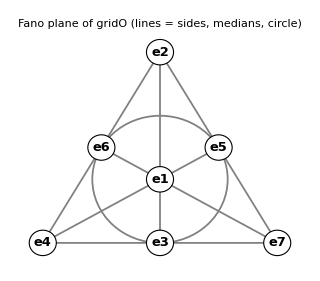

```mathematica
fanoPicture = Module[{pos, lines},
   pos = <|1 -> {0, 0}, 2 -> {0, 2}, 4 -> {-Sqrt[3], -1}, 7 -> {Sqrt[3], -1}, 6 -> {-Sqrt[3]/2, 1/2}, 5 -> {Sqrt[3]/2, 1/2}, 3 -> {0, -1}|>;
   Graphics[{Thickness[0.004], Gray,
     Line[{pos[2], pos[4]}], Line[{pos[4], pos[7]}], Line[{pos[7], pos[2]}],
     Line[{pos[2], pos[3]}], Line[{pos[4], pos[5]}], Line[{pos[7], pos[6]}], Circle[{0, 0}, 1],
     Table[{White, EdgeForm[Black], Disk[pos[k], 0.2], Black, Text[Style["e" <> ToString[k], 13, Bold], pos[k]]}, {k, 1, 7}]},
    ImageSize -> 320, PlotLabel -> Style["Fano plane of gridO (lines = sides, medians, circle)", 12]]];
check["the picture's 7 lines are exactly fanoLines", Sort[Sort /@ {{2, 6, 4}, {4, 3, 7}, {7, 5, 2}, {2, 1, 3}, {4, 1, 5}, {7, 1, 6}, {6, 5, 3}}] == fanoLines]
fanoPicture
```

#### Alternativity, Moufang identities, norm, conjugation, inverse (symbolic proofs)

xs, ys, zs are general octonions with symbolic components a[0..7], b[0..7], c[0..7]. Identities that are linear in some arguments (Moufang) are proven by letting those arguments run over the basis, which is enough by linearity.

```mathematica
check["left alternative: x(xy) == (xx)y (symbolic)", Expand[oMul[xs, oMul[xs, ys]] - oMul[oMul[xs, xs], ys]] === zero8]
check["right alternative: (yx)x == y(xx) (symbolic)", Expand[oMul[oMul[ys, xs], xs] - oMul[ys, oMul[xs, xs]]] === zero8]
check["flexible: (xy)x == x(yx) (symbolic)", Expand[oMul[oMul[xs, ys], xs] - oMul[xs, oMul[ys, xs]]] === zero8]
check["associator is alternating: [x,y,z] == -[y,x,z] == -[x,z,y] (symbolic)",
  Expand[oAssoc[xs, ys, zs] + oAssoc[ys, xs, zs]] === zero8 && Expand[oAssoc[xs, ys, zs] + oAssoc[xs, zs, ys]] === zero8]
check["power associativity: x(xx) == (xx)x (symbolic)", Expand[oMul[xs, oMul[xs, xs]] - oMul[oMul[xs, xs], xs]] === zero8]
check["Moufang: z(x(zy)) == ((zx)z)y, x(z(yz)) == ((xz)y)z, (zx)(yz) == (z(xy))z (x, y basis units, z symbolic)",
  And @@ Flatten[Table[With[{xx = ev[A], yy = ev[K]},
      Expand[oMul[zs, oMul[xx, oMul[zs, yy]]] - oMul[oMul[oMul[zs, xx], zs], yy]] === zero8 &&
      Expand[oMul[xx, oMul[zs, oMul[yy, zs]]] - oMul[oMul[oMul[xx, zs], yy], zs]] === zero8 &&
      Expand[oMul[oMul[zs, xx], oMul[yy, zs]] - oMul[oMul[zs, oMul[xx, yy]], zs]] === zero8], {A, 0, 7}, {K, 0, 7}]]]
check["x x̄ == x̄ x == N(x) e[0] (symbolic)",
  Expand[oMul[xs, oConj[xs]] - oNorm2[xs] ev[0]] === zero8 && Expand[oMul[oConj[xs], xs] - oNorm2[xs] ev[0]] === zero8]
check["conjugation is an anti-automorphism: conj(xy) == conj(y) conj(x) (symbolic)",
  Expand[oConj[oMul[xs, ys]] - oMul[oConj[ys], oConj[xs]]] === zero8]
check["Re(x) == (x + x̄)/2 == x0", (xs + oConj[xs])/2 == oRe[xs] ev[0] && oRe[xs] === a[0]]
check["norm is multiplicative: N(xy) == N(x) N(y) (symbolic; Degen's eight-square identity)",
  Expand[oNorm2[oMul[xs, ys]] - oNorm2[xs] oNorm2[ys]] === 0]
check["inverse x^-1 = x̄/N(x): x x^-1 == x^-1 x == e[0] (symbolic)",
  Simplify[oMul[xs, oInv[xs]] - ev[0]] === zero8 && Simplify[oMul[oInv[xs], xs] - ev[0]] === zero8]
check["every x satisfies x x - 2 Re(x) x + N(x) e[0] == 0, so the subalgebra generated by x is ℝ or ℂ",
  Expand[oMul[xs, xs] - 2 oRe[xs] xs + oNorm2[xs] ev[0]] === zero8]
```

left alternative: x(xy) == (xx)y (symbolic)→True

right alternative: (yx)x == y(xx) (symbolic)→True

flexible: (xy)x == x(yx) (symbolic)→True

associator is alternating: [x,y,z] == -[y,x,z] == -[x,z,y] (symbolic)→True

power associativity: x(xx) == (xx)x (symbolic)→True

Moufang: z(x(zy)) == ((zx)z)y, x(z(yz)) == ((xz)y)z, (zx)(yz) == (z(xy))z (x, y basis units, z symbolic)→True

x x̄ == x̄ x == N(x) e[0] (symbolic)→True

conjugation is an anti-automorphism: conj(xy) == conj(y) conj(x) (symbolic)→True

Re(x) == (x + x̄)/2 == x0→True

norm is multiplicative: N(xy) == N(x) N(y) (symbolic; Degen's eight-square identity)→True

inverse x^-1 = x̄/N(x): x x^-1 == x^-1 x == e[0] (symbolic)→True

every x satisfies x x - 2 Re(x) x + N(x) e[0] == 0, so the subalgebra generated by x is ℝ or ℂ→True

Degen’s eight-square identity, explicitly: the eight components of x y are bilinear forms, and the sum of their squares equals (a0.b2 + … + a7.b2)(b0.b2 + … + b7.b2). Hence N(x) = 0 forces x = 0, and xy = 0 forces x = 0 or y = 0: unlike the split octonions, the octonions have no zero divisors (a division algebra).

```mathematica
TableForm[Thread[{Table["(x y)_" <> ToString[k], {k, 0, 7}], oMul[xs, ys]}]]
```

(x y)_0 | a[0] b[0]-a[1] b[1]-a[2] b[2]-a[3] b[3]-a[4] b[4]-a[5] b[5]-a[6] b[6]-a[7] b[7]
(x y)_1 | a[1] b[0]+a[0] b[1]+a[3] b[2]-a[2] b[3]+a[5] b[4]-a[4] b[5]-a[7] b[6]+a[6] b[7]
(x y)_2 | a[2] b[0]-a[3] b[1]+a[0] b[2]+a[1] b[3]+a[6] b[4]+a[7] b[5]-a[4] b[6]-a[5] b[7]
(x y)_3 | a[3] b[0]+a[2] b[1]-a[1] b[2]+a[0] b[3]+a[7] b[4]-a[6] b[5]+a[5] b[6]-a[4] b[7]
(x y)_4 | a[4] b[0]-a[5] b[1]-a[6] b[2]-a[7] b[3]+a[0] b[4]+a[1] b[5]+a[2] b[6]+a[3] b[7]
(x y)_5 | a[5] b[0]+a[4] b[1]-a[7] b[2]+a[6] b[3]-a[1] b[4]+a[0] b[5]-a[3] b[6]+a[2] b[7]
(x y)_6 | a[6] b[0]+a[7] b[1]+a[4] b[2]-a[5] b[3]-a[2] b[4]+a[3] b[5]+a[0] b[6]-a[1] b[7]
(x y)_7 | a[7] b[0]-a[6] b[1]+a[5] b[2]+a[4] b[3]-a[3] b[4]-a[2] b[5]+a[1] b[6]+a[0] b[7]

#### Non-associativity and a numerical example

```mathematica
nonAssociativeTriples = Select[Tuples[Range[0, 7], 3], oAssoc[ev[#[[1]]], ev[#[[2]]], ev[#[[3]]]] =!= zero8 &];
check["exactly 168 of the 512 ordered basis triples are non-associative (= 7*6*4: distinct imaginary units not on one Fano line)",
  Length[nonAssociativeTriples] == 168 && AllTrue[nonAssociativeTriples, (Min[#] >= 1 && Length[Union[#]] == 3 && ! MemberQ[fanoLines, Sort[#]]) &]]
check["example: (e[1]e[2])e[4] == e[7] but e[1](e[2]e[4]) == -e[7]",
  toE[oMul[oMul[ev[1], ev[2]], ev[4]]] === e[7] && toE[oMul[ev[1], oMul[ev[2], ev[4]]]] === -e[7]]
```

exactly 168 of the 512 ordered basis triples are non-associative (= 7*6*4: distinct imaginary units not on one Fano line)→True

example: (e[1]e[2])e[4] == e[7] but e[1](e[2]e[4]) == -e[7]→True

```mathematica
xNum = {1, 2, 0, 0, -1, 0, 0, 3}; yNum = {-2, 0, 1, 0, 0, 1, 0, 0}; zNum = {0, 0, 0, 1, 0, 0, 1, 0};
Grid[{{"x", toE[xNum]}, {"y", toE[yNum]}, {"z", toE[zNum]}, {"x y", toE[oMul[xNum, yNum]]}, {"y x", toE[oMul[yNum, xNum]]},
   {"N(x), N(y), N(x y)", {oNorm2[xNum], oNorm2[yNum], oNorm2[oMul[xNum, yNum]]}}, {"x^-1", toE[oInv[xNum]]},
   {"x x^-1", toE[oMul[xNum, oInv[xNum]]]}, {"(x y) z - x (y z)", toE[oAssoc[xNum, yNum, zNum]]}}, Frame -> All, Alignment -> Left]
```

x | e[0]+2 e[1]-e[4]+3 e[7]
y | -2 e[0]+e[2]+e[5]
z | e[3]+e[6]
x y | -2 e[0]-3 e[1]+4 e[2]-2 e[3]+4 e[4]-2 e[5]-e[6]-6 e[7]
y x | -2 e[0]-5 e[1]-2 e[2]+2 e[3]+4 e[5]+e[6]-6 e[7]
N(x), N(y), N(x y) | {15,6,90}
x^-1 | e[0]/15-(2 e[1])/15+e[4]/15-e[7]/5
x x^-1 | e[0]
(x y) z - x (y z) | -6 e[1]-2 e[2]-6 e[3]+6 e[4]+2 e[5]+6 e[6]+6 e[7]

```mathematica
check["numerical example: N(x y) == N(x) N(y) == 15*6 == 90 and x x^-1 == e[0]",
  oNorm2[oMul[xNum, yNum]] == oNorm2[xNum] oNorm2[yNum] == 90 && oMul[xNum, oInv[xNum]] == ev[0]]
check["numerical example: x y != y x and (x y) z != x (y z)", oMul[xNum, yNum] != oMul[yNum, xNum] && oAssoc[xNum, yNum, zNum] != zero8]
```

numerical example: N(x y) == N(x) N(y) == 15*6 == 90 and x x^-1 == e[0]→True

numerical example: x y != y x and (x y) z != x (y z)→True

### 3.5 Cayley–Dickson doubling: 𝕆 = ℍ ⊕ ℓℍ

The span of e[0], e[1], e[2], e[3] — the time direction and the three ordinary space directions x0 … x3 — is a quaternion subalgebra ℍ, and ℓ = e[4] doubles it: e[4+k] = ℓ e[k] (k = 1, 2, 3). Every octonion is x = a + ℓ b with quaternions a = (x0, x1, x2, x3) and b = (x4, x5, x6, x7). Orientation inherited from 4+4.nb: e[1] e[2] = −e[3], so i = e[1], j = e[2], k = −e[3] are Hamilton’s units. With ℓ.b2 = γ the product is

(a, b)(c, d) = (a c + γ d b̄,  ā d + c b),     γ = −1: octonions,   γ = +1: split octonions.

```mathematica
qMul[p1_List, p2_List] := Take[oMul[Join[p1, {0, 0, 0, 0}], Join[p2, {0, 0, 0, 0}]], 4];
qConj[p1_List] := {p1[[1]], -p1[[2]], -p1[[3]], -p1[[4]]};
asPair[xx_List] := {Take[xx, 4], Take[xx, -4]};                       (* x = a + ℓ b  <->  {a, b} *)
cdMul[γ_][{a1_, b1_}, {a2_, b2_}] := {qMul[a1, a2] + γ qMul[b2, qConj[b1]], qMul[qConj[a1], b2] + qMul[a2, b1]};
check["ℍ = span{e[0],e[1],e[2],e[3]} is a subalgebra", And @@ Flatten[Table[Take[oMul[ev[A], ev[K]], -4] == {0, 0, 0, 0}, {A, 0, 3}, {K, 0, 3}]]]
check["ℓ = e[4] doubles ℍ: e[4] e[k] == e[4+k] (k = 1,2,3) and e[4] e[4] == -e[0]",
  And @@ Table[oMul[ev[4], ev[k]] == ev[4 + k], {k, 1, 3}] && oMul[ev[4], ev[4]] == -ev[0]]
check["orientation inherited from 4+4.nb: e[1] e[2] == -e[3]", oMul[ev[1], ev[2]] == -ev[3]]
check["Cayley-Dickson, γ = -1: (ac - d b̄, ā d + c b) reproduces the octonion product (symbolic)",
  Expand[Flatten[cdMul[-1][asPair[xs], asPair[ys]]] - oMul[xs, ys]] === zero8]
check["Cayley-Dickson, γ = +1: (ac + d b̄, ā d + c b) reproduces the SPLIT product of 4+4.nb (symbolic)",
  Expand[Flatten[cdMul[+1][asPair[xs], asPair[ys]]] - sMul[xs, ys]] === zero8]
```

ℍ = span{e[0],e[1],e[2],e[3]} is a subalgebra→True

ℓ = e[4] doubles ℍ: e[4] e[k] == e[4+k] (k = 1,2,3) and e[4] e[4] == -e[0]→True

orientation inherited from 4+4.nb: e[1] e[2] == -e[3]→True

Cayley-Dickson, γ = -1: (ac - d b̄, ā d + c b) reproduces the octonion product (symbolic)→True

Cayley-Dickson, γ = +1: (ac + d b̄, ā d + c b) reproduces the SPLIT product of 4+4.nb (symbolic)→True

The second formula of [1A], (a,b)(c,d) = (ac − d̄ b, ā d + c b), mixes two conventions. It fails already for x = e[0] + e[4] = (1, 1) and y = e[1] = (i, 0) (no product of two imaginary quaternion units occurs, so the orientation of ℍ does not matter): x.b2 = (0, 2), x.b2y = (0, 2i), but x y = (i, i) and x(xy) = (2i, 2i).

```mathematica
cdPrompt[{a1_, b1_}, {a2_, b2_}] := {qMul[a1, a2] - qMul[qConj[b2], b1], qMul[qConj[a1], b2] + qMul[a2, b1]};
pm[xx_List, yy_List] := Flatten[cdPrompt[asPair[xx], asPair[yy]]];
promptX = ev[0] + ev[4]; promptY = ev[1];
{toE[pm[pm[promptX, promptX], promptY]], toE[pm[promptX, pm[promptX, promptY]]]}
```

{2 e[5],2 e[1]+2 e[5]}

```mathematica
check["the formula (ac - d̄ b, ā d + c b) of [1A] is NOT alternative: x·x·y != x(xy) for x = e[0]+e[4], y = e[1]",
  pm[pm[promptX, promptX], promptY] =!= pm[promptX, pm[promptX, promptY]]]
check["... and its norm is not multiplicative (symbolic)", Expand[oNorm2[pm[xs, ys]] - oNorm2[xs] oNorm2[ys]] =!= 0]
```

the formula (ac - d̄ b, ā d + c b) of [1A] is NOT alternative: x·x·y != x(xy) for x = e[0]+e[4], y = e[1]→True

... and its norm is not multiplicative (symbolic)→True

### 3.6 Octonions versus split octonions

Comparing gridO with gridx44 (relabelled 0-based, eA[B] → e[B−1]): e[A]e[B] (octonion) = s_AB × e[A]e[B] (split), with s_AB = −1 when both A ≥ 4 and B ≥ 4, and s_AB = +1 otherwise. Only products of two “doubled” units change sign, because ℓ.b2 = −1 instead of +1. Over ℂ the two algebras are isomorphic: ϕ(eA[A+1]) = c_A e[A] with c = (1, 1, 1, 1, i, i, i, i).

```mathematica
sAB[A_, K_] := If[A >= 4 && K >= 4, -1, 1];
check["e[A]e[B] (octonion) == s_AB e[A]e[B] (split) for all A, B = 0..7",
  And @@ Flatten[Table[oMul[ev[A], ev[K]] == sAB[A, K] sMul[ev[A], ev[K]], {A, 0, 7}, {K, 0, 7}]]]
cc = {1, 1, 1, 1, I, I, I, I};
φ[xx_List] := cc xx;
check["over ℂ: φ(x *split y) == φ(x) *oct φ(y) (symbolic): split ⊗ ℂ ≅ 𝕆 ⊗ ℂ",
  Expand[φ[sMul[xs, ys]] - oMul[φ[xs], φ[ys]]] === zero8]
check["the norms correspond: N_oct(φ(x)) == N_split(x) (symbolic)", Expand[oNorm2[φ[xs]] - sNorm2[xs]] === 0]
```

e[A]e[B] (octonion) == s_AB e[A]e[B] (split) for all A, B = 0..7→True

over ℂ: φ(x *split y) == φ(x) *oct φ(y) (symbolic): split ⊗ ℂ ≅ 𝕆 ⊗ ℂ→True

the norms correspond: N_oct(φ(x)) == N_split(x) (symbolic)→True

## 4. Clifford algebras from the octonions: 16×16 matrices

### 4.1 The exact mirror of T16: the Euclidean Clifford algebra Cl(8,0)

Copying the 4+4.nb definition T16[A] = {{0, τbar[A]}, {τ[A], 0}} with τ → τO and τbar → τObar gives real 16×16 matrices T16O[A] whose anticommutators are governed by the octonion norm gO = ID8: they generate Cl(8,0) ≅ ℝ(16). They can be written with the 4+4 matrices alone: T16O[A] = T16[A] for A = 0 … 3 and T16O[k] = T16[k].S44 for k = 4 … 7, where S44 = T16[4].T16[5].T16[6].T16[7] = diag(σ, σ).

```mathematica
Do[T16O[A] = ArrayFlatten[{{0, τObar[A]}, {τO[A], 0}}], {A, 0, 7}];
T16O[8] = Dot @@ Table[T16O[A], {A, 0, 7}];
S44 = T16[4].T16[5].T16[6].T16[7];
check["Cl(8,0): (T16O[A].T16O[B] + T16O[B].T16O[A])/2 == gO[[A+1,B+1]] ID16",
  And @@ Flatten[Table[(T16O[A].T16O[B] + T16O[B].T16O[A])/2 == gO[[A + 1, B + 1]] ID16, {A, 0, 7}, {B, 0, 7}]]]
check["S44 == diag(σ, σ)", S44 == ArrayFlatten[{{σ, 0}, {0, σ}}]]
check["T16O from the 4+4 matrices: T16O[A] == T16[A] (A = 0..3), T16O[k] == T16[k].S44 (k = 4..7)",
  And @@ Table[T16O[A] == T16[A], {A, 0, 3}] && And @@ Table[T16O[k] == T16[k].S44, {k, 4, 7}]]
check["T16O[8] == T16[8] == diag(-ID8, ID8): same chirality matrix and same PL44, PR44 as 4+4.nb",
  T16O[8] == T16[8] == ArrayFlatten[{{-ID8, 0}, {0, ID8}}]]
```

Cl(8,0): (T16O[A].T16O[B] + T16O[B].T16O[A])/2 == gO[[A+1,B+1]] ID16→True

S44 == diag(σ, σ)→True

T16O from the 4+4 matrices: T16O[A] == T16[A] (A = 0..3), T16O[k] == T16[k].S44 (k = 4..7)→True

T16O[8] == T16[8] == diag(-ID8, ID8): same chirality matrix and same PL44, PR44 as 4+4.nb→True

### 4.2 The REAL Clifford algebra of 7+1 spacetime: Γ17, Cl(1,7) ≅ ℝ(16)

Definition. Γ17[0] = T16O[0] (time) and Γ17[i] = T16O[0].T16O[i] (i = 1 … 7, space). Then

Γ17[A].Γ17[B] + Γ17[B].Γ17[A] = 2 η17[[A+1,B+1]] ID16 = −2 η71[[A+1,B+1]] ID16:

time squares to +ID16, each of the seven space directions to −ID16 — the same signs as the squares of the octonion basis, e[0].b2 = +1 and e[i].b2 = −1, which η17 = diag(+1, −1, …, −1) simply lists. In block form Γ17[0] = {{0, ID8}, {ID8, 0}} (the same block form as T16[0]) and Γ17[i] = {{τO[i], 0}, {0, τObar[i]}} (block-diagonal). With the 4+4 matrices only: Γ17[0] = T16[0], Γ17[i] = T16[0].T16[i] (i = 1, 2, 3), Γ17[k] = T16[0].T16[k].S44 (k = 4 … 7). All entries are 0 or ±1.

Why this is the Clifford algebra of [1B]. (i) The linear map v ↦ Γ17(v) = Σ v^A Γ17[A] satisfies Γ17(v).b2 = Q(v) ID16 with Q(v) = v.η17.v, so by the universal property of Cl(V,Q) = T(V)/I_Q(V) it extends to an algebra homomorphism Cl(V,Q) → ℝ(16). (ii) The 256 ordered products Γ17[A1]…Γ17[Ak] (A1 < … < Ak) are linearly independent, so the homomorphism is injective; both sides have dimension 256, so it is an isomorphism Cl(1,7) ≅ ℝ(16).

```mathematica
Γ17[0] = T16O[0];
Do[Γ17[i] = T16O[0].T16O[i], {i, 1, 7}];
Γ17[8] = Dot @@ Table[Γ17[A], {A, 0, 7}];
check["7+1 REAL Clifford relation: (Γ17[A].Γ17[B] + Γ17[B].Γ17[A])/2 == η17[[A+1,B+1]] ID16 == -η71[[A+1,B+1]] ID16",
  And @@ Flatten[Table[(Γ17[A].Γ17[B] + Γ17[B].Γ17[A])/2 == η17[[A + 1, B + 1]] ID16 == -η71[[A + 1, B + 1]] ID16, {A, 0, 7}, {B, 0, 7}]]]
check["Γ17[A] are REAL: every entry is 0 or ±1", And @@ Table[SubsetQ[{-1, 0, 1}, Union[Flatten[Γ17[A]]]], {A, 0, 7}]]
check["block form: Γ17[0] == {{0,ID8},{ID8,0}}, Γ17[i] == {{τO[i],0},{0,τObar[i]}}",
  Γ17[0] == ArrayFlatten[{{0, ID8}, {ID8, 0}}] && And @@ Table[Γ17[i] == ArrayFlatten[{{τO[i], 0}, {0, τObar[i]}}], {i, 1, 7}]]
check["built from the real 4+4 matrices: Γ17[0] == T16[0], Γ17[i] == T16[0].T16[i] (i = 1,2,3), Γ17[k] == T16[0].T16[k].S44 (k = 4..7)",
  Γ17[0] == T16[0] && And @@ Table[Γ17[i] == T16[0].T16[i], {i, 1, 3}] && And @@ Table[Γ17[k] == T16[0].T16[k].S44, {k, 4, 7}]]
check["Γ17[0] symmetric, Γ17[i] antisymmetric, so Transpose[Γ17[A]] == Γ17[0].Γ17[A].Γ17[0] (real Dirac adjoint)",
  Transpose[Γ17[0]] == Γ17[0] && And @@ Table[Transpose[Γ17[i]] == -Γ17[i], {i, 1, 7}] &&
  And @@ Table[Transpose[Γ17[A]] == Γ17[0].Γ17[A].Γ17[0], {A, 0, 7}]]
```

7+1 REAL Clifford relation: (Γ17[A].Γ17[B] + Γ17[B].Γ17[A])/2 == η17[[A+1,B+1]] ID16 == -η71[[A+1,B+1]] ID16→True

Γ17[A] are REAL: every entry is 0 or ±1→True

block form: Γ17[0] == {{0,ID8},{ID8,0}}, Γ17[i] == {{τO[i],0},{0,τObar[i]}}→True

built from the real 4+4 matrices: Γ17[0] == T16[0], Γ17[i] == T16[0].T16[i] (i = 1,2,3), Γ17[k] == T16[0].T16[k].S44 (k = 4..7)→True

Γ17[0] symmetric, Γ17[i] antisymmetric, so Transpose[Γ17[A]] == Γ17[0].Γ17[A].Γ17[0] (real Dirac adjoint)→True

```mathematica
Grid[Partition[Table[Column[{Style["Γ17[" <> ToString[A] <> "]", Bold], MatrixForm[Γ17[A]]}, Alignment -> Center], {A, 0, 7}], 2], Spacings -> {3, 2}]
```

Γ17[0]
(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0) | Γ17[1]
(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
Γ17[2]
(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0) | Γ17[3]
(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0)
Γ17[4]
(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0) | Γ17[5]
(0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0)
Γ17[6]
(0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0) | Γ17[7]
(0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0)

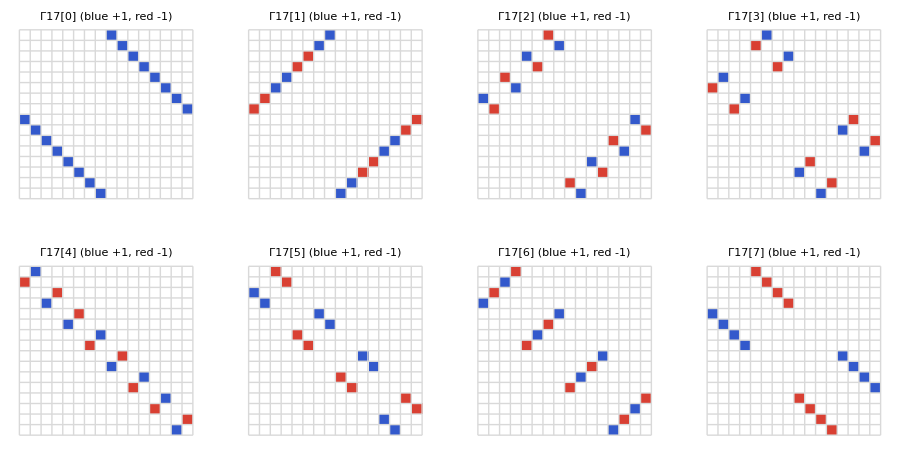

```mathematica
GraphicsGrid[Partition[Table[ArrayPlot[Γ17[A], ColorRules -> {1 -> RGBColor[0.2, 0.35, 0.8], -1 -> RGBColor[0.85, 0.25, 0.2], 0 -> White},
     Mesh -> True, MeshStyle -> GrayLevel[0.85], Frame -> False, PlotLabel -> "Γ17[" <> ToString[A] <> "]   (blue +1, red -1)"], {A, 0, 7}], 4], ImageSize -> 900]
```

```mathematica
products256 = Table[Dot @@ Prepend[Γ17 /@ s, ID16], {s, Subsets[Range[0, 7]]}];
check["the 256 products Γ17[A1]...Γ17[Ak] (A1 < ... < Ak) are linearly independent: Cl(1,7) ≅ ℝ(16)",
  Length[products256] == 256 && MatrixRank[Flatten /@ products256] == 256]
check["grades: binomial(8,k) == {1,8,28,56,70,56,28,8,1}, total 256 (binomial(8,4) == 70, not 72)",
  Table[Binomial[8, k], {k, 0, 8}] == {1, 8, 28, 56, 70, 56, 28, 8, 1} && Total[Table[Binomial[8, k], {k, 0, 8}]] == 256 &&
  Table[Count[Subsets[Range[0, 7]], s_ /; Length[s] == k], {k, 0, 8}] == Table[Binomial[8, k], {k, 0, 8}]]
check["Tr[product] == 0 for every non-empty product, so Tr[M]/16 is the scalar part of M", And @@ Table[Tr[products256[[k]]] == 0, {k, 2, 256}]]
check["irreducible over ℝ: only multiples of ID16 commute with all Γ17[A] (Schur; real commutant of dimension 1)",
  With[{ns = NullSpace[Join @@ Table[KroneckerProduct[ID16, Transpose[Γ17[A]]] - KroneckerProduct[Γ17[A], ID16], {A, 0, 7}]]},
   Length[ns] == 1 && MatrixRank[{First[ns], Flatten[ID16]}] == 1]]
check["universal property: Γ17(v).Γ17(v) == (v.η17.v) ID16 for a symbolic vector v = X",
  Expand[Sum[X[[A + 1]] Γ17[A], {A, 0, 7}].Sum[X[[A + 1]] Γ17[A], {A, 0, 7}] - (X.η17.X) ID16] === Zero16]
```

the 256 products Γ17[A1]...Γ17[Ak] (A1 < ... < Ak) are linearly independent: Cl(1,7) ≅ ℝ(16)→True

grades: binomial(8,k) == {1,8,28,56,70,56,28,8,1}, total 256 (binomial(8,4) == 70, not 72)→True

Tr[product] == 0 for every non-empty product, so Tr[M]/16 is the scalar part of M→True

irreducible over ℝ: only multiples of ID16 commute with all Γ17[A] (Schur; real commutant of dimension 1)→True

universal property: Γ17(v).Γ17(v) == (v.η17.v) ID16 for a symbolic vector v = X→True

### 4.3 The complexified 7+1 realization in the exact block form of 4+4.nb: Γ71

If one insists on the 4+4.nb sign convention, Γ71[A].Γ71[B] + Γ71[B].Γ71[A] = 2 η71[[A+1,B+1]] ID16, complex numbers are unavoidable (section 4.4). The complexification needed is minimal: multiply the time block by i. With τC[0] = τCbar[0] = i ID8 and τC[i] = τO[i], τCbar[i] = τObar[i] (i = 1 … 7),

Γ71[A] = {{0, τCbar[A]}, {τC[A], 0}},

which is literally the formula T16[A] = {{0, τbar[A]}, {τ[A], 0}} of 4+4.nb. Equivalently Γ71[0] = i T16[0] and Γ71[k] = T16O[k] (k = 1 … 7). Γ71 is equivalent to i Γ17: Γ71[A] = S.(i Γ17[A]).S⁻.b9 with the unitary matrix S = (ID16 − i Γ17[0])/√2.

```mathematica
τC[0] = I ID8; τCbar[0] = I ID8;
Do[τC[i] = τO[i]; τCbar[i] = τObar[i], {i, 1, 7}];
Do[Γ71[A] = ArrayFlatten[{{0, τCbar[A]}, {τC[A], 0}}], {A, 0, 7}];
Γ71[8] = Dot @@ Table[Γ71[A], {A, 0, 7}];
check["7+1 COMPLEX Clifford relation, 4+4.nb sign: (Γ71[A].Γ71[B] + Γ71[B].Γ71[A])/2 == η71[[A+1,B+1]] ID16",
  And @@ Flatten[Table[(Γ71[A].Γ71[B] + Γ71[B].Γ71[A])/2 == η71[[A + 1, B + 1]] ID16, {A, 0, 7}, {B, 0, 7}]]]
check["Γ71[0] == I T16[0] and Γ71[k] == T16O[k] (k = 1..7): only the time component is complex",
  Γ71[0] == I T16[0] && And @@ Table[Γ71[k] == T16O[k], {k, 1, 7}]]
Ssim = (ID16 - I Γ17[0])/Sqrt[2];
check["S = (ID16 - I Γ17[0])/Sqrt[2] is unitary and Γ71[A] == S.(I Γ17[A]).Inverse[S]",
  Simplify[Ssim.ConjugateTranspose[Ssim]] == ID16 && And @@ Table[Simplify[Ssim.(I Γ17[A]).Inverse[Ssim] - Γ71[A]] == Zero16, {A, 0, 7}]]
```

7+1 COMPLEX Clifford relation, 4+4.nb sign: (Γ71[A].Γ71[B] + Γ71[B].Γ71[A])/2 == η71[[A+1,B+1]] ID16→True

Γ71[0] == I T16[0] and Γ71[k] == T16O[k] (k = 1..7): only the time component is complex→True

S = (ID16 - I Γ17[0])/Sqrt[2] is unitary and Γ71[A] == S.(I Γ17[A]).Inverse[S]→True

### 4.4 Theorem: with η71 there is no real 16×16 realization, because Cl(7,1) ≅ ℍ(8)

Theorem. There are no real 16×16 matrices R[0], …, R[7] with R[A].R[B] + R[B].R[A] = 2 η71[[A+1,B+1]] ID16. Reordering, renaming or re-signing the indices does not help, because none of these changes the signature (7,1).

Proof. The complexified Clifford algebra is Cl_8(ℂ) ≅ ℂ(16), which has exactly one irreducible module, ℂ^16. If real R[A] existed, they and the complex Γ71[A] of section 4.3 would both be 16-dimensional modules, so R[A] = T.Γ71[A].T⁻.b9 for some invertible complex T. Complex conjugation of this equation (R is real) gives M.Conjugate[Γ71[A]] = Γ71[A].M with M = T⁻.b9.Conjugate[T], and then M.Conjugate[M] = ID16. By Schur’s lemma all such intertwiners M form a one-dimensional space; the computation below shows that it is spanned by M0 = Γ17[8] (the volume element) and that M0.Conjugate[M0] = −ID16. Hence M = c M0 and M.Conjugate[M] = −|c|.b2 ID16 ≠ ID16, a contradiction. ∎

The sign of M.Conjugate[M] is a Frobenius–Schur-type indicator: +1 means the complex 16-dimensional module has a real form (the algebra is ℝ(16)), −1 means it is quaternionic (the algebra is ℍ(8), whose smallest real module is ℍ^8 = ℝ^32). For η17 the indicator is +1, in agreement with the real matrices Γ17 of section 4.2.

```mathematica
intertwiners[gs_List] := Module[{n = Length[First[gs]], sys},
   sys = Join @@ Table[KroneckerProduct[IdentityMatrix[n], Transpose[Conjugate[g]]] - KroneckerProduct[g, IdentityMatrix[n]], {g, gs}];
   Partition[#, n] & /@ NullSpace[sys]];       (* all M with M.Conjugate[g] == g.M for every g in gs *)
indicator[gs_List] := Module[{M = First[intertwiners[gs]], P}, P = M.Conjugate[M];
   If[P == P[[1, 1]] IdentityMatrix[Length[P]], Sign[P[[1, 1]]], "not scalar"]];
M71 = intertwiners[Table[Γ71[A], {A, 0, 7}]];
check["Schur: the intertwiners M with M.Conjugate[Γ71[A]] == Γ71[A].M form a 1-dimensional space", Length[M71] == 1]
check["... spanned by the volume element Γ17[8] == {{0,-ID8},{ID8,0}}, and Γ17[8].Γ17[8] == -ID16",
  Γ17[8] == ArrayFlatten[{{0, -ID8}, {ID8, 0}}] &&
  MatrixRank[{Flatten[First[M71]], Flatten[Γ17[8]]}] == 1 && Γ17[8].Γ17[8] == -ID16 &&
  And @@ Table[Γ17[8].Conjugate[Γ71[A]] == Γ71[A].Γ17[8], {A, 0, 7}]]
check["indicator(Γ71) == -1: Cl(7,1) ≅ ℍ(8), NO real 16×16 realization of the η71 relation",
  indicator[Table[Γ71[A], {A, 0, 7}]] == -1]
check["indicator(Γ17) == +1: Cl(1,7) ≅ ℝ(16), real realization exists (Γ17)",
  indicator[Table[Γ17[A], {A, 0, 7}]] == 1]
```

Schur: the intertwiners M with M.Conjugate[Γ71[A]] == Γ71[A].M form a 1-dimensional space→True

... spanned by the volume element Γ17[8] == {{0,-ID8},{ID8,0}}, and Γ17[8].Γ17[8] == -ID16→True

indicator(Γ71) == -1: Cl(7,1) ≅ ℍ(8), NO real 16×16 realization of the η71 relation→True

indicator(Γ17) == +1: Cl(1,7) ≅ ℝ(16), real realization exists (Γ17)→True

### 4.5 A real realization of Cl(7,1) needs 32×32 matrices

With ϵ = {{0, 1}, {−1, 0}} (real, ϵ.ϵ = −ID2), Γ71R32[A] = ϵ ⊗ Γ17[A] are real 32×32 matrices satisfying the η71 relation. Their commutant (all matrices commuting with every Γ71R32[A]) is spanned by ID32, Qi = ϵ⊗ID16, Qj = σ₁⊗Γ17[8], Qk = σ₃⊗Γ17[8], with Qi.b2 = Qj.b2 = Qk.b2 = −ID32 and Qi.Qj = Qk: the quaternions. This is Cl(7,1) ≅ ℍ(8) acting on ℝ^32 = ℍ^8.

```mathematica
ϵ2 = {{0, 1}, {-1, 0}};
Do[Γ71R32[A] = KroneckerProduct[ϵ2, Γ17[A]], {A, 0, 7}];
check["REAL 32×32 realization of the η71 relation: (Γ71R32[A].Γ71R32[B] + Γ71R32[B].Γ71R32[A])/2 == η71[[A+1,B+1]] ID32",
  And @@ Flatten[Table[(Γ71R32[A].Γ71R32[B] + Γ71R32[B].Γ71R32[A])/2 == η71[[A + 1, B + 1]] ID32, {A, 0, 7}, {B, 0, 7}]] &&
  And @@ Table[SubsetQ[{-1, 0, 1}, Union[Flatten[Γ71R32[A]]]], {A, 0, 7}]]
Qi = KroneckerProduct[ϵ2, ID16]; Qj = KroneckerProduct[{{0, 1}, {1, 0}}, Γ17[8]]; Qk = KroneckerProduct[{{1, 0}, {0, -1}}, Γ17[8]];
check["Qi, Qj, Qk commute with every Γ71R32[A]; Qi.Qi == Qj.Qj == Qk.Qk == -ID32; Qi.Qj == Qk == -Qj.Qi",
  And @@ Flatten[Table[q.Γ71R32[A] == Γ71R32[A].q, {q, {Qi, Qj, Qk}}, {A, 0, 7}]] &&
  Qi.Qi == -ID32 && Qj.Qj == -ID32 && Qk.Qk == -ID32 && Qi.Qj == Qk && Qj.Qi == -Qk]
{commutantTime, commutantBasis} = AbsoluteTiming[NullSpace[Join @@ Table[
       KroneckerProduct[SparseArray[ID32], SparseArray[Transpose[Γ71R32[A]]]] - KroneckerProduct[SparseArray[Γ71R32[A]], SparseArray[ID32]], {A, 0, 7}]]];
check["the commutant of {Γ71R32[A]} has dimension exactly 4 and is spanned by ID32, Qi, Qj, Qk: it is ℍ",
  Length[commutantBasis] == 4 && MatrixRank[Join[Normal[commutantBasis], Flatten /@ {ID32, Qi, Qj, Qk}]] == 4]
commutantTime
```

REAL 32×32 realization of the η71 relation: (Γ71R32[A].Γ71R32[B] + Γ71R32[B].Γ71R32[A])/2 == η71[[A+1,B+1]] ID32→True

Qi, Qj, Qk commute with every Γ71R32[A]; Qi.Qi == Qj.Qj == Qk.Qk == -ID32; Qi.Qj == Qk == -Qj.Qi→True

the commutant of {Γ71R32[A]} has dimension exactly 4 and is spanned by ID32, Qi, Qj, Qk: it is ℍ→True

1.03573

### 4.6 Volume elements and chirality

In 4+4.nb the volume element T16[8] = T16[0]…T16[7] = diag(−ID8, ID8) squares to +ID16 and gives the real chiral projectors PL44, PR44; the same holds for T16O[8]. For the real 7+1 matrices the volume element Γ17[8] squares to −ID16: it is a complex structure, so there is NO real chirality projector. The real 16-component spinors of 7+1 spacetime (the vectors of ℝ^16 on which the real matrices Σ17[A,B] of section 5.1 act) cannot be split into real Weyl halves; with J = Γ17[8] (which commutes with all Σ17[A,B]) as the multiplication by i, the real 16-dimensional spin module is one complex 8-dimensional Weyl module. With complex numbers the chirality matrix is χ17 = i Γ17[8]; in the basis of Γ71 it is χ71 = −i Γ71[8] = T16[8], so the 7+1 chiral projectors are literally PL44 and PR44 of 4+4.nb.

```mathematica
check["Γ17[8].Γ17[8] == -ID16 and Γ17[8] anticommutes with every Γ17[A]: no real chirality in 7+1",
  Γ17[8].Γ17[8] == -ID16 && And @@ Table[Γ17[8].Γ17[A] == -Γ17[A].Γ17[8], {A, 0, 7}]]
χ71 = -I Γ71[8];
check["Γ71[8].Γ71[8] == -ID16 and χ71 = -I Γ71[8] == T16O[8] == T16[8] (real, diagonal)",
  Γ71[8].Γ71[8] == -ID16 && χ71 == T16O[8] == T16[8]]
PL71 = (ID16 - χ71)/2; PR71 = (ID16 + χ71)/2;
check["7+1 chiral projectors in the Γ71 basis are exactly PL44, PR44 of 4+4.nb; χ71 anticommutes with every Γ71[A]",
  PL71 == PL44 && PR71 == PR44 && And @@ Table[χ71.Γ71[A] == -Γ71[A].χ71, {A, 0, 7}]]
χ17 = I Γ17[8]; PL17 = (ID16 - χ17)/2; PR17 = (ID16 + χ17)/2;
check["complex chiral projectors for Γ17: PL17 + PR17 == ID16, PL17.PL17 == PL17, PL17.PR17 == 0, rank 8 each",
  PL17 + PR17 == ID16 && PL17.PL17 == PL17 && PR17.PR17 == PR17 && PL17.PR17 == Zero16 && MatrixRank[PL17] == 8 && MatrixRank[PR17] == 8]
```

Γ17[8].Γ17[8] == -ID16 and Γ17[8] anticommutes with every Γ17[A]: no real chirality in 7+1→True

Γ71[8].Γ71[8] == -ID16 and χ71 = -I Γ71[8] == T16O[8] == T16[8] (real, diagonal)→True

7+1 chiral projectors in the Γ71 basis are exactly PL44, PR44 of 4+4.nb; χ71 anticommutes with every Γ71[A]→True

complex chiral projectors for Γ17: PL17 + PR17 == ID16, PL17.PL17 == PL17, PL17.PR17 == 0, rank 8 each→True

### 4.7 What the octonions do: Γ(x).b2 = Re(x x), and alternativity

The matrix η17 = diag(+1, −1, …, −1) is simply the squares of the octonion basis: e[0] e[0] = +e[0] and e[i] e[i] = −e[0] (i = 1 … 7), and Re(e[A] e[B]) = η17[[A+1, B+1]] for all A, B = 0 … 7 (the first check below). For x = Σ x^A e[A] with components equal to the coordinates X: Re(x x) = x0.b2 − x1.b2 − … − x7.b2 = X.η17.X, the 7+1 interval, and Γ17(x).b2 = Re(x x) ID16. In the octonion basis (rotate both 8-blocks by EO) the generators are Γ17e[0] = {{0, ID8}, {ID8, 0}} and Γ17e[i] = {{LO[i], 0}, {0, −LO[i]}}. Write x = x0 e[0] + x⃗ with the imaginary part x⃗ = x1 e[1] + … + x7 e[7] (xImag in the code); then on Ψ = (ψ1, ψ2) ∈ 𝕆 ⊕ 𝕆:

Γ17e(x) Ψ = (x0 ψ2 + x⃗ ψ1,  x0 ψ1 − x⃗ ψ2)   (octonion products),

Γ17e(x).b2 Ψ = (x0.b2 ψ1 + x⃗(x⃗ ψ1),  x0.b2 ψ2 + x⃗(x⃗ ψ2)) = (x0.b2 − |x⃗|.b2) Ψ,

where the last step is exactly alternativity: x⃗(x⃗ ψ) = (x⃗ x⃗) ψ = −|x⃗|.b2 ψ. The same formula with the norm form instead of Re(x x) gives T16O(x).b2 = N(x) ID16, and in 4+4.nb T16(x).b2 = X.η4488.X ID16.

```mathematica
check["η17 is simply the squares of the octonion basis: e[A] e[A] == η17[[A+1, A+1]] e[0] (e[0]^2 = +1, e[i]^2 = -1) and Re(e[A] e[B]) == η17[[A+1, B+1]] (A, B = 0..7)",
  And @@ Table[oMul[ev[A], ev[A]] == η17[[A + 1, A + 1]] ev[0], {A, 0, 7}] && Table[oRe[oMul[ev[A], ev[B]]], {A, 0, 7}, {B, 0, 7}] == η17]
check["Re(x x) == X.η17.X: the octonion square produces the 7+1 interval (symbolic)", Expand[oRe[oMul[X, X]] - X.η17.X] === 0]
EO16 = ArrayFlatten[{{EO, 0}, {0, EO}}];
Do[Γ17e[A] = FullSimplify[EO16.Γ17[A].Transpose[EO16]], {A, 0, 7}];
check["octonion basis: Γ17e[0] == {{0,ID8},{ID8,0}} and Γ17e[i] == {{LO[i],0},{0,-LO[i]}}",
  Γ17e[0] == ArrayFlatten[{{0, ID8}, {ID8, 0}}] && And @@ Table[Γ17e[i] == ArrayFlatten[{{LO[i], 0}, {0, -LO[i]}}], {i, 1, 7}]]
xImag = Join[{0}, Rest[X]]; ψs = Array[ψ, 8, 0];
check["alternativity in action: xImag(xImag ψ) == -|xImag|^2 ψ for the imaginary part xImag of x (symbolic)", Expand[oMul[xImag, oMul[xImag, ψs]] + (Rest[X].Rest[X]) ψs] === zero8]
check["T16O(x)^2 == N(x) ID16 (octonion norm) and T16(x)^2 == (X.η4488.X) ID16 (4+4.nb)",
  Expand[Sum[X[[A + 1]] T16O[A], {A, 0, 7}].Sum[X[[A + 1]] T16O[A], {A, 0, 7}] - (X.gO.X) ID16] === Zero16 &&
  Expand[Sum[X[[A + 1]] T16[A], {A, 0, 7}].Sum[X[[A + 1]] T16[A], {A, 0, 7}] - (X.η4488.X) ID16] === Zero16]
```

η17 is simply the squares of the octonion basis: e[A] e[A] == η17[[A+1, A+1]] e[0] (e[0]^2 = +1, e[i]^2 = -1) and Re(e[A] e[B]) == η17[[A+1, B+1]] (A, B = 0..7)→True

Re(x x) == X.η17.X: the octonion square produces the 7+1 interval (symbolic)→True

octonion basis: Γ17e[0] == {{0,ID8},{ID8,0}} and Γ17e[i] == {{LO[i],0},{0,-LO[i]}}→True

alternativity in action: xImag(xImag ψ) == -|xImag|^2 ψ for the imaginary part xImag of x (symbolic)→True

T16O(x)^2 == N(x) ID16 (octonion norm) and T16(x)^2 == (X.η4488.X) ID16 (4+4.nb)→True

## 5. Examples that test everything

### 5.1 The Lorentz algebra so(1,7)

The 28 real matrices Σ17[A,B] = (Γ17[A].Γ17[B] − Γ17[B].Γ17[A])/4 (A < B) generate Spin(1,7). They satisfy

[Σ17[A,B], Γ17[K]] = η17[[B+1,K+1]] Γ17[A] − η17[[A+1,K+1]] Γ17[B],

[Σ_AB, Σ_KL] = η_BK Σ_AL − η_AK Σ_BL − η_BL Σ_AK + η_AL Σ_BK   (η = η17).

```mathematica
Σ17[A_, B_] := (Γ17[A].Γ17[B] - Γ17[B].Γ17[A])/4;
pairs = Subsets[Range[0, 7], {2}];
check["28 real generators Σ17[A,B] (A < B), linearly independent", Length[pairs] == 28 && MatrixRank[Flatten[Σ17 @@ #] & /@ pairs] == 28]
check["[Σ17[A,B], Γ17[K]] == η17[[B+1,K+1]] Γ17[A] - η17[[A+1,K+1]] Γ17[B]",
  And @@ Flatten[Table[Σ17[A, B].Γ17[K] - Γ17[K].Σ17[A, B] == η17[[B + 1, K + 1]] Γ17[A] - η17[[A + 1, K + 1]] Γ17[B], {A, 0, 7}, {B, 0, 7}, {K, 0, 7}]]]
check["so(1,7): [Σ_AB, Σ_KL] == η_BK Σ_AL - η_AK Σ_BL - η_BL Σ_AK + η_AL Σ_BK",
  And @@ Flatten[Table[With[{A = p1[[1]], B = p1[[2]], K = p2[[1]], L = p2[[2]]},
      Σ17[A, B].Σ17[K, L] - Σ17[K, L].Σ17[A, B] ==
       η17[[B + 1, K + 1]] Σ17[A, L] - η17[[A + 1, K + 1]] Σ17[B, L] - η17[[B + 1, L + 1]] Σ17[A, K] + η17[[A + 1, L + 1]] Σ17[B, K]], {p1, pairs}, {p2, pairs}]]]
check["the complex structure J = Γ17[8] commutes with all Σ17[A,B] (Spin(1,7) acts complex-linearly on ℝ^16 = ℂ^8)",
  And @@ Table[Γ17[8].(Σ17 @@ p) == (Σ17 @@ p).Γ17[8], {p, pairs}]]
```

28 real generators Σ17[A,B] (A < B), linearly independent→True

[Σ17[A,B], Γ17[K]] == η17[[B+1,K+1]] Γ17[A] - η17[[A+1,K+1]] Γ17[B]→True

so(1,7): [Σ_AB, Σ_KL] == η_BK Σ_AL - η_AK Σ_BL - η_BL Σ_AK + η_AL Σ_BK→True

the complex structure J = Γ17[8] commutes with all Σ17[A,B] (Spin(1,7) acts complex-linearly on ℝ^16 = ℂ^8)→True

### 5.2 A boost along x1 and a rotation in the x4–x5 plane

Because (Γ17[0].Γ17[1]).b2 = +ID16 and (Γ17[4].Γ17[5]).b2 = −ID16, the exponentials are

S(β) = exp(β Σ17[0,1]) = cosh(β/2) ID16 + sinh(β/2) Γ17[0].Γ17[1],    R(θ) = exp(θ Σ17[4,5]) = cos(θ/2) ID16 + sin(θ/2) Γ17[4].Γ17[5],

both real. Conjugation by them acts on the generators as a Lorentz transformation, S.Γ17[K].S⁻.b9 = Σ_B Λ[[B+1,K+1]] Γ17[B], with Λ read off from traces: Λ[[B+1,K+1]] = Tr[Γ17^B.S.Γ17[K].S⁻.b9]/16, Γ17^B = η17[[B+1,B+1]] Γ17[B].

```mathematica
Sβ = Cosh[β/2] ID16 + Sinh[β/2] Γ17[0].Γ17[1];  Sβinv = Cosh[β/2] ID16 - Sinh[β/2] Γ17[0].Γ17[1];
Rθ = Cos[θ/2] ID16 + Sin[θ/2] Γ17[4].Γ17[5];  Rθinv = Cos[θ/2] ID16 - Sin[θ/2] Γ17[4].Γ17[5];
check["S(β) and R(θ) are the exponentials: dS/dβ == Σ17[0,1].S, S(0) == ID16, dR/dθ == Σ17[4,5].R, R(0) == ID16, and S.Sinv == R.Rinv == ID16",
  Simplify[D[Sβ, β] - Σ17[0, 1].Sβ] == Zero16 && (Sβ /. β -> 0) == ID16 &&
  Simplify[D[Rθ, θ] - Σ17[4, 5].Rθ] == Zero16 && (Rθ /. θ -> 0) == ID16 &&
  Simplify[Sβ.Sβinv] == ID16 && Simplify[Rθ.Rθinv] == ID16]
Λboost = Table[Simplify[Tr[η17[[B + 1, B + 1]] Γ17[B].Sβ.Γ17[K].Sβinv]/16], {B, 0, 7}, {K, 0, 7}];
Λrot = Table[Simplify[Tr[η17[[B + 1, B + 1]] Γ17[B].Rθ.Γ17[K].Rθinv]/16], {B, 0, 7}, {K, 0, 7}];
{MatrixForm[Λboost], MatrixForm[Λrot]}
```

S(β) and R(θ) are the exponentials: dS/dβ == Σ17[0,1].S, S(0) == ID16, dR/dθ == Σ17[4,5].R, R(0) == ID16, and S.Sinv == R.Rinv == ID16→True

{(Cosh[β] | -Sinh[β] | 0 | 0 | 0 | 0 | 0 | 0
-Sinh[β] | Cosh[β] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Cos[θ] | -Sin[θ] | 0 | 0
0 | 0 | 0 | 0 | Sin[θ] | Cos[θ] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

```mathematica
check["S(β).Γ17[K].S(β)^-1 == ∑_B Λboost[[B+1,K+1]] Γ17[B]; Λboost is the boost along x1",
  And @@ Table[Simplify[Sβ.Γ17[K].Sβinv - Sum[Λboost[[B + 1, K + 1]] Γ17[B], {B, 0, 7}]] == Zero16, {K, 0, 7}] &&
  Λboost == ReplacePart[IdentityMatrix[8], {{1, 1} -> Cosh[β], {1, 2} -> -Sinh[β], {2, 1} -> -Sinh[β], {2, 2} -> Cosh[β]}]]
check["R(θ).Γ17[K].R(θ)^-1 == ∑_B Λrot[[B+1,K+1]] Γ17[B]; Λrot is the rotation in the x4-x5 plane",
  And @@ Table[Simplify[Rθ.Γ17[K].Rθinv - Sum[Λrot[[B + 1, K + 1]] Γ17[B], {B, 0, 7}]] == Zero16, {K, 0, 7}] &&
  Λrot == ReplacePart[IdentityMatrix[8], {{5, 5} -> Cos[θ], {5, 6} -> -Sin[θ], {6, 5} -> Sin[θ], {6, 6} -> Cos[θ]}]]
check["both Λ preserve the 7+1 metric: Transpose[Λ].η17.Λ == η17",
  Simplify[Transpose[Λboost].η17.Λboost - η17] == ConstantArray[0, {8, 8}] &&
  Simplify[Transpose[Λrot].η17.Λrot - η17] == ConstantArray[0, {8, 8}]]
```

S(β).Γ17[K].S(β)^-1 == ∑_B Λboost[[B+1,K+1]] Γ17[B]; Λboost is the boost along x1→True

R(θ).Γ17[K].R(θ)^-1 == ∑_B Λrot[[B+1,K+1]] Γ17[B]; Λrot is the rotation in the x4-x5 plane→True

both Λ preserve the 7+1 metric: Transpose[Λ].η17.Λ == η17→True

### 5.3 The 7+1 Dirac operator squares to the 7+1 wave operator

With Γ17^A = η17^{AA} Γ17[A] (index raised with the inverse metric) the Dirac operator is Γ17^A ∂_A, acting on 16-component fields Ψ(x0, …, x7). Its square is the wave operator ∂₀.b2 − ∂₁.b2 − … − ∂₇.b2 times ID16, for completely arbitrary functions:

```mathematica
η17inv = Inverse[η17];
Γ17up[A_] := η17inv[[A + 1, A + 1]] Γ17[A];
Ψfun = Table[f[k] @@ X, {k, 1, 16}];
DiracOp17[ψψ_] := Sum[Γ17up[A].D[ψψ, X[[A + 1]]], {A, 0, 7}];
waveOp17[ψψ_] := Sum[η17inv[[A + 1, A + 1]] D[ψψ, {X[[A + 1]], 2}], {A, 0, 7}];
check["(Γ17^A ∂_A)^2 Ψ == (∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 16 arbitrary functions of x0..x7",
  Simplify[DiracOp17[DiracOp17[Ψfun]] - waveOp17[Ψfun]] === ConstantArray[0, 16]]
```

(Γ17^A ∂_A)^2 Ψ == (∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 16 arbitrary functions of x0..x7→True

### 5.4 Spinors on the mass shell: real amplitudes

Take the momentum p = (3, 2, 2, 0, 0, 0, 0, 0) (contravariant components p^A) and mass m = 1: p.η17.p = 9 − 4 − 4 = 1 = m.b2. With pslash = Σ p^A Γ17[A] we have pslash.pslash = m.b2 ID16, so pslash has eigenvalues ±m, each 8 times. Because pslash is a REAL matrix, the momentum-space Dirac equation (pslash − m) w = 0 has an 8-dimensional space of REAL solutions w (the spinor amplitudes), and each w gives the plane wave Ψ = w e^{−i p·x}, p·x = p.η17.X, of the Dirac equation (i Γ17^A ∂_A − m) Ψ = 0. The plane wave itself is complex; section 5.5 explains which real spinor FIELDS exist.

```mathematica
pvec = {3, 2, 2, 0, 0, 0, 0, 0}; mass = 1;
pslash = Sum[pvec[[A + 1]] Γ17[A], {A, 0, 7}];
realAmplitudes = NullSpace[pslash - mass ID16];
check["p is on the mass shell (p.η17.p == m^2) and pslash.pslash == m^2 ID16", pvec.η17.pvec == mass^2 && pslash.pslash == mass^2 ID16]
check["(pslash - m) w == 0 has 8 linearly independent REAL solutions w", Length[realAmplitudes] == 8 &&
  AllTrue[Flatten[realAmplitudes], MatchQ[#, _Integer | _Rational] &] && MatrixRank[realAmplitudes] == 8]
Ψwave = First[realAmplitudes] Exp[-I (pvec.η17.X)];
check["Ψ = w Exp[-I p.x] solves (I Γ17^A ∂_A - m) Ψ == 0", Simplify[I DiracOp17[Ψwave] - mass Ψwave] === ConstantArray[0, 16]]
MatrixForm[realAmplitudes]
```

p is on the mass shell (p.η17.p == m^2) and pslash.pslash == m^2 ID16→True

(pslash - m) w == 0 has 8 linearly independent REAL solutions w→True

Ψ = w Exp[-I p.x] solves (I Γ17^A ∂_A - m) Ψ == 0→True

(2 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3
-2 | 2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0
0 | 0 | -2 | -2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 2 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 1 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | -2 | 2 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | -2 | -2 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 2 | -2 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### 5.5 Real spinor fields: massless with Γ17, massive with the real 32×32 matrices

A real massive FIELD is a different matter. The operator i Γ17^A ∂_A is imaginary, so a real Ψ cannot solve (i Γ17^A ∂_A − m) Ψ = 0. A real equation (G^A ∂_A − m) Ψ = 0 with real 16×16 matrices G[A] implies the Klein–Gordon equation, (G^A ∂_A + m)(G^A ∂_A − m) = −(∂₀.b2 − ∂₁.b2 − … − ∂₇.b2 + m.b2), only if (G^A ∂_A).b2 = −(∂₀.b2 − ∂₁.b2 − … − ∂₇.b2), i.e. only if the G[A] satisfy the η71 relation (time squaring to −1); section 4.4 proves that no real 16×16 matrices do. The remaining real option, (Γ17^A ∂_A − m J) Ψ = 0, has the Klein–Gordon operator ∂₀.b2 − ∂₁.b2 − … − ∂₇.b2 + m.b2 as its square only if the real matrix J anticommutes with every Γ17[A] and J.J = +ID16. But the matrices anticommuting with all Γ17[A] are exactly the multiples c Γ17[8] (checked below), whose squares −c.b2 ID16 are negative: the square is then ∂₀.b2 − ∂₁.b2 − … − ∂₇.b2 − c.b2 m.b2, a tachyon. So, with 16 real components:

massless real fields exist: for a null momentum k (k.η17.k = 0) the real equation kslash w = 0 has 8 real solutions, and Ψ = w cos(k·x) is a REAL solution of Γ17^A ∂_A Ψ = 0;

massive real fields do not exist; they need 32 real components.

The real 32×32 matrices Γ71R32[A] of section 4.5 satisfy the η71 relation, and with them a real massive field exists. With Γ71R32^A = η71^{AA} Γ71R32[A] one has (Γ71R32^A ∂_A).b2 = −(∂₀.b2 − ∂₁.b2 − … − ∂₇.b2) ID32, hence (Γ71R32^A ∂_A + m)(Γ71R32^A ∂_A − m) = −(∂₀.b2 − ∂₁.b2 − … − ∂₇.b2 + m.b2): the correct Klein–Gordon operator. For p as in section 5.4, P = Σ p^A Γ71R32[A] satisfies P.P = p.η71.p ID32 = −m.b2 ID32, and for ANY 32 real constants w

Ψ = w cos(p·x) + (P.w/m) sin(p·x)

is a REAL solution of (Γ71R32^A ∂_A − m) Ψ = 0. This is the price of a real massive spinor in 7+1 spacetime: 32 real components, the quaternionic module ℍ^8 = ℝ^32 of Cl(7,1) ≅ ℍ(8).

```mathematica
antiCommutant = NullSpace[Join @@ Table[KroneckerProduct[ID16, Transpose[Γ17[A]]] + KroneckerProduct[Γ17[A], ID16], {A, 0, 7}]];
check["the matrices anticommuting with every Γ17[A] are exactly the multiples of Γ17[8], and (c Γ17[8])^2 == -c^2 ID16: no real J with J.J == +ID16",
  Length[antiCommutant] == 1 && MatrixRank[{First[antiCommutant], Flatten[Γ17[8]]}] == 1 && Γ17[8].Γ17[8] == -ID16]
kvec = {1, 1, 0, 0, 0, 0, 0, 0};
kslash = Sum[kvec[[A + 1]] Γ17[A], {A, 0, 7}];
realNull = NullSpace[kslash];
ΨmasslessReal = First[realNull] Cos[kvec.η17.X];
check["null momentum k = (1,1,0,0,0,0,0,0): k.η17.k == 0, kslash.kslash == 0, and kslash.w == 0 has 8 REAL solutions",
  kvec.η17.kvec == 0 && kslash.kslash == Zero16 && Length[realNull] == 8 && MatrixRank[realNull] == 8 &&
  AllTrue[Flatten[realNull], MatchQ[#, _Integer | _Rational] &]]
check["Ψ = w Cos[k.x] is a REAL solution of the real massless Dirac equation Γ17^A ∂_A Ψ == 0",
  FreeQ[ΨmasslessReal, _Complex] && Simplify[DiracOp17[ΨmasslessReal]] === ConstantArray[0, 16]]
```

the matrices anticommuting with every Γ17[A] are exactly the multiples of Γ17[8], and (c Γ17[8])^2 == -c^2 ID16: no real J with J.J == +ID16→True

null momentum k = (1,1,0,0,0,0,0,0): k.η17.k == 0, kslash.kslash == 0, and kslash.w == 0 has 8 REAL solutions→True

Ψ = w Cos[k.x] is a REAL solution of the real massless Dirac equation Γ17^A ∂_A Ψ == 0→True

```mathematica
η71inv = Inverse[η71];
DiracOp71R32[ψψ_] := Sum[η71inv[[A + 1, A + 1]] Γ71R32[A].D[ψψ, X[[A + 1]]], {A, 0, 7}];
Ψfun32 = Table[g32[k] @@ X, {k, 1, 32}];
check["(Γ71R32^A ∂_A)^2 Ψ == -(∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 32 arbitrary functions of x0..x7",
  Simplify[DiracOp71R32[DiracOp71R32[Ψfun32]] + waveOp17[Ψfun32]] === ConstantArray[0, 32]]
pslash32 = Sum[pvec[[A + 1]] Γ71R32[A], {A, 0, 7}];
w32 = Array[w, 32];
Ψ32 = w32 Cos[pvec.η17.X] + (pslash32.w32/mass) Sin[pvec.η17.X];
check["p.η71.p == -m^2 and pslash32.pslash32 == -m^2 ID32", pvec.η71.pvec == -mass^2 && pslash32.pslash32 == -mass^2 ID32]
check["Ψ = w Cos[p.x] + (pslash32.w/m) Sin[p.x], with 32 arbitrary REAL constants w, solves the REAL massive equation (Γ71R32^A ∂_A - m) Ψ == 0",
  FreeQ[Ψ32, _Complex] && Simplify[DiracOp71R32[Ψ32] - mass Ψ32] === ConstantArray[0, 32]]
check["... and Ψ obeys the Klein-Gordon equation (∂0^2 - ∂1^2 - ... - ∂7^2 + m^2) Ψ == 0",
  Simplify[waveOp17[Ψ32] + mass^2 Ψ32] === ConstantArray[0, 32]]
```

(Γ71R32^A ∂_A)^2 Ψ == -(∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 32 arbitrary functions of x0..x7→True

p.η71.p == -m^2 and pslash32.pslash32 == -m^2 ID32→True

Ψ = w Cos[p.x] + (pslash32.w/m) Sin[p.x], with 32 arbitrary REAL constants w, solves the REAL massive equation (Γ71R32^A ∂_A - m) Ψ == 0→True

... and Ψ obeys the Klein-Gordon equation (∂0^2 - ∂1^2 - ... - ∂7^2 + m^2) Ψ == 0→True

### 5.6 All nine signatures p + q = 8, and the corrected table of [1B]

For every signature, take the first p generators from T16O and the remaining q as i T16O (complex 16×16 matrices satisfying the Clifford relation with p generators squaring to +1 and q to −1). The indicator of section 4.4 decides whether a real form exists (ℝ(16)) or not (ℍ(8)). Explicit REAL 16×16 generators exist exactly in the ℝ(16) cases and are built here from the 4+4 and octonion matrices: (8,0) T16O; (5,3) Γ53 (the split-octonion analogue of Γ17: T16[0], T16[0].T16[i], whose quadratic form is Re(x x) of the split octonions); (4,4) T16 of 4+4.nb; (1,7) Γ17; (0,8) Γ08 = T16O[8].T16O[A].

```mathematica
Γ53[0] = T16[0]; Do[Γ53[i] = T16[0].T16[i], {i, 1, 7}];
η53 = DiagonalMatrix[{1, -1, -1, -1, 1, 1, 1, 1}];
check["split analogue: Re(x x) of split octonions == X.η53.X, and Γ53 realizes Cl(5,3) with REAL 16×16 matrices",
  Expand[sMul[X, X][[1]] - X.η53.X] === 0 &&
  And @@ Flatten[Table[(Γ53[A].Γ53[B] + Γ53[B].Γ53[A])/2 == η53[[A + 1, B + 1]] ID16, {A, 0, 7}, {B, 0, 7}]]]
Do[Γ08[A] = T16O[8].T16O[A], {A, 0, 7}];
check["Γ08[A] = T16O[8].T16O[A] realizes Cl(0,8) with REAL 16×16 matrices",
  And @@ Flatten[Table[(Γ08[A].Γ08[B] + Γ08[B].Γ08[A])/2 == -KroneckerDelta[A, B] ID16, {A, 0, 7}, {B, 0, 7}]]]
gens[p_] := Table[If[A < p, T16O[A], I T16O[A]], {A, 0, 7}];
check["gens[p] satisfy the Clifford relation of signature (p, 8-p) for p = 0..8",
  And @@ Flatten[Table[With[{g = gens[p]}, (g[[A + 1]].g[[B + 1]] + g[[B + 1]].g[[A + 1]])/2 == If[A == B, If[A < p, 1, -1], 0] ID16], {p, 0, 8}, {A, 0, 7}, {B, 0, 7}]]]
classification = Table[{p, 8 - p, indicator[gens[p]]}, {p, 8, 0, -1}];
claimed1B = {"ℝ(16)", "ℝ(16)", "ℍ(8)", "ℂ(16)", "ℝ(16)", "ℂ(16)", "ℍ(8)", "ℝ(16)", "ℝ(16)"};
correct = If[# == 1, "ℝ(16)", "ℍ(8)"] & /@ classification[[All, 3]];
Grid[Prepend[Table[{"Cl(" <> ToString[classification[[k, 1]]] <> "," <> ToString[classification[[k, 2]]] <> ")",
     StringJoin[Riffle[Join[Table["+", classification[[k, 1]]], Table["-", classification[[k, 2]]]], ","]],
     classification[[k, 3]], correct[[k]], claimed1B[[k]], If[correct[[k]] == claimed1B[[k]], "agrees", "WRONG in [1B]"]}, {k, 1, 9}],
   {"algebra", "squares of the generators", "indicator", "correct (this notebook)", "claimed in [1B]", "status"}],
  Frame -> All, Background -> {None, {LightGray}}]
```

split analogue: Re(x x) of split octonions == X.η53.X, and Γ53 realizes Cl(5,3) with REAL 16×16 matrices→True

Γ08[A] = T16O[8].T16O[A] realizes Cl(0,8) with REAL 16×16 matrices→True

gens[p] satisfy the Clifford relation of signature (p, 8-p) for p = 0..8→True

algebra | squares of the generators | indicator | correct (this notebook) | claimed in [1B] | status
Cl(8,0) | +,+,+,+,+,+,+,+ | 1 | ℝ(16) | ℝ(16) | agrees
Cl(7,1) | +,+,+,+,+,+,+,- | -1 | ℍ(8) | ℝ(16) | WRONG in [1B]
Cl(6,2) | +,+,+,+,+,+,-,- | -1 | ℍ(8) | ℍ(8) | agrees
Cl(5,3) | +,+,+,+,+,-,-,- | 1 | ℝ(16) | ℂ(16) | WRONG in [1B]
Cl(4,4) | +,+,+,+,-,-,-,- | 1 | ℝ(16) | ℝ(16) | agrees
Cl(3,5) | +,+,+,-,-,-,-,- | -1 | ℍ(8) | ℂ(16) | WRONG in [1B]
Cl(2,6) | +,+,-,-,-,-,-,- | -1 | ℍ(8) | ℍ(8) | agrees
Cl(1,7) | +,-,-,-,-,-,-,- | 1 | ℝ(16) | ℝ(16) | agrees
Cl(0,8) | -,-,-,-,-,-,-,- | 1 | ℝ(16) | ℝ(16) | agrees

```mathematica
check["classification: ℝ(16) for (8,0),(5,3),(4,4),(1,7),(0,8); ℍ(8) for (7,1),(6,2),(3,5),(2,6)",
  classification[[All, 3]] == {1, -1, -1, 1, 1, -1, -1, 1, 1}]
check["every ℝ(16) case has explicit REAL 16×16 generators in this notebook (T16O, Γ53, T16, Γ17, Γ08)",
  And @@ Table[SubsetQ[{-1, 0, 1}, Union[Flatten[g]]], {g, Flatten[{Table[T16O[A], {A, 0, 7}], Table[Γ53[A], {A, 0, 7}], Table[T16[A], {A, 0, 7}], Table[Γ17[A], {A, 0, 7}], Table[Γ08[A], {A, 0, 7}]}, 1]}]]
check["ℂ(16) cannot occur: its real dimension 2*16^2 = 512 differs from 2^8 = 256", 2*16^2 == 512 && 2^8 == 256]
```

classification: ℝ(16) for (8,0),(5,3),(4,4),(1,7),(0,8); ℍ(8) for (7,1),(6,2),(3,5),(2,6)→True

every ℝ(16) case has explicit REAL 16×16 generators in this notebook (T16O, Γ53, T16, Γ17, Γ08)→True

ℂ(16) cannot occur: its real dimension 2*16^2 = 512 differs from 2^8 = 256→True

## 6. Summary of all checks

```mathematica
Length[checks]
```

129

```mathematica
failedChecks = Keys[Select[checks, ! TrueQ[#] &]]
```

{}

```mathematica
allChecksPassed = AllTrue[Values[checks], TrueQ]
```

True

```mathematica
Grid[Prepend[KeyValueMap[{#1, #2} &, checks], {Style["check", Bold], Style["result", Bold]}], Frame -> All, Alignment -> Left]
```

check | result
4+4: ζ[7] == diag(-1,-1,-1,-1,1,1,1,1) | True
4+4: σ == ζ[1].ζ[2].ζ[3] | True
4+4: (ζ[A].ζ[B] + ζ[B].ζ[A])/2 == -η4488[[A+1,B+1]] ID8 (A,B = 1..7) | True
4+4: -η4488[[A+1,A+1]] ζ[A] == Transpose[ζ[A]] (A = 1..7) | True
4+4: (τ[A].τbar[B] + τ[B].τbar[A])/2 == η4488[[A+1,B+1]] ID8 | True
4+4: (τbar[A].τ[B] + τbar[B].τ[A])/2 == η4488[[A+1,B+1]] ID8 | True
4+4: τ[1].τ[2]...τ[7] == ID8 | True
4+4: σ == τ[1].τ[2].τ[3] == τ[4].τ[5].τ[6].τ[7] | True
4+4: σ commutes with τ[1..3] and anticommutes with τ[4..7]; σ.σ == ID8 | True
4+4: (T16[A].T16[B] + T16[B].T16[A])/2 == η4488[[A+1,B+1]] ID16 | True
4+4: T16[A] real (entries 0, ±1) | True
4+4: T16[8] == diag(-ID8, ID8) | True
4+4: σ16 == diag(-σ, σ) | True
4+4: PL44 + PR44 == ID16, PL44.PL44 == PL44, PR44.PR44 == PR44, PL44.PR44 == 0 | True
4+4: uBasis == evecs/Sqrt[2] from Eigensystem[σ] (the basis of 4+4.nb) | True
4+4: unit == (1,0,0,0,1,0,0,0)/Sqrt[2], σ.unit == unit, unit.unit == 1, unit.σ.unit == 1 | True
4+4 (In[294]): E44inv[h] == (u.σ.u) Transpose[Table[η4488[[B,B]] τ[B-1].u, {B,1,8}]] for h = 1..8 | True
4+4: gridx44 is identical to the split-octonion table printed by 4+4.nb | True
4+4: LS[A] are signed permutation matrices (constants 0, ±1) | True
split: eA[1] is the identity; eA[2..4]^2 == -eA[1]; eA[5..8]^2 == +eA[1] | True
split: x x̄ == N(x) eA[1] with N = η4488 (symbolic) | True
split: N(xy) == N(x) N(y) (symbolic) | True
split: alternative x(xy) == (xx)y and (yx)x == y(xx) (symbolic) | True
split: (eA[1] + eA[5])(eA[1] - eA[5]) == 0 with both factors nonzero: NOT a division algebra | True
τO[A] (A = 1..7): real, antisymmetric, τO[A].τO[A] == -ID8 | True
τO[A] anticommute: τO[A].τO[B] == -τO[B].τO[A] (A != B, A,B = 1..7) | True
mirror of 4+4: (τO[A].τObar[B] + τO[B].τObar[A])/2 == gO[[A+1,B+1]] ID8 | True
mirror of 4+4: (τObar[A].τO[B] + τObar[B].τO[A])/2 == gO[[A+1,B+1]] ID8 | True
mirror of 4+4: τO[1].τO[2]...τO[7] == ID8 | True
mirror of 4+4: τObar[A] == gO.Transpose[τO[A]].gO, as τbar[A] == σ.Transpose[τ[A]].σ | True
τO[4..7] are products of three split τ: τO[4] == τ[5].τ[6].τ[7], τO[5] == -τ[4].τ[6].τ[7], τO[6] == τ[4].τ[5].τ[7], τO[7] == -τ[4].τ[5].τ[6] | True
σ.unit == unit, hence τO[A].unit == τ[A].unit (A = 0..7) | True
EO is orthogonal: EOinv == Transpose[EO] | True
mirror of 4+4.nb In[294]: EOinv == (u.gO.u) Transpose[Table[gO[[B,B]] τO[B-1].u, {B,1,8}]] | True
EO == η4488.E44[hUSE]: the two vielbeins differ only by the signs of rows 5..8 | True
gridO equals the octonion table computed independently in Python | True
LO[A] are signed permutation matrices (all multiplication constants are 0, ±1) | True
oMul reproduces gridO on all 64 pairs of basis units | True
e[0] is a two-sided identity | True
e[i] e[i] == -e[0] (i = 1..7) | True
e[i] e[j] == -e[j] e[i] (i != j, i,j = 1..7): non-commutative | True
7 Fano lines; every pair of distinct imaginary units lies on exactly one line | True
each oriented line (a,b,c) is cyclic: e[a]e[b] == e[c], e[b]e[c] == e[a], e[c]e[a] == e[b] | True
each line spans a quaternion subalgebra: {e[0], e[a], e[b], e[c]} closed and associative | True
the picture's 7 lines are exactly fanoLines | True
left alternative: x(xy) == (xx)y (symbolic) | True
right alternative: (yx)x == y(xx) (symbolic) | True
flexible: (xy)x == x(yx) (symbolic) | True
associator is alternating: [x,y,z] == -[y,x,z] == -[x,z,y] (symbolic) | True
power associativity: x(xx) == (xx)x (symbolic) | True
Moufang: z(x(zy)) == ((zx)z)y, x(z(yz)) == ((xz)y)z, (zx)(yz) == (z(xy))z (x, y basis units, z symbolic) | True
x x̄ == x̄ x == N(x) e[0] (symbolic) | True
conjugation is an anti-automorphism: conj(xy) == conj(y) conj(x) (symbolic) | True
Re(x) == (x + x̄)/2 == x0 | True
norm is multiplicative: N(xy) == N(x) N(y) (symbolic; Degen's eight-square identity) | True
inverse x^-1 = x̄/N(x): x x^-1 == x^-1 x == e[0] (symbolic) | True
every x satisfies x x - 2 Re(x) x + N(x) e[0] == 0, so the subalgebra generated by x is ℝ or ℂ | True
exactly 168 of the 512 ordered basis triples are non-associative (= 7*6*4: distinct imaginary units not on one Fano line) | True
example: (e[1]e[2])e[4] == e[7] but e[1](e[2]e[4]) == -e[7] | True
numerical example: N(x y) == N(x) N(y) == 15*6 == 90 and x x^-1 == e[0] | True
numerical example: x y != y x and (x y) z != x (y z) | True
ℍ = span{e[0],e[1],e[2],e[3]} is a subalgebra | True
ℓ = e[4] doubles ℍ: e[4] e[k] == e[4+k] (k = 1,2,3) and e[4] e[4] == -e[0] | True
orientation inherited from 4+4.nb: e[1] e[2] == -e[3] | True
Cayley-Dickson, γ = -1: (ac - d b̄, ā d + c b) reproduces the octonion product (symbolic) | True
Cayley-Dickson, γ = +1: (ac + d b̄, ā d + c b) reproduces the SPLIT product of 4+4.nb (symbolic) | True
the formula (ac - d̄ b, ā d + c b) of [1A] is NOT alternative: x·x·y != x(xy) for x = e[0]+e[4], y = e[1] | True
... and its norm is not multiplicative (symbolic) | True
e[A]e[B] (octonion) == s_AB e[A]e[B] (split) for all A, B = 0..7 | True
over ℂ: φ(x *split y) == φ(x) *oct φ(y) (symbolic): split ⊗ ℂ ≅ 𝕆 ⊗ ℂ | True
the norms correspond: N_oct(φ(x)) == N_split(x) (symbolic) | True
Cl(8,0): (T16O[A].T16O[B] + T16O[B].T16O[A])/2 == gO[[A+1,B+1]] ID16 | True
S44 == diag(σ, σ) | True
T16O from the 4+4 matrices: T16O[A] == T16[A] (A = 0..3), T16O[k] == T16[k].S44 (k = 4..7) | True
T16O[8] == T16[8] == diag(-ID8, ID8): same chirality matrix and same PL44, PR44 as 4+4.nb | True
7+1 REAL Clifford relation: (Γ17[A].Γ17[B] + Γ17[B].Γ17[A])/2 == η17[[A+1,B+1]] ID16 == -η71[[A+1,B+1]] ID16 | True
Γ17[A] are REAL: every entry is 0 or ±1 | True
block form: Γ17[0] == {{0,ID8},{ID8,0}}, Γ17[i] == {{τO[i],0},{0,τObar[i]}} | True
built from the real 4+4 matrices: Γ17[0] == T16[0], Γ17[i] == T16[0].T16[i] (i = 1,2,3), Γ17[k] == T16[0].T16[k].S44 (k = 4..7) | True
Γ17[0] symmetric, Γ17[i] antisymmetric, so Transpose[Γ17[A]] == Γ17[0].Γ17[A].Γ17[0] (real Dirac adjoint) | True
the 256 products Γ17[A1]...Γ17[Ak] (A1 < ... < Ak) are linearly independent: Cl(1,7) ≅ ℝ(16) | True
grades: binomial(8,k) == {1,8,28,56,70,56,28,8,1}, total 256 (binomial(8,4) == 70, not 72) | True
Tr[product] == 0 for every non-empty product, so Tr[M]/16 is the scalar part of M | True
irreducible over ℝ: only multiples of ID16 commute with all Γ17[A] (Schur; real commutant of dimension 1) | True
universal property: Γ17(v).Γ17(v) == (v.η17.v) ID16 for a symbolic vector v = X | True
7+1 COMPLEX Clifford relation, 4+4.nb sign: (Γ71[A].Γ71[B] + Γ71[B].Γ71[A])/2 == η71[[A+1,B+1]] ID16 | True
Γ71[0] == I T16[0] and Γ71[k] == T16O[k] (k = 1..7): only the time component is complex | True
S = (ID16 - I Γ17[0])/Sqrt[2] is unitary and Γ71[A] == S.(I Γ17[A]).Inverse[S] | True
Schur: the intertwiners M with M.Conjugate[Γ71[A]] == Γ71[A].M form a 1-dimensional space | True
... spanned by the volume element Γ17[8] == {{0,-ID8},{ID8,0}}, and Γ17[8].Γ17[8] == -ID16 | True
indicator(Γ71) == -1: Cl(7,1) ≅ ℍ(8), NO real 16×16 realization of the η71 relation | True
indicator(Γ17) == +1: Cl(1,7) ≅ ℝ(16), real realization exists (Γ17) | True
REAL 32×32 realization of the η71 relation: (Γ71R32[A].Γ71R32[B] + Γ71R32[B].Γ71R32[A])/2 == η71[[A+1,B+1]] ID32 | True
Qi, Qj, Qk commute with every Γ71R32[A]; Qi.Qi == Qj.Qj == Qk.Qk == -ID32; Qi.Qj == Qk == -Qj.Qi | True
the commutant of {Γ71R32[A]} has dimension exactly 4 and is spanned by ID32, Qi, Qj, Qk: it is ℍ | True
Γ17[8].Γ17[8] == -ID16 and Γ17[8] anticommutes with every Γ17[A]: no real chirality in 7+1 | True
Γ71[8].Γ71[8] == -ID16 and χ71 = -I Γ71[8] == T16O[8] == T16[8] (real, diagonal) | True
7+1 chiral projectors in the Γ71 basis are exactly PL44, PR44 of 4+4.nb; χ71 anticommutes with every Γ71[A] | True
complex chiral projectors for Γ17: PL17 + PR17 == ID16, PL17.PL17 == PL17, PL17.PR17 == 0, rank 8 each | True
η17 is simply the squares of the octonion basis: e[A] e[A] == η17[[A+1, A+1]] e[0] (e[0]^2 = +1, e[i]^2 = -1) and Re(e[A] e[B]) == η17[[A+1, B+1]] (A, B = 0..7) | True
Re(x x) == X.η17.X: the octonion square produces the 7+1 interval (symbolic) | True
octonion basis: Γ17e[0] == {{0,ID8},{ID8,0}} and Γ17e[i] == {{LO[i],0},{0,-LO[i]}} | True
alternativity in action: xImag(xImag ψ) == -|xImag|^2 ψ for the imaginary part xImag of x (symbolic) | True
T16O(x)^2 == N(x) ID16 (octonion norm) and T16(x)^2 == (X.η4488.X) ID16 (4+4.nb) | True
28 real generators Σ17[A,B] (A < B), linearly independent | True
[Σ17[A,B], Γ17[K]] == η17[[B+1,K+1]] Γ17[A] - η17[[A+1,K+1]] Γ17[B] | True
so(1,7): [Σ_AB, Σ_KL] == η_BK Σ_AL - η_AK Σ_BL - η_BL Σ_AK + η_AL Σ_BK | True
the complex structure J = Γ17[8] commutes with all Σ17[A,B] (Spin(1,7) acts complex-linearly on ℝ^16 = ℂ^8) | True
S(β) and R(θ) are the exponentials: dS/dβ == Σ17[0,1].S, S(0) == ID16, dR/dθ == Σ17[4,5].R, R(0) == ID16, and S.Sinv == R.Rinv == ID16 | True
S(β).Γ17[K].S(β)^-1 == ∑_B Λboost[[B+1,K+1]] Γ17[B]; Λboost is the boost along x1 | True
R(θ).Γ17[K].R(θ)^-1 == ∑_B Λrot[[B+1,K+1]] Γ17[B]; Λrot is the rotation in the x4-x5 plane | True
both Λ preserve the 7+1 metric: Transpose[Λ].η17.Λ == η17 | True
(Γ17^A ∂_A)^2 Ψ == (∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 16 arbitrary functions of x0..x7 | True
p is on the mass shell (p.η17.p == m^2) and pslash.pslash == m^2 ID16 | True
(pslash - m) w == 0 has 8 linearly independent REAL solutions w | True
Ψ = w Exp[-I p.x] solves (I Γ17^A ∂_A - m) Ψ == 0 | True
the matrices anticommuting with every Γ17[A] are exactly the multiples of Γ17[8], and (c Γ17[8])^2 == -c^2 ID16: no real J with J.J == +ID16 | True
null momentum k = (1,1,0,0,0,0,0,0): k.η17.k == 0, kslash.kslash == 0, and kslash.w == 0 has 8 REAL solutions | True
Ψ = w Cos[k.x] is a REAL solution of the real massless Dirac equation Γ17^A ∂_A Ψ == 0 | True
(Γ71R32^A ∂_A)^2 Ψ == -(∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 32 arbitrary functions of x0..x7 | True
p.η71.p == -m^2 and pslash32.pslash32 == -m^2 ID32 | True
Ψ = w Cos[p.x] + (pslash32.w/m) Sin[p.x], with 32 arbitrary REAL constants w, solves the REAL massive equation (Γ71R32^A ∂_A - m) Ψ == 0 | True
... and Ψ obeys the Klein-Gordon equation (∂0^2 - ∂1^2 - ... - ∂7^2 + m^2) Ψ == 0 | True
split analogue: Re(x x) of split octonions == X.η53.X, and Γ53 realizes Cl(5,3) with REAL 16×16 matrices | True
Γ08[A] = T16O[8].T16O[A] realizes Cl(0,8) with REAL 16×16 matrices | True
gens[p] satisfy the Clifford relation of signature (p, 8-p) for p = 0..8 | True
classification: ℝ(16) for (8,0),(5,3),(4,4),(1,7),(0,8); ℍ(8) for (7,1),(6,2),(3,5),(2,6) | True
every ℝ(16) case has explicit REAL 16×16 generators in this notebook (T16O, Γ53, T16, Γ17, Γ08) | True
ℂ(16) cannot occur: its real dimension 2*16^2 = 512 differs from 2^8 = 256 | True

## 7. The Dirac equation of the quantized 16-component field dirac16complex

About sections 7–10. Sections 7–10 were appended to this notebook on 26 October 2026. The notebook as it was before the addition (sections 0–6, evaluated) is kept in the workspace as backups/7+1_2026-10-26_before_dirac16complex.nb; that folder is excluded from the repository by .gitignore. Section 6 above summarizes the checks of sections 1–5 (it is evaluated before sections 7–9); section 10 summarizes all checks of sections 1–9. The repository is now github.com/once-ere/7plus1.

Task of sections 7–9. (i) A valid, checked Dirac equation on the real 7+1 spacetime — one time coordinate x0 and seven space coordinates x1 … x7 — for a 16-component quantized fermion field named dirac16complex, whose components are complex-valued Grassmann (anticommuting) operators, with eight anticommuting REAL 16×16 Dirac matrices taken from this notebook; (ii) the chiral projections that turn the 16-component equation into two 8-component equations, coupled when the mass is not zero; (iii) a 16-component Kohn–Sham theory of the self-coupled field (section 8) and (iv) its chiral version built with the chiral projections (section 9).

Units and conventions. ħ = c = 1. Coordinates X = {x0, …, x7} as everywhere in this notebook; ∂_A = ∂/∂xA. Indices A, B = 0 … 7 are raised and lowered with η17 = diag(+1, −1, …, −1), which is simply the squares of the octonion basis (e[0].b2 = +1 for the time direction x0, e[i].b2 = −1 for the seven space directions; η17[[A+1, B+1]] = Re(e[A] e[B])); the spacetime has one time-like and seven space-like dimensions, which the tensor package xAct (section 12) declares with the signature list {7, 1, 0}: seven space-like, one time-like, none degenerate. i, j = 1 … 7 are space indices, and repeated indices are summed. A space vector such as the momentum is written p⃗ = (p1, …, p7), p⃗·x⃗ = p1 x1 + … + p7 x7. m is the mass (mD in the code, a positive symbol); a symbol that has a value elsewhere in this notebook (mass, β, θ) is never reused with a different meaning.

### 7.1 The eight real Dirac matrices and the Dirac α, β

The Dirac matrices are the real matrices Γ17[0], …, Γ17[7] of section 4.2 (every entry 0 or ±1):

Γ17[A].Γ17[B] + Γ17[B].Γ17[A] = 2 η17[[A+1,B+1]] ID16,   so Γ17[0].b2 = +ID16 (time) and Γ17[i].b2 = −ID16 (space).

They are the only possible choice: section 4.4 proves that the opposite sign convention (time squaring to −1) has no real 16×16 realization, so η17 is the 7+1 convention with real 16×16 Dirac matrices. With the index raised, Γ17up[A] = η17[[A+1,A+1]] Γ17[A] (section 5.3), i.e. Γ17up[0] = Γ17[0] and Γ17up[i] = −Γ17[i]. Because Γ17[0] is symmetric and the Γ17[i] are antisymmetric (and all are real), the Hermitian conjugate of a Dirac matrix is again a Dirac matrix: Γ17up[A]† = Γ17[0].Γ17up[A].Γ17[0].

The Hamiltonian (Dirac) matrices are βD = Γ17up[0] = Γ17[0] and αD[i] = Γ17up[0].Γ17up[i] = −Γ17[0].Γ17[i]. In 8×8 blocks

βD = {{0, ID8}, {ID8, 0}},   αD[i] = {{0, τO[i]}, {−τO[i], 0}}   (i = 1 … 7),

all real and symmetric, with αD[i].αD[j] + αD[j].αD[i] = 2 δij ID16, αD[i].βD + βD.αD[i] = 0, βD.b2 = ID16. The volume element ω17 = Γ17[8] = Γ17[0].Γ17[1] ⋯ Γ17[7] = {{0, −ID8}, {ID8, 0}} is real, anticommutes with every Γ17[A] and squares to −ID16 (section 4.6).

```mathematica
βD = Γ17up[0];
Do[αD[i] = Γ17up[0].Γ17up[i], {i, 1, 7}];
ω17 = Γ17[8];
check["Dirac matrices: Γ17up[0] == Γ17[0], Γ17up[i] == -Γ17[i]; all REAL, every entry 0 or ±1",
  Γ17up[0] == Γ17[0] && And @@ Table[Γ17up[i] == -Γ17[i], {i, 1, 7}] &&
  And @@ Table[SubsetQ[{-1, 0, 1}, Union[Flatten[Γ17up[A]]]], {A, 0, 7}]]
check["Dirac adjoint: ConjugateTranspose[Γ17up[A]] == Γ17[0].Γ17up[A].Γ17[0] for A = 0..7",
  And @@ Table[ConjugateTranspose[Γ17up[A]] == Γ17[0].Γ17up[A].Γ17[0], {A, 0, 7}]]
check["βD == {{0,ID8},{ID8,0}} and αD[i] == {{0,τO[i]},{-τO[i],0}}: real and symmetric",
  βD == ArrayFlatten[{{0, ID8}, {ID8, 0}}] &&
  And @@ Table[αD[i] == ArrayFlatten[{{0, τO[i]}, {-τO[i], 0}}] && Transpose[αD[i]] == αD[i], {i, 1, 7}]]
check["αD[i].αD[j] + αD[j].αD[i] == 2 δij ID16, αD[i].βD + βD.αD[i] == 0, βD.βD == ID16",
  And @@ Flatten[Table[αD[i].αD[j] + αD[j].αD[i] == 2 KroneckerDelta[i, j] ID16, {i, 1, 7}, {j, 1, 7}]] &&
  And @@ Table[αD[i].βD + βD.αD[i] == Zero16, {i, 1, 7}] && βD.βD == ID16]
check["ω17 = Γ17[8] == {{0,-ID8},{ID8,0}} is real, ω17.ω17 == -ID16, and ω17 anticommutes with every Γ17[A]",
  ω17 == ArrayFlatten[{{0, -ID8}, {ID8, 0}}] && ω17.ω17 == -ID16 && And @@ Table[ω17.Γ17[A] == -Γ17[A].ω17, {A, 0, 7}]]
```

Dirac matrices: Γ17up[0] == Γ17[0], Γ17up[i] == -Γ17[i]; all REAL, every entry 0 or ±1→True

Dirac adjoint: ConjugateTranspose[Γ17up[A]] == Γ17[0].Γ17up[A].Γ17[0] for A = 0..7→True

βD == {{0,ID8},{ID8,0}} and αD[i] == {{0,τO[i]},{-τO[i],0}}: real and symmetric→True

αD[i].αD[j] + αD[j].αD[i] == 2 δij ID16, αD[i].βD + βD.αD[i] == 0, βD.βD == ID16→True

ω17 = Γ17[8] == {{0,-ID8},{ID8,0}} is real, ω17.ω17 == -ID16, and ω17 anticommutes with every Γ17[A]→True

### 7.2 The field dirac16complex and its Dirac equation

The field is the column of 16 components

dirac16complex(x) = ψ(x) = (ψ_1(x), …, ψ_16(x)),   x = (x0, x1, …, x7).

Each component is a complex (non-Hermitian, ψ_a† ≠ ψ_a) Grassmann-odd operator field: at equal times ψ_a ψ_b = −ψ_b ψ_a (so ψ_a.b2 = 0) and ψ_a ψ_b† + ψ_b† ψ_a = δ_ab δ⁷(x⃗ − y⃗) (section 7.7). The Dirac equation of the field is

(i Γ17up[A] ∂_A − m) ψ = 0,   that is   i Γ17[0] ∂_0 ψ − i Σ_i Γ17[i] ∂_i ψ − m ψ = 0.

The matrices are real; the factor i in front of them is unavoidable and harmless. With real Γ17 the first-order operator Γ17up[A] ∂_A squares to +(∂_0.b2 − ∂_1.b2 − … − ∂_7.b2) ID16 (section 5.3), hence

(i Γ17up[A] ∂_A + m)(i Γ17up[A] ∂_A − m) = −(∂_0.b2 − ∂_1.b2 − … − ∂_7.b2 + m.b2) ID16:

every component of a solution obeys the 7+1 Klein–Gordon equation. The equation is linear, so it reads the same for operator-valued, Grassmann-valued or ordinary complex components; the checks below use 16 arbitrary functions ψ16[a](x0, …, x7) for the components of dirac16complex.

```mathematica
dirac16complex = Table[ψ16[a] @@ X, {a, 1, 16}];
DiracEq16[ψψ_, mm_] := I DiracOp17[ψψ] - mm ψψ;
check["(I Γ17up[A] ∂_A + m)(I Γ17up[A] ∂_A - m) dirac16complex == -(∂0^2 - ∂1^2 - ... - ∂7^2 + m^2) dirac16complex (16 arbitrary functions)",
  Simplify[I DiracOp17[DiracEq16[dirac16complex, mD]] + mD DiracEq16[dirac16complex, mD] + waveOp17[dirac16complex] + mD^2 dirac16complex] === ConstantArray[0, 16]]
```

(I Γ17up[A] ∂_A + m)(I Γ17up[A] ∂_A - m) dirac16complex == -(∂0^2 - ∂1^2 - ... - ∂7^2 + m^2) dirac16complex (16 arbitrary functions)→True

### 7.3 Hamiltonian form

Multiplying the Dirac equation from the left by Γ17[0] (Γ17[0].Γ17[0] = ID16) gives the Schrödinger form

i ∂_0 ψ = h ψ,   h = −i αD[i] ∂_i + βD m.

αD[i] and βD are real symmetric and −i∂_i is Hermitian, so h is Hermitian: the time evolution is unitary and the charge Q = ∫ ψ†ψ d⁷x is conserved.

```mathematica
hD[ψψ_, mm_] := Sum[-I αD[i].D[ψψ, X[[i + 1]]], {i, 1, 7}] + mm βD.ψψ;
check["Γ17[0].(I Γ17up[A] ∂_A - m) ψ == I ∂0 ψ - h ψ with h = -I αD[i] ∂_i + βD m (16 arbitrary functions)",
  Simplify[Γ17[0].DiracEq16[dirac16complex, mD] - (I D[dirac16complex, x0] - hD[dirac16complex, mD])] === ConstantArray[0, 16]]
```

Γ17[0].(I Γ17up[A] ∂_A - m) ψ == I ∂0 ψ - h ψ with h = -I αD[i] ∂_i + βD m (16 arbitrary functions)→True

### 7.4 Plane waves and the real spinors u_s, v_s

For a plane wave e^{−i(E x0 − p⃗·x⃗)} the operator −i∂_i becomes pi and h becomes the REAL symmetric 16×16 matrix

h(p⃗) = pi αD[i] + m βD = {{0, M}, {Transpose[M], 0}},   M(p⃗) = m ID8 + pi τO[i]   (a real 8×8 matrix).

The τO[i] are antisymmetric and anticommute, so M.Transpose[M] = Transpose[M].M = (m.b2 + p⃗.b2) ID8 = E.b2 ID8 with E = √(m.b2 + p⃗.b2), and h(p⃗).b2 = E.b2 ID16: the eigenvalues are +E and −E, each eight times. The eigenvectors are REAL. For s = 1 … 8 (e_s = UnitVector[8, s]):

u_s(p⃗) = (E e_s, Transpose[M].e_s)/√E,      h(p⃗).u_s = +E u_s,

v_s(p⃗) = (E e_s, −M.e_s)/√E,                h(−p⃗).v_s = −E v_s,

normalized as u_s.u_r = v_s.v_r = 2E δsr. With the 8-momentum p = (E, p⃗) and the real matrix pslash = E Γ17[0] + pi Γ17[i] (Γ17 with lower index, p with upper index) these are the Dirac equations in momentum space, (pslash − m).u_s = 0 and (pslash + m).v_s = 0; the plane waves u_s e^{−i(E x0 − p⃗·x⃗)} and v_s e^{+i(E x0 − p⃗·x⃗)} solve (i Γ17up[A] ∂_A − m) ψ = 0. M(−p⃗) = Transpose[M(p⃗)], so the spinors of −p⃗ need no new formula. The checks use a completely symbolic momentum p⃗ = (p1, …, p7).

```mathematica
pv7 = {p1, p2, p3, p4, p5, p6, p7};
asm7 = mD > 0 && And @@ (Element[#, Reals] & /@ pv7);
Ep = Sqrt[mD^2 + pv7.pv7];
Mp = mD ID8 + Sum[pv7[[i]] τO[i], {i, 1, 7}];
hp[q_List, mm_] := Sum[q[[i]] αD[i], {i, 1, 7}] + mm βD;
uS[s_, M_, En_] := Join[En UnitVector[8, s], Transpose[M].UnitVector[8, s]]/Sqrt[En];
vS[s_, M_, En_] := Join[En UnitVector[8, s], -M.UnitVector[8, s]]/Sqrt[En];
slash17[En_, q_List] := En Γ17[0] + Sum[q[[i]] Γ17[i], {i, 1, 7}];
check["h(p) == {{0, M}, {Transpose[M], 0}} with the REAL 8×8 matrix M = m ID8 + p_i τO[i]", Expand[hp[pv7, mD] - ArrayFlatten[{{0, Mp}, {Transpose[Mp], 0}}]] === Zero16]
check["M.Transpose[M] == Transpose[M].M == E^2 ID8 and h(p).h(p) == E^2 ID16, E^2 = m^2 + p^2",
  Expand[Mp.Transpose[Mp] - Ep^2 ID8] === Zero8 && Expand[Transpose[Mp].Mp - Ep^2 ID8] === Zero8 && Expand[hp[pv7, mD].hp[pv7, mD] - Ep^2 ID16] === Zero16]
check["h(p).u_s == E u_s and h(-p).v_s == -E v_s for s = 1..8",
  And @@ Table[Simplify[hp[pv7, mD].uS[s, Mp, Ep] - Ep uS[s, Mp, Ep], asm7] === ConstantArray[0, 16] &&
    Simplify[hp[-pv7, mD].vS[s, Mp, Ep] + Ep vS[s, Mp, Ep], asm7] === ConstantArray[0, 16], {s, 1, 8}]]
check["(pslash - m).u_s == 0 and (pslash + m).v_s == 0, pslash = E Γ17[0] + p_i Γ17[i]",
  And @@ Table[Simplify[(slash17[Ep, pv7] - mD ID16).uS[s, Mp, Ep], asm7] === ConstantArray[0, 16] &&
    Simplify[(slash17[Ep, pv7] + mD ID16).vS[s, Mp, Ep], asm7] === ConstantArray[0, 16], {s, 1, 8}]]
check["u_s.u_r == v_s.v_r == 2E δsr, and u_s(p).v_r(-p) == 0",
  Simplify[Table[uS[s, Mp, Ep].uS[r, Mp, Ep] - 2 Ep KroneckerDelta[s, r], {s, 8}, {r, 8}], asm7] === Zero8 &&
  Simplify[Table[vS[s, Mp, Ep].vS[r, Mp, Ep] - 2 Ep KroneckerDelta[s, r], {s, 8}, {r, 8}], asm7] === Zero8 &&
  Simplify[Table[uS[s, Mp, Ep].vS[r, Transpose[Mp], Ep], {s, 8}, {r, 8}], asm7] === Zero8]
check["plane waves: u_s Exp[-I(E x0 - p.x)] and v_s Exp[+I(E x0 - p.x)] solve (I Γ17up[A] ∂_A - m) ψ == 0",
  And @@ Table[Simplify[DiracEq16[uS[s, Mp, Ep] Exp[-I (Ep x0 - pv7.Rest[X])], mD], asm7] === ConstantArray[0, 16] &&
    Simplify[DiracEq16[vS[s, Mp, Ep] Exp[I (Ep x0 - pv7.Rest[X])], mD], asm7] === ConstantArray[0, 16], {s, 1, 8}]]
```

h(p) == {{0, M}, {Transpose[M], 0}} with the REAL 8×8 matrix M = m ID8 + p_i τO[i]→True

M.Transpose[M] == Transpose[M].M == E^2 ID8 and h(p).h(p) == E^2 ID16, E^2 = m^2 + p^2→True

h(p).u_s == E u_s and h(-p).v_s == -E v_s for s = 1..8→True

(pslash - m).u_s == 0 and (pslash + m).v_s == 0, pslash = E Γ17[0] + p_i Γ17[i]→True

u_s.u_r == v_s.v_r == 2E δsr, and u_s(p).v_r(-p) == 0→True

plane waves: u_s Exp[-I(E x0 - p.x)] and v_s Exp[+I(E x0 - p.x)] solve (I Γ17up[A] ∂_A - m) ψ == 0→True

```mathematica
(* an explicit example: p = (2, 2, 4, 0, 0, 0, 0), m = 1, E = 5; the eight real spinors u_s as the columns of a matrix *)
p0v = {2, 2, 4, 0, 0, 0, 0}; M0 = ID8 + Sum[p0v[[i]] τO[i], {i, 1, 7}];
u0Matrix = Transpose[Table[uS[s, M0, 5], {s, 1, 8}]];
check["example p = (2,2,4,0,0,0,0), m = 1: E = 5 and the eight u_s are real (entries in Sqrt[5] ℚ) and solve h(p).u_s == 5 u_s",
  Sqrt[1 + p0v.p0v] == 5 && FreeQ[u0Matrix, _Complex] && Simplify[hp[p0v, 1].u0Matrix - 5 u0Matrix] === ConstantArray[0, {16, 8}]]
MatrixForm[Sqrt[5] u0Matrix]
```

example p = (2,2,4,0,0,0,0), m = 1: E = 5 and the eight u_s are real (entries in Sqrt[5] ℚ) and solve h(p).u_s == 5 u_s→True

(5 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 5 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 5 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 5 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 5
1 | 0 | 0 | 0 | 0 | -4 | 2 | -2
0 | 1 | 0 | 0 | 4 | 0 | -2 | -2
0 | 0 | 1 | 0 | -2 | 2 | 0 | -4
0 | 0 | 0 | 1 | 2 | 2 | 4 | 0
0 | -4 | 2 | -2 | 1 | 0 | 0 | 0
4 | 0 | -2 | -2 | 0 | 1 | 0 | 0
-2 | 2 | 0 | -4 | 0 | 0 | 1 | 0
2 | 2 | 4 | 0 | 0 | 0 | 0 | 1)

### 7.5 Spin sums, completeness, and the diagonalization of h

With ubar_s = u_s.Γ17[0] (the spinors are real, so the Dirac adjoint is just a transpose times Γ17[0]):

Σ_s u_s ubar_s = pslash + m,      Σ_s v_s vbar_s = pslash − m,

Σ_s u_s(p⃗) u_s(p⃗)ᵀ + Σ_s v_s(−p⃗) v_s(−p⃗)ᵀ = 2E ID16   (completeness).

Equivalently, the real orthogonal matrix U(p⃗) = (u_1(p⃗), …, u_8(p⃗), v_1(−p⃗), …, v_8(−p⃗))/√(2E) diagonalizes h(p⃗): Transpose[U].h(p⃗).U = diag(E ID8, −E ID8). This is what makes the mode expansion of section 7.7 work.

```mathematica
USmat = Transpose[Table[uS[s, Mp, Ep], {s, 1, 8}]]; VSmat = Transpose[Table[vS[s, Mp, Ep], {s, 1, 8}]];
VSmatMinus = Transpose[Table[vS[s, Transpose[Mp], Ep], {s, 1, 8}]];   (* v_s(-p): M(-p) == Transpose[M(p)] *)
check["spin sums: ∑_s u_s ubar_s == pslash + m and ∑_s v_s vbar_s == pslash - m",
  Simplify[USmat.Transpose[USmat].Γ17[0] - slash17[Ep, pv7] - mD ID16, asm7] === Zero16 &&
  Simplify[VSmat.Transpose[VSmat].Γ17[0] - slash17[Ep, pv7] + mD ID16, asm7] === Zero16]
check["completeness: ∑_s u_s(p) u_s(p)^T + ∑_s v_s(-p) v_s(-p)^T == 2E ID16",
  Simplify[USmat.Transpose[USmat] + VSmatMinus.Transpose[VSmatMinus] - 2 Ep ID16, asm7] === Zero16]
Umat = Join[USmat, VSmatMinus, 2]/Sqrt[2 Ep];
check["U = (u_1..u_8, v_1(-p)..v_8(-p))/Sqrt[2E] is orthogonal and Transpose[U].h(p).U == diag(E ID8, -E ID8)",
  Simplify[Transpose[Umat].Umat - ID16, asm7] === Zero16 &&
  Simplify[Transpose[Umat].hp[pv7, mD].Umat - ArrayFlatten[{{Ep ID8, 0}, {0, -Ep ID8}}], asm7] === Zero16]
```

spin sums: ∑_s u_s ubar_s == pslash + m and ∑_s v_s vbar_s == pslash - m→True

completeness: ∑_s u_s(p) u_s(p)^T + ∑_s v_s(-p) v_s(-p)^T == 2E ID16→True

U = (u_1..u_8, v_1(-p)..v_8(-p))/Sqrt[2E] is orthogonal and Transpose[U].h(p).U == diag(E ID8, -E ID8)→True

### 7.6 Grassmann algebra: anticommuting components, Lagrangian, conserved current

The components of dirac16complex anticommute. A minimal Grassmann algebra makes this explicit: generators θ1, θ2, … with θk θl = −θl θk (so θk.b2 = 0); in the code θk is θg[k] = grass[{k}]. An element is a linear combination of ordered monomials grass[{k1, k2, …}] (k1 < k2 < …; grass[{}] = 1). The product of two monomials is 0 if they share a generator; otherwise it is the sorted monomial times the signature of the sorting permutation (gMul). The left derivative ∂/∂θk (gD) moves θk to the front (sign (−1)^(number of generators in front of it)) and removes it.

The Dirac adjoint is ψbar = ψ†.Γ17[0], the Lagrangian density and the current are

L = ψbar (i Γ17up[A] ∂_A − m) ψ,      j^A = ψbar Γ17up[A] ψ,      ∂_A j^A = 0.

Conservation follows from the Dirac equation and its adjoint −i ∂_A ψbar Γ17up[A] − m ψbar = 0, which uses exactly the adjoint property Γ17up[A]† = Γ17[0].Γ17up[A].Γ17[0] of section 7.1. The check below uses a genuinely Grassmann-valued solution ψ = θ1 U1 + θ2 U2 + θ3 U3 with three plane-wave solutions Uk (m = 1) and the conjugate generators θbar_k = θ(3+k) in ψbar.

```mathematica
gTerms[x_] := With[{e = Expand[x]}, Which[e === 0, {}, Head[e] === Plus, List @@ e, True, {e}]];
gSplit[t_] := With[{g = Cases[{t}, _grass, Infinity]}, If[g === {}, {t, grass[{}]}, {t/First[g], First[g]}]];
gProd[grass[s1_List], grass[s2_List]] := If[Intersection[s1, s2] =!= {}, 0, Signature[Join[s1, s2]] grass[Sort[Join[s1, s2]]]];
gMul[x_, y_] := Expand[Sum[With[{a1 = gSplit[t1], b1 = gSplit[t2]}, a1[[1]] b1[[1]] gProd[a1[[2]], b1[[2]]]], {t1, gTerms[x]}, {t2, gTerms[y]}]];
gD[k_, x_] := Expand[Sum[With[{a1 = gSplit[t]}, With[{s = a1[[2, 1]]},
      If[MemberQ[s, k], (-1)^(First[FirstPosition[s, k]] - 1) a1[[1]] grass[DeleteCases[s, k]], 0]]], {t, gTerms[x]}]];
θg[k_] := grass[{k}];
conjR[expr_] := expr /. Complex[r_, s_] :> Complex[r, -s];   (* complex conjugation of an expression whose symbols are all real *)
check["Grassmann: θ1 θ2 == -θ2 θ1, θ1 θ1 == 0, associativity, and ∂/∂θ2 (θ1 θ2 θ3) == -θ1 θ3",
  gMul[θg[1], θg[2]] == -gMul[θg[2], θg[1]] && gMul[θg[1], θg[1]] === 0 &&
  gMul[gMul[θg[1] + 2 θg[3], θg[2]], θg[4] + θg[1]] == gMul[θg[1] + 2 θg[3], gMul[θg[2], θg[4] + θg[1]]] &&
  gD[2, gMul[gMul[θg[1], θg[2]], θg[3]]] == -gMul[θg[1], θg[3]]]
```

Grassmann: θ1 θ2 == -θ2 θ1, θ1 θ1 == 0, associativity, and ∂/∂θ2 (θ1 θ2 θ3) == -θ1 θ3→True

```mathematica
mom5 = {{2, 2, 4, 0, 0, 0, 0}, {-2, -2, -4, 0, 0, 0, 0}, {0, 0, 0, 2, 2, 0, 0}, {0, 0, 0, -2, -2, 0, 0}, {0, 0, 0, 0, 0, 0, 0}};
E5 = Sqrt[1 + #.#] & /@ mom5;                                  (* m = 1: E = 5, 5, 3, 3, 1 *)
M5 = (ID8 + Sum[#[[i]] τO[i], {i, 1, 7}]) & /@ mom5;
Ugr = {uS[1, M5[[1]], 5] Exp[-I (5 x0 - mom5[[1]].Rest[X])], vS[3, M5[[3]], 3] Exp[I (3 x0 - mom5[[3]].Rest[X])], uS[5, M5[[5]], 1] Exp[-I x0]};
check["the three plane waves U1, U2, U3 solve the Dirac equation with m = 1", And @@ Table[Simplify[DiracEq16[Ugr[[k]], 1]] === ConstantArray[0, 16], {k, 1, 3}]]
ψG = Table[Sum[Ugr[[k, a]] grass[{k}], {k, 1, 3}], {a, 1, 16}];                          (* psi = theta_k U_k *)
ψbarG = Table[Sum[(conjR[Ugr[[k]]].Γ17[0])[[a]] grass[{3 + k}], {k, 1, 3}], {a, 1, 16}];    (* psibar = thetabar_k Ubar_k *)
check["Grassmann field: ψ_a ψ_b + ψ_b ψ_a == 0 for all a, b (in particular ψ_a^2 == 0)",
  And @@ Flatten[Table[Simplify[gMul[ψG[[a]], ψG[[b]]] + gMul[ψG[[b]], ψG[[a]]]] === 0, {a, 1, 16}, {b, a, 16}]]]
jG = Table[Expand[Sum[If[Γ17up[A][[a, b]] === 0, 0, Γ17up[A][[a, b]] gMul[ψbarG[[a]], ψG[[b]]]], {a, 1, 16}, {b, 1, 16}]], {A, 0, 7}];
check["current conservation ∂_A (ψbar Γ17up[A] ψ) == 0 for the Grassmann-valued solution ψ = θ1 U1 + θ2 U2 + θ3 U3",
  Simplify[Sum[D[jG[[A + 1]], X[[A + 1]]], {A, 0, 7}]] === 0]
```

the three plane waves U1, U2, U3 solve the Dirac equation with m = 1→True

Grassmann field: ψ_a ψ_b + ψ_b ψ_a == 0 for all a, b (in particular ψ_a^2 == 0)→True

current conservation ∂_A (ψbar Γ17up[A] ψ) == 0 for the Grassmann-valued solution ψ = θ1 U1 + θ2 U2 + θ3 U3→True

### 7.7 Quantization: mode expansion and canonical anticommutators

In a box of volume V with periodic boundary conditions the quantized field dirac16complex is

ψ(x0, x⃗) = Σ_p⃗ Σ_s (2 E V)^(−1/2) [ b_s(p⃗) u_s(p⃗) e^{−i(E x0 − p⃗·x⃗)} + d_s(p⃗)† v_s(p⃗) e^{+i(E x0 − p⃗·x⃗)} ],

with b_s(p⃗)b_r(q⃗)† + b_r(q⃗)†b_s(p⃗) = δsr δp⃗q⃗, the same for d, and all other anticommutators of b, b†, d, d† equal to zero. b_s(p⃗) annihilates a particle, d_s(p⃗)† creates an antiparticle; each has 8 spin states s. The components ψ_a are complex Grassmann-odd operators. Completeness (section 7.5) turns the mode algebra into the canonical anticommutators

ψ_a(x0, x⃗) ψ_b(x0, y⃗)† + ψ_b(x0, y⃗)† ψ_a(x0, x⃗) = δab (1/V) Σ_p⃗ e^{i p⃗·(x⃗ − y⃗)} = δab δ⁷(x⃗ − y⃗),

ψ_a(x0, x⃗) ψ_b(x0, y⃗) + ψ_b(x0, y⃗) ψ_a(x0, x⃗) = 0   (only b and d† occur in ψ).

Because Transpose[U].h.U = diag(E, −E) (section 7.5), the normal-ordered Hamiltonian and charge are H = ∫ :ψ† h ψ: d⁷x = Σ_p⃗,s E (b†b + d†d) and Q = ∫ :ψ†ψ: d⁷x = Σ_p⃗,s (b†b − d†d): particles and antiparticles both have positive energy E = √(m.b2 + p⃗.b2) and opposite charge. The check sums the mode algebra exactly for the symmetric set of five momenta ±(2,2,4,0,0,0,0), ±(0,0,0,2,2,0,0), 0 (m = 1), with symbolic x⃗ and y⃗.

```mathematica
yv7 = Array[y7, 7]; xv7 = Rest[X];
modeB[n_, s_, xx_] := uS[s, M5[[n]], E5[[n]]] Exp[-I E5[[n]] x0 + I mom5[[n]].xx]/Sqrt[2 E5[[n]] Vbox];   (* coefficient of b_s(p_n) *)
modeD[n_, s_, xx_] := vS[s, M5[[n]], E5[[n]]] Exp[I E5[[n]] x0 - I mom5[[n]].xx]/Sqrt[2 E5[[n]] Vbox];    (* coefficient of d_s(p_n)^dagger *)
carMatrix = Sum[Outer[Times, modeB[n, s, xv7], conjR[modeB[n, s, yv7]]] + Outer[Times, modeD[n, s, xv7], conjR[modeD[n, s, yv7]]], {n, 1, 5}, {s, 1, 8}];
check["canonical anticommutator from the mode algebra: {ψ_a(x0,x), ψ_b(x0,y)^†} == δab (1/V) ∑_p Exp[I p.(x - y)] (five momenta, symbolic x, y)",
  Simplify[ExpandAll[carMatrix - (Sum[Exp[I mom5[[n]].(xv7 - yv7)], {n, 1, 5}]/Vbox) ID16]] === Zero16]
```

canonical anticommutator from the mode algebra: {ψ_a(x0,x), ψ_b(x0,y)^†} == δab (1/V) ∑_p Exp[I p.(x - y)] (five momenta, symbolic x, y)→True

### 7.8 Charge conjugation

Because the Γ17[A] are real, complex conjugation of the Dirac equation gives (−i Γ17up[A] ∂_A − m) ψ* = 0, and since ω17 = Γ17[8] is real and anticommutes with every Γ17[A],

ψc = ω17.ψ*   solves the same equation:   (i Γ17up[A] ∂_A − m) ω17.ψ* = ω17.(−i Γ17up[A] ∂_A − m) ψ* = 0.

For the quantized field ψc = ω17.(ψ†)ᵀ exchanges particles and antiparticles: ω17.u_s(p⃗) = Σ_r v_r(p⃗) (−Transpose[M]/E)_rs. Applied twice, (ψc)c = ω17.ω17.ψ = −ψ, so the Majorana condition ψc = ψ has no non-zero solution with 16 components (in agreement with section 5.5: a real massive spinor field needs 32 real components).

```mathematica
ψreF = Table[ψre[a] @@ X, {a, 1, 16}]; ψimF = Table[ψim[a] @@ X, {a, 1, 16}];   (* real and imaginary parts: arbitrary real functions *)
check["ψ -> ψc = ω17.ψ^*: (I Γ17up[A] ∂_A - m)(ω17.ψ^*) == ω17.((I Γ17up[A] ∂_A - m) ψ)^* for arbitrary ψ = ψre + I ψim",
  Expand[DiracEq16[ω17.(ψreF - I ψimF), mD] - ω17.conjR[DiracEq16[ψreF + I ψimF, mD]]] === ConstantArray[0, 16]]
check["(pslash + m).ω17.u_s == 0 and ω17.u_s == ∑_r v_r (-Transpose[M]/E)_rs; ω17.ω17 == -ID16 (no Majorana spinors)",
  And @@ Table[Simplify[(slash17[Ep, pv7] + mD ID16).ω17.uS[s, Mp, Ep], asm7] === ConstantArray[0, 16], {s, 1, 8}] &&
  Simplify[ω17.USmat - VSmat.(-Transpose[Mp]/Ep), asm7] === ConstantArray[0, {16, 8}] && ω17.ω17 == -ID16]
```

ψ -> ψc = ω17.ψ^*: (I Γ17up[A] ∂_A - m)(ω17.ψ^*) == ω17.((I Γ17up[A] ∂_A - m) ψ)^* for arbitrary ψ = ψre + I ψim→True

(pslash + m).ω17.u_s == 0 and ω17.u_s == ∑_r v_r (-Transpose[M]/E)_rs; ω17.ω17 == -ID16 (no Majorana spinors)→True

### 7.9 Lorentz covariance

The real spinor boost S(β) = cosh(β/2) ID16 + sinh(β/2) Γ17[0].Γ17[1] of section 5.2 satisfies S.Γ17[K].S⁻.b9 = Σ_B Λboost[[B+1,K+1]] Γ17[B]. Hence ψ′(x) = S.ψ(Λ⁻.b9x) solves the Dirac equation whenever ψ does, and in momentum space S.u_s(p⃗) is a positive-energy spinor of the boosted momentum p′ = Λboost.p. Example: β = 2 log 2 (cosh(β/2) = 5/4, sinh(β/2) = 3/4), p = (5, 2, 2, 4, 0, 0, 0, 0), m = 1, so p′ = Λboost.p = (55/8, −41/8, 2, 4, 0, 0, 0, 0).

```mathematica
Sb0 = Simplify[Sβ /. β -> 2 Log[2]]; Λb0 = Simplify[Λboost /. β -> 2 Log[2]];
pPrime = Λb0.Join[{5}, p0v];
check["boost at β = 2 log 2: S == 5/4 ID16 + 3/4 Γ17[0].Γ17[1], p' = Λ.p == (55/8, -41/8, 2, 4, 0, 0, 0, 0) is on shell, (pslash' - m).S.u_s(p) == 0",
  Sb0 == 5/4 ID16 + 3/4 Γ17[0].Γ17[1] && pPrime == {55/8, -41/8, 2, 4, 0, 0, 0, 0} && pPrime.η17.pPrime == 1 &&
  And @@ Table[Simplify[(slash17[First[pPrime], Rest[pPrime]] - ID16).Sb0.uS[s, M0, 5]] === ConstantArray[0, 16], {s, 1, 8}]]
```

boost at β = 2 log 2: S == 5/4 ID16 + 3/4 Γ17[0].Γ17[1], p' = Λ.p == (55/8, -41/8, 2, 4, 0, 0, 0, 0) is on shell, (pslash' - m).S.u_s(p) == 0→True

### 7.10 Chirality: no real chirality matrix, complex chiral projections

In 7+1 dimensions the volume element ω17 squares to −ID16, and the REAL matrices that anticommute with every Γ17[A] are exactly its multiples (section 5.5). Therefore there is NO real chirality matrix. Chirality needs the complex matrix χ17 = i ω17 of section 4.6 — Hermitian, χ17.b2 = ID16, anticommuting with every Γ17[A] and commuting with every Σ17[A,B] (so chirality is Lorentz invariant) — and the chiral projections PL17 = (ID16 − χ17)/2, PR17 = (ID16 + χ17)/2 are complex. The Dirac matrices stay real; only the projections are complex. Γ17[A].PL17 = PR17.Γ17[A]: every Dirac matrix flips the chirality.

In 8×8 blocks χ17 = {{0, −i ID8}, {i ID8, 0}}. Its eigenvectors give two 16×8 isometries

EL = (1/√2) {{ID8}, {−i ID8}}   (χ17.EL = −EL),      ER = (1/√2) {{−i ID8}, {ID8}}   (χ17.ER = +ER),

with EL†.EL = ER†.ER = ID8, EL†.ER = 0, EL.EL† = PL17, ER.ER† = PR17. The chiral components of the field are the 8-component fields

ϕL = EL†.ψ = (ψ_up + i ψ_down)/√2,      ϕR = ER†.ψ = (i ψ_up + ψ_down)/√2,

where ψ_up and ψ_down are the first and the last 8 components of ψ; PL17.ψ = EL.ϕL, PR17.ψ = ER.ϕR and ψ = EL.ϕL + ER.ϕR. W = (EL, ER) is a 16×16 unitary matrix.

```mathematica
EL = Join[ID8, -I ID8]/Sqrt[2]; ER = Join[-I ID8, ID8]/Sqrt[2]; Wch = Join[EL, ER, 2];
check["χ17 = I ω17: Hermitian, χ17.χ17 == ID16, anticommutes with every Γ17[A], commutes with every Σ17[A,B]",
  ConjugateTranspose[χ17] == χ17 && χ17 == I ω17 && χ17.χ17 == ID16 && And @@ Table[χ17.Γ17[A] == -Γ17[A].χ17, {A, 0, 7}] &&
  And @@ Table[χ17.(Σ17 @@ q) == (Σ17 @@ q).χ17, {q, Subsets[Range[0, 7], {2}]}]]
check["PL17, PR17 are complex (not real); Γ17[A].PL17 == PR17.Γ17[A]; ConjugateTranspose[PL17].Γ17[0] == Γ17[0].PR17",
  ! FreeQ[PL17, Complex] && ! FreeQ[PR17, Complex] && And @@ Table[Γ17[A].PL17 == PR17.Γ17[A], {A, 0, 7}] &&
  ConjugateTranspose[PL17].Γ17[0] == Γ17[0].PR17]
check["EL, ER: χ17.EL == -EL, χ17.ER == ER, EL^†.EL == ER^†.ER == ID8, EL^†.ER == 0, EL.EL^† == PL17, ER.ER^† == PR17, W unitary",
  χ17.EL == -EL && χ17.ER == ER && ConjugateTranspose[EL].EL == ID8 && ConjugateTranspose[ER].ER == ID8 &&
  ConjugateTranspose[EL].ER == Zero8 && EL.ConjugateTranspose[EL] == PL17 && ER.ConjugateTranspose[ER] == PR17 &&
  ConjugateTranspose[Wch].Wch == ID16]
ϕL = ConjugateTranspose[EL].dirac16complex; ϕR = ConjugateTranspose[ER].dirac16complex;
check["ϕL == (ψup + I ψdown)/Sqrt[2], ϕR == (I ψup + ψdown)/Sqrt[2], PL17.ψ == EL.ϕL, PR17.ψ == ER.ϕR, ψ == EL.ϕL + ER.ϕR",
  Expand[ϕL - (dirac16complex[[1 ;; 8]] + I dirac16complex[[9 ;; 16]])/Sqrt[2]] === zero8 &&
  Expand[ϕR - (I dirac16complex[[1 ;; 8]] + dirac16complex[[9 ;; 16]])/Sqrt[2]] === zero8 &&
  Expand[PL17.dirac16complex - EL.ϕL] === ConstantArray[0, 16] && Expand[PR17.dirac16complex - ER.ϕR] === ConstantArray[0, 16] &&
  Expand[EL.ϕL + ER.ϕR - dirac16complex] === ConstantArray[0, 16]]
```

χ17 = I ω17: Hermitian, χ17.χ17 == ID16, anticommutes with every Γ17[A], commutes with every Σ17[A,B]→True

PL17, PR17 are complex (not real); Γ17[A].PL17 == PR17.Γ17[A]; ConjugateTranspose[PL17].Γ17[0] == Γ17[0].PR17→True

EL, ER: χ17.EL == -EL, χ17.ER == ER, EL^†.EL == ER^†.ER == ID8, EL^†.ER == 0, EL.EL^† == PL17, ER.ER^† == PR17, W unitary→True

ϕL == (ψup + I ψdown)/Sqrt[2], ϕR == (I ψup + ψdown)/Sqrt[2], PL17.ψ == EL.ϕL, PR17.ψ == ER.ϕR, ψ == EL.ϕL + ER.ϕR→True

### 7.11 The two coupled 8-component equations

Let σW[i] = i τO[i] (i = 1 … 7): Hermitian 8×8 matrices with σW[i].σW[j] + σW[j].σW[i] = 2 δij ID8, the analogues of the Pauli matrices for 7 space dimensions. The unitary W = (EL, ER) brings h(p⃗) to chiral (Weyl) form,

W†.h(p⃗).W = {{−σW·p⃗, m ID8}, {m ID8, σW·p⃗}},   σW·p⃗ = pi σW[i],

and projecting the Dirac equation with EL†.Γ17[0] and ER†.Γ17[0] gives the two 8-component field equations

(i ∂_0 + τO[i] ∂_i) ϕL = m ϕR,

(i ∂_0 − τO[i] ∂_i) ϕR = m ϕL.

Only the REAL 8×8 matrices τO[i] occur; the only i is the one in i∂_0. With σ^A = (ID8, σW[i]) and σbar^A = (ID8, −σW[i]) the covariant form is i σbar^A ∂_A ϕL = m ϕR and i σ^A ∂_A ϕR = m ϕL. The mass couples the two 8-component fields; for m = 0 they decouple into two independent 8-component Weyl equations. Each 8-component field obeys the Klein–Gordon equation, because (i ∂_0 − τO[i] ∂_i)(i ∂_0 + τO[j] ∂_j) = −(∂_0.b2 − ∂_1.b2 − … − ∂_7.b2) ID8. For a plane wave with momentum p⃗ and energy E the chiral equations read (E + σW·p⃗) ϕL = m ϕR and (E − σW·p⃗) ϕR = m ϕL.

```mathematica
Do[σW[i] = I τO[i], {i, 1, 7}];
σWp[q_List] := Sum[q[[i]] σW[i], {i, 1, 7}];
check["σW[i] = I τO[i]: Hermitian, σW[i].σW[j] + σW[j].σW[i] == 2 δij ID8",
  And @@ Table[ConjugateTranspose[σW[i]] == σW[i], {i, 1, 7}] &&
  And @@ Flatten[Table[σW[i].σW[j] + σW[j].σW[i] == 2 KroneckerDelta[i, j] ID8, {i, 1, 7}, {j, 1, 7}]]]
check["chiral (Weyl) form: W^†.h(p).W == {{-σW.p, m ID8}, {m ID8, σW.p}} (symbolic p)",
  Expand[ConjugateTranspose[Wch].hp[pv7, mD].Wch - ArrayFlatten[{{-σWp[pv7], mD ID8}, {mD ID8, σWp[pv7]}}]] === Zero16]
tauD[f_] := Sum[τO[i].D[f, X[[i + 1]]], {i, 1, 7}];
check["EL^†.Γ17[0].(I Γ17up[A] ∂_A - m) ψ == (I ∂0 + τO[i] ∂_i) ϕL - m ϕR (16 arbitrary functions)",
  Simplify[ConjugateTranspose[EL].Γ17[0].DiracEq16[dirac16complex, mD] - (I D[ϕL, x0] + tauD[ϕL] - mD ϕR)] === zero8]
check["ER^†.Γ17[0].(I Γ17up[A] ∂_A - m) ψ == (I ∂0 - τO[i] ∂_i) ϕR - m ϕL (16 arbitrary functions)",
  Simplify[ConjugateTranspose[ER].Γ17[0].DiracEq16[dirac16complex, mD] - (I D[ϕR, x0] - tauD[ϕR] - mD ϕL)] === zero8]
f8 = Table[f8c[a] @@ X, {a, 1, 8}];
check["Klein-Gordon for each 8-component field: (I ∂0 - τO[i] ∂_i)(I ∂0 + τO[j] ∂_j) f == -(∂0^2 - ∂1^2 - ... - ∂7^2) f (8 arbitrary functions)",
  Simplify[I D[I D[f8, x0] + tauD[f8], x0] - tauD[I D[f8, x0] + tauD[f8]] + waveOp17[f8]] === zero8]
check["plane-wave example p = (2,2,4,0,0,0,0), m = 1, E = 5: (E + σW.p) ϕL == m ϕR and (E - σW.p) ϕR == m ϕL for all eight u_s",
  And @@ Table[With[{fL = ConjugateTranspose[EL].uS[s, M0, 5], fR = ConjugateTranspose[ER].uS[s, M0, 5]},
     Simplify[(5 ID8 + σWp[p0v]).fL - fR] === zero8 && Simplify[(5 ID8 - σWp[p0v]).fR - fL] === zero8], {s, 1, 8}]]
```

σW[i] = I τO[i]: Hermitian, σW[i].σW[j] + σW[j].σW[i] == 2 δij ID8→True

chiral (Weyl) form: W^†.h(p).W == {{-σW.p, m ID8}, {m ID8, σW.p}} (symbolic p)→True

EL^†.Γ17[0].(I Γ17up[A] ∂_A - m) ψ == (I ∂0 + τO[i] ∂_i) ϕL - m ϕR (16 arbitrary functions)→True

ER^†.Γ17[0].(I Γ17up[A] ∂_A - m) ψ == (I ∂0 - τO[i] ∂_i) ϕR - m ϕL (16 arbitrary functions)→True

Klein-Gordon for each 8-component field: (I ∂0 - τO[i] ∂_i)(I ∂0 + τO[j] ∂_j) f == -(∂0^2 - ∂1^2 - ... - ∂7^2) f (8 arbitrary functions)→True

plane-wave example p = (2,2,4,0,0,0,0), m = 1, E = 5: (E + σW.p) ϕL == m ϕR and (E - σW.p) ϕR == m ϕL for all eight u_s→True

## 8. A 16-component Kohn–Sham theory of the self-coupled field dirac16complex

### 8.1 The self-coupled field: Lagrangian, densities, Hamiltonian

The field couples to itself through the four Lorentz-invariant contact (point) interactions that can be built from bilinears without derivatives, and to four external real c-number sources s(x), p(x), v_A(x), a_A(x):

L = ψbar (i Γ17up[A] ∂_A − m) ψ − ψbar (s + iχ17 p + Γ17up[A] (v_A + χ17 a_A)) ψ

− (gS/2) (ψbar ψ).b2 − (gP/2) (ψbar iχ17 ψ).b2 − (gV/2) (ψbar Γ17up[A] ψ)(ψbar Γ17[A] ψ) − (gA/2) (ψbar Γ17up[A] χ17 ψ)(ψbar Γ17[A] χ17 ψ).

The four densities are the scalar ρS = ψbar ψ, the pseudoscalar ρP = ψbar iχ17 ψ, the vector current j^A = ψbar Γ17up[A] ψ (with the charge density j^0 = ψ†ψ) and the axial current j5^A = ψbar Γ17up[A] χ17 ψ. A lower index is obtained with Γ17[A] = η17[[A+1,A+1]] Γ17up[A], so (ψbar Γ17up[A] ψ)(ψbar Γ17[A] ψ) = j^A j_A = (j^0).b2 − Σ_i (j^i).b2. All four densities are real (Hermitian operators), because Γ17[0].o is a Hermitian matrix for o = ID16, iχ17, Γ17up[A], Γ17up[A].χ17. The couplings gS, gP, gV, gA are real constants.

The interaction contains no time derivatives, so it enters the Hamiltonian density with the opposite sign (normal ordered, : :):

H = :ψ† (−i αD[i] ∂_i + βD m) ψ: + :ψbar (s + iχ17 p + Γ17up[A] (v_A + χ17 a_A)) ψ:

+ (gS/2) :(ψbar ψ).b2: + (gP/2) :(ψbar iχ17 ψ).b2: + (gV/2) :(ψbar Γ17up[A] ψ)(ψbar Γ17[A] ψ): + (gA/2) :(ψbar Γ17up[A] χ17 ψ)(ψbar Γ17[A] χ17 ψ):.

Hence gS < 0 is attractive (it lowers the effective mass) and gV > 0 is repulsive for the charge density. Dimensions (ħ = c = 1): ψ has mass dimension 7/2 and every coupling g has mass dimension −6, so the contact couplings are not renormalizable in 7+1 dimensions. The model is an effective theory: it needs a momentum cutoff Λ when the Dirac sea is included (section 9.6), or the no-sea approximation of relativistic point-coupling models (section 8.4). In the code the 18 vertex pairs (coupling, upper vertex, lower vertex) are collected in vPairs.

```mathematica
vPairs = Join[{{gS, ID16, ID16}, {gP, I χ17, I χ17}},
   Table[{gV, Γ17up[A], Γ17[A]}, {A, 0, 7}], Table[{gA, Γ17up[A].χ17, Γ17[A].χ17}, {A, 0, 7}]];
check["the densities ρS, ρP, j^A, j5^A are real: Γ17[0].op is Hermitian for op = ID16, I χ17, Γ17up[A], Γ17up[A].χ17",
  And @@ Table[ConjugateTranspose[Γ17[0].op] == Γ17[0].op,
    {op, Join[{ID16, I χ17}, Table[Γ17up[A], {A, 0, 7}], Table[Γ17up[A].χ17, {A, 0, 7}]]}]]
check["18 vertex pairs; lower vertex == η17[[A+1,A+1]] upper vertex in the V and A channels", Length[vPairs] == 18 &&
  And @@ Table[vPairs[[2 + A + 1, 3]] == η17[[A + 1, A + 1]] vPairs[[2 + A + 1, 2]] && vPairs[[10 + A + 1, 3]] == η17[[A + 1, A + 1]] vPairs[[10 + A + 1, 2]], {A, 0, 7}]]
```

the densities ρS, ρP, j^A, j5^A are real: Γ17[0].op is Hermitian for op = ID16, I χ17, Γ17up[A], Γ17up[A].χ17→True

18 vertex pairs; lower vertex == η17[[A+1,A+1]] upper vertex in the V and A channels→True

### 8.2 The nonlinear field equation (Grassmann left derivatives)

The Euler–Lagrange equation ∂L/∂ψbar_a = 0 with the Grassmann LEFT derivative (ψbar_a is moved to the front, then removed; the bilinears are Grassmann-even, so no other signs occur) is the nonlinear Dirac equation of the self-coupled field:

(i Γ17up[A] ∂_A − m − s − iχ17 p − Γ17up[A] (v_A + χ17 a_A)) ψ

= gS (ψbar ψ) ψ + gP (ψbar iχ17 ψ) iχ17 ψ + gV (ψbar Γ17[A] ψ) Γ17up[A] ψ + gA (ψbar Γ17[A] χ17 ψ) Γ17up[A] χ17 ψ.

The check differentiates the interaction Lagrangian in the Grassmann algebra of section 7.6 with 32 generators: ψ_a = θa and ψbar_a = θ(16+a), a = 1 … 16.

```mathematica
ψP = Table[grass[{a}], {a, 1, 16}]; ψbarP = Table[grass[{16 + a}], {a, 1, 16}];
gBil[M_] := Expand[Sum[If[M[[a, b]] === 0, 0, M[[a, b]] gMul[ψbarP[[a]], ψP[[b]]]], {a, 1, 16}, {b, 1, 16}]];   (* psibar.M.psi *)
LintG = Expand[Sum[-v[[1]]/2 gMul[gBil[v[[2]]], gBil[v[[3]]]], {v, vPairs}]];
check["nonlinear field equation: left derivative ∂L_int/∂ψbar_a == -[gS (ψbar ψ) ψ + gP (ψbar Iχ17 ψ) Iχ17 ψ + gV (ψbar Γ17[A] ψ) Γ17up[A] ψ + gA (ψbar Γ17[A]χ17 ψ) Γ17up[A]χ17 ψ]_a (32 Grassmann generators)",
  And @@ Table[Expand[gD[16 + a, LintG] + Sum[v[[1]] gMul[gBil[v[[3]]], Expand[(v[[2]].ψP)[[a]]]], {v, vPairs}]] === 0, {a, 1, 16}]]
```

nonlinear field equation: left derivative ∂L_int/∂ψbar_a == -[gS (ψbar ψ) ψ + gP (ψbar Iχ17 ψ) Iχ17 ψ + gV (ψbar Γ17[A] ψ) Γ17up[A] ψ + gA (ψbar Γ17[A]χ17 ψ) Γ17up[A]χ17 ψ]_a (32 Grassmann generators)→True

### 8.3 Densities, sources and the Hohenberg–Kohn theorem

Collect the densities into n = (ρS, ρP, j^A, j5^A) — 1 + 1 + 8 + 8 = 18 real fields on space — and the sources into w = (s, p, v_A, a_A). For static sources the Hamiltonian is H[w] = H0 + H_int + ∫ w·n d⁷x with

w·n = s ρS + p ρP + v_A j^A + a_A j5^A,   H0 = ∫ :ψ† (−i αD[i] ∂_i + βD m) ψ: d⁷x,   H_int = the contact interaction.

The charge Q = ∫ j^0 d⁷x commutes with H[w]; the theory is formulated in the sector of fixed charge Q = N.

Hohenberg–Kohn theorem (relativistic form). Let |Ψ⟩ be the non-degenerate ground state of H[w] in the sector Q = N, with densities n. Suppose a second source w′ with a different ground state |Ψ′⟩ had the same densities n. The variational principle gives

E = ⟨Ψ|H[w]|Ψ⟩ < ⟨Ψ′|H[w]|Ψ′⟩ = E′ + ∫ (w − w′)·n d⁷x   and   E′ < E + ∫ (w′ − w)·n d⁷x,

and adding the two inequalities gives E + E′ < E + E′, a contradiction. Hence the ground-state densities determine the ground state and therefore every ground-state property; they determine w up to changes that do not change the ground state (for example v_0 → v_0 + constant, which only adds constant × N to the energy). The energy is

E[w] = min_n ( F[n] + ∫ w·n d⁷x ),      F[n] = min over states |Ψ⟩ with densities n of ⟨Ψ| H0 + H_int |Ψ⟩,

with the universal (w-independent) functional F defined by the Levy–Lieb constrained search. Standing assumptions, as usual in relativistic density-functional theory (Rajagopal and Callaway 1973; MacDonald and Vosko 1979; Dreizler and Gross 1990, chapter 8): the theory is regularized (cutoff or no-sea), H[w] is bounded below in the sector Q = N, and the densities considered are ground-state densities of some w (v-representability).

### 8.4 The 16-component Kohn–Sham equations

The Kohn–Sham reference system consists of N non-interacting 16-component fermions ϕ_k (k = 1 … N, orthonormal: ∫ ϕ_k†ϕ_l d⁷x = δkl) in effective sources w_KS = (S, P, V_A, A_A), chosen such that its ground state has the same densities n as the interacting system. Split F[n] = T_s[n] + E_H[n] + E_xc[n] with

T_s = Σ_k ∫ ϕ_k† (−i αD[i] ∂_i + βD m) ϕ_k d⁷x   (kinetic plus rest energy of the KS orbitals),

E_H = ∫ [ (gS/2) ρS.b2 + (gP/2) ρP.b2 + (gV/2) j^A j_A + (gA/2) j5^A j5_A ] d⁷x   (Hartree, the direct term),

and E_xc = F − T_s − E_H (exchange and correlation). Minimizing E = T_s + ∫ w·n + E_H + E_xc over orthonormal orbitals (Lagrange multipliers ϵ_k) gives the Kohn–Sham equations

h_KS ϕ_k = ϵ_k ϕ_k,

h_KS = αD[i] (−i ∂_i + V_i) + βD (m + S) + V_0 + βD iχ17 P + χ17 A_0 + αD[i] χ17 A_i,

S = s + gS ρS + δE_xc/δρS,   P = p + gP ρP + δE_xc/δρP,   V_A = v_A + gV j_A + δE_xc/δj^A,   A_A = a_A + gA j5_A + δE_xc/δj5^A,

ρS = Σ_k ϕbar_k ϕ_k,   ρP = Σ_k ϕbar_k iχ17 ϕ_k,   j^A = Σ_k ϕbar_k Γ17up[A] ϕ_k,   j5^A = Σ_k ϕbar_k Γ17up[A] χ17 ϕ_k.

V_A and A_A carry a LOWER index (V_i = −V^i). Equivalently, every orbital ϕ_k e^{−i ϵ_k x0} solves the Dirac equation (i Γ17up[A] ∂_A − m − S − iχ17 P − Γ17up[A] (V_A + χ17 A_A)) ϕ = 0 with the self-consistent potentials. h_KS is Hermitian for real potentials.

No-sea approximation. The occupied orbitals are the N lowest POSITIVE-energy eigenvectors of h_KS; the Dirac sea is not included and its effects are absorbed in the couplings, as in relativistic mean-field and point-coupling models of nuclei. Section 9.6 shows what the sea does when it is kept with a cutoff.

Total energy. E = Σ_k ϵ_k − ∫ [ (S − s) ρS + (P − p) ρP + (V_A − v_A) j^A + (A_A − a_A) j5^A ] d⁷x + E_H + E_xc; in the Hartree approximation (E_xc = 0) simply E = Σ_k ϵ_k − E_H (the double-counting correction).

Self-consistency loop. Guess the potentials → solve h_KS ϕ_k = ϵ_k ϕ_k → occupy the N lowest positive levels → compute n → compute the new potentials → repeat until the potentials no longer change.

The checks: h_KS is Hermitian; it is the Dirac operator of the KS potentials in Hamiltonian form; and the Hartree potentials are the derivatives of E_H with respect to ϕ* (Wirtinger calculus: ϕ_a and ϕ_a* are treated as independent variables orb[a], orbc[a]).

```mathematica
VKS = Array[Vks, 8, 0]; AKS = Array[Aks, 8, 0];          (* V_A and A_A, LOWER index, A = 0..7 *)
hKS[q_List] := Sum[αD[i] (q[[i]] + VKS[[i + 1]]), {i, 1, 7}] + βD (mD + Sks) + VKS[[1]] ID16 + βD.(I χ17) Pks +
   χ17 AKS[[1]] + Sum[αD[i].χ17 AKS[[i + 1]], {i, 1, 7}];
check["h_KS(p) is Hermitian for real S, P, V_A, A_A (symbolic momentum and potentials)", ComplexExpand[ConjugateTranspose[hKS[pv7]] - hKS[pv7]] === Zero16]
check["plane wave: Γ17[0].(pslash(ϵ,p) - m - S - I χ17 P - Γ17up[A](V_A + χ17 A_A)) == ϵ ID16 - h_KS(p)",
  Expand[Γ17[0].(slash17[ϵs, pv7] - (mD + Sks) ID16 - I χ17 Pks - Sum[Γ17up[A].(VKS[[A + 1]] ID16 + χ17 AKS[[A + 1]]), {A, 0, 7}]) - (ϵs ID16 - hKS[pv7])] === Zero16]
```

h_KS(p) is Hermitian for real S, P, V_A, A_A (symbolic momentum and potentials)→True

plane wave: Γ17[0].(pslash(ϵ,p) - m - S - I χ17 P - Γ17up[A](V_A + χ17 A_A)) == ϵ ID16 - h_KS(p)→True

```mathematica
orbV = Array[orb, 16]; orbcV = Array[orbc, 16];          (* phi and phi^*: independent variables *)
dens16[M_] := Expand[orbcV.M.orbV];                       (* phi^dagger.M.phi *)
EHfun[d_] := gS/2 d[Γ17[0]]^2 + gP/2 d[Γ17[0].(I χ17)]^2 +
   gV/2 Sum[η17[[A + 1, A + 1]] d[Γ17[0].Γ17up[A]]^2, {A, 0, 7}] +
   gA/2 Sum[η17[[A + 1, A + 1]] d[Γ17[0].Γ17up[A].χ17]^2, {A, 0, 7}];
EH16 = Expand[EHfun[dens16]];
vH16 = gS dens16[Γ17[0]] βD + gP dens16[Γ17[0].(I χ17)] βD.(I χ17) +
   Sum[gV η17[[A + 1, A + 1]] dens16[Γ17[0].Γ17up[A]] Γ17[0].Γ17up[A], {A, 0, 7}] +
   Sum[gA η17[[A + 1, A + 1]] dens16[Γ17[0].Γ17up[A].χ17] Γ17[0].Γ17up[A].χ17, {A, 0, 7}];
check["Hartree potentials: ∂E_H/∂ϕ_a^* == (v_H.ϕ)_a, v_H = h_KS - h with S = gS ρS, P = gP ρP, V_A = gV j_A, A_A = gA j5_A (32 variables)",
  And @@ Table[Expand[D[EH16, orbc[a]] - (vH16.orbV)[[a]]] === 0, {a, 1, 16}]]
```

Hartree potentials: ∂E_H/∂ϕ_a^* == (v_H.ϕ)_a, v_H = h_KS - h with S = gS ρS, P = gP ρP, V_A = gV j_A, A_A = gA j5_A (32 variables)→True

### 8.5 Exchange: Wick’s theorem for contact couplings

For a Slater determinant |Φ⟩ of N orthonormal orbitals (no sea), Wick’s theorem gives for every pair of vertices o1, o2, all fields at the same point (contact interaction):

⟨Φ| :(ψbar o1 ψ)(ψbar o2 ψ): |Φ⟩ = tr(o1 R) tr(o2 R) − tr(o1 R o2 R),      R = Σ_k ϕ_k ϕbar_k   (a 16×16 matrix).

The first term is the Hartree (direct) energy, the second the exchange (Fock) term; its minus sign comes from the anticommuting fields. The exact exchange energy of the model is therefore an explicit functional of the occupied orbitals:

E_x = −(gS/2) tr(R R) − (gP/2) tr(iχ17 R iχ17 R) − (gV/2) Σ_A tr(Γ17up[A] R Γ17[A] R) − (gA/2) Σ_A tr(Γ17up[A] χ17 R Γ17[A] χ17 R).

Its variation δE_x = tr(Σ_x δR) defines the exchange self-energy

Σ_x = −gS R − gP (iχ17) R (iχ17) − gV Σ_A Γ17[A] R Γ17up[A] − gA Σ_A Γ17[A] χ17 R Γ17up[A] χ17,      E_x = .bd tr(Σ_x R),

which enters the orbital equations as (i Γ17up[A] ∂_A − m − Σ_H − Σ_x) ϕ = 0 with the Hartree part Σ_H = S + iχ17 P + Γ17up[A] (V_A + χ17 A_A). Exact exchange with E_c = 0 is relativistic Hartree–Fock; E_xc = 0 is the relativistic Hartree (mean-field) approximation.

Check of Wick’s theorem: three orthonormal orbitals in the 16-dimensional spinor space at one point. Their Slater determinant lives in the 3-particle Fock space of 16 modes (dimension C(16,3) = 560), where every c_a† c_b is an explicit sparse matrix; the expectation values are computed directly and compared with the trace formula for all 18 vertex pairs.

```mathematica
basis3 = Subsets[Range[16], {3}]; idx3 = AssociationThread[basis3 -> Range[Length[basis3]]];
cdc[a_, b_] := cdc[a, b] = SparseArray[Flatten[Table[With[{st = basis3[[n]]},
       If[MemberQ[st, b] && (a == b || ! MemberQ[st, a]),
        With[{tt3 = DeleteCases[st, b]}, {{idx3[Sort[Append[tt3, a]]], n} -> (-1)^(First[FirstPosition[st, b]] - 1) (-1)^Count[tt3, k_ /; k < a]}], {}]],
      {n, Length[basis3]}], 1], {Length[basis3], Length[basis3]}];          (* c_a^dagger c_b on the 3-particle states *)
Bop[M_] := Sum[If[M[[a, b]] === 0, 0, M[[a, b]] cdc[a, b]], {a, 1, 16}, {b, 1, 16}];   (* psi^dagger.M.psi *)
gsOrth[vs_] := Fold[Function[{us, v}, With[{w = v - Sum[(Conjugate[u].v) u, {u, us}]}, Append[us, w/Sqrt[Conjugate[w].w]]]], {}, vs];
SeedRandom[71];
orbs3 = gsOrth[RandomComplex[{-1 - I, 1 + I}, {3, 16}, WorkingPrecision -> 40]];      (* three orthonormal orbitals (rows) *)
Φ3 = Table[Det[orbs3[[All, st]]], {st, basis3}];                          (* the Slater determinant *)
Rorb = Transpose[orbs3].Conjugate[orbs3].Γ17[0];                            (* R = sum_k phi_k phibar_k *)
wickLHS[o1_, o2_] := With[{M1 = Γ17[0].o1, M2 = Γ17[0].o2},
   Conjugate[Φ3].(Bop[M1].(Bop[M2].Φ3)) - Conjugate[Φ3].(Bop[M1.M2].Φ3)];   (* normal ordering removes Bop[M1.M2] *)
check["Wick's theorem in the 560-dimensional Fock space: <Φ| :(ψbar o1 ψ)(ψbar o2 ψ): |Φ> == tr(o1 R) tr(o2 R) - tr(o1 R o2 R) for all 18 vertex pairs",
  Length[basis3] == 560 && Abs[Conjugate[Φ3].Φ3 - 1] < 10^-30 &&
  And @@ Table[Abs[wickLHS[v[[2]], v[[3]]] - (Tr[v[[2]].Rorb] Tr[v[[3]].Rorb] - Tr[v[[2]].Rorb.v[[3]].Rorb])] < 10^-25, {v, vPairs}]]
```

Wick's theorem in the 560-dimensional Fock space: <Φ| :(ψbar o1 ψ)(ψbar o2 ψ): |Φ> == tr(o1 R) tr(o2 R) - tr(o1 R o2 R) for all 18 vertex pairs→True

### 8.6 The exchange self-energy and the Fierz identities

The 256 products Γ_K = Γ17[A1].….Γ17[Ak] (A1 < … < Ak; products256 of section 4.2) are orthogonal matrices, Γ_K⁻.b9 = Transpose[Γ_K], with tr(Γ_K⁻.b9.Γ_L) = 16 δKL. They are a basis of all 16×16 matrices, which is the Fierz completeness relation

Σ_K (Γ_K)_ab (Γ_K⁻.b9)_cd = 16 δad δcb.

Consequently every exchange term is a sum of direct terms (Fierz rearrangement),

tr(o1 R o2 R) = (1/16) Σ_K tr(Γ_K⁻.b9 R) tr(o1 Γ_K o2 R),

so for contact couplings Hartree–Fock is a Hartree theory with Fierz-transformed couplings (section 8.7 shows this for uniform matter). The checks use a random complex 16×16 matrix R and symbolic couplings.

```mathematica
SeedRandom[1771];
Rr = RandomInteger[{-3, 3}, {16, 16}] + I RandomInteger[{-3, 3}, {16, 16}];
Dr = RandomInteger[{-3, 3}, {16, 16}] + I RandomInteger[{-3, 3}, {16, 16}];
Exfun[R_] := Sum[-v[[1]]/2 Tr[v[[2]].R.v[[3]].R], {v, vPairs}];                  (* exchange energy *)
Sigmax[R_] := Sum[-v[[1]] v[[3]].R.v[[2]], {v, vPairs}];                         (* exchange self-energy *)
check["exchange self-energy: d/dt E_x(R + t dR) at t = 0 == tr(Σ_x.dR) and E_x == tr(Σ_x.R)/2 (random complex R, dR; symbolic couplings)",
  Expand[(D[Exfun[Rr + tt Dr], tt] /. tt -> 0) - Tr[Sigmax[Rr].Dr]] === 0 && Expand[Exfun[Rr] - Tr[Sigmax[Rr].Rr]/2] === 0]
F256 = Flatten /@ products256;
check["the 256 products Γ_K are orthogonal matrices with tr(Inverse[Γ_K].Γ_L) == 16 δKL",
  And @@ Table[Transpose[g].g == ID16, {g, products256}] && F256.Transpose[F256] == 16 IdentityMatrix[256]]
check["Fierz completeness: ∑_K (Γ_K)_ab (Inverse[Γ_K])_cd == 16 δad δcb (as the 256×256 matrix identity Transpose[F].F == 16 ID)",
  Transpose[F256].F256 == 16 IdentityMatrix[256]]
check["Fierz rearrangement of every exchange term: tr(o1 R o2 R) == (1/16) ∑_K tr(Inverse[Γ_K].R) tr(o1.Γ_K.o2.R) for all 18 vertex pairs (random complex R)",
  And @@ Table[Tr[v[[2]].Rr.v[[3]].Rr] == Sum[Tr[Transpose[g].Rr] Tr[v[[2]].g.v[[3]].Rr], {g, products256}]/16, {v, vPairs}]]
```

exchange self-energy: d/dt E_x(R + t dR) at t = 0 == tr(Σ_x.dR) and E_x == tr(Σ_x.R)/2 (random complex R, dR; symbolic couplings)→True

the 256 products Γ_K are orthogonal matrices with tr(Inverse[Γ_K].Γ_L) == 16 δKL→True

Fierz completeness: ∑_K (Γ_K)_ab (Inverse[Γ_K])_cd == 16 δad δcb (as the 256×256 matrix identity Transpose[F].F == 16 ID)→True

Fierz rearrangement of every exchange term: tr(o1 R o2 R) == (1/16) ∑_K tr(Inverse[Γ_K].R) tr(o1.Γ_K.o2.R) for all 18 vertex pairs (random complex R)→True

### 8.7 Example: uniform matter (no sea), Hartree and Hartree–Fock

Static, uniform, spin-saturated matter at rest, no external sources. By symmetry the KS potentials are constants, S = m* − m and V_0, with P = A_A = V_i = 0; the orbitals are plane waves u_s(p⃗) e^{i p⃗·x⃗}/√(2E* V) with the effective mass m* (E* = √(p⃗.b2 + m*.b2)), eigenvalues ϵ = V_0 + E*, all 8 spin states filled up to the Fermi momentum kF. With the area of the unit sphere S⁶ ⊂ ℝ⁷, |S⁶| = 2π^(7/2)/Γ(7/2) = 16π.b3/15, and 8 spin states, 8 ∫ d⁷k/(2π)⁷ f(|k⃗|) = c7 ∫_0^∞ k⁶ f(k) dk with c7 = 1/(15π⁴):

ρ = j^0 = c7 kF⁷/7 = kF⁷/(105 π⁴),   ρS = c7 ∫_0^kF k⁶ m*/√(k.b2 + m*.b2) dk,   ϵ_kin = c7 ∫_0^kF k⁶ √(k.b2 + m*.b2) dk,

(ρP = 0, j5 = 0, j^i = 0), and the KS density matrix is R = (ρS ID16 + ρ Γ17[0])/16. The Hartree self-consistency conditions and the energy density are

m* = m + gS ρS(m*),   V_0 = gV ρ,   ϵ = ϵ_kin(m*) − (m* − m) ρS + (gS/2) ρS.b2 + (gV/2) ρ.b2 = ϵ_kin(m*) − (m* − m).b2/(2 gS) + (gV/2) ρ.b2,

and the Fermi energy is ϵ_F = V_0 + √(kF.b2 + m*.b2). ϵ is stationary in m* (∂ϵ/∂m* = ρS − (m* − m)/gS = 0 is the gap equation), so dϵ/dkF = ∂ϵ/∂kF, which gives the Hugenholtz–Van Hove theorem: the chemical potential μ = dϵ/dρ equals ϵ_F at every density, and at the saturation point (the minimum of the energy per particle ϵ/ρ) ϵ/ρ = ϵ_F.

With the exchange (Fock) term of section 8.5 the uniform density matrix gives

E_x = −(gS/32)(ρS.b2 + ρ.b2) + (gP/32)(ρS.b2 − ρ.b2) − (gV/32)(8ρS.b2 − 6ρ.b2) + (gA/32)(8ρS.b2 + 6ρ.b2),

Σ_x = S_x ID16 + V_x Γ17[0],   S_x = (ρS/16)(−gS + gP − 8gV + 8gA),   V_x = (ρ/16)(−gS − gP + 6gV + 6gA),

so uniform Hartree–Fock is Hartree with the Fierz-transformed couplings G_S = gS + (−gS + gP − 8gV + 8gA)/16 and G_V = gV + (−gS − gP + 6gV + 6gA)/16. Example in units m = 1: gS = −10^5, gV = 10^4 (gP = gA = 0). In the Hartree approximation this matter is bound and saturates; Hartree–Fock is evaluated at kF = 3/4.

```mathematica
Runi = (ρSsym ID16 + ρsym Γ17[0])/16;
check["uniform matter: tr R == ρS, tr(Γ17up[0].R) == ρ, and the densities ρP, j^i, j5^A vanish",
  Tr[Runi] == ρSsym && Tr[Γ17up[0].Runi] == ρsym && Tr[I χ17.Runi] === 0 &&
  And @@ Table[Tr[Γ17up[i].Runi] === 0, {i, 1, 7}] && And @@ Table[Tr[Γ17up[A].χ17.Runi] === 0, {A, 0, 7}]]
check["the occupied plane waves give this R: (1/2) ∑_s [u_s(p) ubar_s(p) + u_s(-p) ubar_s(-p)]/(2E) == (E Γ17[0] + m ID16)/(2E)",
  Simplify[(USmat.Transpose[USmat].Γ17[0] + Transpose[Table[uS[s, Transpose[Mp], Ep], {s, 1, 8}]].Table[uS[s, Transpose[Mp], Ep], {s, 1, 8}].Γ17[0])/(4 Ep) -
     (Ep Γ17[0] + mD ID16)/(2 Ep), asm7] === Zero16]
ExUni = -gS/32 (ρSsym^2 + ρsym^2) + gP/32 (ρSsym^2 - ρsym^2) - gV/32 (8 ρSsym^2 - 6 ρsym^2) + gA/32 (8 ρSsym^2 + 6 ρsym^2);
check["uniform exchange energy: E_x(R) == -gS/32 (ρS^2 + ρ^2) + gP/32 (ρS^2 - ρ^2) - gV/32 (8ρS^2 - 6ρ^2) + gA/32 (8ρS^2 + 6ρ^2)",
  Expand[Exfun[Runi] - ExUni] === 0]
check["uniform exchange self-energy: Σ_x == S_x ID16 + V_x Γ17[0] with S_x == ∂E_x/∂ρS and V_x == ∂E_x/∂ρ",
  Expand[Sigmax[Runi] - (D[ExUni, ρSsym] ID16 + D[ExUni, ρsym] Γ17[0])] === Zero16 &&
  Expand[D[ExUni, ρSsym] - ρSsym/16 (-gS + gP - 8 gV + 8 gA)] === 0 && Expand[D[ExUni, ρsym] - ρsym/16 (-gS - gP + 6 gV + 6 gA)] === 0]
GSeff[gs_, gp_, gv_, ga_] := gs + (-gs + gp - 8 gv + 8 ga)/16; GVeff[gs_, gp_, gv_, ga_] := gv + (-gs - gp + 6 gv + 6 ga)/16;
check["uniform Hartree-Fock == Hartree with the Fierz-transformed couplings: gS/2 ρS^2 + gV/2 ρ^2 + E_x == G_S/2 ρS^2 + G_V/2 ρ^2 (gP, gA arbitrary)",
  Expand[gS/2 ρSsym^2 + gV/2 ρsym^2 + ExUni - GSeff[gS, gP, gV, gA]/2 ρSsym^2 - GVeff[gS, gP, gV, gA]/2 ρsym^2] === 0]
```

uniform matter: tr R == ρS, tr(Γ17up[0].R) == ρ, and the densities ρP, j^i, j5^A vanish→True

the occupied plane waves give this R: (1/2) ∑_s [u_s(p) ubar_s(p) + u_s(-p) ubar_s(-p)]/(2E) == (E Γ17[0] + m ID16)/(2E)→True

uniform exchange energy: E_x(R) == -gS/32 (ρS^2 + ρ^2) + gP/32 (ρS^2 - ρ^2) - gV/32 (8ρS^2 - 6ρ^2) + gA/32 (8ρS^2 + 6ρ^2)→True

uniform exchange self-energy: Σ_x == S_x ID16 + V_x Γ17[0] with S_x == ∂E_x/∂ρS and V_x == ∂E_x/∂ρ→True

uniform Hartree-Fock == Hartree with the Fierz-transformed couplings: gS/2 ρS^2 + gV/2 ρ^2 + E_x == G_S/2 ρS^2 + G_V/2 ρ^2 (gP, gA arbitrary)→True

```mathematica
c7 = 1/(15 Pi^4);
rho7[kF_] := kF^7/(105 Pi^4);
iS7[ms_, kF_] = Integrate[k^6 ms/Sqrt[k^2 + ms^2], {k, 0, kF}, Assumptions -> ms > 0 && kF > 0];
iE7[ms_, kF_] = Integrate[k^6 Sqrt[k^2 + ms^2], {k, 0, kF}, Assumptions -> ms > 0 && kF > 0];
check["c7 == 8 |S^6|/(2 Pi)^7 == 1/(15 Pi^4), |S^6| == 2 Pi^(7/2)/Gamma[7/2] == 16 Pi^3/15, and ρ == c7 kF^7/7 == kF^7/(105 Pi^4)",
  2 Pi^(7/2)/Gamma[7/2] == 16 Pi^3/15 && 8 (16 Pi^3/15)/(2 Pi)^7 == c7 && Integrate[c7 k^6, {k, 0, kF}] == rho7[kF]]
check["closed forms: d/dkF of the integrals gives the integrands, both vanish at kF = 0, and dϵ_kin/dm* == ρS",
  Simplify[D[iS7[ms, kF], kF] - kF^6 ms/Sqrt[kF^2 + ms^2], ms > 0 && kF > 0] === 0 && Simplify[D[iE7[ms, kF], kF] - kF^6 Sqrt[kF^2 + ms^2], ms > 0 && kF > 0] === 0 &&
  Simplify[iS7[ms, kF] /. kF -> 0] === 0 && Simplify[iE7[ms, kF] /. kF -> 0] === 0 && Simplify[D[iE7[ms, kF], ms] - iS7[ms, kF], ms > 0 && kF > 0] === 0]
{iS7[ms, kF], iE7[ms, kF]}
```

c7 == 8 |S^6|/(2 Pi)^7 == 1/(15 Pi^4), |S^6| == 2 Pi^(7/2)/Gamma[7/2] == 16 Pi^3/15, and ρ == c7 kF^7/7 == kF^7/(105 Pi^4)→True

closed forms: d/dkF of the integrals gives the integrands, both vanish at kF = 0, and dϵ_kin/dm* == ρS→True

{1/48 ms (kF √(kF^2+ms^2) (8 kF^4-10 kF^2 ms^2+15 ms^4)-15 ms^6 ArcTanh[kF/(√(kF^2+ms^2))]),1/384 (kF √(kF^2+ms^2) (48 kF^6+8 kF^4 ms^2-10 kF^2 ms^4+15 ms^6)-15 ms^8 ArcTanh[kF/(√(kF^2+ms^2))])}

```mathematica
gS0 = -10^5; gV0 = 10^4; wp = 50;          (* the inner root-finding works with 50 digits *)
gap7[g_?NumericQ, kF_?NumericQ] := With[{k1 = SetPrecision[kF, wp + 10]},
   ms /. FindRoot[ms - 1 - g c7 iS7[ms, k1], {ms, 10^-8, 1}, Method -> "Brent", WorkingPrecision -> wp, AccuracyGoal -> wp - 5, PrecisionGoal -> wp - 5]];
eps7[g_?NumericQ, gv_?NumericQ, kF_?NumericQ] := With[{m1 = gap7[g, kF], k1 = SetPrecision[kF, wp + 10]}, c7 iE7[m1, k1] - (m1 - 1)^2/(2 g) + gv/2 rho7[k1]^2];
fermi7[g_?NumericQ, gv_?NumericQ, kF_?NumericQ] := With[{k1 = SetPrecision[kF, wp + 10]}, gv rho7[k1] + Sqrt[k1^2 + gap7[g, kF]^2]];
dEdrho7[g_, gv_, k0_] := With[{h = 10^-12}, (eps7[g, gv, k0 + h] - eps7[g, gv, k0 - h])/(rho7[k0 + h] - rho7[k0 - h])];
kF0 = SetPrecision[kF /. FindRoot[eps7[gS0, gV0, kF]/rho7[kF] - fermi7[gS0, gV0, kF], {kF, 7/10, 8/10}, Method -> "Brent",
     WorkingPrecision -> 40, AccuracyGoal -> 32, PrecisionGoal -> 32], wp + 10];
ms0 = gap7[gS0, kF0]; rho0 = rho7[kF0]; rhoS0 = c7 iS7[ms0, kF0]; V00 = gV0 rho0; eps0 = eps7[gS0, gV0, kF0];
hartreeSaturation = {"kF0" -> N[kF0, 20], "rho0" -> N[rho0, 20], "mstar" -> N[ms0, 20], "rhoS" -> N[rhoS0, 20], "V0" -> N[V00, 20],
  "E/A - m" -> N[eps0/rho0 - 1, 20], "epsF" -> N[fermi7[gS0, gV0, kF0], 20]}
```

{kF0→0.75663615070149289469,rho0→0.000013881002132316877197,mstar→0.34809734014624326514,rhoS→6.5190265985375673486×10^-6,V0→0.13881002132316877197,E/A - m→-0.028321427964738575854,epsF→0.97167857203526142415}

```mathematica
check["Hartree gap equation m* == m + gS ρS(m*) solved to 45 digits; m* is a stationary point of ϵ(m*) at fixed kF",
  Abs[ms0 - 1 - gS0 rhoS0] < 10^-30 && Abs[D[c7 iE7[ms, kF0] - (ms - 1)^2/(2 gS0), ms] /. ms -> ms0] < 10^-30]
check["total energy == sum of KS eigenvalues - E_H (double counting) == ϵ_kin - (m* - m) ρS + E_H",
  Abs[eps0 - (V00 rho0 + c7 iE7[ms0, kF0] - gS0/2 rhoS0^2 - gV0/2 rho0^2)] < 10^-30 &&
  Abs[eps0 - (c7 iE7[ms0, kF0] - (ms0 - 1) rhoS0 + gS0/2 rhoS0^2 + gV0/2 rho0^2)] < 10^-30]
check["Hugenholtz-Van Hove at saturation: E/A == ϵ_F == dϵ/dρ; E/A - m < 0 and E/A at 0.95 kF0 and 1.05 kF0 is higher",
  Abs[eps0/rho0 - fermi7[gS0, gV0, kF0]] < 10^-25 && Abs[dEdrho7[gS0, gV0, kF0] - fermi7[gS0, gV0, kF0]] < 10^-15 && eps0/rho0 - 1 < 0 &&
  eps7[gS0, gV0, 95/100 kF0]/rho7[95/100 kF0] > eps0/rho0 && eps7[gS0, gV0, 105/100 kF0]/rho7[105/100 kF0] > eps0/rho0]
check["Hugenholtz-Van Hove away from saturation: μ == dϵ/dρ == ϵ_F at kF = 1", Abs[dEdrho7[gS0, gV0, 1] - fermi7[gS0, gV0, 1]] < 10^-15]
hartreeKF1 = {"mstar" -> N[gap7[gS0, 1], 20], "E/A - m" -> N[eps7[gS0, gV0, 1]/rho7[1] - 1, 20], "epsF" -> N[fermi7[gS0, gV0, 1], 20]}
```

Hartree gap equation m* == m + gS ρS(m*) solved to 45 digits; m* is a stationary point of ϵ(m*) at fixed kF→True

total energy == sum of KS eigenvalues - E_H (double counting) == ϵ_kin - (m* - m) ρS + E_H→True

Hugenholtz-Van Hove at saturation: E/A == ϵ_F == dϵ/dρ; E/A - m < 0 and E/A at 0.95 kF0 and 1.05 kF0 is higher→True

Hugenholtz-Van Hove away from saturation: μ == dϵ/dρ == ϵ_F at kF = 1→True

{mstar→0.080964430277606126329,E/A - m→0.41086484863433217115,epsF→1.9809848613081542876}

```mathematica
GS1 = GSeff[gS0, 0, gV0, 0]; GV1 = GVeff[gS0, 0, gV0, 0];
msHF = gap7[GS1, 3/4]; rhoHF = rho7[3/4]; rhoSHF = c7 iS7[msHF, 3/4];
check["Hartree-Fock at kF = 3/4 (gP = gA = 0): G_S == -98750, G_V == 20000; m* - m == gS ρS + S_x, V_0 == gV ρ + V_x; μ == ϵ_F",
  GS1 == -98750 && GV1 == 20000 && Abs[msHF - 1 - (gS0 rhoSHF + rhoSHF/16 (-gS0 - 8 gV0))] < 10^-30 &&
  Abs[GV1 rhoHF - (gV0 rhoHF + rhoHF/16 (-gS0 + 6 gV0))] < 10^-30 && Abs[dEdrho7[GS1, GV1, 3/4] - fermi7[GS1, GV1, 3/4]] < 10^-15]
hartreeFock34 = {"G_S" -> GS1, "G_V" -> GV1, "HF mstar" -> N[msHF, 20], "HF V0" -> N[GV1 rhoHF, 20], "HF E/A - m" -> N[eps7[GS1, GV1, 3/4]/rhoHF - 1, 20],
  "Hartree mstar" -> N[gap7[gS0, 3/4], 20], "Hartree E/A - m" -> N[eps7[gS0, gV0, 3/4]/rhoHF - 1, 20]}
```

Hartree-Fock at kF = 3/4 (gP = gA = 0): G_S == -98750, G_V == 20000; m* - m == gS ρS + S_x, V_0 == gV ρ + V_x; μ == ϵ_F→True

{G_S→-98750,G_V→20000,HF mstar→0.36643630198154392124,HF V0→0.2610177547316155257,HF E/A - m→0.039146338016119861526,Hartree mstar→0.36297394764803019822,Hartree E/A - m→-0.028065375846872960879}

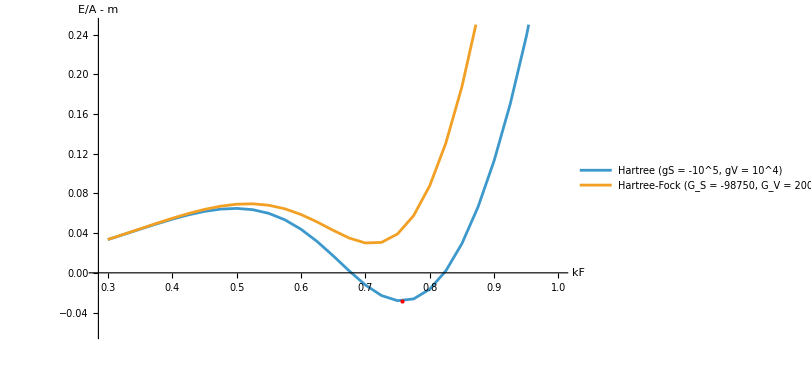

```mathematica
(* energy per particle E/A - m in units of m, Hartree (saturating) and Hartree-Fock *)
eAcurve[g_, gv_] := Table[N[{kF, eps7[g, gv, kF]/rho7[kF] - 1}], {kF, 3/10, 1, 1/40}];
ListLinePlot[{eAcurve[gS0, gV0], eAcurve[GS1, GV1]},
 PlotLegends -> {"Hartree (gS = -10^5, gV = 10^4)", "Hartree-Fock (G_S = -98750, G_V = 20000)"}, AxesLabel -> {"kF", "E/A - m"},
 Epilog -> {Red, PointSize[Medium], Point[{N[kF0], N[eps0/rho0 - 1]}]}, PlotRange -> {-0.06, 0.25}, ImageSize -> 600, GridLines -> {None, {0}}]
```

## 9. The chiral Kohn–Sham theory (8 + 8 components)

### 9.1 Chiral densities

With the chiral components ϕ_kL = EL†.ϕ_k and ϕ_kR = ER†.ϕ_k of the KS orbitals (section 7.10) the 18 densities become one complex scalar density and two 8-currents:

κ = Σ_k ϕ_kL† ϕ_kR,      j_L^A = Σ_k ϕ_kL† σbar^A ϕ_kL,      j_R^A = Σ_k ϕ_kR† σ^A ϕ_kR,

ρS = κ + κ* = 2 Re κ,   ρP = i (κ − κ*) = −2 Im κ,   j^A = j_L^A + j_R^A,   j5^A = j_R^A − j_L^A,

with σ^A = (ID8, σW[i]) and σbar^A = (ID8, −σW[i]) as in section 7.11. The scalar and pseudoscalar densities pair the two chiralities; the currents do not. The sources become a complex scalar source ϖ = s + i p and two chiral vector sources: s ρS + p ρP = ϖ κ + ϖ* κ*,   v_A j^A + a_A j5^A = (v − a)_A j_L^A + (v + a)_A j_R^A.

```mathematica
orbLV = Array[orbL, 8]; orbLcV = Array[orbLc, 8]; orbRV = Array[orbR, 8]; orbRcV = Array[orbRc, 8];   (* phi_L, phi_L^*, phi_R, phi_R^* *)
psiChi = EL.orbLV + ER.orbRV; psiChiDag = orbLcV.ConjugateTranspose[EL] + orbRcV.ConjugateTranspose[ER];
densChi[M_] := Expand[psiChiDag.M.psiChi];
κc = Expand[orbLcV.orbRV]; κcc = Expand[orbRcV.orbLV];                                   (* kappa and kappa^* *)
σUp = Join[{ID8}, Table[σW[i], {i, 1, 7}]]; σbarUp = Join[{ID8}, Table[-σW[i], {i, 1, 7}]];
jLc = Table[Expand[orbLcV.σbarUp[[A + 1]].orbLV], {A, 0, 7}]; jRc = Table[Expand[orbRcV.σUp[[A + 1]].orbRV], {A, 0, 7}];
check["chiral densities: ρS == κ + κ^*, ρP == I(κ - κ^*), j^A == jL^A + jR^A, j5^A == jR^A - jL^A (symbolic chiral orbitals)",
  Expand[densChi[Γ17[0]] - κc - κcc] === 0 && Expand[densChi[Γ17[0].(I χ17)] - I (κc - κcc)] === 0 &&
  And @@ Table[Expand[densChi[Γ17[0].Γ17up[A]] - jLc[[A + 1]] - jRc[[A + 1]]] === 0 &&
    Expand[densChi[Γ17[0].Γ17up[A].χ17] - jRc[[A + 1]] + jLc[[A + 1]]] === 0, {A, 0, 7}]]
check["the chiral blocks behind these densities: EL^†.βD.ER == ID8, EL^†.βD.EL == 0, EL^†.αD[i].EL == -σW[i], ER^†.αD[i].ER == σW[i], EL^†.αD[i].ER == 0",
  ConjugateTranspose[EL].βD.ER == ID8 && ConjugateTranspose[EL].βD.EL == Zero8 &&
  And @@ Table[ConjugateTranspose[EL].αD[i].EL == -σW[i] && ConjugateTranspose[ER].αD[i].ER == σW[i] && ConjugateTranspose[EL].αD[i].ER == Zero8, {i, 1, 7}]]
```

chiral densities: ρS == κ + κ^*, ρP == I(κ - κ^*), j^A == jL^A + jR^A, j5^A == jR^A - jL^A (symbolic chiral orbitals)→True

the chiral blocks behind these densities: EL^†.βD.ER == ID8, EL^†.βD.EL == 0, EL^†.αD[i].EL == -σW[i], ER^†.αD[i].ER == σW[i], EL^†.αD[i].ER == 0→True

### 9.2 The Hartree energy in chiral variables

In chiral variables the Hartree energy density is

e_H = (gS/2)(κ + κ*).b2 − (gP/2)(κ − κ*).b2 + ((gV + gA)/2)(j_L^A j_LA + j_R^A j_RA) + (gV − gA) j_L^A j_RA

= ((gS − gP)/2)(κ.b2 + κ*.b2) + (gS + gP) κ κ* + … .

The scalar–pseudoscalar part depends on κ only through |κ|.b2 exactly when gP = gS; then it is 2 gS |κ|.b2, the Nambu–Jona-Lasinio form. The vector–axial part couples the two currents only through gV − gA.

```mathematica
EHchiAbs[k_, kc_, jl_List, jr_List] := gS/2 (k + kc)^2 - gP/2 (k - kc)^2 +
   (gV + gA)/2 Sum[η17[[A + 1, A + 1]] (jl[[A + 1]]^2 + jr[[A + 1]]^2), {A, 0, 7}] + (gV - gA) Sum[η17[[A + 1, A + 1]] jl[[A + 1]] jr[[A + 1]], {A, 0, 7}];
EHchi = Expand[EHchiAbs[κc, κcc, jLc, jRc]];
check["E_H (16-component form, chiral orbitals) == gS/2 (κ + κ^*)^2 - gP/2 (κ - κ^*)^2 + (gV + gA)/2 (jL.jL + jR.jR) + (gV - gA) jL.jR",
  Expand[EHfun[densChi] - EHchi] === 0]
```

E_H (16-component form, chiral orbitals) == gS/2 (κ + κ^*)^2 - gP/2 (κ - κ^*)^2 + (gV + gA)/2 (jL.jL + jR.jR) + (gV - gA) jL.jR→True

### 9.3 The chiral Kohn–Sham equations

In chiral components the Kohn–Sham equation h_KS ϕ = ϵ ϕ becomes the 8 + 8 block system (W†.h_KS.W):

[V^L_0 − σW[i] (−i ∂_i + V^L_i)] ϕL + M ϕR = ϵ ϕL,

M* ϕL + [V^R_0 + σW[i] (−i ∂_i + V^R_i)] ϕR = ϵ ϕR,

with the complex Kohn–Sham mass M = m + S + i P and the chiral vector potentials V^L_A = V_A − A_A, V^R_A = V_A + A_A. Since σW[i](−i∂_i) = τO[i] ∂_i, the derivative terms contain only the real τO[i], exactly as in section 7.11; the mass M couples the two chiralities. The potentials are Wirtinger derivatives of the energy:

M − m = ϖ + ∂(E_H + E_xc)/∂κ,   V^L_A = (v − a)_A + ∂(E_H + E_xc)/∂j_L^A,   V^R_A = (v + a)_A + ∂(E_H + E_xc)/∂j_R^A;

Hartree:   M − m − ϖ = gS (κ + κ*) − gP (κ − κ*) = gS ρS + i gP ρP,   V^L_A − (v − a)_A = (gV + gA) j_LA + (gV − gA) j_RA,   V^R_A − (v + a)_A = (gV + gA) j_RA + (gV − gA) j_LA.

The densities κ, j_L, j_R are computed from the occupied chiral orbitals (no sea, as in section 8.4), and the total energy is

E = Σ_k ϵ_k − ∫ [ 2 Re((M − m − ϖ) κ) + (V^L − v + a)_A j_L^A + (V^R − v − a)_A j_R^A ] d⁷x + E_H + E_xc.

```mathematica
VLks = VKS - AKS; VRks = VKS + AKS; Mks = mD + Sks + I Pks;
hChiKS[q_List] := ArrayFlatten[{{VLks[[1]] ID8 - Sum[σW[i] (q[[i]] + VLks[[i + 1]]), {i, 1, 7}], Mks ID8},
    {(mD + Sks - I Pks) ID8, VRks[[1]] ID8 + Sum[σW[i] (q[[i]] + VRks[[i + 1]]), {i, 1, 7}]}}];
check["chiral KS Hamiltonian: W^†.h_KS(p).W == {{V^L_0 - σW.(p + V^L), M}, {M^*, V^R_0 + σW.(p + V^R)}}, M = m + S + I P, V^L = V - A, V^R = V + A",
  Expand[ConjugateTranspose[Wch].hKS[pv7].Wch - hChiKS[pv7]] === Zero16]
VLc = Table[(gV + gA) η17[[A + 1, A + 1]] jLc[[A + 1]] + (gV - gA) η17[[A + 1, A + 1]] jRc[[A + 1]], {A, 0, 7}];   (* V^L_A, lower index *)
VRc = Table[(gV + gA) η17[[A + 1, A + 1]] jRc[[A + 1]] + (gV - gA) η17[[A + 1, A + 1]] jLc[[A + 1]], {A, 0, 7}];
dEHdk = gS (κc + κcc) - gP (κc - κcc); dEHdkc = gS (κc + κcc) + gP (κc - κcc);
check["Hartree (Wirtinger): M - m == ∂e_H/∂κ == gS ρS + I gP ρP, V^L_A == ∂e_H/∂jL^A; V^L_A == V_A - A_A and V^R_A == V_A + A_A with V_A = gV j_A, A_A = gA j5_A",
  With[{jlA = Array[jl, 8, 0], jrA = Array[jr, 8, 0]},
    Expand[D[EHchiAbs[kk, kkc, jlA, jrA], kk] - (gS (kk + kkc) - gP (kk - kkc))] === 0 &&
    And @@ Table[Expand[D[EHchiAbs[kk, kkc, jlA, jrA], jl[A]] - ((gV + gA) η17[[A + 1, A + 1]] jl[A] + (gV - gA) η17[[A + 1, A + 1]] jr[A])] === 0, {A, 0, 7}]] &&
  Expand[dEHdk - (gS densChi[Γ17[0]] + I gP densChi[Γ17[0].(I χ17)])] === 0 &&
  And @@ Table[Expand[VLc[[A + 1]] - (gV η17[[A + 1, A + 1]] densChi[Γ17[0].Γ17up[A]] - gA η17[[A + 1, A + 1]] densChi[Γ17[0].Γ17up[A].χ17])] === 0 &&
    Expand[VRc[[A + 1]] - (gV η17[[A + 1, A + 1]] densChi[Γ17[0].Γ17up[A]] + gA η17[[A + 1, A + 1]] densChi[Γ17[0].Γ17up[A].χ17])] === 0, {A, 0, 7}]]
check["chiral KS potentials are derivatives: ∂E_H/∂ϕL^* == (V^L_0 - σW[i] V^L_i) ϕL + (M - m) ϕR and ∂E_H/∂ϕR^* == (V^R_0 + σW[i] V^R_i) ϕR + (M - m)^* ϕL",
  And @@ Table[Expand[D[EHchi, orbLc[a]] - (Sum[VLc[[A + 1]] σbarUp[[A + 1]], {A, 0, 7}].orbLV + dEHdk orbRV)[[a]]] === 0 &&
    Expand[D[EHchi, orbRc[a]] - (Sum[VRc[[A + 1]] σUp[[A + 1]], {A, 0, 7}].orbRV + dEHdkc orbLV)[[a]]] === 0, {a, 1, 8}]]
```

chiral KS Hamiltonian: W^†.h_KS(p).W == {{V^L_0 - σW.(p + V^L), M}, {M^*, V^R_0 + σW.(p + V^R)}}, M = m + S + I P, V^L = V - A, V^R = V + A→True

Hartree (Wirtinger): M - m == ∂e_H/∂κ == gS ρS + I gP ρP, V^L_A == ∂e_H/∂jL^A; V^L_A == V_A - A_A and V^R_A == V_A + A_A with V_A = gV j_A, A_A = gA j5_A→True

chiral KS potentials are derivatives: ∂E_H/∂ϕL^* == (V^L_0 - σW[i] V^L_i) ϕL + (M - m) ϕR and ∂E_H/∂ϕR^* == (V^R_0 + σW[i] V^R_i) ϕR + (M - m)^* ϕL→True

### 9.4 Chiral symmetry

Because χ17 = i ω17, the chiral transformation ψ → e^{iθχ17} ψ = (cos θ ID16 − sin θ ω17) ψ is a REAL rotation of the 16 components. It acts as ϕL → e^{−iθ} ϕL, ϕR → e^{iθ} ϕR and κ → e^{2iθ} κ; the currents j_L and j_R (hence j and j5) are invariant, while (ρS, ρP) rotate by the angle 2θ. Therefore

E_H(e^{iθχ17} ψ) − E_H(ψ) = ((gS − gP)/2) [ (e^{4iθ} − 1) κ.b2 + (e^{−4iθ} − 1) κ*.b2 ]:

the interaction is chirally (U(1)_A) symmetric if and only if gP = gS. The mass term m(κ + κ*) in T_s breaks the symmetry explicitly. For m = 0, gP = gS and ϖ = 0 the whole chiral KS theory is invariant: with κ = 0 the chiral KS equations decouple into separate 8-component equations for ϕL and ϕR, while a self-consistent solution with κ ≠ 0 breaks the symmetry spontaneously (section 9.6). The check uses cos θ = 3/5, sin θ = 4/5.

```mathematica
Uθ = 3/5 ID16 + I 4/5 χ17; e2θ = (3/5 + 4/5 I)^2;
check["e^(Iθχ17) == cosθ ID16 - sinθ ω17 is REAL and orthogonal; U.EL == e^(-Iθ) EL, U.ER == e^(Iθ) ER",
  Uθ == 3/5 ID16 - 4/5 ω17 && FreeQ[Uθ, Complex] && Transpose[Uθ].Uθ == ID16 &&
  Uθ.EL == (3/5 - 4/5 I) EL && Uθ.ER == (3/5 + 4/5 I) ER]
check["U^†.βD.U == βD.(cos 2θ ID16 + I sin 2θ χ17); vector and axial densities invariant",
  ConjugateTranspose[Uθ].βD.Uθ == βD.(Re[e2θ] ID16 + I Im[e2θ] χ17) &&
  And @@ Table[ConjugateTranspose[Uθ].Γ17[0].Γ17up[A].Uθ == Γ17[0].Γ17up[A] &&
    ConjugateTranspose[Uθ].Γ17[0].Γ17up[A].χ17.Uθ == Γ17[0].Γ17up[A].χ17, {A, 0, 7}]]
EHrot = Expand[EHfun[dens16[ConjugateTranspose[Uθ].#.Uθ] &]];
κ16 = dens16[EL.ConjugateTranspose[ER]]; κ16c = dens16[ER.ConjugateTranspose[EL]];
check["E_H(e^(Iθχ17) ψ) - E_H(ψ) == (gS - gP)/2 [(e^(4Iθ) - 1) κ^2 + (e^(-4Iθ) - 1) κ^*2]: U(1)_A symmetric iff gP == gS",
  Expand[EHrot - EH16 - (gS - gP)/2 ((e2θ^2 - 1) κ16^2 + (Conjugate[e2θ]^2 - 1) κ16c^2)] === 0 &&
  Expand[(EHrot - EH16) /. gP -> gS] === 0 && Expand[EHrot - EH16] =!= 0]
```

e^(Iθχ17) == cosθ ID16 - sinθ ω17 is REAL and orthogonal; U.EL == e^(-Iθ) EL, U.ER == e^(Iθ) ER→True

U^†.βD.U == βD.(cos 2θ ID16 + I sin 2θ χ17); vector and axial densities invariant→True

E_H(e^(Iθχ17) ψ) - E_H(ψ) == (gS - gP)/2 [(e^(4Iθ) - 1) κ^2 + (e^(-4Iθ) - 1) κ^*2]: U(1)_A symmetric iff gP == gS→True

### 9.5 Uniform matter in chiral form

For the uniform matter of section 8.7 the chiral densities are κ = ρS/2 (real), j_L^0 = j_R^0 = ρ/2 and j_L^i = j_R^i = 0; the chiral KS potentials are M = m* (real) and V^L_0 = V^R_0 = V_0. The chiral KS Hamiltonian {{V_0 − σW·p⃗, m*}, {m*, V_0 + σW·p⃗}} has the eigenvalues V_0 ± √(p⃗.b2 + m*.b2), each eight times — the spectrum of the 16-component form, as it must be.

```mathematica
kappaUni = Tr[EL.ConjugateTranspose[ER].Runi.Γ17[0]];          (* kappa = tr(EL.ER^dagger.sum psi psi^dagger), sum psi psi^dagger = R.Gamma17[0] *)
jLUni = Table[Tr[EL.σbarUp[[A + 1]].ConjugateTranspose[EL].Runi.Γ17[0]], {A, 0, 7}];
jRUni = Table[Tr[ER.σUp[[A + 1]].ConjugateTranspose[ER].Runi.Γ17[0]], {A, 0, 7}];
check["uniform matter in chiral form: κ == ρS/2, jL^0 == jR^0 == ρ/2, jL^i == jR^i == 0",
  Expand[kappaUni - ρSsym/2] === 0 && Expand[jLUni - Join[{ρsym/2}, ConstantArray[0, 7]]] === ConstantArray[0, 8] &&
  Expand[jRUni - Join[{ρsym/2}, ConstantArray[0, 7]]] === ConstantArray[0, 8]]
hChiUni = ArrayFlatten[{{V0s ID8 - σWp[pv7], mst ID8}, {mst ID8, V0s ID8 + σWp[pv7]}}];
check["(h_χ - V_0)^2 == (p^2 + m*^2) ID16: eigenvalues V_0 ± Sqrt[p^2 + m*^2], eight times each",
  Expand[(hChiUni - V0s ID16).(hChiUni - V0s ID16) - (pv7.pv7 + mst^2) ID16] === Zero16 && Tr[hChiUni - V0s ID16] === 0]
chiralUniform = {"kappa = rhoS/2" -> N[rhoS0/2, 20], "jL^0 = jR^0 = rho/2" -> N[rho0/2, 20], "M = m*" -> N[ms0, 20], "V^L_0 = V^R_0 = V0" -> N[V00, 20]}
```

uniform matter in chiral form: κ == ρS/2, jL^0 == jR^0 == ρ/2, jL^i == jR^i == 0→True

(h_χ - V_0)^2 == (p^2 + m*^2) ID16: eigenvalues V_0 ± Sqrt[p^2 + m*^2], eight times each→True

{kappa = rhoS/2→3.2595132992687836743×10^-6,jL^0 = jR^0 = rho/2→6.9405010661584385987×10^-6,M = m*→0.34809734014624326514,V^L_0 = V^R_0 = V0→0.13881002132316877197}

### 9.6 The chiral vacuum with the Dirac sea: spontaneous chiral symmetry breaking

Now keep the Dirac sea — all negative-energy KS orbitals occupied, with a momentum cutoff |p⃗| < Λ — and take gP = gS = g, ϖ = 0, V = A = 0 and no matter (the vacuum). With a uniform complex KS mass M the chiral KS Hamiltonian h_χ(p⃗) = {{−σW·p⃗, M ID8}, {M* ID8, σW·p⃗}} (plus m on the off-diagonal blocks when m ≠ 0, absorbed in M) satisfies h_χ.b2 = (p⃗.b2 + |M|.b2) ID16. Its eigenvalues are ±E, E = √(p⃗.b2 + |M|.b2), and the projector on the filled sea is Π−(p⃗) = (ID16 − h_χ(p⃗)/E)/2, whose RL block is −M*/(2E) ID8. Hence

κ = −4 M* J(|M|),   J(M) = ∫_{|p⃗|<Λ} d⁷p/(2π)⁷ 1/√(p.b2 + M.b2) = (1/(120 π⁴)) ∫_0^Λ p⁶/√(p.b2 + M.b2) dp

(the angular integral gives |S⁶|/(2π)⁷ = 1/(120 π⁴)). The Hartree KS mass M = m + 2g κ* gives the gap equation

M = m − 8 g J(|M|) M.

For m = 0 a solution M ≠ 0 exists if and only if 1 + 8 g J(|M|) = 0 has a root, i.e. iff g < g_c = −1/(8 J(0)) = −90 π⁴/Λ⁶. The vacuum energy density of the KS state (sum of the sea eigenvalues minus double counting) is

E(M) = −8 K(|M|) + 8 J(|M|) Re[(M − m) M*] + 32 g |M|.b2 J(|M|).b2,   K(M) = (1/(120 π⁴)) ∫_0^Λ p⁶ √(p.b2 + M.b2) dp,

and its stationarity condition is the gap equation (for m = 0: dE/d|M| = 8|M| (1 + 8gJ)(J + |M| J′)). For m = 0, E depends only on |M|: the broken vacua M = |M| e^{iϕ} are degenerate and related by chiral rotations; the phase ϕ is the Goldstone direction. A small explicit mass m > 0 selects the real positive M. Example: Λ = 1, g = (6/5) g_c; for m > 0, m = 1/100.

```mathematica
Λc = 1;
Jsea[M_] = Integrate[q^6/Sqrt[q^2 + M^2], {q, 0, Λc}, Assumptions -> M > 0]/(120 Pi^4);
Ksea[M_] = Integrate[q^6 Sqrt[q^2 + M^2], {q, 0, Λc}, Assumptions -> M > 0]/(120 Pi^4);
J0sea = Integrate[q^5, {q, 0, Λc}]/(120 Pi^4); K0sea = Integrate[q^7, {q, 0, Λc}]/(120 Pi^4);
gcrit = -1/(8 J0sea);
check["|S^6|/(2 Pi)^7 == 1/(120 Pi^4); J(0) == Λ^6/(720 Pi^4); g_c == -1/(8 J(0)) == -90 Pi^4/Λ^6; J(M) -> J(0) and K(M) -> K(0) as M -> 0",
  (16 Pi^3/15)/(2 Pi)^7 == 1/(120 Pi^4) && J0sea == 1/(720 Pi^4) && gcrit == -90 Pi^4 &&
  Limit[Jsea[M], M -> 0, Direction -> "FromAbove"] == J0sea && Limit[Ksea[M], M -> 0, Direction -> "FromAbove"] == K0sea]
Esea[Mz_, mq_, g_] := -8 Ksea[Abs[Mz]] + 8 Jsea[Abs[Mz]] Re[(Mz - mq) Conjugate[Mz]] + 32 g Abs[Mz]^2 Jsea[Abs[Mz]]^2;
E0sea = -8 K0sea;                                              (* E(M = 0), m = 0 *)
gNJL = 6/5 gcrit;
gapNJL[M_?NumericQ, mq_] := With[{M1 = SetPrecision[M, 60]}, M1 - mq + 8 gNJL Jsea[M1] M1];     (* M - m + 8 g J(M) M, real M > 0 *)
M0NJL = SetPrecision[M /. FindRoot[gapNJL[M, 0]/M, {M, 1/10, 1}, Method -> "Brent", WorkingPrecision -> 40, AccuracyGoal -> 32, PrecisionGoal -> 32], 60];
check["m = 0, g = 6/5 g_c: the gap equation 1 + 8 g J(|M|) == 0 has the root |M| (32 digits); M == 2 g κ^* with κ == -4 M J; E is stationary there and lower than E(0)",
  Abs[1 + 8 gNJL Jsea[M0NJL]] < 10^-25 && Abs[M0NJL - 2 gNJL (-4 M0NJL Jsea[M0NJL])] < 10^-25 &&
  Abs[D[-8 Ksea[M] + 8 Jsea[M] M^2 + 32 gNJL M^2 Jsea[M]^2, M] /. M -> M0NJL] < 10^-25 && Esea[M0NJL, 0, gNJL] < E0sea]
check["degenerate chiral vacua for m = 0: E(|M| e^(I φ)) == E(|M|) for φ = 1, 2, 4 (the phase is the Goldstone direction)",
  And @@ Table[Abs[Esea[M0NJL Exp[I phi], 0, gNJL] - Esea[M0NJL, 0, gNJL]] < 10^-25, {phi, {1, 2, 4}}]]
mq0 = 1/100;
MmNJL = SetPrecision[M /. FindRoot[gapNJL[M, mq0], {M, 1/10, 1}, Method -> "Brent", WorkingPrecision -> 40, AccuracyGoal -> 32, PrecisionGoal -> 32], 60];
check["explicit breaking m = 1/100: the real M == m - 8 g J(M) M solves the gap equation, E is stationary there, and every complex phase raises E",
  Abs[MmNJL - mq0 + 8 gNJL Jsea[MmNJL] MmNJL] < 10^-25 && Abs[D[-8 Ksea[M] + 8 Jsea[M] (M^2 - mq0 M) + 32 gNJL M^2 Jsea[M]^2, M] /. M -> MmNJL] < 10^-25 &&
  And @@ Table[Esea[MmNJL Exp[I phi], mq0, gNJL] > Esea[MmNJL, mq0, gNJL], {phi, {1/50, 1/2, 1, 3}}]]
njlVacuum = {"g_c" -> N[gcrit, 20], "g" -> N[gNJL, 20], "|M| (m = 0)" -> N[M0NJL, 20], "kappa (m = 0, M real)" -> N[-4 M0NJL Jsea[M0NJL], 20],
  "E(M) - E(0)" -> N[Esea[M0NJL, 0, gNJL] - E0sea, 20], "M (m = 1/100)" -> N[MmNJL, 20]}
```

|S^6|/(2 Pi)^7 == 1/(120 Pi^4); J(0) == Λ^6/(720 Pi^4); g_c == -1/(8 J(0)) == -90 Pi^4/Λ^6; J(M) -> J(0) and K(M) -> K(0) as M -> 0→True

m = 0, g = 6/5 g_c: the gap equation 1 + 8 g J(|M|) == 0 has the root |M| (32 digits); M == 2 g κ^* with κ == -4 M J; E is stationary there and lower than E(0)→True

degenerate chiral vacua for m = 0: E(|M| e^(I φ)) == E(|M|) for φ = 1, 2, 4 (the phase is the Goldstone direction)→True

explicit breaking m = 1/100: the real M == m - 8 g J(M) M solves the gap equation, E is stationary there, and every complex phase raises E→True

{g_c→-8766.8181930602193513,g→-10520.181831672263222,|M| (m = 0)→0.55369385182924169122,kappa (m = 0, M real)→-0.0000263157928583648742,E(M) - E(0)→-1.3102449629010022473×10^-6,M (m = 1/100)→0.58531284674622051123}

the sea at one momentum: h_χ^2 == E^2 ID16; Π_- is a projector of rank 8; κ_p == tr(Π_- RL block) == -4 M^*/E; tr(Π_-.h0) == -8E + 8 Re[(M - m) M^*]/E→True

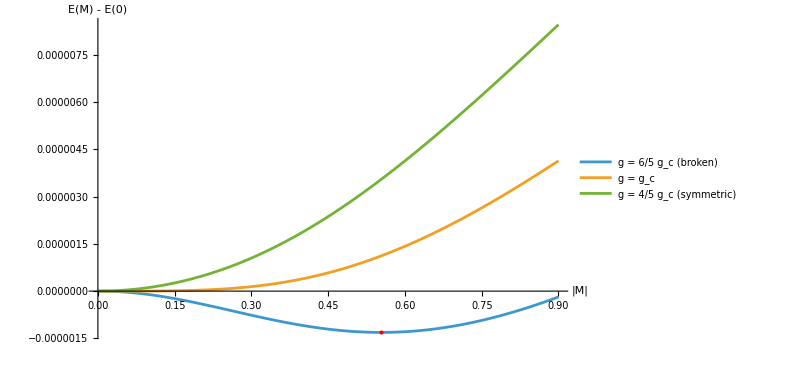

```mathematica
(* the filled sea at one momentum, with a complex M: an explicit check of kappa_p and of the sea energy *)
pS = {3/10, -1/5, 1/10, 1/4, 0, -3/20, 1/20}; Mz7 = M0NJL Exp[7 I/10];
hChiSea = ArrayFlatten[{{-σWp[pS], Mz7 ID8}, {Conjugate[Mz7] ID8, σWp[pS]}}];
Esp = Sqrt[pS.pS + Abs[Mz7]^2]; PiMinus = (ID16 - hChiSea/Esp)/2;
h0Chi = ArrayFlatten[{{-σWp[pS], Zero8}, {Zero8, σWp[pS]}}];       (* m = 0 *)
check["the sea at one momentum: h_χ^2 == E^2 ID16; Π_- is a projector of rank 8; κ_p == tr(Π_- RL block) == -4 M^*/E; tr(Π_-.h0) == -8E + 8 Re[(M - m) M^*]/E",
  Max[Abs[hChiSea.hChiSea - Esp^2 ID16]] < 10^-20 && Max[Abs[PiMinus.PiMinus - PiMinus]] < 10^-20 && Abs[Tr[PiMinus] - 8] < 10^-20 &&
  Abs[Tr[PiMinus[[9 ;; 16, 1 ;; 8]]] + 4 Conjugate[Mz7]/Esp] < 10^-20 && Abs[Tr[PiMinus.h0Chi] - (-8 Esp + 8 Abs[Mz7]^2/Esp)] < 10^-20]
Plot[{Esea[Mx, 0, gNJL] - E0sea, Esea[Mx, 0, gcrit] - E0sea, Esea[Mx, 0, 4/5 gcrit] - E0sea}, {Mx, 0.001, 0.9},
 PlotLegends -> {"g = 6/5 g_c (broken)", "g = g_c", "g = 4/5 g_c (symmetric)"}, AxesLabel -> {"|M|", "E(M) - E(0)"},
 Epilog -> {Red, PointSize[Medium], Point[{N[M0NJL], N[Esea[M0NJL, 0, gNJL] - E0sea]}]}, ImageSize -> 600]
```

## 10. Summary of all checks (sections 1–9)

The four cells below repeat the summary of section 6 after sections 7–9 have been evaluated, so they cover every check of the notebook.

```mathematica
Length[checks]
```

203

```mathematica
failedChecks = Keys[Select[checks, ! TrueQ[#] &]]
```

{}

```mathematica
allChecksPassed = AllTrue[Values[checks], TrueQ]
```

True

```mathematica
Grid[Prepend[KeyValueMap[{#1, #2} &, checks], {Style["check", Bold], Style["result", Bold]}], Frame -> All, Alignment -> Left]
```

check | result
4+4: ζ[7] == diag(-1,-1,-1,-1,1,1,1,1) | True
4+4: σ == ζ[1].ζ[2].ζ[3] | True
4+4: (ζ[A].ζ[B] + ζ[B].ζ[A])/2 == -η4488[[A+1,B+1]] ID8 (A,B = 1..7) | True
4+4: -η4488[[A+1,A+1]] ζ[A] == Transpose[ζ[A]] (A = 1..7) | True
4+4: (τ[A].τbar[B] + τ[B].τbar[A])/2 == η4488[[A+1,B+1]] ID8 | True
4+4: (τbar[A].τ[B] + τbar[B].τ[A])/2 == η4488[[A+1,B+1]] ID8 | True
4+4: τ[1].τ[2]...τ[7] == ID8 | True
4+4: σ == τ[1].τ[2].τ[3] == τ[4].τ[5].τ[6].τ[7] | True
4+4: σ commutes with τ[1..3] and anticommutes with τ[4..7]; σ.σ == ID8 | True
4+4: (T16[A].T16[B] + T16[B].T16[A])/2 == η4488[[A+1,B+1]] ID16 | True
4+4: T16[A] real (entries 0, ±1) | True
4+4: T16[8] == diag(-ID8, ID8) | True
4+4: σ16 == diag(-σ, σ) | True
4+4: PL44 + PR44 == ID16, PL44.PL44 == PL44, PR44.PR44 == PR44, PL44.PR44 == 0 | True
4+4: uBasis == evecs/Sqrt[2] from Eigensystem[σ] (the basis of 4+4.nb) | True
4+4: unit == (1,0,0,0,1,0,0,0)/Sqrt[2], σ.unit == unit, unit.unit == 1, unit.σ.unit == 1 | True
4+4 (In[294]): E44inv[h] == (u.σ.u) Transpose[Table[η4488[[B,B]] τ[B-1].u, {B,1,8}]] for h = 1..8 | True
4+4: gridx44 is identical to the split-octonion table printed by 4+4.nb | True
4+4: LS[A] are signed permutation matrices (constants 0, ±1) | True
split: eA[1] is the identity; eA[2..4]^2 == -eA[1]; eA[5..8]^2 == +eA[1] | True
split: x x̄ == N(x) eA[1] with N = η4488 (symbolic) | True
split: N(xy) == N(x) N(y) (symbolic) | True
split: alternative x(xy) == (xx)y and (yx)x == y(xx) (symbolic) | True
split: (eA[1] + eA[5])(eA[1] - eA[5]) == 0 with both factors nonzero: NOT a division algebra | True
τO[A] (A = 1..7): real, antisymmetric, τO[A].τO[A] == -ID8 | True
τO[A] anticommute: τO[A].τO[B] == -τO[B].τO[A] (A != B, A,B = 1..7) | True
mirror of 4+4: (τO[A].τObar[B] + τO[B].τObar[A])/2 == gO[[A+1,B+1]] ID8 | True
mirror of 4+4: (τObar[A].τO[B] + τObar[B].τO[A])/2 == gO[[A+1,B+1]] ID8 | True
mirror of 4+4: τO[1].τO[2]...τO[7] == ID8 | True
mirror of 4+4: τObar[A] == gO.Transpose[τO[A]].gO, as τbar[A] == σ.Transpose[τ[A]].σ | True
τO[4..7] are products of three split τ: τO[4] == τ[5].τ[6].τ[7], τO[5] == -τ[4].τ[6].τ[7], τO[6] == τ[4].τ[5].τ[7], τO[7] == -τ[4].τ[5].τ[6] | True
σ.unit == unit, hence τO[A].unit == τ[A].unit (A = 0..7) | True
EO is orthogonal: EOinv == Transpose[EO] | True
mirror of 4+4.nb In[294]: EOinv == (u.gO.u) Transpose[Table[gO[[B,B]] τO[B-1].u, {B,1,8}]] | True
EO == η4488.E44[hUSE]: the two vielbeins differ only by the signs of rows 5..8 | True
gridO equals the octonion table computed independently in Python | True
LO[A] are signed permutation matrices (all multiplication constants are 0, ±1) | True
oMul reproduces gridO on all 64 pairs of basis units | True
e[0] is a two-sided identity | True
e[i] e[i] == -e[0] (i = 1..7) | True
e[i] e[j] == -e[j] e[i] (i != j, i,j = 1..7): non-commutative | True
7 Fano lines; every pair of distinct imaginary units lies on exactly one line | True
each oriented line (a,b,c) is cyclic: e[a]e[b] == e[c], e[b]e[c] == e[a], e[c]e[a] == e[b] | True
each line spans a quaternion subalgebra: {e[0], e[a], e[b], e[c]} closed and associative | True
the picture's 7 lines are exactly fanoLines | True
left alternative: x(xy) == (xx)y (symbolic) | True
right alternative: (yx)x == y(xx) (symbolic) | True
flexible: (xy)x == x(yx) (symbolic) | True
associator is alternating: [x,y,z] == -[y,x,z] == -[x,z,y] (symbolic) | True
power associativity: x(xx) == (xx)x (symbolic) | True
Moufang: z(x(zy)) == ((zx)z)y, x(z(yz)) == ((xz)y)z, (zx)(yz) == (z(xy))z (x, y basis units, z symbolic) | True
x x̄ == x̄ x == N(x) e[0] (symbolic) | True
conjugation is an anti-automorphism: conj(xy) == conj(y) conj(x) (symbolic) | True
Re(x) == (x + x̄)/2 == x0 | True
norm is multiplicative: N(xy) == N(x) N(y) (symbolic; Degen's eight-square identity) | True
inverse x^-1 = x̄/N(x): x x^-1 == x^-1 x == e[0] (symbolic) | True
every x satisfies x x - 2 Re(x) x + N(x) e[0] == 0, so the subalgebra generated by x is ℝ or ℂ | True
exactly 168 of the 512 ordered basis triples are non-associative (= 7*6*4: distinct imaginary units not on one Fano line) | True
example: (e[1]e[2])e[4] == e[7] but e[1](e[2]e[4]) == -e[7] | True
numerical example: N(x y) == N(x) N(y) == 15*6 == 90 and x x^-1 == e[0] | True
numerical example: x y != y x and (x y) z != x (y z) | True
ℍ = span{e[0],e[1],e[2],e[3]} is a subalgebra | True
ℓ = e[4] doubles ℍ: e[4] e[k] == e[4+k] (k = 1,2,3) and e[4] e[4] == -e[0] | True
orientation inherited from 4+4.nb: e[1] e[2] == -e[3] | True
Cayley-Dickson, γ = -1: (ac - d b̄, ā d + c b) reproduces the octonion product (symbolic) | True
Cayley-Dickson, γ = +1: (ac + d b̄, ā d + c b) reproduces the SPLIT product of 4+4.nb (symbolic) | True
the formula (ac - d̄ b, ā d + c b) of [1A] is NOT alternative: x·x·y != x(xy) for x = e[0]+e[4], y = e[1] | True
... and its norm is not multiplicative (symbolic) | True
e[A]e[B] (octonion) == s_AB e[A]e[B] (split) for all A, B = 0..7 | True
over ℂ: φ(x *split y) == φ(x) *oct φ(y) (symbolic): split ⊗ ℂ ≅ 𝕆 ⊗ ℂ | True
the norms correspond: N_oct(φ(x)) == N_split(x) (symbolic) | True
Cl(8,0): (T16O[A].T16O[B] + T16O[B].T16O[A])/2 == gO[[A+1,B+1]] ID16 | True
S44 == diag(σ, σ) | True
T16O from the 4+4 matrices: T16O[A] == T16[A] (A = 0..3), T16O[k] == T16[k].S44 (k = 4..7) | True
T16O[8] == T16[8] == diag(-ID8, ID8): same chirality matrix and same PL44, PR44 as 4+4.nb | True
7+1 REAL Clifford relation: (Γ17[A].Γ17[B] + Γ17[B].Γ17[A])/2 == η17[[A+1,B+1]] ID16 == -η71[[A+1,B+1]] ID16 | True
Γ17[A] are REAL: every entry is 0 or ±1 | True
block form: Γ17[0] == {{0,ID8},{ID8,0}}, Γ17[i] == {{τO[i],0},{0,τObar[i]}} | True
built from the real 4+4 matrices: Γ17[0] == T16[0], Γ17[i] == T16[0].T16[i] (i = 1,2,3), Γ17[k] == T16[0].T16[k].S44 (k = 4..7) | True
Γ17[0] symmetric, Γ17[i] antisymmetric, so Transpose[Γ17[A]] == Γ17[0].Γ17[A].Γ17[0] (real Dirac adjoint) | True
the 256 products Γ17[A1]...Γ17[Ak] (A1 < ... < Ak) are linearly independent: Cl(1,7) ≅ ℝ(16) | True
grades: binomial(8,k) == {1,8,28,56,70,56,28,8,1}, total 256 (binomial(8,4) == 70, not 72) | True
Tr[product] == 0 for every non-empty product, so Tr[M]/16 is the scalar part of M | True
irreducible over ℝ: only multiples of ID16 commute with all Γ17[A] (Schur; real commutant of dimension 1) | True
universal property: Γ17(v).Γ17(v) == (v.η17.v) ID16 for a symbolic vector v = X | True
7+1 COMPLEX Clifford relation, 4+4.nb sign: (Γ71[A].Γ71[B] + Γ71[B].Γ71[A])/2 == η71[[A+1,B+1]] ID16 | True
Γ71[0] == I T16[0] and Γ71[k] == T16O[k] (k = 1..7): only the time component is complex | True
S = (ID16 - I Γ17[0])/Sqrt[2] is unitary and Γ71[A] == S.(I Γ17[A]).Inverse[S] | True
Schur: the intertwiners M with M.Conjugate[Γ71[A]] == Γ71[A].M form a 1-dimensional space | True
... spanned by the volume element Γ17[8] == {{0,-ID8},{ID8,0}}, and Γ17[8].Γ17[8] == -ID16 | True
indicator(Γ71) == -1: Cl(7,1) ≅ ℍ(8), NO real 16×16 realization of the η71 relation | True
indicator(Γ17) == +1: Cl(1,7) ≅ ℝ(16), real realization exists (Γ17) | True
REAL 32×32 realization of the η71 relation: (Γ71R32[A].Γ71R32[B] + Γ71R32[B].Γ71R32[A])/2 == η71[[A+1,B+1]] ID32 | True
Qi, Qj, Qk commute with every Γ71R32[A]; Qi.Qi == Qj.Qj == Qk.Qk == -ID32; Qi.Qj == Qk == -Qj.Qi | True
the commutant of {Γ71R32[A]} has dimension exactly 4 and is spanned by ID32, Qi, Qj, Qk: it is ℍ | True
Γ17[8].Γ17[8] == -ID16 and Γ17[8] anticommutes with every Γ17[A]: no real chirality in 7+1 | True
Γ71[8].Γ71[8] == -ID16 and χ71 = -I Γ71[8] == T16O[8] == T16[8] (real, diagonal) | True
7+1 chiral projectors in the Γ71 basis are exactly PL44, PR44 of 4+4.nb; χ71 anticommutes with every Γ71[A] | True
complex chiral projectors for Γ17: PL17 + PR17 == ID16, PL17.PL17 == PL17, PL17.PR17 == 0, rank 8 each | True
η17 is simply the squares of the octonion basis: e[A] e[A] == η17[[A+1, A+1]] e[0] (e[0]^2 = +1, e[i]^2 = -1) and Re(e[A] e[B]) == η17[[A+1, B+1]] (A, B = 0..7) | True
Re(x x) == X.η17.X: the octonion square produces the 7+1 interval (symbolic) | True
octonion basis: Γ17e[0] == {{0,ID8},{ID8,0}} and Γ17e[i] == {{LO[i],0},{0,-LO[i]}} | True
alternativity in action: xImag(xImag ψ) == -|xImag|^2 ψ for the imaginary part xImag of x (symbolic) | True
T16O(x)^2 == N(x) ID16 (octonion norm) and T16(x)^2 == (X.η4488.X) ID16 (4+4.nb) | True
28 real generators Σ17[A,B] (A < B), linearly independent | True
[Σ17[A,B], Γ17[K]] == η17[[B+1,K+1]] Γ17[A] - η17[[A+1,K+1]] Γ17[B] | True
so(1,7): [Σ_AB, Σ_KL] == η_BK Σ_AL - η_AK Σ_BL - η_BL Σ_AK + η_AL Σ_BK | True
the complex structure J = Γ17[8] commutes with all Σ17[A,B] (Spin(1,7) acts complex-linearly on ℝ^16 = ℂ^8) | True
S(β) and R(θ) are the exponentials: dS/dβ == Σ17[0,1].S, S(0) == ID16, dR/dθ == Σ17[4,5].R, R(0) == ID16, and S.Sinv == R.Rinv == ID16 | True
S(β).Γ17[K].S(β)^-1 == ∑_B Λboost[[B+1,K+1]] Γ17[B]; Λboost is the boost along x1 | True
R(θ).Γ17[K].R(θ)^-1 == ∑_B Λrot[[B+1,K+1]] Γ17[B]; Λrot is the rotation in the x4-x5 plane | True
both Λ preserve the 7+1 metric: Transpose[Λ].η17.Λ == η17 | True
(Γ17^A ∂_A)^2 Ψ == (∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 16 arbitrary functions of x0..x7 | True
p is on the mass shell (p.η17.p == m^2) and pslash.pslash == m^2 ID16 | True
(pslash - m) w == 0 has 8 linearly independent REAL solutions w | True
Ψ = w Exp[-I p.x] solves (I Γ17^A ∂_A - m) Ψ == 0 | True
the matrices anticommuting with every Γ17[A] are exactly the multiples of Γ17[8], and (c Γ17[8])^2 == -c^2 ID16: no real J with J.J == +ID16 | True
null momentum k = (1,1,0,0,0,0,0,0): k.η17.k == 0, kslash.kslash == 0, and kslash.w == 0 has 8 REAL solutions | True
Ψ = w Cos[k.x] is a REAL solution of the real massless Dirac equation Γ17^A ∂_A Ψ == 0 | True
(Γ71R32^A ∂_A)^2 Ψ == -(∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 32 arbitrary functions of x0..x7 | True
p.η71.p == -m^2 and pslash32.pslash32 == -m^2 ID32 | True
Ψ = w Cos[p.x] + (pslash32.w/m) Sin[p.x], with 32 arbitrary REAL constants w, solves the REAL massive equation (Γ71R32^A ∂_A - m) Ψ == 0 | True
... and Ψ obeys the Klein-Gordon equation (∂0^2 - ∂1^2 - ... - ∂7^2 + m^2) Ψ == 0 | True
split analogue: Re(x x) of split octonions == X.η53.X, and Γ53 realizes Cl(5,3) with REAL 16×16 matrices | True
Γ08[A] = T16O[8].T16O[A] realizes Cl(0,8) with REAL 16×16 matrices | True
gens[p] satisfy the Clifford relation of signature (p, 8-p) for p = 0..8 | True
classification: ℝ(16) for (8,0),(5,3),(4,4),(1,7),(0,8); ℍ(8) for (7,1),(6,2),(3,5),(2,6) | True
every ℝ(16) case has explicit REAL 16×16 generators in this notebook (T16O, Γ53, T16, Γ17, Γ08) | True
ℂ(16) cannot occur: its real dimension 2*16^2 = 512 differs from 2^8 = 256 | True
Dirac matrices: Γ17up[0] == Γ17[0], Γ17up[i] == -Γ17[i]; all REAL, every entry 0 or ±1 | True
Dirac adjoint: ConjugateTranspose[Γ17up[A]] == Γ17[0].Γ17up[A].Γ17[0] for A = 0..7 | True
βD == {{0,ID8},{ID8,0}} and αD[i] == {{0,τO[i]},{-τO[i],0}}: real and symmetric | True
αD[i].αD[j] + αD[j].αD[i] == 2 δij ID16, αD[i].βD + βD.αD[i] == 0, βD.βD == ID16 | True
ω17 = Γ17[8] == {{0,-ID8},{ID8,0}} is real, ω17.ω17 == -ID16, and ω17 anticommutes with every Γ17[A] | True
(I Γ17up[A] ∂_A + m)(I Γ17up[A] ∂_A - m) dirac16complex == -(∂0^2 - ∂1^2 - ... - ∂7^2 + m^2) dirac16complex (16 arbitrary functions) | True
Γ17[0].(I Γ17up[A] ∂_A - m) ψ == I ∂0 ψ - h ψ with h = -I αD[i] ∂_i + βD m (16 arbitrary functions) | True
h(p) == {{0, M}, {Transpose[M], 0}} with the REAL 8×8 matrix M = m ID8 + p_i τO[i] | True
M.Transpose[M] == Transpose[M].M == E^2 ID8 and h(p).h(p) == E^2 ID16, E^2 = m^2 + p^2 | True
h(p).u_s == E u_s and h(-p).v_s == -E v_s for s = 1..8 | True
(pslash - m).u_s == 0 and (pslash + m).v_s == 0, pslash = E Γ17[0] + p_i Γ17[i] | True
u_s.u_r == v_s.v_r == 2E δsr, and u_s(p).v_r(-p) == 0 | True
plane waves: u_s Exp[-I(E x0 - p.x)] and v_s Exp[+I(E x0 - p.x)] solve (I Γ17up[A] ∂_A - m) ψ == 0 | True
example p = (2,2,4,0,0,0,0), m = 1: E = 5 and the eight u_s are real (entries in Sqrt[5] ℚ) and solve h(p).u_s == 5 u_s | True
spin sums: ∑_s u_s ubar_s == pslash + m and ∑_s v_s vbar_s == pslash - m | True
completeness: ∑_s u_s(p) u_s(p)^T + ∑_s v_s(-p) v_s(-p)^T == 2E ID16 | True
U = (u_1..u_8, v_1(-p)..v_8(-p))/Sqrt[2E] is orthogonal and Transpose[U].h(p).U == diag(E ID8, -E ID8) | True
Grassmann: θ1 θ2 == -θ2 θ1, θ1 θ1 == 0, associativity, and ∂/∂θ2 (θ1 θ2 θ3) == -θ1 θ3 | True
the three plane waves U1, U2, U3 solve the Dirac equation with m = 1 | True
Grassmann field: ψ_a ψ_b + ψ_b ψ_a == 0 for all a, b (in particular ψ_a^2 == 0) | True
current conservation ∂_A (ψbar Γ17up[A] ψ) == 0 for the Grassmann-valued solution ψ = θ1 U1 + θ2 U2 + θ3 U3 | True
canonical anticommutator from the mode algebra: {ψ_a(x0,x), ψ_b(x0,y)^†} == δab (1/V) ∑_p Exp[I p.(x - y)] (five momenta, symbolic x, y) | True
ψ -> ψc = ω17.ψ^*: (I Γ17up[A] ∂_A - m)(ω17.ψ^*) == ω17.((I Γ17up[A] ∂_A - m) ψ)^* for arbitrary ψ = ψre + I ψim | True
(pslash + m).ω17.u_s == 0 and ω17.u_s == ∑_r v_r (-Transpose[M]/E)_rs; ω17.ω17 == -ID16 (no Majorana spinors) | True
boost at β = 2 log 2: S == 5/4 ID16 + 3/4 Γ17[0].Γ17[1], p' = Λ.p == (55/8, -41/8, 2, 4, 0, 0, 0, 0) is on shell, (pslash' - m).S.u_s(p) == 0 | True
χ17 = I ω17: Hermitian, χ17.χ17 == ID16, anticommutes with every Γ17[A], commutes with every Σ17[A,B] | True
PL17, PR17 are complex (not real); Γ17[A].PL17 == PR17.Γ17[A]; ConjugateTranspose[PL17].Γ17[0] == Γ17[0].PR17 | True
EL, ER: χ17.EL == -EL, χ17.ER == ER, EL^†.EL == ER^†.ER == ID8, EL^†.ER == 0, EL.EL^† == PL17, ER.ER^† == PR17, W unitary | True
ϕL == (ψup + I ψdown)/Sqrt[2], ϕR == (I ψup + ψdown)/Sqrt[2], PL17.ψ == EL.ϕL, PR17.ψ == ER.ϕR, ψ == EL.ϕL + ER.ϕR | True
σW[i] = I τO[i]: Hermitian, σW[i].σW[j] + σW[j].σW[i] == 2 δij ID8 | True
chiral (Weyl) form: W^†.h(p).W == {{-σW.p, m ID8}, {m ID8, σW.p}} (symbolic p) | True
EL^†.Γ17[0].(I Γ17up[A] ∂_A - m) ψ == (I ∂0 + τO[i] ∂_i) ϕL - m ϕR (16 arbitrary functions) | True
ER^†.Γ17[0].(I Γ17up[A] ∂_A - m) ψ == (I ∂0 - τO[i] ∂_i) ϕR - m ϕL (16 arbitrary functions) | True
Klein-Gordon for each 8-component field: (I ∂0 - τO[i] ∂_i)(I ∂0 + τO[j] ∂_j) f == -(∂0^2 - ∂1^2 - ... - ∂7^2) f (8 arbitrary functions) | True
plane-wave example p = (2,2,4,0,0,0,0), m = 1, E = 5: (E + σW.p) ϕL == m ϕR and (E - σW.p) ϕR == m ϕL for all eight u_s | True
the densities ρS, ρP, j^A, j5^A are real: Γ17[0].op is Hermitian for op = ID16, I χ17, Γ17up[A], Γ17up[A].χ17 | True
18 vertex pairs; lower vertex == η17[[A+1,A+1]] upper vertex in the V and A channels | True
nonlinear field equation: left derivative ∂L_int/∂ψbar_a == -[gS (ψbar ψ) ψ + gP (ψbar Iχ17 ψ) Iχ17 ψ + gV (ψbar Γ17[A] ψ) Γ17up[A] ψ + gA (ψbar Γ17[A]χ17 ψ) Γ17up[A]χ17 ψ]_a (32 Grassmann generators) | True
h_KS(p) is Hermitian for real S, P, V_A, A_A (symbolic momentum and potentials) | True
plane wave: Γ17[0].(pslash(ϵ,p) - m - S - I χ17 P - Γ17up[A](V_A + χ17 A_A)) == ϵ ID16 - h_KS(p) | True
Hartree potentials: ∂E_H/∂ϕ_a^* == (v_H.ϕ)_a, v_H = h_KS - h with S = gS ρS, P = gP ρP, V_A = gV j_A, A_A = gA j5_A (32 variables) | True
Wick's theorem in the 560-dimensional Fock space: <Φ| :(ψbar o1 ψ)(ψbar o2 ψ): |Φ> == tr(o1 R) tr(o2 R) - tr(o1 R o2 R) for all 18 vertex pairs | True
exchange self-energy: d/dt E_x(R + t dR) at t = 0 == tr(Σ_x.dR) and E_x == tr(Σ_x.R)/2 (random complex R, dR; symbolic couplings) | True
the 256 products Γ_K are orthogonal matrices with tr(Inverse[Γ_K].Γ_L) == 16 δKL | True
Fierz completeness: ∑_K (Γ_K)_ab (Inverse[Γ_K])_cd == 16 δad δcb (as the 256×256 matrix identity Transpose[F].F == 16 ID) | True
Fierz rearrangement of every exchange term: tr(o1 R o2 R) == (1/16) ∑_K tr(Inverse[Γ_K].R) tr(o1.Γ_K.o2.R) for all 18 vertex pairs (random complex R) | True
uniform matter: tr R == ρS, tr(Γ17up[0].R) == ρ, and the densities ρP, j^i, j5^A vanish | True
the occupied plane waves give this R: (1/2) ∑_s [u_s(p) ubar_s(p) + u_s(-p) ubar_s(-p)]/(2E) == (E Γ17[0] + m ID16)/(2E) | True
uniform exchange energy: E_x(R) == -gS/32 (ρS^2 + ρ^2) + gP/32 (ρS^2 - ρ^2) - gV/32 (8ρS^2 - 6ρ^2) + gA/32 (8ρS^2 + 6ρ^2) | True
uniform exchange self-energy: Σ_x == S_x ID16 + V_x Γ17[0] with S_x == ∂E_x/∂ρS and V_x == ∂E_x/∂ρ | True
uniform Hartree-Fock == Hartree with the Fierz-transformed couplings: gS/2 ρS^2 + gV/2 ρ^2 + E_x == G_S/2 ρS^2 + G_V/2 ρ^2 (gP, gA arbitrary) | True
c7 == 8 |S^6|/(2 Pi)^7 == 1/(15 Pi^4), |S^6| == 2 Pi^(7/2)/Gamma[7/2] == 16 Pi^3/15, and ρ == c7 kF^7/7 == kF^7/(105 Pi^4) | True
closed forms: d/dkF of the integrals gives the integrands, both vanish at kF = 0, and dϵ_kin/dm* == ρS | True
Hartree gap equation m* == m + gS ρS(m*) solved to 45 digits; m* is a stationary point of ϵ(m*) at fixed kF | True
total energy == sum of KS eigenvalues - E_H (double counting) == ϵ_kin - (m* - m) ρS + E_H | True
Hugenholtz-Van Hove at saturation: E/A == ϵ_F == dϵ/dρ; E/A - m < 0 and E/A at 0.95 kF0 and 1.05 kF0 is higher | True
Hugenholtz-Van Hove away from saturation: μ == dϵ/dρ == ϵ_F at kF = 1 | True
Hartree-Fock at kF = 3/4 (gP = gA = 0): G_S == -98750, G_V == 20000; m* - m == gS ρS + S_x, V_0 == gV ρ + V_x; μ == ϵ_F | True
chiral densities: ρS == κ + κ^*, ρP == I(κ - κ^*), j^A == jL^A + jR^A, j5^A == jR^A - jL^A (symbolic chiral orbitals) | True
the chiral blocks behind these densities: EL^†.βD.ER == ID8, EL^†.βD.EL == 0, EL^†.αD[i].EL == -σW[i], ER^†.αD[i].ER == σW[i], EL^†.αD[i].ER == 0 | True
E_H (16-component form, chiral orbitals) == gS/2 (κ + κ^*)^2 - gP/2 (κ - κ^*)^2 + (gV + gA)/2 (jL.jL + jR.jR) + (gV - gA) jL.jR | True
chiral KS Hamiltonian: W^†.h_KS(p).W == {{V^L_0 - σW.(p + V^L), M}, {M^*, V^R_0 + σW.(p + V^R)}}, M = m + S + I P, V^L = V - A, V^R = V + A | True
Hartree (Wirtinger): M - m == ∂e_H/∂κ == gS ρS + I gP ρP, V^L_A == ∂e_H/∂jL^A; V^L_A == V_A - A_A and V^R_A == V_A + A_A with V_A = gV j_A, A_A = gA j5_A | True
chiral KS potentials are derivatives: ∂E_H/∂ϕL^* == (V^L_0 - σW[i] V^L_i) ϕL + (M - m) ϕR and ∂E_H/∂ϕR^* == (V^R_0 + σW[i] V^R_i) ϕR + (M - m)^* ϕL | True
e^(Iθχ17) == cosθ ID16 - sinθ ω17 is REAL and orthogonal; U.EL == e^(-Iθ) EL, U.ER == e^(Iθ) ER | True
U^†.βD.U == βD.(cos 2θ ID16 + I sin 2θ χ17); vector and axial densities invariant | True
E_H(e^(Iθχ17) ψ) - E_H(ψ) == (gS - gP)/2 [(e^(4Iθ) - 1) κ^2 + (e^(-4Iθ) - 1) κ^*2]: U(1)_A symmetric iff gP == gS | True
uniform matter in chiral form: κ == ρS/2, jL^0 == jR^0 == ρ/2, jL^i == jR^i == 0 | True
(h_χ - V_0)^2 == (p^2 + m*^2) ID16: eigenvalues V_0 ± Sqrt[p^2 + m*^2], eight times each | True
|S^6|/(2 Pi)^7 == 1/(120 Pi^4); J(0) == Λ^6/(720 Pi^4); g_c == -1/(8 J(0)) == -90 Pi^4/Λ^6; J(M) -> J(0) and K(M) -> K(0) as M -> 0 | True
m = 0, g = 6/5 g_c: the gap equation 1 + 8 g J(|M|) == 0 has the root |M| (32 digits); M == 2 g κ^* with κ == -4 M J; E is stationary there and lower than E(0) | True
degenerate chiral vacua for m = 0: E(|M| e^(I φ)) == E(|M|) for φ = 1, 2, 4 (the phase is the Goldstone direction) | True
explicit breaking m = 1/100: the real M == m - 8 g J(M) M solves the gap equation, E is stationary there, and every complex phase raises E | True
the sea at one momentum: h_χ^2 == E^2 ID16; Π_- is a projector of rank 8; κ_p == tr(Π_- RL block) == -4 M^*/E; tr(Π_-.h0) == -8E + 8 Re[(M - m) M^*]/E | True

## 11. Gravity on the 7+1 spacetime: metric, curvature and the Einstein tensor

About sections 11–14. Sections 11–14 were appended on 26 October 2026. The notebook as it was before (sections 0–10, evaluated) is kept in the workspace as backups/7+1_2026-10-26_before_gravity.nb (excluded from the repository by .gitignore). They take the IDEAS of the repository github.com/once-ere/Dirac_claude — a 16-component field dirac16complex coupled to gravity through the canonical spin connection, Einstein–Lovelock gravity, a primordial pair-creation epoch, a Kohn–Sham treatment, the Standard Model at a lower-dimensional world surface with portals to dirac16complex — and rebuild them on THIS project’s spacetime. Dirac_claude works on a 4+4 spacetime (four time-like coordinates, a fold, a warped metric); none of that metric is used here. Here there is ONE time coordinate x0 and SEVEN space coordinates x1 … x7, the frame metric η17 = diag(+1, −1, …, −1) is simply the squares of the octonion basis (e0.b2 = +1 for the unit e0 = 1, e_i.b2 = −1 for the seven imaginary units), and the Dirac matrices are the real Γ17[A] of section 4.2.

Task of sections 11–14. (i) Curvature of a general 7+1 metric: Christoffel symbols, Riemann, Ricci and Einstein tensors; (ii) the Lovelock tensors of 7+1 spacetime (Einstein, Gauss–Bonnet, cubic; the quartic one vanishes identically in eight dimensions) and the Einstein–Lovelock field equations; (iii) the generalized frame matrices Γ_μ(X) = e^A_μ(X) Γ17[A], the canonical spin connection, and the total covariant derivative, under which the frame matrices are constant (∇_μ Γ_ν = 0); (iv) the covariant Dirac equation of dirac16complex, with which the spin connection couples gravity to the field; (v) the three cosmological epochs — primordial (near x0 = 0), modern, far future — with the pair creation of dirac16complex in each.

Conventions. ħ = c = 1. Coordinates X = {x0, …, x7}; coordinate (Greek) indices μ, ν, λ, ρ, σ = 0 … 7; frame (Latin capital) indices A, B, C = 0 … 7, raised and lowered with η17. The spacetime has one time-like dimension, x0, and seven space-like dimensions: x1, x2, x3 (ordinary space) and x4 … x7 (the four auxiliary space-like coordinates); the tensor packages xAct declare this with the signature {7, 1, 0} (section 12.2). The metric g_μν = η17_AB e^A_μ e^B_ν carries the signs of η17 = diag(+1, −1, …, −1), which are simply the squares of the octonion basis: e0.b2 = +1, e_i.b2 = −1 (i = 1 … 7), i.e. η17_AB = Re(e_A e_B) and Re(x x) = x0.b2 − x1.b2 − … − x7.b2 for x = x^A e_A; so g00 > 0 along the time-like direction and the squares along the seven space-like directions are negative. The Christoffel symbols are written {λ μν} (never Γ, which is reserved for Dirac matrices); in the code chr[[λ+1, μ+1, ν+1]]. Curvature (Landau–Lifshitz): R^ρ_σμν = ∂_μ{ρ σν} − ∂_ν{ρ σμ} + {ρ μλ}{λ σν} − {ρ νλ}{λ σμ},  R_σν = R^ρ_σρν,  R = g^σν R_σν,  G^μ_ν = R^μ_ν − δ^μ_ν R/2. With these conventions the field equations are G^μ_ν − Λ δ^μ_ν = κ T^μ_ν with κ = 8πG8 (G8 the Newton constant of eight dimensions) and T^0_0 > 0 the energy density.

### 11.1 The curvature engine

curvature[g, simp] returns, for a metric g given as an 8×8 matrix in the coordinates X, the inverse metric, the Christoffel symbols, the Riemann tensor riem[[ρ+1, σ+1, μ+1, ν+1]] = R^ρ_σμν, the tensor rud[[c+1, d+1, a+1, b+1]] = R^cd_ab = g^dσ R^c_σab (two indices up, two down, the form used by the Lovelock tensors), the Ricci tensor, the scalar curvature and the mixed Einstein tensor G^μ_ν. rudAssoc lists the non-zero components R^cd_ab with c < d and a < b.

```mathematica
curvature[g_, simp_: Simplify] := Module[{gi, chr, riem, rud, ric, rs},
  gi = simp[Inverse[g]];
  chr = Table[simp[Sum[gi[[l, r]] (D[g[[r, n]], X[[m]]] + D[g[[r, m]], X[[n]]] - D[g[[m, n]], X[[r]]]), {r, 8}]/2], {l, 8}, {m, 8}, {n, 8}];
  riem = Table[simp[D[chr[[r, s, n]], X[[m]]] - D[chr[[r, s, m]], X[[n]]] + Sum[chr[[r, m, l]] chr[[l, s, n]] - chr[[r, n, l]] chr[[l, s, m]], {l, 8}]],
    {r, 8}, {s, 8}, {m, 8}, {n, 8}];
  rud = Table[simp[Sum[gi[[d, s]] riem[[c, s, a, b]], {s, 8}]], {c, 8}, {d, 8}, {a, 8}, {b, 8}];
  ric = Table[simp[Sum[riem[[r, s, r, n]], {r, 8}]], {s, 8}, {n, 8}];
  rs = simp[Sum[gi[[s, n]] ric[[s, n]], {s, 8}, {n, 8}]];
  <|"g" -> g, "ginv" -> gi, "chr" -> chr, "riem" -> riem, "rud" -> rud, "ric" -> ric, "R" -> rs,
    "G" -> simp[gi.ric - rs IdentityMatrix[8]/2]|>];
rudAssoc[rud_] := Association[Select[Flatten[Table[{c, d, a, b} -> rud[[c + 1, d + 1, a + 1, b + 1]],
     {c, 0, 7}, {d, c + 1, 7}, {a, 0, 7}, {b, a + 1, 7}], 3], #[[2]] =!= 0 &]];
divergenceMixed[cv_, T_] := Table[Sum[D[T[[m, n]], X[[m]]] + Sum[cv["chr"][[m, m, l]] T[[l, n]] - cv["chr"][[l, m, n]] T[[m, l]], {l, 8}], {m, 8}], {n, 8}];
```

### 11.2 The cosmological metric of 7+1 spacetime

The spacetime of the three epochs (section 14) is homogeneous, isotropic within ordinary 3-space and isotropic within the four-dimensional auxiliary space, but the two spaces may expand at different rates:

ds.b2 = dx0.b2 − a(x0).b2 (dx1.b2 + dx2.b2 + dx3.b2) − b(x0).b2 (dx4.b2 + dx5.b2 + dx6.b2 + dx7.b2),

with the scale factor a(x0) (code a3[x0]) of ordinary space and b(x0) (code b4[x0]) of the auxiliary space. The Hubble rates are Ha = a′/a and Hb = b′/b (a prime is d/dx0; the code writes dHa, dHb for Ha′, Hb′). toH rewrites any expression in Ha, Hb, Ha′, Hb′. In an orthonormal frame the Riemann tensor of this metric is diagonal on pairs of indices: its only components are the sectional curvatures K_AB = R^AB_AB (no sum).

```mathematica
gCos = DiagonalMatrix[{1, -a3[x0]^2, -a3[x0]^2, -a3[x0]^2, -b4[x0]^2, -b4[x0]^2, -b4[x0]^2, -b4[x0]^2}];
cvCos = curvature[gCos];
toH[e_] := Expand[Simplify[e /. {a3''[x0] -> (dHa + Ha^2) a3[x0], b4''[x0] -> (dHb + Hb^2) b4[x0]} /. {a3'[x0] -> Ha a3[x0], b4'[x0] -> Hb b4[x0]}]];
secK[cv_, i_, j_] := cv["rud"][[i + 1, j + 1, i + 1, j + 1]];
check["cosmological metric: sectional curvatures K_0i = -(Ha'+Ha^2), K_0k = -(Hb'+Hb^2), K_ij = -Ha^2, K_kl = -Hb^2, K_ik = -Ha Hb",
  toH[secK[cvCos, 0, 1]] == -(dHa + Ha^2) && toH[secK[cvCos, 0, 4]] == -(dHb + Hb^2) && toH[secK[cvCos, 1, 2]] == -Ha^2 &&
  toH[secK[cvCos, 4, 5]] == -Hb^2 && toH[secK[cvCos, 1, 4]] == -Ha Hb]
check["cosmological metric: R^cd_ab is non-zero only for {c,d} = {a,b}",
  AllTrue[Keys[rudAssoc[cvCos["rud"]]], Sort[#[[1 ;; 2]]] == Sort[#[[3 ;; 4]]] &]]
check["Einstein tensor: G^0_0 = 3Ha^2 + 12 Ha Hb + 6 Hb^2, G^1_1 = 2Ha' + 3Ha^2 + 4Hb' + 10Hb^2 + 8HaHb, G^4_4 = 3Ha' + 6Ha^2 + 3Hb' + 6Hb^2 + 9HaHb",
  toH[cvCos["G"][[1, 1]]] == 3 Ha^2 + 12 Ha Hb + 6 Hb^2 && toH[cvCos["G"][[2, 2]]] == Expand[2 dHa + 3 Ha^2 + 4 dHb + 10 Hb^2 + 8 Ha Hb] &&
  toH[cvCos["G"][[5, 5]]] == Expand[3 dHa + 6 Ha^2 + 3 dHb + 6 Hb^2 + 9 Ha Hb]]
check["scalar curvature R = -2 (3Ha' + 6Ha^2 + 4Hb' + 10Hb^2 + 12 Ha Hb)", toH[cvCos["R"]] == Expand[-2 (3 dHa + 6 Ha^2 + 4 dHb + 10 Hb^2 + 12 Ha Hb)]]
{"G^0_0" -> toH[cvCos["G"][[1, 1]]], "G^1_1" -> toH[cvCos["G"][[2, 2]]], "G^4_4" -> toH[cvCos["G"][[5, 5]]], "R" -> toH[cvCos["R"]]}
```

cosmological metric: sectional curvatures K_0i = -(Ha'+Ha^2), K_0k = -(Hb'+Hb^2), K_ij = -Ha^2, K_kl = -Hb^2, K_ik = -Ha Hb→True

cosmological metric: R^cd_ab is non-zero only for {c,d} = {a,b}→True

Einstein tensor: G^0_0 = 3Ha^2 + 12 Ha Hb + 6 Hb^2, G^1_1 = 2Ha' + 3Ha^2 + 4Hb' + 10Hb^2 + 8HaHb, G^4_4 = 3Ha' + 6Ha^2 + 3Hb' + 6Hb^2 + 9HaHb→True

scalar curvature R = -2 (3Ha' + 6Ha^2 + 4Hb' + 10Hb^2 + 12 Ha Hb)→True

{G^0_0→3 Ha^2+12 Ha Hb+6 Hb^2,G^1_1→2 dHa+4 dHb+3 Ha^2+8 Ha Hb+10 Hb^2,G^4_4→3 dHa+3 dHb+6 Ha^2+9 Ha Hb+6 Hb^2,R→-6 dHa-8 dHb-12 Ha^2-24 Ha Hb-20 Hb^2}

### 11.3 Symmetries of the Riemann tensor and the contracted Bianchi identity

An INHOMOGENEOUS test metric checks the engine away from homogeneity: ds.b2 = n.b2 dx0.b2 − a.b2 (dx1.b2 + dx2.b2 + dx3.b2) − b.b2 (dx4.b2 + … + dx7.b2) with the explicit polynomials n = 1 + x0 x4/5 + x0.b2/11, a = 1 + x0/3 + x4.b2/7, b = 2 − x0 x4/4 + x0.b2/9 + x4/13 (code nP, aP, bP), so that n, a, b depend on BOTH x0 and x4. With R_ρσμν = g_ρλ R^λ_σμν the Riemann tensor is antisymmetric in each pair, symmetric under exchange of the pairs and satisfies the first Bianchi identity, and the Einstein tensor is divergence-free: ∇_μ G^μ_ν = ∂_μ G^μ_ν + {μ μλ} G^λ_ν − {λ μν} G^μ_λ = 0 (contracted Bianchi identity). The checks are EXACT (rational numbers) at the point x0 = 1/2, x4 = 1/3; the symbolic checks for arbitrary a(x0), b(x0) are those of the cosmological metric.

```mathematica
nP = 1 + x0 x4/5 + x0^2/11; aP = 1 + x0/3 + x4^2/7; bP = 2 - x0 x4/4 + x0^2/9 + x4/13;
gPoly = DiagonalMatrix[{nP^2, -aP^2, -aP^2, -aP^2, -bP^2, -bP^2, -bP^2, -bP^2}];
cvPoly = curvature[gPoly, Together];
ptP = {x0 -> 1/2, x4 -> 1/3};
riemLow[cv_] := Table[Sum[cv["g"][[r, l]] cv["riem"][[l, s, m, n]], {l, 8}], {r, 8}, {s, 8}, {m, 8}, {n, 8}];
riemAtP = cvPoly["riem"] /. ptP; rlAtP = Table[Sum[(gPoly /. ptP)[[r, l]] riemAtP[[l, s, m, n]], {l, 8}], {r, 8}, {s, 8}, {m, 8}, {n, 8}];
check["inhomogeneous metric, exactly at (x0, x4) = (1/2, 1/3): R_rsmn = -R_srmn = -R_rsnm = R_mnrs and R^r_[smn] = 0 (first Bianchi identity)",
  AllTrue[Flatten[Table[{rlAtP[[r, s, m, n]] + rlAtP[[s, r, m, n]], rlAtP[[r, s, m, n]] + rlAtP[[r, s, n, m]], rlAtP[[r, s, m, n]] - rlAtP[[m, n, r, s]],
      riemAtP[[r, s, m, n]] + riemAtP[[r, m, n, s]] + riemAtP[[r, n, s, m]]}, {r, 8}, {s, 8}, {m, 8}, {n, 8}]], # == 0 &]]
divGPoly = Table[Sum[(D[cvPoly["G"][[m, n]], X[[m]]] /. ptP) + Sum[(cvPoly["chr"][[m, m, l]] cvPoly["G"][[l, n]] - cvPoly["chr"][[l, m, n]] cvPoly["G"][[m, l]]) /. ptP, {l, 8}], {m, 8}], {n, 8}];
check["inhomogeneous metric: contracted Bianchi identity nabla_mu G^mu_nu == 0, exactly at (x0, x4) = (1/2, 1/3)", divGPoly == ConstantArray[0, 8]]
check["cosmological metric: contracted Bianchi identity nabla_mu G^mu_nu = 0 (arbitrary a, b)", AllTrue[Simplify[divergenceMixed[cvCos, cvCos["G"]]], # === 0 &]]
```

inhomogeneous metric, exactly at (x0, x4) = (1/2, 1/3): R_rsmn = -R_srmn = -R_rsnm = R_mnrs and R^r_[smn] = 0 (first Bianchi identity)→True

inhomogeneous metric: contracted Bianchi identity nabla_mu G^mu_nu == 0, exactly at (x0, x4) = (1/2, 1/3)→True

cosmological metric: contracted Bianchi identity nabla_mu G^mu_nu = 0 (arbitrary a, b)→True

## 12. The Lovelock tensors of 7+1 spacetime

The generalized Kronecker delta δ^{μ1…μn}_{ν1…νn} is the determinant of the n×n matrix of ordinary Kronecker deltas δ^{μi}_{νj}: it is +1 (−1) if the lower indices are an even (odd) permutation of the upper ones, all different, and 0 otherwise. In eight dimensions it vanishes for n > 8.

Lovelock’s theorem. In n dimensions the most general tensor A^{lh} that is symmetric, divergence-free and built from the metric and its first and second derivatives is (D. Lovelock and H. Rund, Tensors, Differential Forms, and Variational Principles, Dover; Remark 2 after Eq. (4.38))

A^{lh} = √|g| Σ_{k=1}^{m−1} α_(k) g^{jl} δ^{h h1…h2k}_{j j1…j2k} R^{j1 j2}_{h1 h2} ⋯ R^{j2k−1 j2k}_{h2k−1 h2k} + λ √|g| g^{lh},      m = n/2 (n even), m = (n + 1)/2 (n odd),

with arbitrary constants α_(k) and λ. For n = 8, m − 1 = 8/2 − 1 = 3: there are exactly three curvature terms, the Einstein (k = 1), Gauss–Bonnet (k = 2) and cubic (k = 3) Lovelock tensors. With the normalization of the reference notebook Einstein-Lovelock-7+1-Nash.nb (P. L. Nash, under the GNU GPL), which this section follows, the Lovelock tensors and densities are

Lovelock_k ≡ E^(k)μ_ν = −(1/2^(k+1)) δ^{μ α1β1…αkβk}_{ν γ1δ1…γkδk} R^{γ1δ1}_{α1β1} ⋯ R^{γkδk}_{αkβk},

L_k = (1/2^k) δ^{α1β1…αkβk}_{γ1δ1…γkδk} R^{γ1δ1}_{α1β1} ⋯ R^{γkδk}_{αkβk}.

L_0 = 1 and E^(0)μ_ν = −δ^μ_ν/2 (the cosmological term); L_1 = R and E^(1) = G (Einstein); L_2 = R.b2 − 4R_μνR^μν + R_μνρσR^μνρσ (Gauss–Bonnet) and E^(2) is the Lanczos tensor; L_3 and E^(3) are cubic. E^(k) contains 2k+1 different upper indices, so E^(4) = 0 identically in eight dimensions; L_4, the Euler density, is not zero, but √|g| L_4 is a total derivative. The trace is E^(k)μ_μ = −((8 − 2k)/2) L_k. Each E^(k) is symmetric (with both indices down) and divergence-free for every metric, and δ(√|g| L_k) = √|g| E^(k)_μν δg^μν.

Field equations. The Einstein–Lovelock VACUUM field equations of the reference notebook are

0 = −Λ δ^μ_ν + H^(−2) w1 Lovelock1 + H^(−4) w2 Lovelock2 + H^(−6) w3 Lovelock3,

where w1, w2, w3 and Λ are pure numbers and H is a fundamental inverse length, which exists because the Lovelock tensors of different orders have different dimensions (length^(−2k)). With matter, sections 14–16 use the equivalent dimensional form

S = −(1/(2κ)) ∫ d⁸X √|g| Σ_{k=0}^{3} α_k L_k + S_matter,    Σ_{k=0}^{3} α_k E^(k)μ_ν = κ T^μ_ν,    α_0 = 2Λ̄,

with κ = 8πG8, δS_matter = (1/2) ∫ √|g| T_μν δg^μν, α_1 = 1 (Einstein), α_2 and α_3 the Gauss–Bonnet and cubic couplings (dimensions length.b2 and length⁴) and Λ̄ the cosmological constant (dimension length^(−2); it is written Λ in sections 14–16). For T = 0 the two forms are the same equation: divide the first by w1/H.b2, so α_2 = w2/(w1 H.b2), α_3 = w3/(w1 H⁴) and Λ̄ = Λ H.b2/w1. For α_2 = α_3 = 0 the field equations are G^μ_ν − Λ̄ δ^μ_ν = κ T^μ_ν.

Two independent computations. The Lovelock tensors are computed twice in this notebook: (1) exactly as in the reference notebook, with the tensor packages xAct (xTensor, xCoba, xTras; J. M. Martín-García et al., GPL), the generalized Kronecker delta kδ and abstract indices, the components of a given metric following from CD = LC[g] (sections 12.2–12.4); (2) by an explicit sum over sets of index pairs in plain Wolfram Language (section 12.5). Every comparison below is exact.

### 12.1 The generalized Kronecker delta

```mathematica
gKD[up_List, dn_List] := Det[Outer[KroneckerDelta, up, dn]];
SeedRandom[7108];
check["generalized Kronecker delta: contraction identity delta^{m1..mp r}_{n1..np r} = (8-p) delta^{m1..mp}_{n1..np} (p = 1..4, 60 random index sets each)",
  And @@ Flatten[Table[With[{u = RandomInteger[{0, 7}, pp], d = RandomInteger[{0, 7}, pp]},
      Sum[gKD[Append[u, r], Append[d, r]], {r, 0, 7}] == (8 - pp) gKD[u, d]], {pp, 1, 4}, {60}]]]
check["generalized Kronecker delta with 9 upper indices vanishes in 8 dimensions (100 random index sets)",
  And @@ Table[gKD[RandomInteger[{0, 7}, 9], RandomInteger[{0, 7}, 9]] == 0, {100}]]
```

generalized Kronecker delta: contraction identity delta^{m1..mp r}_{n1..np r} = (8-p) delta^{m1..mp}_{n1..np} (p = 1..4, 60 random index sets each)→True

generalized Kronecker delta with 9 upper indices vanishes in 8 dimensions (100 random index sets)→True

### 12.2 The tensor packages xAct: manifold, metric and chart (as in Einstein-Lovelock-7+1-Nash.nb)

The packages xAct`xCoba` (components in a basis; it loads xPerm and xTensor) and xAct`xTras` (it provides Simplification) are loaded exactly as in the reference notebook. Two kinds of output are suppressed while they load: the package banners, and the warnings that xTensor cannot attach rules to Commutator and Anticommutator, which are protected built-in symbols of Wolfram 15 (the reference notebook shows the same warnings; these two symbols are not used here). The manifold M8 has dimension 8 and the abstract indices a, b, c, d, f, i, j, k, l, m, n, p, q, r, s, y (the list of the reference notebook); the metric g71 is declared, exactly as in the reference notebook, with the signature {7, 1, 0}: in xAct this list declares the spacetime of this notebook, seven space-like dimensions (x1, …, x7) and one time-like dimension (x0), with no degenerate direction — the signature (7,1) of η71 = diag(−1, +1, …, +1) in the sign convention of 4+4.nb (space-like = +1, section 1.2). Its Levi-Civita covariant derivative is CD; the chart chartM8 has the coordinate scalars x0[], …, x7[] (the coordinates X = {x0, …, x7} of this notebook; a component computed by xAct is turned into a function of x0, …, x7 by x0[] → x0, …). The signature list is not to be confused with the matrix η17 = −η71 = diag(+1, −1, …, −1): η17 is simply the squares of the octonion basis, e0.b2 = +1 for the unit e0 = 1 (the time direction x0) and e_i.b2 = −1 for the seven imaginary units (the space directions x1, …, x7), i.e. η17_AB = Re(e_A e_B), the quadratic form Re(x x) = x0.b2 − x1.b2 − … − x7.b2 of an octonion x = x^A e_A, and the Clifford relation Γ17[A].Γ17[B] + Γ17[B].Γ17[A] = 2 η17_AB ID16 of section 4. The metrics of sections 11–16 are given to xAct with the signs of η17 (g00 > 0 along the time-like x0, negative squares along the space-like directions). The declared signature fixes for xAct the sign of the determinant of the metric, SignDetOfMetric[g71] = −1, which is the same in both conventions (a metric with one time-like and seven space-like directions has a negative determinant either way); the components of the Lovelock tensors follow from the component matrix of the metric. The scale factors and profiles of the metrics below are declared scalar functions and H a constant symbol. The guard If[! MemberQ[$Manifolds, M8], …] and the final Unset make the cell safe to evaluate twice while the notebook stays open. xAct keeps its definitions in the kernel, while a notebook that is closed and opened again gets a new private context; to evaluate the notebook again after reopening it, start from a fresh kernel (Evaluation ▸ Quit Kernel), as tools/run_eval.wl does.

```mathematica
Quiet[Block[{Print = (Null &)}, Needs["xAct`xCoba`"]; Needs["xAct`xTras`"]],
  {Commutator::argtu, Anticommutator::argtu, UpSetDelayed::write, SetDelayed::write, General::stop}];
$DefInfoQ = False; $CVVerbose = False;
SetOptions[ToCanonical, UseMetricOnVBundle -> None, Verbose -> False];
If[! MemberQ[$Manifolds, M8],
  DefManifold[M8, 8, {a, b, c, d, f, i, j, k, l, m, n, p, q, r, s, y}];
  DefMetric[{7, 1, 0}, g71[-a, -b], CD, {";", "D"}, WeightedWithBasis -> AIndex];
  DefChart[chartM8, M8, {0, 1, 2, 3, 4, 5, 6, 7}, {x0[], x1[], x2[], x3[], x4[], x5[], x6[], x7[]},
    ExtendedCoordinateDerivatives -> True, FormatBasis -> {"Partials", "Differentials"}];
  DefScalarFunction /@ {a3, b4, fPP};
  DefConstantSymbol[H]];
Quiet[g71 =.; CD =.; RiemannCD =.; RicciCD =.; RicciScalarCD =.; EinsteinCD =.];
MyArrayComponents[expr_] := expr // ToBasis[chartM8] // ComponentArray // ToValues // ToValues // Simplify;
toXc = Thread[X -> Through[X[]]]; fromXc = Thread[Through[X[]] -> X];
{"xPerm" -> xAct`xPerm`$Version, "xTensor" -> xAct`xTensor`$Version, "xCoba" -> xAct`xCoba`$Version, "xTras" -> xAct`xTras`$Version,
 "SignatureOfMetric[g71]" -> SignatureOfMetric[g71], "DimOfManifold[M8]" -> DimOfManifold[M8]}
```

{xPerm→{1.2.3,{2015,8,23}},xTensor→{1.2.0,{2021,10,17}},xCoba→{0.8.6,{2021,2,28}},xTras→{1.4.2,{2014,10,30}},SignatureOfMetric[g71]→{7,1,0},DimOfManifold[M8]→8}

Three checks make the two objects explicit: the xAct declaration (seven space-like dimensions, one time-like dimension), and the matrix η17 as the squares of the octonion basis (with the octonion product oMul, the real part oRe and the basis units ev[A] = e_A of section 3).

```mathematica
check["xAct declaration as in the reference notebook: SignatureOfMetric[g71] == {7, 1, 0} (seven space-like dimensions, one time-like dimension, none degenerate) and SignDetOfMetric[g71] == -1",
  SignatureOfMetric[g71] === {7, 1, 0} && SignDetOfMetric[g71] === -1]
check["eta17 is simply the squares of the octonion basis: eta17[[A+1, B+1]] == Re(e_A e_B), e_0^2 == +1 (time x0), e_i^2 == -1 (space x_i, i = 1..7)",
  Table[oRe[oMul[ev[A], ev[B]]], {A, 0, 7}, {B, 0, 7}] == η17]
check["the quadratic form of the octonions has the signs of the squares of the octonion basis: Re(x x) == x0^2 - x1^2 - ... - x7^2 == x.eta17.x for x = x^A e_A (symbolic)",
  With[{xq = Array[qO, 8, 0]}, Expand[oRe[oMul[xq, xq]] - xq.η17.xq] === 0]]
```

xAct declaration as in the reference notebook: SignatureOfMetric[g71] == {7, 1, 0} (seven space-like dimensions, one time-like dimension, none degenerate) and SignDetOfMetric[g71] == -1→True

eta17 is simply the squares of the octonion basis: eta17[[A+1, B+1]] == Re(e_A e_B), e_0^2 == +1 (time x0), e_i^2 == -1 (space x_i, i = 1..7)→True

the quadratic form of the octonions has the signs of the squares of the octonion basis: Re(x x) == x0^2 - x1^2 - ... - x7^2 == x.eta17.x for x = x^A e_A (symbolic)→True

### 12.3 The Lovelock tensors with abstract indices: the generalized Kronecker delta kδ

kδ[lower, upper] is the determinant of the matrix of xAct Kronecker deltas delta[lower_i, upper_j], i.e. the generalized Kronecker delta δ^{upper}_{lower} with abstract indices. The three Lovelock tensors are then typed exactly as in the reference notebook and reduced to curvature monomials by Simplification (xTras):

Lovelock1 = −(1/4) R_cd^fi δ^{bcd}_{afi},   Lovelock2 = −(1/8) R_cd^fi R_jk^lm δ^{bcdjk}_{afilm},   Lovelock3 = −(1/16) R_cd^fi R_jk^lm R_np^qr δ^{bcdjknp}_{afilmqr},

with R_cd^fi = RiemannCD[-c, -d, f, i]; the free indices are a (down) and b (up), so Lovelock_k = E^(k)b_a. The checks: Lovelock1 is the Einstein tensor R_a^b − (1/2) δ_a^b R, and the trace of Lovelock2 is −2 L_2 with the Gauss–Bonnet density L_2 = R.b2 − 4 R_cd R^cd + R_cdfi R^cdfi (both with abstract indices, by ToCanonical). The reference notebook sets the option UseMetricOnVBundle -> None of ToCanonical, so that indices are not moved up and down; for the trace identity the metric must be used to identify the dummy pairs R_cd R^cd and R^c_d R_c^d, so that one call uses UseMetricOnVBundle -> All.

```mathematica
kδ[lower_, upper_] /; Length[lower] == Length[upper] := Det[Outer[delta, lower, upper]];
{kδ[{-a}, {b}], kδ[{-a, -f}, {b, c}]}
```

{δ |   | b
a |  ,-δ |   | c
a |   δ |   | b
f |  +δ |   | b
a |   δ |   | c
f |  }

```mathematica
Lovelock1 = -(1/4) RiemannCD[-c, -d, f, i] kδ[{-a, -f, -i}, {b, c, d}] // Simplification
```

R[D] |   | b
a |  -1/2 δ |   | b
a |   R[D]

```mathematica
Lovelock2 = -(1/8) RiemannCD[-c, -d, f, i] RiemannCD[-j, -k, l, m] kδ[{-a, -f, -i, -l, -m}, {b, c, d, j, k}] // Simplification
```

-4 R[D] |   | j
a |   R[D] | b |  
  | j+2 (R[D] |   | b
a |   R[D]-2 R[D] | j |  
  | k R[D] |   |   | b | k
a | j |   |  +R[D] |   |   | k | l
a | j |   |   R[D] | b | j |   |  
  |   | k | l)+1/2 δ |   | b
a |   (4 R[D] |   | k
j |   R[D] | j |  
  | k-R[D]^2-R[D] |   |   | l | m
j | k |   |   R[D] | j | k |   |  
  |   | l | m)

```mathematica
Lovelock3 = -(1/16) RiemannCD[-c, -d, f, i] RiemannCD[-j, -k, l, m] RiemannCD[-n, -p, q, r] kδ[{-a, -f, -i, -l, -m, -q, -r}, {b, c, d, j, k, n, p}] // Simplification
```

-8 δ |   | b
a |   R[D] |   | l
j |   R[D] | j |  
  | k R[D] | k |  
  | l+6 δ |   | b
a |   R[D] |   | k
j |   R[D] | j |  
  | k R[D]-1/2 δ |   | b
a |   R[D]^3-12 R[D] | j |  
  | k R[D] R[D] |   |   | b | k
a | j |   |  +24 R[D] | b |  
  | j R[D] | k |  
  | l R[D] |   |   | j | l
a | k |   |  +24 R[D] |   | l
j |   R[D] | j |  
  | k R[D] |   |   | b | k
a | l |   |  +6 R[D] R[D] |   |   | k | l
a | j |   |   R[D] | b | j |   |  
  |   | k | l-12 R[D] | j |  
  | k R[D] |   |   | l | m
a | j |   |   R[D] | b | k |   |  
  |   | l | m-24 R[D] | j |  
  | k R[D] |   |   | k | m
a | l |   |   R[D] | b | l |   |  
  |   | j | m+12 R[D] |   | j
a |   (2 R[D] | b |  
  | k R[D] |   | k
j |  -R[D] | b |  
  | j R[D]+2 R[D] | k |  
  | l R[D] | b | l |   |  
  |   | j | k-R[D] | b | k |   |  
  |   | l | m R[D] |   |   | l | m
j | k |   |  )-12 δ |   | b
a |   R[D] | j |  
  | k R[D] | l |  
  | m R[D] |   |   | k | m
j | l |   |  +24 R[D] | j |  
  | k R[D] |   |   | b | m
a | l |   |   R[D] |   |   | k | l
j | m |   |  -12 R[D] | b |  
  | j R[D] |   |   | l | m
a | k |   |   R[D] | j | k |   |  
  |   | l | m-3/2 δ |   | b
a |   R[D] R[D] |   |   | l | m
j | k |   |   R[D] | j | k |   |  
  |   | l | m+3 R[D] |   | b
a |   (-4 R[D] |   | k
j |   R[D] | j |  
  | k+R[D]^2+R[D] |   |   | l | m
j | k |   |   R[D] | j | k |   |  
  |   | l | m)-24 R[D] |   |   | k | l
a | j |   |   R[D] | b | m |   |  
  |   | k | n R[D] | j | n |   |  
  |   | l | m+6 R[D] |   |   | k | l
a | j |   |   R[D] | b | j |   |  
  |   | m | n R[D] |   |   | m | n
k | l |   |  -12 R[D] |   |   | b | k
a | j |   |   R[D] | j | l |   |  
  |   | m | n R[D] |   |   | m | n
k | l |   |  +4 δ |   | b
a |   R[D] |   |   | l | p
j | n |   |   R[D] | j | k |   |  
  |   | l | m R[D] |   |   | m | n
k | p |   |  +12 δ |   | b
a |   R[D] | j |  
  | k R[D] |   |   | m | n
j | l |   |   R[D] | k | l |   |  
  |   | m | n-δ |   | b
a |   R[D] |   |   | n | p
j | k |   |   R[D] | j | k |   |  
  |   | l | m R[D] | l | m |   |  
  |   | n | p

```mathematica
check["xAct: Lovelock1 == R_a^b - (1/2) delta_a^b R, the Einstein tensor (abstract indices)", ToCanonical[Lovelock1 - (RicciCD[-a, b] - delta[-a, b] RicciScalarCD[]/2)] === 0]
check["xAct: trace of Lovelock2 == -2 L_2 with L_2 = R^2 - 4 R_cd R^cd + R_cdfi R^cdfi (abstract indices)",
  ToCanonical[ContractMetric[Lovelock2 delta[-b, a] + 2 (RicciScalarCD[]^2 - 4 RicciCD[-c, -d] RicciCD[c, d] + RiemannCD[-c, -d, -f, -i] RiemannCD[c, d, f, i])],
    UseMetricOnVBundle -> All] === 0]
{"Lovelock1 (InputForm)" -> ToString[Lovelock1, InputForm], "Lovelock2 (InputForm)" -> ToString[Lovelock2, InputForm],
 "Lovelock3 (InputForm)" -> ToString[Lovelock3, InputForm]}
```

xAct: Lovelock1 == R_a^b - (1/2) delta_a^b R, the Einstein tensor (abstract indices)→True

xAct: trace of Lovelock2 == -2 L_2 with L_2 = R^2 - 4 R_cd R^cd + R_cdfi R^cdfi (abstract indices)→True

{Lovelock1 (InputForm)→RicciCD[-a, b] - (delta[-a, b]*RicciScalarCD[])/2,Lovelock2 (InputForm)→-4*RicciCD[-a, j]*RicciCD[b, -j] + 2*(RicciCD[-a, b]*RicciScalarCD[] - 2*RicciCD[j, -k]*RiemannCD[-a, -j, b, k] + RiemannCD[-a, -j, k, l]*RiemannCD[b, j, -k, -l]) + (delta[-a, b]*(4*RicciCD[-j, k]*RicciCD[j, -k] - RicciScalarCD[]^2 - RiemannCD[-j, -k, l, m]*RiemannCD[j, k, -l, -m]))/2,Lovelock3 (InputForm)→-8*delta[-a, b]*RicciCD[-j, l]*RicciCD[j, -k]*RicciCD[k, -l] + 6*delta[-a, b]*RicciCD[-j, k]*RicciCD[j, -k]*RicciScalarCD[] - (delta[-a, b]*RicciScalarCD[]^3)/2 - 12*RicciCD[j, -k]*RicciScalarCD[]*RiemannCD[-a, -j, b, k] + 24*RicciCD[b, -j]*RicciCD[k, -l]*RiemannCD[-a, -k, j, l] + 24*RicciCD[-j, l]*RicciCD[j, -k]*RiemannCD[-a, -l, b, k] + 6*RicciScalarCD[]*RiemannCD[-a, -j, k, l]*RiemannCD[b, j, -k, -l] - 12*RicciCD[j, -k]*RiemannCD[-a, -j, l, m]*RiemannCD[b, k, -l, -m] - 24*RicciCD[j, -k]*RiemannCD[-a, -l, k, m]*RiemannCD[b, l, -j, -m] + 12*RicciCD[-a, j]*(2*RicciCD[b, -k]*RicciCD[-j, k] - RicciCD[b, -j]*RicciScalarCD[] + 2*RicciCD[k, -l]*RiemannCD[b, l, -j, -k] - RiemannCD[b, k, -l, -m]*RiemannCD[-j, -k, l, m]) - 12*delta[-a, b]*RicciCD[j, -k]*RicciCD[l, -m]*RiemannCD[-j, -l, k, m] + 24*RicciCD[j, -k]*RiemannCD[-a, -l, b, m]*RiemannCD[-j, -m, k, l] - 12*RicciCD[b, -j]*RiemannCD[-a, -k, l, m]*RiemannCD[j, k, -l, -m] - (3*delta[-a, b]*RicciScalarCD[]*RiemannCD[-j, -k, l, m]*RiemannCD[j, k, -l, -m])/2 + 3*RicciCD[-a, b]*(-4*RicciCD[-j, k]*RicciCD[j, -k] + RicciScalarCD[]^2 + RiemannCD[-j, -k, l, m]*RiemannCD[j, k, -l, -m]) - 24*RiemannCD[-a, -j, k, l]*RiemannCD[b, m, -k, -n]*RiemannCD[j, n, -l, -m] + 6*RiemannCD[-a, -j, k, l]*RiemannCD[b, j, -m, -n]*RiemannCD[-k, -l, m, n] - 12*RiemannCD[-a, -j, b, k]*RiemannCD[j, l, -m, -n]*RiemannCD[-k, -l, m, n] + 4*delta[-a, b]*RiemannCD[-j, -n, l, p]*RiemannCD[j, k, -l, -m]*RiemannCD[-k, -p, m, n] + 12*delta[-a, b]*RicciCD[j, -k]*RiemannCD[-j, -l, m, n]*RiemannCD[k, l, -m, -n] - delta[-a, b]*RiemannCD[-j, -k, n, p]*RiemannCD[j, k, -l, -m]*RiemannCD[l, m, -n, -p]}

### 12.4 Components with xAct: CD = LC[g]

For a metric given as an 8×8 matrix of components with lower indices, the reference notebook makes it a CTensor in the basis of chartM8, lets MetricCompute compute and simplify its Christoffel symbols and curvature, and then sets CD = LC[g] ("xAct magic": the abstract covariant derivative becomes the Levi-Civita connection of the component metric). After RiemannCD = Riemann[CD], RicciCD = Ricci[CD], RicciScalarCD = RicciScalar[CD] and EinsteinCD = Einstein[CD] every abstract expression, in particular Lovelock1, Lovelock2 and Lovelock3, evaluates to components, and MyArrayComponents turns them into arrays. xActLovelock[gm] does exactly these steps and returns the matrices E^(k)μ_ν (k = 1, 2, 3, row μ, column ν; the array of MyArrayComponents has the lower index a first, hence the Transpose) and G^μ_ν, as functions of x0, …, x7. It is applied here to the cosmological metric of section 11.2, and in sections 12.8 and 12.9 to the pp-wave and to exponential expansion.

```mathematica
asMat8[mat_] := If[mat === 0, ConstantArray[0, {8, 8}], mat];
xActLovelock[gm_] := Module[{res},
   g71 = CTensor[gm /. toXc, {-chartM8, -chartM8}];
   MetricCompute[g71, chartM8, All, Parallelize -> False, Verbose -> False];
   CD = LC[g71];
   RiemannCD = Riemann[CD]; RicciCD = Ricci[CD]; RicciScalarCD = RicciScalar[CD]; EinsteinCD = Einstein[CD];
   res = Transpose[asMat8[MyArrayComponents[#]]] & /@ {Lovelock1, Lovelock2, Lovelock3, EinsteinCD[-a, b]};
   res /. fromXc];
xlCos = xActLovelock[gCos];
check["xAct, cosmological metric: Lovelock1 == EinsteinCD == the Einstein tensor of the curvature engine of section 11.1",
  Simplify[xlCos[[1]] - xlCos[[4]]] == ConstantArray[0, {8, 8}] && Simplify[xlCos[[1]] - cvCos["G"]] == ConstantArray[0, {8, 8}]]
Grid[Prepend[Table[{k, toH[xlCos[[k, 1, 1]]], toH[xlCos[[k, 2, 2]]], toH[xlCos[[k, 5, 5]]]}, {k, 1, 3}], {"k", "Lovelock_k 0_0", "Lovelock_k 1_1", "Lovelock_k 4_4"}], Frame -> All]
```

xAct, cosmological metric: Lovelock1 == EinsteinCD == the Einstein tensor of the curvature engine of section 11.1→True

k | Lovelock_k 0_0 | Lovelock_k 1_1 | Lovelock_k 4_4
1 | 3 Ha^2+12 Ha Hb+6 Hb^2 | 2 dHa+4 dHb+3 Ha^2+8 Ha Hb+10 Hb^2 | 3 dHa+3 dHb+6 Ha^2+9 Ha Hb+6 Hb^2
2 | -48 Ha^3 Hb-216 Ha^2 Hb^2-144 Ha Hb^3-12 Hb^4 | -16 dHb Ha^2-32 dHa Ha Hb-96 dHb Ha Hb-32 Ha^3 Hb-48 dHa Hb^2-48 dHb Hb^2-136 Ha^2 Hb^2-192 Ha Hb^3-60 Hb^4 | -12 dHa Ha^2-36 dHb Ha^2-12 Ha^4-72 dHa Ha Hb-72 dHb Ha Hb-108 Ha^3 Hb-36 dHa Hb^2-12 dHb Hb^2-180 Ha^2 Hb^2-108 Ha Hb^3-12 Hb^4
3 | 1440 Ha^3 Hb^3+1080 Ha^2 Hb^4 | 864 dHb Ha^2 Hb^2+576 dHa Ha Hb^3+576 dHb Ha Hb^3+576 Ha^3 Hb^3+144 dHa Hb^4+1368 Ha^2 Hb^4+576 Ha Hb^5 | 432 dHb Ha^3 Hb+648 dHa Ha^2 Hb^2+648 dHb Ha^2 Hb^2+648 Ha^4 Hb^2+432 dHa Ha Hb^3+1224 Ha^3 Hb^3+648 Ha^2 Hb^4

### 12.5 An independent computation: the pair-set algorithm

Because the generalized delta is antisymmetric in its upper and in its lower indices and every curvature factor is antisymmetric in each of its index pairs, the sum over all index values can be organized by sets of index pairs. Let U run over the sets of k disjoint pairs (α<β) not containing μ, and L over the ORDERED sequences of k disjoint pairs (γ<δ) of the remaining indices of U ∪ {μ} without ν. Then

E^(k)μ_ν = −2^(k−1) k! Σ_U Σ_L sgn(μ U → ν L) Π_i R^{L_i}_{U_i},      L_k = 2^k k! Σ_U Σ_L sgn(U → L) Π_i R^{L_i}_{U_i},

where sgn is the sign of the permutation that takes the upper index sequence to the lower one (Signature[up] Signature[dn]). The checks compare E^(1) with the brute-force δ-contraction −(1/4) δ^{μαβ}_{νγδ} R^γδ_αβ, and E^(1), E^(2), E^(3) of the cosmological metric with the xAct computation of section 12.4. This second method works with any curvature table, including the exact rational numbers of section 12.7.

```mathematica
pairSets[idx_List, 0] := {{}};
pairSets[idx_List, k_Integer?Positive] := pairSets[idx, k] = If[Length[idx] < 2 k, {},
   Join[Flatten[Table[Prepend[#, {First[idx], idx[[j]]}] & /@ pairSets[Delete[Rest[idx], j - 1], k - 1], {j, 2, Length[idx]}], 1],
    pairSets[Rest[idx], k]]];
orderedSeqs[idx_List, k_Integer] := orderedSeqs[idx, k] = Flatten[Permutations /@ pairSets[Sort[idx], k], 1];
lovelockComp[ra_Association, k_Integer, mu_Integer, nu_Integer] := Module[{tot = 0, up, t},
  Do[up = Join[{mu}, Flatten[U]];
   If[MemberQ[up, nu],
    Do[t = Signature[up] Signature[Join[{nu}, Flatten[L]]];
     Do[t = t Lookup[ra, Key[Join[L[[i]], U[[i]]]], 0]; If[t === 0, Break[]], {i, k}];
     tot += t, {L, orderedSeqs[DeleteCases[up, nu], k]}]], {U, pairSets[DeleteCases[Range[0, 7], mu], k]}];
  -2^(k - 1) k! tot];
lovelockE[ra_Association, 0] := -IdentityMatrix[8]/2;
lovelockE[ra_Association, k_Integer?Positive] := Table[lovelockComp[ra, k, mu, nu], {mu, 0, 7}, {nu, 0, 7}];
lovelockL[ra_Association, 0] := 1;
lovelockL[ra_Association, k_Integer?Positive] := Module[{tot = 0, up, t},
  Do[up = Flatten[U];
   Do[t = Signature[up] Signature[Flatten[L]];
    Do[t = t Lookup[ra, Key[Join[L[[i]], U[[i]]]], 0]; If[t === 0, Break[]], {i, k}];
    tot += t, {L, orderedSeqs[up, k]}], {U, pairSets[Range[0, 7], k]}];
  2^k k! tot];
{"number of upper pair-sets (k = 1, 2, 3, 4; mu fixed)" -> Table[Length[pairSets[Range[1, 7], k]], {k, 1, 4}],
 "number of ordered lower sequences of 2k indices (k = 1, 2, 3, 4)" -> Table[Length[orderedSeqs[Range[1, 2 k], k]], {k, 1, 4}]}
```

{number of upper pair-sets (k = 1, 2, 3, 4; mu fixed)→{21,105,105,0},number of ordered lower sequences of 2k indices (k = 1, 2, 3, 4)→{1,6,90,2520}}

```mathematica
rudCos = rudAssoc[cvCos["rud"]];
E1brute = Table[-1/4 Sum[gKD[{mu, a, b}, {nu, c, d}] cvCos["rud"][[c + 1, d + 1, a + 1, b + 1]], {a, 0, 7}, {b, 0, 7}, {c, 0, 7}, {d, 0, 7}], {mu, 0, 7}, {nu, 0, 7}];
check["pair-set algorithm == brute-force generalized-delta contraction for E^(1) (cosmological metric)", Simplify[E1brute - lovelockE[rudCos, 1]] == ConstantArray[0, {8, 8}]]
check["pair-set algorithm == xAct (section 12.4) for E^(1), E^(2), E^(3) of the cosmological metric (two independent computations)",
  And @@ Table[Simplify[lovelockE[rudCos, k] - xlCos[[k]]] == ConstantArray[0, {8, 8}], {k, 1, 3}]]
```

pair-set algorithm == brute-force generalized-delta contraction for E^(1) (cosmological metric)→True

pair-set algorithm == xAct (section 12.4) for E^(1), E^(2), E^(3) of the cosmological metric (two independent computations)→True

### 12.6 The Lovelock tensors of the cosmological metric

The checks: E^(1) = G and L_1 = R; the trace identity for k = 0 … 4; E^(4) = 0 while L_4 ≠ 0; every E^(k) is diagonal with equal entries inside ordinary space and inside the auxiliary space; E^(2) equals the Lanczos tensor H_μν = 2(R R_μν − 2R_μα R^α_ν − 2R^αβ R_μανβ + R_μ^αβγ R_ναβγ) − (1/2) g_μν L_2; and the closed forms below. Divergence-freeness becomes, for this metric, d/dx0 E^0_0 + 3Ha (E^0_0 − E^1_1) + 4Hb (E^0_0 − E^4_4) = 0.

```mathematica
ECos = Table[Simplify[lovelockE[rudCos, k]], {k, 0, 4}];      (* ECos[[k+1]] = E^(k) *)
LCos = Table[Simplify[lovelockL[rudCos, k]], {k, 0, 4}];
check["E^(1) == Einstein tensor G and L_1 == R (cosmological metric)", Simplify[ECos[[2]] - cvCos["G"]] == ConstantArray[0, {8, 8}] && Simplify[LCos[[2]] - cvCos["R"]] === 0]
check["trace identity E^(k)mu_mu == -((8-2k)/2) L_k for k = 0..4", And @@ Table[Simplify[Tr[ECos[[k + 1]]] + (8 - 2 k)/2 LCos[[k + 1]]] === 0, {k, 0, 4}]]
check["E^(4) == 0 identically in 8 dimensions, while the Euler density L_4 != 0", ECos[[5]] == ConstantArray[0, {8, 8}] && LCos[[5]] =!= 0]
check["every E^(k) is diagonal, E^(k)1_1 = E^(k)2_2 = E^(k)3_3 and E^(k)4_4 = ... = E^(k)7_7",
  And @@ Table[DiagonalMatrix[Diagonal[ECos[[k + 1]]]] == ECos[[k + 1]] && Simplify[ECos[[k + 1, 2, 2]] - ECos[[k + 1, 3, 3]]] === 0 &&
     Simplify[ECos[[k + 1, 2, 2]] - ECos[[k + 1, 4, 4]]] === 0 && And @@ Table[Simplify[ECos[[k + 1, 5, 5]] - ECos[[k + 1, j, j]]] === 0, {j, 6, 8}], {k, 0, 4}]]
lanczosDiag[cv_] := Module[{g = cv["g"], gi = cv["ginv"], ric = cv["ric"], rs = cv["R"], rl = riemLow[cv], ricU, rlU, l2},
  ricU = gi.ric.gi;
  rlU = Table[gi[[a, a]] gi[[b, b]] gi[[c, c]] rl[[m, a, b, c]], {m, 8}, {a, 8}, {b, 8}, {c, 8}];        (* diagonal metric *)
  l2 = rs^2 - 4 Total[ric ricU, 2] + Total[Table[gi[[m, m]] rlU[[m]] rl[[m]], {m, 8}], 4];
  {l2, gi.Table[2 (rs ric[[m, n]] - 2 Sum[ric[[m, a]] gi[[a, a]] ric[[a, n]], {a, 8}] - 2 Sum[ricU[[a, b]] rl[[m, a, n, b]], {a, 8}, {b, 8}]
        + Total[rlU[[m]] rl[[n]], 3]) - g[[m, n]] l2/2, {m, 8}, {n, 8}]}];
lzCos = lanczosDiag[cvCos];
check["E^(2) == Lanczos tensor and L_2 == R^2 - 4 Ric.Ric + Riem.Riem (cosmological metric)", Simplify[lzCos[[1]] - LCos[[3]]] === 0 && Simplify[lzCos[[2]] - ECos[[3]]] == ConstantArray[0, {8, 8}]]
E2closed = -12 Hb (4 Ha^3 + 18 Ha^2 Hb + 12 Ha Hb^2 + Hb^3); E3closed = 360 Ha^2 Hb^3 (4 Ha + 3 Hb);
check["E^(2)0_0 = -12 Hb (4Ha^3 + 18Ha^2 Hb + 12 Ha Hb^2 + Hb^3) and E^(3)0_0 = 360 Ha^2 Hb^3 (4Ha + 3Hb)",
  toH[ECos[[3, 1, 1]]] == Expand[E2closed] && toH[ECos[[4, 1, 1]]] == Expand[E3closed]]
consCos[k_] := Simplify[D[ECos[[k + 1, 1, 1]], x0] + 3 a3'[x0]/a3[x0] (ECos[[k + 1, 1, 1]] - ECos[[k + 1, 2, 2]]) + 4 b4'[x0]/b4[x0] (ECos[[k + 1, 1, 1]] - ECos[[k + 1, 5, 5]])];
check["divergence-free: d0 E^0_0 + 3Ha (E^0_0 - E^1_1) + 4Hb (E^0_0 - E^4_4) == 0 for k = 1, 2, 3 (arbitrary a, b)", And @@ Table[consCos[k] === 0, {k, 1, 3}]]
Grid[Prepend[Table[{k, toH[ECos[[k + 1, 1, 1]]], toH[ECos[[k + 1, 2, 2]]], toH[ECos[[k + 1, 5, 5]]]}, {k, 1, 3}], {"k", "E^(k)0_0", "E^(k)1_1", "E^(k)4_4"}], Frame -> All]
```

E^(1) == Einstein tensor G and L_1 == R (cosmological metric)→True

trace identity E^(k)mu_mu == -((8-2k)/2) L_k for k = 0..4→True

E^(4) == 0 identically in 8 dimensions, while the Euler density L_4 != 0→True

every E^(k) is diagonal, E^(k)1_1 = E^(k)2_2 = E^(k)3_3 and E^(k)4_4 = ... = E^(k)7_7→True

E^(2) == Lanczos tensor and L_2 == R^2 - 4 Ric.Ric + Riem.Riem (cosmological metric)→True

E^(2)0_0 = -12 Hb (4Ha^3 + 18Ha^2 Hb + 12 Ha Hb^2 + Hb^3) and E^(3)0_0 = 360 Ha^2 Hb^3 (4Ha + 3Hb)→True

divergence-free: d0 E^0_0 + 3Ha (E^0_0 - E^1_1) + 4Hb (E^0_0 - E^4_4) == 0 for k = 1, 2, 3 (arbitrary a, b)→True

k | E^(k)0_0 | E^(k)1_1 | E^(k)4_4
1 | 3 Ha^2+12 Ha Hb+6 Hb^2 | 2 dHa+4 dHb+3 Ha^2+8 Ha Hb+10 Hb^2 | 3 dHa+3 dHb+6 Ha^2+9 Ha Hb+6 Hb^2
2 | -48 Ha^3 Hb-216 Ha^2 Hb^2-144 Ha Hb^3-12 Hb^4 | -16 dHb Ha^2-32 dHa Ha Hb-96 dHb Ha Hb-32 Ha^3 Hb-48 dHa Hb^2-48 dHb Hb^2-136 Ha^2 Hb^2-192 Ha Hb^3-60 Hb^4 | -12 dHa Ha^2-36 dHb Ha^2-12 Ha^4-72 dHa Ha Hb-72 dHb Ha Hb-108 Ha^3 Hb-36 dHa Hb^2-12 dHb Hb^2-180 Ha^2 Hb^2-108 Ha Hb^3-12 Hb^4
3 | 1440 Ha^3 Hb^3+1080 Ha^2 Hb^4 | 864 dHb Ha^2 Hb^2+576 dHa Ha Hb^3+576 dHb Ha Hb^3+576 Ha^3 Hb^3+144 dHa Hb^4+1368 Ha^2 Hb^4+576 Ha Hb^5 | 432 dHb Ha^3 Hb+648 dHa Ha^2 Hb^2+648 dHb Ha^2 Hb^2+648 Ha^4 Hb^2+432 dHa Ha Hb^3+1224 Ha^3 Hb^3+648 Ha^2 Hb^4

The variational origin of E^(k): with a lapse function nL(x0) (g_00 = nL.b2) the Lagrangian of the cosmological metric is nL a.b3 b⁴ L_k, and its Euler–Lagrange expressions with respect to nL, a and b, at nL = 1, are −2 a.b3b⁴ E^(k)0_0, −6 a.b2b⁴ E^(k)1_1 and −8 a.b3b.b3 E^(k)4_4 — exactly the field-equation components (δg^00 = −2δnL, three δg^ii = 2δa/a.b3, four δg^kk = 2δb/b.b3). For k = 4 all three vanish identically: √|g| L_4 is a total derivative.

```mathematica
gLapse = DiagonalMatrix[{nL[x0]^2, -a3[x0]^2, -a3[x0]^2, -a3[x0]^2, -b4[x0]^2, -b4[x0]^2, -b4[x0]^2, -b4[x0]^2}];
rudLapse = rudAssoc[curvature[gLapse, Together]["rud"]];
eulerLagrange[lag_, q_] := D[lag, q[x0]] - D[D[lag, q'[x0]], x0] + D[D[lag, q''[x0]], {x0, 2}];
miniCheck[k_] := Module[{lag = Together[nL[x0] a3[x0]^3 b4[x0]^4 lovelockL[rudLapse, k]], ek = lovelockE[rudLapse, k]},
   Together[{eulerLagrange[lag, nL] + 2 a3[x0]^3 b4[x0]^4 ek[[1, 1]], eulerLagrange[lag, a3] + 6 a3[x0]^2 b4[x0]^4 ek[[2, 2]],
      eulerLagrange[lag, b4] + 8 a3[x0]^3 b4[x0]^3 ek[[5, 5]]} /. nL -> (1 &)]];
check["variation of nL a^3 b^4 L_k: EL_nL = -2 a^3 b^4 E^(k)0_0, EL_a = -6 a^2 b^4 E^(k)1_1, EL_b = -8 a^3 b^3 E^(k)4_4 (k = 1..4)",
  And @@ Table[miniCheck[k] === {0, 0, 0}, {k, 1, 4}]]
```

variation of nL a^3 b^4 L_k: EL_nL = -2 a^3 b^4 E^(k)0_0, EL_a = -6 a^2 b^4 E^(k)1_1, EL_b = -8 a^3 b^3 E^(k)4_4 (k = 1..4)→True

### 12.7 An inhomogeneous metric: the Lovelock tensors are divergence-free (exact check at a point)

For the inhomogeneous metric of section 11.3 (explicit polynomials nP, aP, bP of x0 and x4) the divergence of E^(k) is evaluated EXACTLY (rational numbers) at the point x0 = 1/2, x4 = 1/3. The derivative of E^(k), a polynomial of degree k in the curvature, is obtained from the curvature at the point and its first derivatives there: ∂_λ E^(k) = d/dϵ E^(k)[R + ϵ ∂_λR] at ϵ = 0.

```mathematica
rudPoly = rudAssoc[cvPoly["rud"]];          (* cvPoly, ptP: section 11.3 *)
rudAt = Map[(# /. ptP) &, rudPoly];
dRud[lam_] := Map[(D[#, X[[lam + 1]]] /. ptP) &, rudPoly];
chrAt = cvPoly["chr"] /. ptP;
divLovelock[k_] := Module[{e0 = lovelockE[rudAt, k], d0, d4},
   d0 = D[lovelockE[rudAt + ϵ dRud[0], k], ϵ] /. ϵ -> 0;
   d4 = D[lovelockE[rudAt + ϵ dRud[4], k], ϵ] /. ϵ -> 0;
   Table[d0[[1, n]] + d4[[5, n]] + Sum[chrAt[[m, m, l]] e0[[l, n]] - chrAt[[l, m, n]] e0[[m, l]], {m, 8}, {l, 8}], {n, 8}]];
check["inhomogeneous metric: nabla_mu E^(k)mu_nu == 0 EXACTLY at (x0, x4) = (1/2, 1/3) for k = 1, 2, 3", And @@ Table[divLovelock[k] === ConstantArray[0, 8], {k, 1, 3}]]
check["inhomogeneous metric: E^(1) == G at the point, and E^(k)_mu nu symmetric (k = 1, 2, 3)",
  lovelockE[rudAt, 1] == (cvPoly["G"] /. ptP) && And @@ Table[With[{el = (gPoly /. ptP).lovelockE[rudAt, k]}, el == Transpose[el]], {k, 1, 3}]]
lzPoly = lanczosDiag[<|"g" -> (gPoly /. ptP), "ginv" -> (cvPoly["ginv"] /. ptP), "ric" -> (cvPoly["ric"] /. ptP), "R" -> (cvPoly["R"] /. ptP), "riem" -> (cvPoly["riem"] /. ptP)|>];
check["inhomogeneous metric: E^(2) == Lanczos tensor at the point (exact)", lzPoly[[2]] == lovelockE[rudAt, 2] && lzPoly[[1]] == lovelockL[rudAt, 2]]
{"E^(3)0_4 at the point" -> lovelockE[rudAt, 3][[1, 5]]}
```

inhomogeneous metric: nabla_mu E^(k)mu_nu == 0 EXACTLY at (x0, x4) = (1/2, 1/3) for k = 1, 2, 3→True

inhomogeneous metric: E^(1) == G at the point, and E^(k)_mu nu symmetric (k = 1, 2, 3)→True

inhomogeneous metric: E^(2) == Lanczos tensor at the point (exact)→True

{E^(3)0_4 at the point→35374305025486636433298941367279331645321641984000/2457773688891322171130362900905756260763178144678501}

### 12.8 A plane gravitational wave: only the Einstein tensor survives

The pp-wave ds.b2 = dx0.b2 − dx1.b2 − … − dx7.b2 + fPP(x0 − x1, x2, x3) (dx0 − dx1).b2 with an arbitrary profile fPP is not diagonal. With the null vector l_μ = (1, −1, 0, …, 0): E^(1)_μν = +(1/2)(∂2.b2 + ∂3.b2) fPP l_μ l_ν (so the wave is a vacuum solution when the profile is harmonic in the transverse directions), and E^(2) = E^(3) = 0 for EVERY profile: plane waves solve the Einstein–Lovelock equations with any α_2, α_3. Because E^μ_ν of this metric is not symmetric as a matrix (E^0_1 = −E^1_0), it also fixes the index order of the xAct arrays: both methods agree.

```mathematica
gPP = DiagonalMatrix[{1, -1, -1, -1, -1, -1, -1, -1}] + fPP[x0 - x1, x2, x3] Outer[Times, {1, -1, 0, 0, 0, 0, 0, 0}, {1, -1, 0, 0, 0, 0, 0, 0}];
cvPP = curvature[gPP];
rudPP = rudAssoc[cvPP["rud"]];
lNull = {1, -1, 0, 0, 0, 0, 0, 0};
check["pp-wave: E^(1)_mu nu == +(1/2)(d2^2 + d3^2) fPP l_mu l_nu",
  Simplify[gPP.lovelockE[rudPP, 1] - (D[fPP[x0 - x1, x2, x3], {x2, 2}] + D[fPP[x0 - x1, x2, x3], {x3, 2}])/2 Outer[Times, lNull, lNull]] == ConstantArray[0, {8, 8}]]
check["pp-wave: E^(2) == E^(3) == 0 for every profile fPP", Simplify[lovelockE[rudPP, 2]] == ConstantArray[0, {8, 8}] && Simplify[lovelockE[rudPP, 3]] == ConstantArray[0, {8, 8}]]
xlPP = xActLovelock[gPP];
check["pp-wave: xAct (section 12.4) == pair-set algorithm for E^(1), E^(2), E^(3) (a metric that is not diagonal; arbitrary profile fPP)",
  And @@ Table[Simplify[xlPP[[k]] - lovelockE[rudPP, k]] == ConstantArray[0, {8, 8}], {k, 1, 3}]]
```

pp-wave: E^(1)_mu nu == +(1/2)(d2^2 + d3^2) fPP l_mu l_nu→True

pp-wave: E^(2) == E^(3) == 0 for every profile fPP→True

pp-wave: xAct (section 12.4) == pair-set algorithm for E^(1), E^(2), E^(3) (a metric that is not diagonal; arbitrary profile fPP)→True

### 12.9 Exponential vacuum solutions: eternal inflation of ordinary space and deflation of the auxiliary space

The reference notebook solves the vacuum equations 0 = −Λ δ^μ_ν + H^(−2) w1 Lovelock1 + H^(−4) w2 Lovelock2 + H^(−6) w3 Lovelock3 for w2, w3 and Λ. (Its "Model metric" is marked there FAILED, DO NOT USE, by its author: it never worked for the 7+1 signature, and it is not used anywhere in this notebook.) The same procedure is applied here to the cosmological metric of section 11.2 with constant Hubble rates, a = e^{Ha x0}, b = e^{Hb x0} (Ha = H and Hb = qH H with a pure number qH; the letter q alone is an xAct index); its xAct components are those of section 12.4 (xlCos) evaluated for these scale factors. All Lovelock tensors are then constant diagonal matrices (E^(k) ∝ H^{2k}, from the closed forms of section 12.6 with Ha′ = Hb′ = 0), and the 64 field equations reduce to three distinct ones (components 00, 11 = 22 = 33, 44 = 55 = 66 = 77). They are not independent: for constant Hubble rates the divergence identity of section 12.6, d0 E^0_0 + 3Ha (E^0_0 − E^1_1) + 4Hb (E^0_0 − E^4_4) = 0, becomes the linear relation 3Ha (eq00 − eq11) + 4Hb (eq00 − eq44) = 0. Hence for every (Ha, Hb) there is a one-parameter family of couplings: given w1 and Λ, the equations fix w2 and w3.

For qH = −1 (ordinary space expands as e^{H x0} while the auxiliary space contracts as e^{−H x0}, for every time x0: eternal inflation of ordinary space together with eternal deflation of the auxiliary space) the family is

w2 = Λ/4 − w1/2,   w3 = w1/24 − Λ/36;      without cosmological constant (Λ = 0): w2/w1 = −1/2, w3/w1 = 1/24,

i.e. α_2 = −1/(2H.b2), α_3 = 1/(24 H⁴) in the α-form. The components are computed with xAct (section 12.4) and compared with the closed forms of section 12.6.

```mathematica
xlExp = Simplify[xlCos /. {a3 -> (Exp[H #] &), b4 -> (Exp[qH H #] &)}];       (* the xAct components of section 12.4 for a = e^{H x0}, b = e^{qH H x0} *)
Diagonal /@ xlExp[[1 ;; 3]]
```

{{3 H^2 (1+4 qH+2 qH^2),H^2 (3+8 qH+10 qH^2),H^2 (3+8 qH+10 qH^2),H^2 (3+8 qH+10 qH^2),3 H^2 (2+3 qH+2 qH^2),3 H^2 (2+3 qH+2 qH^2),3 H^2 (2+3 qH+2 qH^2),3 H^2 (2+3 qH+2 qH^2)},{-12 H^4 qH (4+18 qH+12 qH^2+qH^3),-4 H^4 qH (8+34 qH+48 qH^2+15 qH^3),-4 H^4 qH (8+34 qH+48 qH^2+15 qH^3),-4 H^4 qH (8+34 qH+48 qH^2+15 qH^3),-12 H^4 (1+9 qH+15 qH^2+9 qH^3+qH^4),-12 H^4 (1+9 qH+15 qH^2+9 qH^3+qH^4),-12 H^4 (1+9 qH+15 qH^2+9 qH^3+qH^4),-12 H^4 (1+9 qH+15 qH^2+9 qH^3+qH^4)},{360 H^6 qH^3 (4+3 qH),72 H^6 qH^3 (8+19 qH+8 qH^2),72 H^6 qH^3 (8+19 qH+8 qH^2),72 H^6 qH^3 (8+19 qH+8 qH^2),72 H^6 qH^2 (9+17 qH+9 qH^2),72 H^6 qH^2 (9+17 qH+9 qH^2),72 H^6 qH^2 (9+17 qH+9 qH^2),72 H^6 qH^2 (9+17 qH+9 qH^2)}}

```mathematica
check["exponential expansion a = e^{H x0}, b = e^{qH H x0}: xAct Lovelock_k == the closed forms of section 12.6 with Ha = H, Hb = qH H, Ha' = Hb' = 0 (k = 1, 2, 3)",
  And @@ Table[Simplify[xlExp[[kk]] - (toH /@ (Diagonal[ECos[[kk + 1]]]) /. {Ha -> H, Hb -> qH H, dHa -> 0, dHb -> 0} // DiagonalMatrix)] == ConstantArray[0, {8, 8}], {kk, 1, 3}]]
fieldEqsExp = -Λ IdentityMatrix[8] + H^-2 w1 xlExp[[1]] + H^-4 w2 xlExp[[2]] + H^-6 w3 xlExp[[3]];
eqsExp = DeleteCases[Union[Flatten[Expand[fieldEqsExp]]], 0];
check["exponential expansion: three distinct vacuum equations, related by 3 Ha (eq00 - eq11) + 4 Hb (eq00 - eq44) == 0",
  Length[eqsExp] == 3 && Expand[3 H (fieldEqsExp[[1, 1]] - fieldEqsExp[[2, 2]]) + 4 qH H (fieldEqsExp[[1, 1]] - fieldEqsExp[[5, 5]])] === 0]
wsExp = Factor[Solve[{fieldEqsExp[[2, 2]] == 0, fieldEqsExp[[5, 5]] == 0}, {w2, w3}]]      (* eq11 and eq44; eq00 then follows from the relation above *)
```

exponential expansion a = e^{H x0}, b = e^{qH H x0}: xAct Lovelock_k == the closed forms of section 12.6 with Ha = H, Hb = qH H, Ha' = Hb' = 0 (k = 1, 2, 3)→True

exponential expansion: three distinct vacuum equations, related by 3 Ha (eq00 - eq11) + 4 Hb (eq00 - eq44) == 0→True

{{w2→(9 w1+22 qH w1+27 qH^2 w1+12 qH^3 w1-3 Λ-2 qH Λ)/(4 qH (16+51 qH+66 qH^2+36 qH^3+6 qH^4)),w3→(3 w1+18 qH w1+33 qH^2 w1+36 qH^3 w1+15 qH^4 w1-Λ-6 qH Λ-3 qH^2 Λ)/(72 qH^3 (16+51 qH+66 qH^2+36 qH^3+6 qH^4))}}

```mathematica
check["exponential vacuum solutions: (w2, w3) solve all 64 components for every qH (generic qH) and every Lambda",
  Length[wsExp] == 1 && Simplify[fieldEqsExp /. First[wsExp]] == ConstantArray[0, {8, 8}]]
wsInfDef = Simplify[wsExp /. qH -> -1]
check["eternal inflation (a = e^{H x0}) with deflation (b = e^{-H x0}): w2 == Lambda/4 - w1/2, w3 == w1/24 - Lambda/36; for Lambda = 0: w2/w1 == -1/2, w3/w1 == 1/24",
  Simplify[({w2, w3} /. First[wsInfDef]) - {Λ/4 - w1/2, w1/24 - Λ/36}] == {0, 0} &&
  Simplify[({w2, w3}/w1 /. First[wsInfDef]) /. Λ -> 0] == {-1/2, 1/24}]
{"eq00, eq11, eq44 (qH = -1)" -> Expand[{fieldEqsExp[[1, 1]], fieldEqsExp[[2, 2]], fieldEqsExp[[5, 5]]} /. qH -> -1],
 "alpha_2, alpha_3 for Lambda = 0, qH = -1" -> ({w2/(w1 H^2), w3/(w1 H^4)} /. First[wsInfDef] /. Λ -> 0)}
```

exponential vacuum solutions: (w2, w3) solve all 64 components for every qH (generic qH) and every Lambda→True

{{w2→1/4 (-2 w1+Λ),w3→1/72 (3 w1-2 Λ)}}

eternal inflation (a = e^{H x0}) with deflation (b = e^{-H x0}): w2 == Lambda/4 - w1/2, w3 == w1/24 - Lambda/36; for Lambda = 0: w2/w1 == -1/2, w3/w1 == 1/24→True

{eq00, eq11, eq44 (qH = -1)→{-3 w1-36 w2-360 w3-Λ,5 w1+28 w2+216 w3-Λ,3 w1+12 w2+72 w3-Λ},alpha_2, alpha_3 for Lambda = 0, qH = -1→{-1/(2 H^2),1/(24 H^4)}}

## 13. Generalized frame matrices, the canonical spin connection, and the covariant Dirac equation of dirac16complex

A frame field (vielbein) e^A_μ(X) is a square root of the metric, g_μν = η17_AB e^A_μ e^B_ν, with η17 = diag(+1, −1, …, −1) simply the squares of the octonion basis (e[0].b2 = +1 for the time direction, e[i].b2 = −1 for the seven space directions); its inverse is e_A^μ (code ei[[μ+1, A+1]]). The GENERALIZED FRAME MATRICES are the position-dependent real 16×16 matrices

Γ_μ(X) = e^A_μ(X) Γ17[A],    Γ^μ(X) = e_A^μ(X) Γ17up[A],    Γ_μ Γ_ν + Γ_ν Γ_μ = 2 g_μν(X) ID16.

The CANONICAL (Levi-Civita) SPIN CONNECTION is ω_μ^A_B = e^A_ν (∂_μ e_B^ν + {ν μλ} e_B^λ), antisymmetric when its first frame index is lowered, ω_μAB = −ω_μBA; on 16-component spinors it acts through

Ω_μ = (1/4) ω_μAB Γ17up[A] Γ17up[B],   D_μ ψ = ∂_μ ψ + Ω_μ ψ,   D_μ ψbar = ∂_μ ψbar − ψbar Ω_μ   (ψbar = ψ† Γ17[0]).

The TOTAL covariant derivative acts on every index of an object: Christoffel symbols on coordinate indices, ω on frame indices, and the commutator with Ω on the two spinor indices of a 16×16 matrix. The canonical spin connection is the one for which the total covariant derivative of the frame field and of the frame matrices vanishes:

D_μ e^A_ν = ∂_μ e^A_ν − {λ μν} e^A_λ + ω_μ^A_B e^B_ν = 0   (vielbein postulate),

∇_μ Γ_ν = ∂_μ Γ_ν − {λ μν} Γ_λ + [Ω_μ, Γ_ν] = 0,     ω_μ^A_B Γ17up[B] + [Ω_μ, Γ17up[A]] = 0.

Its curvature F_μν = ∂_μΩ_ν − ∂_νΩ_μ + [Ω_μ, Ω_ν] = [D_μ, D_ν] is the Riemann tensor in spinor form, F_μν = (1/4) R_ABμν Γ17up[A] Γ17up[B] with R_ABμν = η17_AC e^C_ρ R^ρ_σμν e_B^σ; it satisfies the Bianchi identity D_[λ F_μν] = 0, and (1/2) Γ^μ Γ^ν F_μν = −(R/4) ID16, the term of the Lichnerowicz formula (Γ^μ D_μ).b2 = g^μν ∇_μ D_ν − R/4.

The covariant Dirac equation of dirac16complex and its Lagrangian density are

(i Γ^μ(X) D_μ − m) ψ = 0,      √|g| ψbar (i Γ^μ D_μ − m) ψ,

the spin connection Ω_μ being the coupling of gravity to the field. The current J^μ = ψbar Γ^μ ψ is conserved, ∂_μ(√|g| J^μ) = 0, because ∂_μ(√|g| ψbar Γ^μ ψ) = √|g| [(D_μψbar) Γ^μ ψ + ψbar Γ^μ D_μ ψ] and the Dirac equation and its adjoint make the bracket vanish. All of this is checked below for four metrics: the cosmological one (section 13.2), the pp-wave (not diagonal) and the inhomogeneous metric of section 11.3 (section 13.3), and a static metric with a radial coordinate (section 13.5).

### 13.1 The frame data of a metric

```mathematica
frameData[cv_Association, e_, simp_: Simplify] := Module[{g = cv["g"], chr = cv["chr"], ei, gam, gamU, om, omL, Om, F},
  ei = simp[Inverse[e]];
  gam = Table[Sum[e[[A + 1, m]] Γ17[A], {A, 0, 7}], {m, 8}];
  gamU = Table[Sum[ei[[m, A + 1]] Γ17up[A], {A, 0, 7}], {m, 8}];
  om = Table[simp[Sum[e[[A, n]] (D[ei[[n, B]], X[[m]]] + Sum[chr[[n, m, l]] ei[[l, B]], {l, 8}]), {n, 8}]], {m, 8}, {A, 8}, {B, 8}];
  omL = Table[η17.om[[m]], {m, 8}];
  Om = Table[simp[(Zero16 + Sum[If[omL[[m, A + 1, B + 1]] === 0, 0, omL[[m, A + 1, B + 1]] Γ17up[A].Γ17up[B]], {A, 0, 7}, {B, 0, 7}])/4], {m, 8}];   (* Zero16 + ...: a 16x16 matrix even when every term vanishes *)
  F = Table[simp[D[Om[[n]], X[[m]]] - D[Om[[m]], X[[n]]] + Om[[m]].Om[[n]] - Om[[n]].Om[[m]]], {m, 8}, {n, 8}];
  <|"e" -> e, "ei" -> ei, "Gam" -> gam, "GamUp" -> gamU, "om" -> om, "omL" -> omL, "Om" -> Om, "F" -> F|>];
frameChecks[name_String, cv_Association, fd_Association, simp_: Simplify] := Module[{g = cv["g"], chr = cv["chr"], e = fd["e"], ei = fd["ei"],
   gam = fd["Gam"], gamU = fd["GamUp"], om = fd["om"], omL = fd["omL"], Om = fd["Om"], F = fd["F"], z16 = ConstantArray[0, {16, 16}], rABmn},
  check[name <> ": eta17 e e == g and {Gamma_mu, Gamma_nu} == 2 g_mu nu ID16 (generalized frame matrices, real)",
   simp[Transpose[e].η17.e - g] == ConstantArray[0, {8, 8}] &&
    And @@ Flatten[Table[simp[gam[[m]].gam[[n]] + gam[[n]].gam[[m]] - 2 g[[m, n]] ID16] == z16, {m, 8}, {n, m, 8}]] && FreeQ[gam, Complex]];
  check[name <> ": canonical spin connection antisymmetric, omega_mu AB == -omega_mu BA", And @@ Table[simp[omL[[m]] + Transpose[omL[[m]]]] == ConstantArray[0, {8, 8}], {m, 8}]];
  check[name <> ": vielbein postulate d_mu e^A_nu - {l mu nu} e^A_l + omega_mu^A_B e^B_nu == 0",
   And @@ Flatten[Table[simp[D[e[[A, n]], X[[m]]] - Sum[chr[[l, m, n]] e[[A, l]], {l, 8}] + Sum[om[[m, A, B]] e[[B, n]], {B, 8}]] === 0, {m, 8}, {n, 8}, {A, 8}]]];
  check[name <> ": TOTAL covariant derivative of the frame matrices vanishes, d_mu Gamma_nu - {l mu nu} Gamma_l + [Omega_mu, Gamma_nu] == 0",
   And @@ Flatten[Table[simp[D[gam[[n]], X[[m]]] - Sum[chr[[l, m, n]] gam[[l]], {l, 8}] + Om[[m]].gam[[n]] - gam[[n]].Om[[m]]] == z16, {m, 8}, {n, 8}]]];
  check[name <> ": constant frame matrices are covariantly constant, omega_mu^A_B Gamma17up[B] + [Omega_mu, Gamma17up[A]] == 0",
   And @@ Flatten[Table[simp[Sum[om[[m, A + 1, B + 1]] Γ17up[B], {B, 0, 7}] + Om[[m]].Γ17up[A] - Γ17up[A].Om[[m]]] == z16, {m, 8}, {A, 0, 7}]]];
  check[name <> ": Omega_mu real and Gamma17[0].Transpose[Omega_mu].Gamma17[0] == -Omega_mu (so D_mu psibar = d_mu psibar - psibar Omega_mu)",
   FreeQ[Om, Complex] && And @@ Table[simp[Γ17[0].Transpose[Om[[m]]].Γ17[0] + Om[[m]]] == z16, {m, 8}]];
  rABmn[m_, n_] := Table[simp[Sum[η17[[A, A]] e[[A, r]] cv["riem"][[r, s, m, n]] ei[[s, B]], {r, 8}, {s, 8}]], {A, 8}, {B, 8}];
  check[name <> ": spin curvature F_mu nu == (1/4) R_AB mu nu Gamma17up[A].Gamma17up[B]",
   And @@ Flatten[Table[With[{rr = rABmn[m, n]}, simp[F[[m, n]] - Sum[rr[[A + 1, B + 1]] Γ17up[A].Γ17up[B], {A, 0, 7}, {B, 0, 7}]/4] == z16], {m, 8}, {n, m + 1, 8}]]];
  check[name <> ": Bianchi identity d_l F_mn + [Omega_l, F_mn] + cyclic == 0",
   And @@ Flatten[Table[simp[Sum[D[F[[t[[2]], t[[3]]]], X[[t[[1]]]]] + Om[[t[[1]]]].F[[t[[2]], t[[3]]]] - F[[t[[2]], t[[3]]]].Om[[t[[1]]]],
          {t, {{l, m, n}, {m, n, l}, {n, l, m}}}]] == z16, {l, 8}, {m, l + 1, 8}, {n, m + 1, 8}]]];
  check[name <> ": (1/2) Gamma^mu Gamma^nu F_mu nu == -(R/4) ID16", simp[Sum[gamU[[m]].gamU[[n]].F[[m, n]], {m, 8}, {n, 8}]/2 + cv["R"] ID16/4] == z16];
  ];
```

### 13.2 The cosmological metric: frame, spin connection, Dirac equation

Frame e^0 = dx0, e^i = a dx^i (i = 1, 2, 3), e^k = b dx^k (k = 4 … 7). The spin connection is Ω_0 = 0, Ω_i = (a′/2) Γ17[i].Γ17[0], Ω_k = (b′/2) Γ17[k].Γ17[0], NOT zero whenever the universe expands, and Γ^μ Ω_μ = (3Ha/2 + 2Hb) Γ17[0]. The rescaled field χ = (a.b3b⁴)^(1/2) ψ obeys an equation without connection; for a plane wave χ = e^{i(p⃗·x⃗ + q⃗·y⃗)} c(x0) (p⃗ = (p1, p2, p3), q⃗ = (q4, …, q7), x⃗ = (x1, x2, x3), y⃗ = (x4, …, x7)) the Dirac equation becomes the Schrödinger-type equation

i dc/dx0 = h(x0) c,     h(x0) = αD·(p⃗/a, q⃗/b) + βD m = Σ_i αD[i] p_i/a + Σ_k αD[k] q_k/b + βD m,

the flat-space Hamiltonian matrix of section 7.3 with the physical (redshifted) momenta p⃗/a and q⃗/b.

```mathematica
eCos = DiagonalMatrix[{1, a3[x0], a3[x0], a3[x0], b4[x0], b4[x0], b4[x0], b4[x0]}];
fdCos = frameData[cvCos, eCos];
frameChecks["cosmological metric", cvCos, fdCos];
check["cosmological metric: Omega_0 == 0, Omega_i == (a'/2) Gamma17[i].Gamma17[0], Omega_k == (b'/2) Gamma17[k].Gamma17[0]",
  fdCos["Om"][[1]] == ConstantArray[0, {16, 16}] && And @@ Table[Simplify[fdCos["Om"][[i + 1]] - a3'[x0]/2 Γ17[i].Γ17[0]] == ConstantArray[0, {16, 16}], {i, 1, 3}] &&
  And @@ Table[Simplify[fdCos["Om"][[k + 1]] - b4'[x0]/2 Γ17[k].Γ17[0]] == ConstantArray[0, {16, 16}], {k, 4, 7}]]
check["cosmological metric: Gamma^mu Omega_mu == (3a'/(2a) + 2b'/b) Gamma17[0]",
  Simplify[Sum[fdCos["GamUp"][[m]].fdCos["Om"][[m]], {m, 8}] - (3 a3'[x0]/(2 a3[x0]) + 2 b4'[x0]/b4[x0]) Γ17[0]] == ConstantArray[0, {16, 16}]]
```

cosmological metric: Omega_0 == 0, Omega_i == (a'/2) Gamma17[i].Gamma17[0], Omega_k == (b'/2) Gamma17[k].Gamma17[0]→True

cosmological metric: Gamma^mu Omega_mu == (3a'/(2a) + 2b'/b) Gamma17[0]→True

```mathematica
psiF = Table[fpsi[j][x0, x1, x5], {j, 16}]; psibF = Table[hpsi[j][x0, x1, x5], {j, 16}];
DpsiCos = Table[D[psiF, X[[m]]] + fdCos["Om"][[m]].psiF, {m, 8}];
DpsibCos = Table[D[psibF, X[[m]]] - psibF.fdCos["Om"][[m]], {m, 8}];
sqgCos = a3[x0]^3 b4[x0]^4;
check["current identity: d_mu(sqrt|g| psibar Gamma^mu psi) == sqrt|g| [(D_mu psibar) Gamma^mu psi + psibar Gamma^mu D_mu psi] (psi, psibar arbitrary)",
  Together[Sum[D[sqgCos psibF.fdCos["GamUp"][[m]].psiF, X[[m]]], {m, 8}] - sqgCos Sum[DpsibCos[[m]].fdCos["GamUp"][[m]].psiF + psibF.fdCos["GamUp"][[m]].DpsiCos[[m]], {m, 8}]] === 0]
DslCos[f_] := Sum[fdCos["GamUp"][[m]].(D[f, X[[m]]] + fdCos["Om"][[m]].f), {m, 8}];
boxCos = Sum[cvCos["ginv"][[m, m]] (D[DpsiCos[[m]], X[[m]]] + fdCos["Om"][[m]].DpsiCos[[m]] - Sum[cvCos["chr"][[l, m, m]] DpsiCos[[l]], {l, 8}]), {m, 8}];
check["Lichnerowicz formula: (Gamma^mu D_mu)^2 psi == (g^mu nu nabla_mu D_nu - R/4) psi", Together[DslCos[DslCos[psiF]] - boxCos + cvCos["R"] psiF/4] === ConstantArray[0, 16]]
chiF = Table[cchi[j][x0, x1, x5], {j, 16}];
check["rescaling psi = (a^3 b^4)^(-1/2) chi removes the spin connection: Gamma^mu D_mu psi == (a^3 b^4)^(-1/2) Gamma^mu d_mu chi",
  Simplify[DslCos[chiF/Sqrt[sqgCos]] - Sum[fdCos["GamUp"][[m]].D[chiF, X[[m]]], {m, 8}]/Sqrt[sqgCos]] === ConstantArray[0, 16]]
cModes = Table[cm[j][x0], {j, 16}];
hCos = Sum[αD[i] pmom[i]/a3[x0], {i, 1, 3}] + Sum[αD[k] qmom[k]/b4[x0], {k, 4, 7}] + βD mD;
phaseCos = Exp[I (Sum[pmom[i] X[[i + 1]], {i, 1, 3}] + Sum[qmom[k] X[[k + 1]], {k, 4, 7}])];
check["mode equation: Gamma17[0].(i Gamma^mu D_mu - m) psi == (a^3 b^4)^(-1/2) e^{i(p.x+q.y)} (i dc/dx0 - h(x0) c) for psi = (a^3 b^4)^(-1/2) e^{i(p.x+q.y)} c(x0)",
  Simplify[Γ17[0].(I DslCos[phaseCos cModes/Sqrt[sqgCos]] - mD phaseCos cModes/Sqrt[sqgCos]) Sqrt[sqgCos]/phaseCos - (I D[cModes, x0] - hCos.cModes)] === ConstantArray[0, 16]]
```

current identity: d_mu(sqrt|g| psibar Gamma^mu psi) == sqrt|g| [(D_mu psibar) Gamma^mu psi + psibar Gamma^mu D_mu psi] (psi, psibar arbitrary)→True

Lichnerowicz formula: (Gamma^mu D_mu)^2 psi == (g^mu nu nabla_mu D_nu - R/4) psi→True

rescaling psi = (a^3 b^4)^(-1/2) chi removes the spin connection: Gamma^mu D_mu psi == (a^3 b^4)^(-1/2) Gamma^mu d_mu chi→True

mode equation: Gamma17[0].(i Gamma^mu D_mu - m) psi == (a^3 b^4)^(-1/2) e^{i(p.x+q.y)} (i dc/dx0 - h(x0) c) for psi = (a^3 b^4)^(-1/2) e^{i(p.x+q.y)} c(x0)→True

### 13.3 The pp-wave and the inhomogeneous metric: frames that are not diagonal and not homogeneous

pp-wave frame (arbitrary profile fPP): e^0 = (1 + fPP/2) dx0 − (fPP/2) dx1, e^1 = (fPP/2) dx0 + (1 − fPP/2) dx1, e^A = dx^A otherwise. Inhomogeneous frame (section 11.3): e^0 = nP dx0, e^i = aP dx^i, e^k = bP dx^k; its identities are checked exactly at x0 = 1/2, x4 = 1/3 (the derivatives are taken symbolically first). Every identity of section 13.1 holds for both.

```mathematica
ePP = IdentityMatrix[8]; ePP[[1, 1]] = 1 + fPP[x0 - x1, x2, x3]/2; ePP[[1, 2]] = -fPP[x0 - x1, x2, x3]/2;
ePP[[2, 1]] = fPP[x0 - x1, x2, x3]/2; ePP[[2, 2]] = 1 - fPP[x0 - x1, x2, x3]/2;
fdPP = frameData[cvPP, ePP, Together];
frameChecks["pp-wave", cvPP, fdPP, Together];
ePoly = DiagonalMatrix[{nP, aP, aP, aP, bP, bP, bP, bP}];
fdPoly = frameData[cvPoly, ePoly, Identity];
frameChecks["inhomogeneous metric (exact at (x0, x4) = (1/2, 1/3))", cvPoly, fdPoly, (Together[# /. ptP] &)];
```

### 13.4 Conformal weight 7/2 of the massless field

For a conformally flat metric g = C(x0).b2 η17 (x0 is then conformal time) the massless covariant Dirac operator satisfies Γ^μ D_μ (C^(−7/2) f) = C^(−9/2) Γ17up[A] ∂_A f for every f: a massless dirac16complex in a conformally flat 7+1 spacetime is a rescaled flat-space solution, and no pairs are created. (The cosmological metric is conformally flat only when a = b.)

```mathematica
gConf = cConf[x0]^2 η17;
cvConf = curvature[gConf];
fdConf = frameData[cvConf, cConf[x0] IdentityMatrix[8]];
kF = Table[kflat[j][x0, x1, x5], {j, 16}];
check["conformal weight 7/2: Gamma^mu D_mu (C^(-7/2) f) == C^(-9/2) Gamma17up[A] d_A f for g = C(x0)^2 eta17",
  Simplify[Sum[fdConf["GamUp"][[m]].(D[cConf[x0]^(-7/2) kF, X[[m]]] + fdConf["Om"][[m]].(cConf[x0]^(-7/2) kF)), {m, 8}] -
     cConf[x0]^(-9/2) Sum[Γ17up[A].D[kF, X[[A + 1]]], {A, 0, 7}]] === ConstantArray[0, 16]]
```

conformal weight 7/2: Gamma^mu D_mu (C^(-7/2) f) == C^(-9/2) Gamma17up[A] d_A f for g = C(x0)^2 eta17→True

### 13.5 Cartan’s first structure equation, a static metric with a radial coordinate, and the coupling to a gauge field

Differential forms. With the frame one-forms e^A = e^A_μ dx^μ and the connection one-forms ω^A_B = ω_μ^A_B dx^μ, the vielbein postulate of section 13 antisymmetrized in μ and ν is CARTAN’S FIRST STRUCTURE EQUATION (no torsion):

de^A + ω^A_B ⋀ e^B = 0,   i.e.   ∂_μ e^A_ν − ∂_ν e^A_μ + ω_μ^A_B e^B_ν − ω_ν^A_B e^B_μ = 0   (the Christoffel terms cancel).

It determines the canonical spin connection from the frame alone. Write de^A = (1/2) C^A_BC e^B ⋀ e^C with the STRUCTURE COEFFICIENTS C^A_BC = e_B^μ e_C^ν (∂_μ e^A_ν − ∂_ν e^A_μ) = −C^A_CB, lower the first index with η17 (C_ABC = η17_AD C^D_BC), and write the connection with a frame form index, ω_C,AB = e_C^μ ω_μAB. Then

ω_C,AB = −(1/2) (C_ACB + C_BAC − C_CBA),

which is antisymmetric in A, B and is the unique solution of the structure equation with ω_C,AB = −ω_C,BA. The code computes both sides for all four frames of this section.

A static metric with a radial coordinate. Let r = x1 (r > 0) and let f(r), h(r) be arbitrary positive functions (code fR[x1], hR[x1]):

ds.b2 = f(r) dx0.b2 − h(r) dr.b2 − r.b2 (dx2.b2 + dx3.b2 + dx4.b2 + dx5.b2 + dx6.b2 + dx7.b2),   e^0 = √f dx0,  e^1 = √h dr,  e^k = r dx^k (k = 2 … 7).

(The six directions x2 … x7 are flat directions scaled by r; this is the 7+1 form of a static "planar" metric, NOT a spherically symmetric one.) Cartan’s equation gives de^0 = (f′/(2√f)) dr ⋀ dx0 = −ω^0_1 ⋀ e^1 and de^k = dr ⋀ dx^k = −ω^k_1 ⋀ e^1, hence ω^0_1 = (f′/(2√(fh))) dx0 and ω^k_1 = (1/√h) dx^k, and the spinor connection is

Ω_0 = (f′/(4√f √h)) Γ17[1].Γ17[0],   Ω_1 = 0,   Ω_k = (1/(2√h)) Γ17[1].Γ17[k]   (k = 2 … 7),

Γ^μ Ω_μ = (1/√h) (f′/(4f) + 3/r) Γ17up[1]     (the 3/r = 6 × 1/(2r) comes from the six scaled directions).

The covariant Dirac operator is therefore iΓ^μD_μ − m = i Γ17up[0] ∂0/√f + i Γ17up[1] (∂_r + f′/(4f) + 3/r)/√h + Σ_k i Γ17up[k] ∂_k/r − m, and the rescaling ψ = f^(−1/4) r^(−3) χ removes the connection: Γ^μ D_μ ψ = f^(−1/4) r^(−3) Γ^μ ∂_μ χ.

Coupling to a gauge field. An abelian gauge field A_μ(X) with charge q enters through the gauge-covariant derivative D_μ ψ = ∂_μ ψ + Ω_μ ψ − i q A_μ ψ (and D_μ ψbar = ∂_μ ψbar − ψbar Ω_μ + i q A_μ ψbar). Under ψ → e^{i q α} ψ, A_μ → A_μ + ∂_μ α (α(X) arbitrary) the Dirac operator is covariant, Γ^μ D′_μ (e^{iqα} ψ) = e^{iqα} Γ^μ D_μ ψ, and the current identity of section 13 still holds, so the electric current q ψbar Γ^μ ψ is conserved. The checks use the cosmological frame with arbitrary A_μ(x0, x1, x5), α(x0, x1, x5).

```mathematica
cartanEq[fd_, simp_] := And @@ Flatten[Table[simp[D[fd["e"][[A, n]], X[[m]]] - D[fd["e"][[A, m]], X[[n]]] +
        Sum[fd["om"][[m, A, B]] fd["e"][[B, n]] - fd["om"][[n, A, B]] fd["e"][[B, m]], {B, 8}]] === 0, {A, 8}, {m, 8}, {n, m + 1, 8}]];
structureC[fd_, simp_] := Table[simp[Sum[fd["ei"][[m, B]] fd["ei"][[n, cc]] (D[fd["e"][[A, n]], X[[m]]] - D[fd["e"][[A, m]], X[[n]]]), {m, 8}, {n, 8}]],
   {A, 8}, {B, 8}, {cc, 8}];                                   (* structureC[[A+1, B+1, C+1]] = C^A_BC *)
omegaFrame[fd_, simp_] := Table[simp[Sum[fd["ei"][[m, cc]] fd["omL"][[m, A, B]], {m, 8}]], {cc, 8}, {A, 8}, {B, 8}];   (* [[C+1, A+1, B+1]] = omega_C,AB *)
structureFormula[fd_, simp_] := Module[{cu = structureC[fd, simp], cl, w = omegaFrame[fd, simp]},
   cl = Table[η17[[A, A]] cu[[A, B, cc]], {A, 8}, {B, 8}, {cc, 8}];
   And @@ Flatten[Table[simp[w[[cc, A, B]] + (cl[[A, cc, B]] + cl[[B, A, cc]] - cl[[cc, B, A]])/2] === 0, {cc, 8}, {A, 8}, {B, 8}]]];
check["Cartan's first structure equation de^A + omega^A_B ^ e^B == 0 (no torsion): cosmological, pp-wave and inhomogeneous frames",
  cartanEq[fdCos, Simplify] && cartanEq[fdPP, Together] && cartanEq[fdPoly, (Together[# /. ptP] &)]]
check["structure coefficients: omega_C,AB == -(1/2)(C_ACB + C_BAC - C_CBA) with C^A_BC = e_B^mu e_C^nu (d_mu e^A_nu - d_nu e^A_mu): cosmological and inhomogeneous frames",
  structureFormula[fdCos, Simplify] && structureFormula[fdPoly, (Together[# /. ptP] &)]]
```

Cartan's first structure equation de^A + omega^A_B ^ e^B == 0 (no torsion): cosmological, pp-wave and inhomogeneous frames→True

structure coefficients: omega_C,AB == -(1/2)(C_ACB + C_BAC - C_CBA) with C^A_BC = e_B^mu e_C^nu (d_mu e^A_nu - d_nu e^A_mu): cosmological and inhomogeneous frames→True

```mathematica
simpR = Simplify[#, fR[x1] > 0 && hR[x1] > 0 && x1 > 0] &;
gRad = DiagonalMatrix[{fR[x1], -hR[x1], -x1^2, -x1^2, -x1^2, -x1^2, -x1^2, -x1^2}];
cvRad = curvature[gRad, simpR];
eRad = DiagonalMatrix[{Sqrt[fR[x1]], Sqrt[hR[x1]], x1, x1, x1, x1, x1, x1}];
fdRad = frameData[cvRad, eRad, simpR];
frameChecks["static radial metric", cvRad, fdRad, simpR];
check["static radial metric: Cartan's first structure equation and omega_C,AB == -(1/2)(C_ACB + C_BAC - C_CBA)", cartanEq[fdRad, simpR] && structureFormula[fdRad, simpR]]
check["static radial metric: Omega_0 == (f'/(4 Sqrt[f] Sqrt[h])) Gamma17[1].Gamma17[0], Omega_1 == 0, Omega_k == (1/(2 Sqrt[h])) Gamma17[1].Gamma17[k] (k = 2..7)",
  simpR[fdRad["Om"][[1]] - fR'[x1]/(4 Sqrt[fR[x1]] Sqrt[hR[x1]]) Γ17[1].Γ17[0]] == Zero16 && fdRad["Om"][[2]] == Zero16 &&
  And @@ Table[simpR[fdRad["Om"][[k + 1]] - 1/(2 Sqrt[hR[x1]]) Γ17[1].Γ17[k]] == Zero16, {k, 2, 7}]]
check["static radial metric: Gamma^mu Omega_mu == (1/Sqrt[h]) (f'/(4 f) + 3/r) Gamma17up[1]",
  simpR[Sum[fdRad["GamUp"][[m]].fdRad["Om"][[m]], {m, 8}] - (fR'[x1]/(4 fR[x1]) + 3/x1)/Sqrt[hR[x1]] Γ17up[1]] == Zero16]
DslRad[f_] := Sum[fdRad["GamUp"][[m]].(D[f, X[[m]]] + fdRad["Om"][[m]].f), {m, 8}];
chiR = Table[rchi[j][x0, x1, x5], {j, 16}];
check["static radial metric: psi = f^(-1/4) r^(-3) chi removes the spin connection, Gamma^mu D_mu psi == f^(-1/4) r^(-3) Gamma^mu d_mu chi",
  simpR[DslRad[fR[x1]^(-1/4) x1^-3 chiR] - fR[x1]^(-1/4) x1^-3 Sum[fdRad["GamUp"][[m]].D[chiR, X[[m]]], {m, 8}]] === ConstantArray[0, 16]]
{"Gamma^mu Omega_mu (static radial metric), coefficient of Gamma17up[1]" -> simpR[(Sum[fdRad["GamUp"][[m]].fdRad["Om"][[m]], {m, 8}].Γ17up[1])[[1, 1]]],
 "Ricci scalar R (static radial metric)" -> cvRad["R"]}
```

static radial metric: Cartan's first structure equation and omega_C,AB == -(1/2)(C_ACB + C_BAC - C_CBA)→True

static radial metric: Omega_0 == (f'/(4 Sqrt[f] Sqrt[h])) Gamma17[1].Gamma17[0], Omega_1 == 0, Omega_k == (1/(2 Sqrt[h])) Gamma17[1].Gamma17[k] (k = 2..7)→True

static radial metric: Gamma^mu Omega_mu == (1/Sqrt[h]) (f'/(4 f) + 3/r) Gamma17up[1]→True

static radial metric: psi = f^(-1/4) r^(-3) chi removes the spin connection, Gamma^mu D_mu psi == f^(-1/4) r^(-3) Gamma^mu d_mu chi→True

{Gamma^mu Omega_mu (static radial metric), coefficient of Gamma17up[1]→-(12 fR[x1]+x1 fR'[x1])/(4 x1 fR[x1] √hR[x1]),Ricci scalar R (static radial metric)→(-x1^2 hR[x1] fR'[x1]^2+12 fR[x1]^2 (5 hR[x1]-x1 hR'[x1])+x1 fR[x1] (-x1 fR'[x1] hR'[x1]+2 hR[x1] (6 fR'[x1]+x1 fR''[x1])))/(2 x1^2 fR[x1]^2 hR[x1]^2)}

```mathematica
AG = Table[aGauge[m][x0, x1, x5], {m, 8}]; alphaG = alGauge[x0, x1, x5];
DslA[f_, av_] := Sum[fdCos["GamUp"][[m]].(D[f, X[[m]]] + fdCos["Om"][[m]].f - I qG av[[m]] f), {m, 8}];
check["U(1) gauge covariance: Gamma^mu (D_mu - i q A'_mu)(e^{i q alpha} psi) == e^{i q alpha} Gamma^mu (D_mu - i q A_mu) psi with A'_mu = A_mu + d_mu alpha",
  Together[Expand[Exp[-I qG alphaG] DslA[Exp[I qG alphaG] psiF, AG + Table[D[alphaG, X[[m]]], {m, 8}]] - DslA[psiF, AG]]] === ConstantArray[0, 16]]
DpsiA = Table[DpsiCos[[m]] - I qG AG[[m]] psiF, {m, 8}]; DpsibA = Table[DpsibCos[[m]] + I qG AG[[m]] psibF, {m, 8}];
check["current identity with the gauge field: d_mu(sqrt|g| psibar Gamma^mu psi) == sqrt|g| [(D_mu psibar) Gamma^mu psi + psibar Gamma^mu D_mu psi], D including -i q A_mu",
  Together[Sum[D[sqgCos psibF.fdCos["GamUp"][[m]].psiF, X[[m]]], {m, 8}] - sqgCos Sum[DpsibA[[m]].fdCos["GamUp"][[m]].psiF + psibF.fdCos["GamUp"][[m]].DpsiA[[m]], {m, 8}]] === 0]
```

U(1) gauge covariance: Gamma^mu (D_mu - i q A'_mu)(e^{i q alpha} psi) == e^{i q alpha} Gamma^mu (D_mu - i q A_mu) psi with A'_mu = A_mu + d_mu alpha→True

current identity with the gauge field: d_mu(sqrt|g| psibar Gamma^mu psi) == sqrt|g| [(D_mu psibar) Gamma^mu psi + psibar Gamma^mu D_mu psi], D including -i q A_mu→True

## 14. The three epochs: primordial (near x0 = 0), modern, far future

For the cosmological metric with a homogeneous source T^μ_ν = diag(ϵ, −pa, −pa, −pa, −pb, −pb, −pb, −pb) (energy density ϵ, pressure pa along ordinary space and pb along the auxiliary space) the Einstein–Lovelock equations of section 12 are three ordinary differential equations,

Σ_k α_k E^(k)0_0 = κ ϵ,    Σ_k α_k E^(k)1_1 = −κ pa,    Σ_k α_k E^(k)4_4 = −κ pb,

with the closed forms of section 12.6, and the conservation law ϵ′ + 3Ha (ϵ + pa) + 4Hb (ϵ + pb) = 0 follows from them. The three epochs of this notebook are exact solutions or limits of these equations.

### 14.1 Primordial epoch near x0 = 0: Kasner solutions

Near x0 = 0 a power law a = x0^p, b = x0^q is the natural ansatz. Every term of E^(k) then scales as x0^(−2k), so for x0 → 0 the highest Lovelock order with a non-zero coupling dominates (the cubic one if α_3 ≠ 0), and matter with ϵ growing more slowly than x0^(−2k) can be neglected. The vacuum solutions of each order separately are:

Einstein (k = 1): 3p + 4q = 1 and 3p.b2 + 4q.b2 = 1, i.e. p = (1 ± 2√2)/7, q = (2 ∓ 3√2)/14. On the branch p = 0.547, q = −0.160 ordinary space expands while the auxiliary space contracts: dynamical compactification of x4 … x7.

Gauss–Bonnet (k = 2): 3p + 4q = 3 and a cubic equation for p with three real roots.

Cubic Lovelock (k = 3): the non-degenerate solution (p, q) = (−15/7, 20/7) with 3p + 4q = 5, and the degenerate families q = 0 (static auxiliary space) and p = 0, for which E^(3) vanishes identically.

```mathematica
(* a = x0^pK, b = x0^qK: Ha = pK/x0, Hb = qK/x0, Ha' = -pK/x0^2, Hb' = -qK/x0^2 in the closed forms of section 12.6 *)
EKas = Table[Factor[Expand[x0^(2 k) toH[ECos[[k + 1, c, c]]] /. {Ha -> pK/x0, Hb -> qK/x0, dHa -> -pK/x0^2, dHb -> -qK/x0^2}]], {k, 1, 3}, {c, {1, 2, 5}}];
gKas = DiagonalMatrix[{1, -x0^(2 pK), -x0^(2 pK), -x0^(2 pK), -x0^(2 qK), -x0^(2 qK), -x0^(2 qK), -x0^(2 qK)}];
check["Kasner metric: the Einstein tensor computed directly from the metric equals the closed form (x0^2 G^mu_mu, mu = 0, 1, 4)",
  Simplify[x0^2 Diagonal[curvature[gKas, PowerExpand[Together[#]] &]["G"]][[{1, 2, 5}]] - EKas[[1]]] === {0, 0, 0}]
check["Einstein Kasner: (p, q) = ((1+2Sqrt[2])/7, (2-3Sqrt[2])/14) and ((1-2Sqrt[2])/7, (2+3Sqrt[2])/14) solve E^(1) == 0",
  And @@ Flatten[Table[Simplify[EKas[[1]] /. {pK -> s[[1]], qK -> s[[2]]}] == {0, 0, 0}, {s, {{(1 + 2 Sqrt[2])/7, (2 - 3 Sqrt[2])/14}, {(1 - 2 Sqrt[2])/7, (2 + 3 Sqrt[2])/14}}}]]]
gbCubic = Expand[64 (4 pK^3 + 18 pK^2 qK + 12 pK qK^2 + qK^3) /. qK -> (3 - 3 pK)/4];
gbRoots = Sort[pK /. NSolve[gbCubic == 0, pK, Reals, WorkingPrecision -> 30]];
check["Gauss-Bonnet Kasner: 3 real roots of the cubic; (p, (3-3p)/4) solve E^(2) == 0",
  Length[gbRoots] == 3 && And @@ Table[Max[Abs[N[EKas[[2]] /. {pK -> r, qK -> (3 - 3 r)/4}, 25]]] < 10^-18, {r, gbRoots}]]
check["cubic Lovelock Kasner: (p, q) = (-15/7, 20/7) solves E^(3) == 0; E^(3) == 0 identically for q = 0 and for p = 0",
  Simplify[EKas[[3]] /. {pK -> -15/7, qK -> 20/7}] == {0, 0, 0} && Simplify[EKas[[3]] /. qK -> 0] == {0, 0, 0} && Simplify[EKas[[3]] /. pK -> 0] == {0, 0, 0}]
{"x0^2 E^(1) (00, 11, 44)" -> EKas[[1]], "Gauss-Bonnet cubic" -> gbCubic, "Gauss-Bonnet Kasner p" -> N[gbRoots, 15], "Einstein Kasner p, q" -> N[{(1 + 2 Sqrt[2])/7, (2 - 3 Sqrt[2])/14}, 15]}
```

Kasner metric: the Einstein tensor computed directly from the metric equals the closed form (x0^2 G^mu_mu, mu = 0, 1, 4)→True

Einstein Kasner: (p, q) = ((1+2Sqrt[2])/7, (2-3Sqrt[2])/14) and ((1-2Sqrt[2])/7, (2+3Sqrt[2])/14) solve E^(1) == 0→True

Gauss-Bonnet Kasner: 3 real roots of the cubic; (p, (3-3p)/4) solve E^(2) == 0→True

cubic Lovelock Kasner: (p, q) = (-15/7, 20/7) solves E^(3) == 0; E^(3) == 0 identically for q = 0 and for p = 0→True

{x0^2 E^(1) (00, 11, 44)→{3 (pK^2+4 pK qK+2 qK^2),-2 pK+3 pK^2-4 qK+8 pK qK+10 qK^2,3 (-pK+2 pK^2-qK+3 pK qK+2 qK^2)},Gauss-Bonnet cubic→27+351 pK+81 pK^2-203 pK^3,Gauss-Bonnet Kasner p→{-1.08350178761211,-0.0786310584189278,1.56114762435616},Einstein Kasner p, q→{0.546918160678027,-0.16018862050852}}

### 14.2 The mode equation in two dimensions

With unit vectors n⃗a (in ordinary space) and n⃗b (in the auxiliary space) along p⃗ and q⃗, h(x0) = |p⃗|/a A + |q⃗|/b B + m βD with the CONSTANT real matrices A = αD·n⃗a, B = αD·n⃗b. A, B and βD square to ID16 and anticommute, and Zc = A.B.βD squares to −ID16, is antisymmetric and commutes with all three and with h(x0), so its eigenvalue ±i is conserved. On the eigenspace Zc = +i (eight dimensions) A, B, βD act like the Pauli matrices σ1, σ2, σ3 (σ1σ2σ3 = +i), on Zc = −i like σ1, σ2, −σ3, so the 16-component mode equation is four copies of each of

i dc/dx0 = (|p⃗|/a σ1 + |q⃗|/b σ2 ± m σ3) c,     c ∈ ℂ.b2.

For m = 0 the two signs give the same evolution; for m ≠ 0 they do not, and the anisotropic expansion creates the two classes of states at different rates.

The direction of the physical momentum (|p⃗|/a, |q⃗|/b) turns as the two spaces expand at different rates. Pairs are created when the turning is not slow compared with the frequency ω = √(|p⃗|.b2/a.b2 + |q⃗|.b2/b.b2 + m.b2): the Bogoliubov coefficient |β|.b2 of a mode is the probability that a particle (positive-energy state) at the initial time ends in a negative-energy state at the final time.

```mathematica
naVec = {1, 2, 2}/3; nbVec = {1, -1, 1, 1}/2;
Aop = Sum[naVec[[i]] αD[i], {i, 1, 3}]; Bop2 = Sum[nbVec[[k - 3]] αD[k], {k, 4, 7}]; Zc = Aop.Bop2.βD;
check["2x2 reduction: A, B, betaD square to ID16 and anticommute; Zc = A.B.betaD: Zc.Zc == -ID16, Transpose[Zc] == -Zc, Zc commutes with A, B, betaD",
  Aop.Aop == ID16 && Bop2.Bop2 == ID16 && Aop.Bop2 + Bop2.Aop == Zero16 && Aop.βD + βD.Aop == Zero16 && Bop2.βD + βD.Bop2 == Zero16 &&
  Zc.Zc == -ID16 && Transpose[Zc] == -Zc && Zc.Aop == Aop.Zc && Zc.Bop2 == Bop2.Zc && Zc.βD == βD.Zc]
pauli = {{{0, 1}, {1, 0}}, {{0, -I}, {I, 0}}, {{1, 0}, {0, -1}}};
bogoliubov[hf_, t0_, t1_, n_: 2] := Module[{e0, v0, e1, v1, half = n/2, sol, cc, tt, b2 = 0, a2 = 0, ord0, ord1},
  {e0, v0} = Eigensystem[N[hf[t0]]]; ord0 = Ordering[Re[e0]]; v0 = Normalize /@ v0[[ord0]];
  {e1, v1} = Eigensystem[N[hf[t1]]]; ord1 = Ordering[Re[e1]]; v1 = Normalize /@ v1[[ord1]];
  Do[sol = NDSolveValue[{cc'[tt] == -I hf[tt].cc[tt], cc[t0] == v0[[j]]}, cc[t1], {tt, t0, t1}, Method -> {"ExplicitRungeKutta", "DifferenceOrder" -> 8},
     PrecisionGoal -> 12, AccuracyGoal -> 14, MaxSteps -> Infinity];
   b2 += Total[Abs[Conjugate[v1[[1 ;; half]]].sol]^2]; a2 += Total[Abs[Conjugate[v1[[half + 1 ;; n]]].sol]^2], {j, half + 1, n}];
  {b2, a2}/half];
```

2x2 reduction: A, B, betaD square to ID16 and anticommute; Zc = A.B.betaD: Zc.Zc == -ID16, Transpose[Zc] == -Zc, Zc commutes with A, B, betaD→True

### 14.3 Pair creation in the primordial epoch (Einstein–Kasner branch p = 0.547, q = −0.160)

For a massless mode, x0 → λ x0 maps the problem with momenta (|p⃗|, |q⃗|) onto one with the single scaling variable K = |p⃗| λ^(1−p), λ = (|q⃗|/|p⃗|)^(1/(q−p)), so |β|.b2 depends on K only. Creation happens around the time at which |p⃗|/a ≈ |q⃗|/b; the evolution is adiabatic before and after, so the integration runs from 10⁻.b9⁵ λ to 300 λ (or wider). An isotropic expansion (a = b) creates no massless pairs (section 13.4); the anisotropy of the primordial epoch does.

```mathematica
pKE = N[(1 + 2 Sqrt[2])/7, 20]; qKE = N[(2 - 3 Sqrt[2])/14, 20];
hKas[ka_, kb_][t_] := ka t^-pKE pauli[[1]] + kb t^-qKE pauli[[2]];
kasData = Table[With[{ka = kk[[1]], kb = kk[[2]], lam = (kk[[2]]/kk[[1]])^(1/(qKE - pKE))},
    Join[{ka, kb, ka lam^(1 - pKE)}, bogoliubov[hKas[ka, kb], 10^-15 Min[1, lam], 300 Max[1, lam]]]], {kk, {{1., 1.}, {2., 1.}, {1., 3.}}}];
check["Kasner pair creation: |alpha|^2 + |beta|^2 == 1 (to 10^-8) for (|p|, |q|) = (1,1), (2,1), (1,3)", And @@ Table[Abs[r[[4]] + r[[5]] - 1] < 10^-8, {r, kasData}]]
exK = (1 - pKE)/(qKE - pKE); kaSc = (1/2.5^exK)^(1/(1 - exK)); lamSc = (2.5/kaSc)^(1/(qKE - pKE));
check["Kasner scaling: (|p|, |q|) = (1.4302.., 2.5) has K = 1 and the same |beta|^2 as (1, 1) (to 10^-6)",
  Abs[bogoliubov[hKas[kaSc, 2.5], 10^-15 Min[1, lamSc], 300 Max[1, lamSc]][[1]] - kasData[[1, 4]]] < 10^-6]
mK16 = 0.3; pv16 = {0.6, 0., 0.8}; qv16 = 1.5 {0.5, 0.5, -0.5, 0.5};
h16Kas[t_] := Sum[pv16[[i]] t^-pKE αD[i], {i, 1, 3}] + Sum[qv16[[k - 3]] t^-qKE αD[k], {k, 4, 7}] + mK16 βD;
h2Kas[sg_][t_] := Norm[pv16] t^-pKE pauli[[1]] + Norm[qv16] t^-qKE pauli[[2]] + sg mK16 pauli[[3]];
b16Kas = bogoliubov[h16Kas, 0.05, 40., 16]; b2Kas = bogoliubov[h2Kas[1], 0.05, 40.]; b2KasM = bogoliubov[h2Kas[-1], 0.05, 40.];
check["16x16 evolution == 4 copies of the 2x2 evolution with +m sigma3 and 4 with -m sigma3 (Kasner, m = 0.3, |p| = 1, |q| = 1.5, x0 from 0.05 to 40): average |beta|^2 agrees to 10^-8; unitarity; the two classes differ",
  Abs[b16Kas[[1]] - (b2Kas[[1]] + b2KasM[[1]])/2] < 10^-8 && Abs[Total[b16Kas] - 1] < 10^-8 && Abs[b2Kas[[1]] - b2KasM[[1]]] > 10^-4]
check["isotropic expansion, massless: no pair creation (|beta|^2 < 10^-20)", bogoliubov[Function[t, t^-0.4 (0.6 pauli[[1]] + 0.8 pauli[[2]])], 10^-6, 100.][[1]] < 10^-20]
{"Kasner beta2 (1,1)" -> kasData[[1, 4]], "Kasner beta2 (2,1)" -> kasData[[2, 4]], "Kasner beta2 (1,3)" -> kasData[[3, 4]],
 "Kasner K (1,1)" -> kasData[[1, 3]], "Kasner K (2,1)" -> kasData[[2, 3]], "Kasner K (1,3)" -> kasData[[3, 3]], "beta2 16x16" -> b16Kas[[1]], "beta2 2x2 +m" -> b2Kas[[1]], "beta2 2x2 -m" -> b2KasM[[1]]}
```

Kasner pair creation: |alpha|^2 + |beta|^2 == 1 (to 10^-8) for (|p|, |q|) = (1,1), (2,1), (1,3)→True

Kasner scaling: (|p|, |q|) = (1.4302.., 2.5) has K = 1 and the same |beta|^2 as (1, 1) (to 10^-6)→True

16x16 evolution == 4 copies of the 2x2 evolution with +m sigma3 and 4 with -m sigma3 (Kasner, m = 0.3, |p| = 1, |q| = 1.5, x0 from 0.05 to 40): average |beta|^2 agrees to 10^-8; unitarity; the two classes differ→True

isotropic expansion, massless: no pair creation (|beta|^2 < 10^-20)→True

{Kasner beta2 (1,1)→0.0107493,Kasner beta2 (2,1)→0.000132941,Kasner beta2 (1,3)→0.067442,Kasner K (1,1)→1.,Kasner K (2,1)→3.11829,Kasner K (1,3)→0.494632,beta2 16x16→0.0270526,beta2 2x2 +m→0.0252866,beta2 2x2 -m→0.0288187}

### 14.4 Modern epoch: a static auxiliary space

When the auxiliary space has stopped evolving (b = b0, Hb = 0) the Lovelock tensors reduce to E^(1) = diag(3Ha.b2, 2Ha′ + 3Ha.b2, 3Ha′ + 6Ha.b2), E^(2) = diag(0, 0, −12 Ha.b2(Ha′ + Ha.b2)), E^(3) = 0 (entries 00, 11, 44). The 00 and 11 equations are the Friedmann equations of ordinary cosmology, 3Ha.b2 = κ ϵ + Λ, 2Ha′ + 3Ha.b2 = −κ pa + Λ, with the four-dimensional Newton constant G4 = G8/V⊥, where V⊥ = b0⁴ Vc is the proper volume of the auxiliary space (Vc its coordinate volume; ϵ8 = ϵ4/V⊥ for matter confined to, or smeared over, ordinary space). The 44 equation then FIXES the stress that must hold b constant: κ pb = Λ − 3Ha′ − 6Ha.b2 + 12 α_2 Ha.b2(Ha′ + Ha.b2). A field of momentum q⃗ along the auxiliary space behaves in ordinary space as a particle of mass √(m.b2 + |q⃗|.b2/b0.b2) (a Kaluza–Klein tower when the auxiliary space is a torus of coordinate period Lc, q⃗ = 2π n⃗/Lc). The present expansion rate H0 ≈ 1.4 × 10⁻⁴.b2 GeV is so small that pair creation today is suppressed by exp(−2πm/H0) (section 14.5).

```mathematica
modH = Table[Simplify[toH[ECos[[k + 1, c, c]]] /. {Hb -> 0, dHb -> 0}], {k, 1, 3}, {c, {1, 2, 5}}];
check["static auxiliary space (Hb = 0): E^(1) = (3Ha^2, 2Ha' + 3Ha^2, 3Ha' + 6Ha^2), E^(2) = (0, 0, -12 Ha^2 (Ha' + Ha^2)), E^(3) = 0",
  Expand[modH - {{3 Ha^2, 2 dHa + 3 Ha^2, 3 dHa + 6 Ha^2}, {0, 0, -12 Ha^2 (dHa + Ha^2)}, {0, 0, 0}}] == ConstantArray[0, {3, 3}]]
```

static auxiliary space (Hb = 0): E^(1) = (3Ha^2, 2Ha' + 3Ha^2, 3Ha' + 6Ha^2), E^(2) = (0, 0, -12 Ha^2 (Ha' + Ha^2)), E^(3) = 0→True

### 14.5 Far future: de Sitter expansion and thermal pair creation

Two de Sitter solutions: (a) eight-dimensional de Sitter a = b = e^{H x0}, an exact VACUUM solution of the Einstein–Lovelock equations when 21 α_1 H.b2 − 420 α_2 H⁴ + 2520 α_3 H⁶ = Λ (all E^(k) are then proportional to δ^μ_ν); (b) de Sitter expansion of ordinary space over a static auxiliary space, a = e^{H x0}, b = b0, with E^(1) = diag(3, 3, 6) H.b2, E^(2) = diag(0, 0, −12) H⁴, E^(3) = 0. In both, a mode of dirac16complex obeys i dc/dx0 = (k e^{−H x0} σ1 + M σ3) c with M = m in (a) and the Kaluza–Klein mass M = √(m.b2 + |q⃗|.b2/b0.b2) in (b). Starting from the adiabatic vacuum at early times, the number of created pairs per mode is EXACTLY the Fermi–Dirac occupation at the Gibbons–Hawking temperature H/(2π):

|β|.b2 = 1/(exp(2π M/H) + 1),

independent of the momentum k. The check integrates the mode equation numerically (H = 1).

```mathematica
dS8H = Table[Simplify[toH[ECos[[k + 1, c, c]]] /. {Ha -> hdS, Hb -> hdS, dHa -> 0, dHb -> 0}], {k, 1, 3}, {c, {1, 2, 5}}];
check["8D de Sitter: E^(1) = 21 H^2, E^(2) = -420 H^4, E^(3) = 2520 H^6 (all diagonal entries)", dS8H == {{21, 21, 21} hdS^2, {-420, -420, -420} hdS^4, {2520, 2520, 2520} hdS^6}]
dS4H = Table[Simplify[toH[ECos[[k + 1, c, c]]] /. {Ha -> hdS, Hb -> 0, dHa -> 0, dHb -> 0}], {k, 1, 3}, {c, {1, 2, 5}}];
check["de Sitter over a static auxiliary space: E^(1) = (3, 3, 6) H^2, E^(2) = (0, 0, -12) H^4, E^(3) = 0", dS4H == {{3, 3, 6} hdS^2, {0, 0, -12} hdS^4, {0, 0, 0}}]
dSbeta = Table[bogoliubov[Function[t, Exp[-t] pauli[[1]] + mH pauli[[3]]], -Log[2000.], Log[10.^6/mH^2]][[1]], {mH, {0.25, 0.5, 1.}}];
check["de Sitter pair creation: |beta|^2 == 1/(Exp[2 Pi M/H] + 1) to 10^-7, M/H = 0.25, 0.5, 1",
  And @@ MapThread[Abs[#1 - 1/(Exp[2 Pi #2] + 1)] < 10^-7 &, {dSbeta, {0.25, 0.5, 1.}}]]
lzBeta = Table[bogoliubov[Function[t, Sqrt[k2] pauli[[1]] + t pauli[[3]]], -150., 150.][[1]], {k2, {0.1, 0.5, 1.}}];
check["integrator benchmark (Landau-Zener): |beta|^2 == Exp[-Pi kappa^2] to 10^-6", And @@ MapThread[Abs[#1 - Exp[-Pi #2]] < 10^-6 &, {lzBeta, {0.1, 0.5, 1.}}]]
{"dS beta2 M/H=0.25" -> dSbeta[[1]], "dS beta2 M/H=0.5" -> dSbeta[[2]], "dS beta2 M/H=1" -> dSbeta[[3]], "FD 0.25" -> N[1/(Exp[2 Pi 0.25] + 1)],
 "Landau-Zener" -> lzBeta}
```

8D de Sitter: E^(1) = 21 H^2, E^(2) = -420 H^4, E^(3) = 2520 H^6 (all diagonal entries)→True

de Sitter over a static auxiliary space: E^(1) = (3, 3, 6) H^2, E^(2) = (0, 0, -12) H^4, E^(3) = 0→True

de Sitter pair creation: |beta|^2 == 1/(Exp[2 Pi M/H] + 1) to 10^-7, M/H = 0.25, 0.5, 1→True

integrator benchmark (Landau-Zener): |beta|^2 == Exp[-Pi kappa^2] to 10^-6→True

{dS beta2 M/H=0.25→0.172103,dS beta2 M/H=0.5→0.0414239,dS beta2 M/H=1→0.00186398,FD 0.25→0.172103,Landau-Zener→{0.730403,0.20788,0.0432139}}

## 15. The generalized self-coupling of dirac16complex: all nine ranks

About sections 15–16. Section 8 coupled dirac16complex to itself through four contact interactions (scalar, pseudoscalar, vector, axial). The 256 products of section 8.6 contain nine Lorentz-invariant classes, one for each rank r = 0, 1, …, 8 (the number of different Dirac matrices in the product), so the most general contact self-coupling without derivatives has nine couplings g0, …, g8. Section 15 builds it, shows that the four couplings of section 8 are four of the nine, and computes the 9×9 Fierz matrix that turns every exchange (Fock) term into direct terms. Section 16 writes the Kohn–Sham theory of the self-coupled field in a gravitational field (using the spin connection of section 13) and solves it in the three epochs of section 14, including the back-reaction of the Kohn–Sham matter on the expansion through the Einstein–Lovelock equations.

### 15.1 The nine channels

For a strictly increasing multi-index K = (A1 < A2 < … < Ar) of rank r let Γ^K = Γ17up[A1].….Γ17up[Ar] (Γ^() = ID16) and

Θ^K = i^σr Γ^K,   σr = (r(r−1)/2) mod 2,      Θ_K = ηK Θ^K,   ηK = η17_A1A1 ⋯ η17_ArAr.

Here η17 = diag(+1, −1, …, −1) is, as everywhere in this notebook, simply the squares of the octonion basis (e[0].b2 = +1 for the time direction x0, e[i].b2 = −1 for the seven space directions), so ηK = (−1)^(number of space indices in K). The phase makes every bilinear ψbar Θ^K ψ real (Γ17[0].Θ^K is Hermitian), and Θ_K.Θ^K = ID16, tr(Θ_K.Θ^J) = 16 δKJ. The invariant of rank r and the general self-coupling are

I_r = Σ_{|K| = r} (ψbar Θ_K ψ)(ψbar Θ^K ψ) = Σ_{|K| = r} ηK (ψbar Θ^K ψ).b2,      L_self = −(1/2) Σ_{r=0}^{8} g_r I_r.

The ranks have 1, 8, 28, 56, 70, 56, 28, 8, 1 members. The couplings of section 8 are g0 = gS, g1 = gV, g7 = −gA, g8 = −gP (I_8 = −(ψbar iχ17 ψ).b2, I_7 = −(axial invariant)); g2 … g6 are new (tensor channels of ranks 2 to 6). Each I_r is invariant under every local Lorentz transformation ψ → S ψ, ψbar → ψbar S⁻.b9, so in a gravitational field it is written with the frame matrices exactly as in flat spacetime; Θ^K ω17 is, up to a phase, Θ of the complementary multi-index (Hodge duality).

```mathematica
mIdx = Flatten[Table[Subsets[Range[0, 7], {r}], {r, 0, 8}], 1];
rk[K_] := Length[K];
Θup[K_List] := Θup[K] = I^Mod[rk[K] (rk[K] - 1)/2, 2] (Dot @@ Join[{ID16}, Table[Γ17up[A], {A, K}]]);
ηK[K_List] := Product[η17[[A + 1, A + 1]], {A, K}];
Θdn[K_List] := Θdn[K] = ηK[K] Θup[K];
check["256 multi-indices in 9 ranks with 1, 8, 28, 56, 70, 56, 28, 8, 1 members", Length[mIdx] == 256 && Table[Count[mIdx, K_ /; rk[K] == r], {r, 0, 8}] == {1, 8, 28, 56, 70, 56, 28, 8, 1}]
check["every bilinear psibar Theta^K psi is real: Gamma17[0].Theta^K Hermitian for all 256 K",
  AllTrue[mIdx, ConjugateTranspose[Γ17[0].Θup[#]] == Γ17[0].Θup[#] &]]
check["Theta_K.Theta^K == ID16 and Tr[Theta_K.Theta^J] == 16 delta_KJ",
  AllTrue[mIdx, Θdn[#].Θup[#] == ID16 &] && Table[Tr[Θdn[K].Θup[J]], {K, mIdx}, {J, mIdx}] == 16 IdentityMatrix[256]]
check["Hodge duality: Theta^K.omega17 == (phase) Theta^(complement of K), |phase| = 1",
  AllTrue[mIdx, Abs[Tr[ConjugateTranspose[Θup[Complement[Range[0, 7], #]]].Θup[#].ω17]]/16 == 1 &]]
SeedRandom[1508];
rndSpinor[] := RandomInteger[{-4, 4}, 16] + I RandomInteger[{-4, 4}, 16];
{psR, pbR} = {rndSpinor[], rndSpinor[]};
Ichan[r_, pb_, ps_] := Sum[ηK[K] (pb.Θup[K].ps)^2, {K, Select[mIdx, rk[#] == r &]}];
bilR[o_] := pbR.o.psR;
check["the couplings of section 8 are four of the nine: I_0 == (psibar psi)^2, I_1 == (psibar Gamma^A psi)(psibar Gamma_A psi), I_8 == -(psibar i chi17 psi)^2, I_7 == -(axial invariant)",
  Ichan[0, pbR, psR] == bilR[ID16]^2 && Ichan[1, pbR, psR] == Sum[bilR[Γ17up[A]] bilR[Γ17[A]], {A, 0, 7}] &&
  Ichan[8, pbR, psR] == -bilR[I χ17]^2 && Ichan[7, pbR, psR] == -Sum[bilR[Γ17up[A].χ17] bilR[Γ17[A].χ17], {A, 0, 7}]]
wLL = RandomReal[{-1, 1}, {8, 8}]; wLL = wLL - Transpose[wLL];
sLL = MatrixExp[0.3 Sum[wLL[[A + 1, B + 1]] (Γ17up[A].Γ17up[B] - Γ17up[B].Γ17up[A])/4, {A, 0, 7}, {B, 0, 7}]/2];
sLLi = Inverse[sLL];
check["local Lorentz invariance: I_r(S psi, psibar S^-1) == I_r(psi, psibar) for r = 0..8 (random finite Lorentz transformation), and S^-1 == Gamma17[0].S^dagger.Gamma17[0]",
  And @@ Table[Abs[Ichan[r, pbR.sLLi, sLL.psR] - Ichan[r, pbR, psR]] < 10^-8 Abs[Ichan[r, pbR, psR]] + 10^-8, {r, 0, 8}] &&
  Norm[sLLi - Γ17[0].ConjugateTranspose[sLL].Γ17[0]] < 10^-10]
```

256 multi-indices in 9 ranks with 1, 8, 28, 56, 70, 56, 28, 8, 1 members→True

every bilinear psibar Theta^K psi is real: Gamma17[0].Theta^K Hermitian for all 256 K→True

Theta_K.Theta^K == ID16 and Tr[Theta_K.Theta^J] == 16 delta_KJ→True

Hodge duality: Theta^K.omega17 == (phase) Theta^(complement of K), |phase| = 1→True

the couplings of section 8 are four of the nine: I_0 == (psibar psi)^2, I_1 == (psibar Gamma^A psi)(psibar Gamma_A psi), I_8 == -(psibar i chi17 psi)^2, I_7 == -(axial invariant)→True

local Lorentz invariance: I_r(S psi, psibar S^-1) == I_r(psi, psibar) for r = 0..8 (random finite Lorentz transformation), and S^-1 == Gamma17[0].S^dagger.Gamma17[0]→True

### 15.2 The 9×9 Fierz matrix and Hartree–Fock with nine channels

The completeness of the 256 matrices, Σ_K (Θ_K)_cd (Θ^K)_ab = 16 δad δbc, rearranges every product of two bilinears. For commuting spinors a, b, c, d (for anticommuting fields an extra minus sign appears)

Σ_{K∈r} (a Θ_K b)(c Θ^K d) = Σ_s F_rs Σ_{J∈s} (a Θ_J d)(c Θ^J b),     F_rs = (1/16) Σ_l (−1)^(rs−l) C(s, l) C(8−s, r−l),

with the binomial coefficients C. F_rs = (1/256) Σ_{K∈r} tr(Θ_K Θ_J Θ^K Θ^J) for any J of rank s, F.F = 1 (five eigenvalues +1, four −1). With a density matrix R the direct (Hartree) energy is Σ_s (g_s/2) D_s, D_s = Σ_{J∈s} tr(Θ_J R) tr(Θ^J R), and the exchange (Fock) energy is −Σ_r (g_r/2) Σ_{K∈r} tr(Θ_K R Θ^K R) = −Σ_{r,s} (g_r/2) F_rs D_s. Hartree–Fock is therefore Hartree with the Fierz-transformed couplings

G = (1 − Transpose[F]) g,     G_s = g_s − Σ_r F_rs g_r.

For uniform spin-saturated matter R = (ρS ID16 + ρ Γ17[0])/16 only D_0 = ρS.b2 and D_1 = ρ.b2 survive, so only G_0 and G_1 matter; with the couplings of section 8 (gS = −100000, gV = 10000, all others 0) G_0 = −98750 and G_1 = 20000, the Hartree–Fock couplings of section 8.7.

```mathematica
fierzF = Table[Sum[(-1)^(r s - l) Binomial[s, l] Binomial[8 - s, r - l], {l, 0, Min[r, s]}]/16, {r, 0, 8}, {s, 0, 8}];
fierzFromTraces[r_, J_] := Sum[Tr[Θdn[K].Θdn[J].Θup[K].Θup[J]], {K, Select[mIdx, rk[#] == r &]}]/256;
check["Fierz matrix: closed form == (1/256) Sum_{K in r} Tr[Theta_K.Theta_J.Theta^K.Theta^J] for the first and last J of every rank s",
  And @@ Flatten[Table[With[{Js = Select[mIdx, rk[#] == s &]}, fierzFromTraces[r, First[Js]] == fierzF[[r + 1, s + 1]] && fierzFromTraces[r, Last[Js]] == fierzF[[r + 1, s + 1]]], {r, 0, 8}, {s, 0, 8}]]]
check["F.F == IdentityMatrix[9]; eigenvalues: five +1 and four -1", fierzF.fierzF == IdentityMatrix[9] && Sort[Eigenvalues[fierzF]] == {-1, -1, -1, -1, 1, 1, 1, 1, 1}]
{aR, bR, cR, dR} = Table[rndSpinor[], {4}];
check["Fierz identity for commuting spinors (random): Sum_{K in r} (a Theta_K b)(c Theta^K d) == Sum_s F_rs Sum_{J in s} (a Theta_J d)(c Theta^J b), r = 0..8",
  And @@ Table[Sum[(aR.Θdn[K].bR) (cR.Θup[K].dR), {K, Select[mIdx, rk[#] == r &]}] ==
     Sum[fierzF[[r + 1, s + 1]] Sum[(aR.Θdn[J].dR) (cR.Θup[J].bR), {J, Select[mIdx, rk[#] == s &]}], {s, 0, 8}], {r, 0, 8}]]
RrF = RandomInteger[{-3, 3}, {16, 16}] + I RandomInteger[{-3, 3}, {16, 16}]; grF = RandomInteger[{-5, 5}, 9];
dS9[R_] := Table[Sum[Tr[Θdn[J].R] Tr[Θup[J].R], {J, Select[mIdx, rk[#] == s &]}], {s, 0, 8}];
check["Hartree-Fock energy E_H + E_x == Sum_s (G_s/2) D_s with G = (1 - Transpose[F]) g (random density matrix and couplings)",
  grF.dS9[RrF]/2 - Sum[grF[[r + 1]]/2 Sum[Tr[Θdn[K].RrF.Θup[K].RrF], {K, Select[mIdx, rk[#] == r &]}], {r, 0, 8}] ==
   ((IdentityMatrix[9] - Transpose[fierzF]).grF).dS9[RrF]/2]
gSymb = Array[gg, 9, 0]; Geff = Expand[(IdentityMatrix[9] - Transpose[fierzF]).gSymb];
check["uniform density matrix (rhoS ID16 + rho Gamma17[0])/16: D_0 == rhoS^2, D_1 == rho^2, D_2 .. D_8 == 0",
  Simplify[dS9[(rhoSs ID16 + rhos Γ17[0])/16]] == Join[{rhoSs^2, rhos^2}, ConstantArray[0, 7]]]
check["section 8 recovered: with g = (gS, gV, 0, 0, 0, 0, 0, -gA, -gP) the exchange energy of uniform matter is that of section 8.7",
  Expand[Sum[(Geff[[s + 1]] - gSymb[[s + 1]])/2 {rhoSs^2, rhos^2, 0, 0, 0, 0, 0, 0, 0}[[s + 1]], {s, 0, 8}] /. {gg[0] -> gS, gg[1] -> gV, gg[7] -> -gA, gg[8] -> -gP, gg[_] -> 0}] ==
   Expand[-(gS/32) (rhoSs^2 + rhos^2) + (gP/32) (rhoSs^2 - rhos^2) - (gV/32) (8 rhoSs^2 - 6 rhos^2) + (gA/32) (8 rhoSs^2 + 6 rhos^2)]]
check["the Hartree-Fock couplings of section 8.7: gS = -100000, gV = 10000 give G_0 = -98750, G_1 = 20000",
  (Geff[[{1, 2}]] /. {gg[0] -> -100000, gg[1] -> 10000, gg[_] -> 0}) == {-98750, 20000}]
{"16 F" -> 16 fierzF, "G_0" -> Geff[[1]], "G_1" -> Geff[[2]], "example g = (-100000, 10000, 3000, 0, ...): {G_0, G_1}" -> (Geff[[{1, 2}]] /. {gg[0] -> -100000, gg[1] -> 10000, gg[2] -> 3000, gg[_] -> 0})}
```

Fierz matrix: closed form == (1/256) Sum_{K in r} Tr[Theta_K.Theta_J.Theta^K.Theta^J] for the first and last J of every rank s→True

F.F == IdentityMatrix[9]; eigenvalues: five +1 and four -1→True

Fierz identity for commuting spinors (random): Sum_{K in r} (a Theta_K b)(c Theta^K d) == Sum_s F_rs Sum_{J in s} (a Theta_J d)(c Theta^J b), r = 0..8→True

Hartree-Fock energy E_H + E_x == Sum_s (G_s/2) D_s with G = (1 - Transpose[F]) g (random density matrix and couplings)→True

uniform density matrix (rhoS ID16 + rho Gamma17[0])/16: D_0 == rhoS^2, D_1 == rho^2, D_2 .. D_8 == 0→True

section 8 recovered: with g = (gS, gV, 0, 0, 0, 0, 0, -gA, -gP) the exchange energy of uniform matter is that of section 8.7→True

the Hartree-Fock couplings of section 8.7: gS = -100000, gV = 10000 give G_0 = -98750, G_1 = 20000→True

{16 F→{{1,1,1,1,1,1,1,1,1},{8,-6,4,-2,0,2,-4,6,-8},{28,14,4,-2,-4,-2,4,14,28},{56,-14,-4,6,0,-6,4,14,-56},{70,0,-10,0,6,0,-10,0,70},{56,14,-4,-6,0,6,4,-14,-56},{28,-14,4,2,-4,2,4,-14,28},{8,6,4,2,0,-2,-4,-6,-8},{1,-1,1,-1,1,-1,1,-1,1}},G_0→(15 gg[0])/16-gg[1]/2-(7 gg[2])/4-(7 gg[3])/2-(35 gg[4])/8-(7 gg[5])/2-(7 gg[6])/4-gg[7]/2-gg[8]/16,G_1→-gg[0]/16+(11 gg[1])/8-(7 gg[2])/8+(7 gg[3])/8-(7 gg[5])/8+(7 gg[6])/8-(3 gg[7])/8+gg[8]/16,example g = (-100000, 10000, 3000, 0, ...): {G_0, G_1}→{-104000,17375}}

### 15.3 The covariant nonlinear field equation

In a gravitational field the self-coupled field obeys, with the covariant derivative D_μ = ∂_μ + Ω_μ of section 13 and L = √|g| [ψbar (i Γ^μ D_μ − m) ψ + L_self],

(i Γ^μ(X) D_μ − m) ψ = Σ_{r=0}^{8} g_r Σ_{|K|=r} (ψbar Θ_K ψ) Θ^K ψ.

The bilinears are Grassmann-even, so the left derivative with respect to ψbar_a acts on them as on commuting variables; the check differentiates L_self with symbolic ψbar, a random Gaussian-integer ψ and random integer couplings.

```mathematica
pbS = Array[pbar, 16]; psN = rndSpinor[]; gN9 = RandomInteger[{-5, 5}, 9];
LselfS = -Sum[gN9[[rk[K] + 1]]/2 ηK[K] (pbS.Θup[K].psN)^2, {K, mIdx}];
check["nonlinear field equation: dL_self/d psibar_a == -Sum_r g_r Sum_K (psibar Theta_K psi) (Theta^K psi)_a",
  Expand[D[LselfS, {pbS}] + Sum[gN9[[rk[K] + 1]] (pbS.Θdn[K].psN) Θup[K].psN, {K, mIdx}]] === ConstantArray[0, 16]]
```

nonlinear field equation: dL_self/d psibar_a == -Sum_r g_r Sum_K (psibar Theta_K psi) (Theta^K psi)_a→True

### 15.4 Chirality in a gravitational field

χ17 commutes with every generator (1/4)[Γ17up[A], Γ17up[B]], hence with every spin connection Ω_μ: gravity does not mix the chiral halves. In the cosmological spacetime, with ψ = E_L ϕ_L + E_R ϕ_R (section 7.10) and (τO·∂)_(a,b) = (1/a) Σ_{i=1..3} τO[i] ∂_i + (1/b) Σ_{k=4..7} τO[k] ∂_k, the two coupled 8-component equations of section 7.11 become

(i ∂_0 + i (3Ha/2 + 2Hb) + (τO·∂)_(a,b)) ϕ_L = m ϕ_R,      (i ∂_0 + i (3Ha/2 + 2Hb) − (τO·∂)_(a,b)) ϕ_R = m ϕ_L.

```mathematica
check["chi17 commutes with every generator (Gamma17up[A].Gamma17up[B] - Gamma17up[B].Gamma17up[A])/4, hence with every Omega_mu",
  And @@ Flatten[Table[χ17.(Γ17up[A].Γ17up[B] - Γ17up[B].Γ17up[A]) ==
       (Γ17up[A].Γ17up[B] - Γ17up[B].Γ17up[A]).χ17, {A, 0, 7}, {B, A + 1, 7}]]]
phiLc = Table[lc[j][x0, x1, x5], {j, 8}]; phiRc = Table[rc[j][x0, x1, x5], {j, 8}];
psiLR = EL.phiLc + ER.phiRc;
dirLR = I Sum[fdCos["GamUp"][[m]].(D[psiLR, X[[m]]] + fdCos["Om"][[m]].psiLR), {m, 8}] - mD psiLR;
hubC = 3 a3'[x0]/(2 a3[x0]) + 2 b4'[x0]/b4[x0];
tauDab[f_] := Sum[τO[i].D[f, X[[i + 1]]], {i, 1, 3}]/a3[x0] + Sum[τO[k].D[f, X[[k + 1]]], {k, 4, 7}]/b4[x0];
check["curved chiral equations: E_L^dag.Gamma17[0].(i Gamma^mu D_mu - m) psi == (i d0 + i(3Ha/2 + 2Hb) + tauO.d) phi_L - m phi_R, and the same for E_R with -tauO.d",
  Simplify[ConjugateTranspose[EL].Γ17[0].dirLR - (I D[phiLc, x0] + I hubC phiLc + tauDab[phiLc] - mD phiRc)] === ConstantArray[0, 8] &&
  Simplify[ConjugateTranspose[ER].Γ17[0].dirLR - (I D[phiRc, x0] + I hubC phiRc - tauDab[phiRc] - mD phiLc)] === ConstantArray[0, 8]]
```

chi17 commutes with every generator (Gamma17up[A].Gamma17up[B] - Gamma17up[B].Gamma17up[A])/4, hence with every Omega_mu→True

curved chiral equations: E_L^dag.Gamma17[0].(i Gamma^mu D_mu - m) psi == (i d0 + i(3Ha/2 + 2Hb) + tauO.d) phi_L - m phi_R, and the same for E_R with -tauO.d→True

## 16. The Kohn–Sham theory of dirac16complex in gravitational fields

Hohenberg–Kohn and Kohn–Sham in a gravitational field. For a STATIC metric the energy of the self-coupled field is a functional of its densities, which are defined with the frame matrices and integrated with √|g| d⁷x; the ground state minimizes it, and the Kohn–Sham orbitals ϕ_n solve the covariant Dirac equation with the mean fields,

(i Γ^μ(X) D_μ − m − Σ(X)) ϕ_n = 0,      Σ = Σ_{r} g_r Σ_{|K|=r} [tr(Θ_K R) Θ^K − Θ^K R Θ_K],      R = Σ_n occupied ϕ_n ϕbar_n,

(direct minus exchange; with the Fierz matrix the exchange part is again of the direct form with G = (1 − Transpose[F]) g). For a TIME-DEPENDENT metric (cosmology) the same equations with the time-dependent density matrix R(X) are the time-dependent Kohn–Sham equations; their adiabatic limit — every orbital follows the instantaneous positive-energy eigenstate — holds when the expansion rates are small compared with the orbital energies (section 14.3 measures the departures). For homogeneous, spin-saturated matter in the cosmological spacetime the orbitals are the modes of section 13.2 with the comoving momenta k = (p⃗, q⃗) inside a comoving Fermi ball |k| < kF, and the mean fields reduce to an effective mass M(x0) = m + G_S ρS and a vector potential V0 = G_V ρ:

i dc/dx0 = (αD·(p⃗/a, q⃗/b) + βD M(x0) + V0(x0)) c.

The physical densities are integrals over the comoving ball, with |k_a| = k cosθ (ordinary space) and |k_b| = k sinθ (auxiliary space), the solid-angle weight cos.b2θ sin.b3θ, and ω = √(k.b2 cos.b2θ/a.b2 + k.b2 sin.b2θ/b.b2 + M.b2):

⟨f⟩ = (1/(2π⁴ a.b3 b⁴)) ∫_0^kF dk k⁶ ∫_0^(π/2) dθ cos.b2θ sin.b3θ f,    ρ = ⟨1⟩ = kF⁷/(105 π⁴ a.b3 b⁴),   ρS = ⟨M/ω⟩,

ϵ = ⟨ω⟩ − (M − m).b2/(2 G_S) + (G_V/2) ρ.b2,   pa = ⟨k.b2 cos.b2θ/(3 a.b2 ω)⟩ + Π,   pb = ⟨k.b2 sin.b2θ/(4 b.b2 ω)⟩ + Π,   Π = (M − m).b2/(2 G_S) + (G_V/2) ρ.b2,

with the gap equation M = m + G_S ρS(M). T^μ_ν = diag(ϵ, −pa, −pa, −pa, −pb, −pb, −pb, −pb) is conserved, ϵ′ + 3Ha (ϵ + pa) + 4Hb (ϵ + pb) = 0, for every expansion history (a, b): the stationarity of ϵ in M removes the term in M′. The integrals are evaluated with Gauss–Legendre quadrature (96 nodes in k, 64 in θ). Units: m = 1; couplings of section 8.7 (G_S = −100000, G_V = 10000, Hartree); comoving kF = kFsat = 0.756636… (the saturation density of section 8.7 at a = b = 1).

### 16.1 Homogeneous Kohn–Sham matter in the cosmological spacetime

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"];
glK = GaussianQuadratureWeights[96, 0, 1, 30]; glT = GaussianQuadratureWeights[64, 0, Pi/2, 30];
uK = N[glK[[All, 1]]]; wuK = N[glK[[All, 2]]]; thG = N[glT[[All, 1]]]; wthG = N[glT[[All, 2]]];
kFsat = 0.75663615070149289469`20; gSks = -100000.; gVks = 10000.; mks = 1.;
wGrid[kF_] := wGrid[kF] = kF^7 Outer[Times, wuK uK^6, wthG Cos[thG]^2 Sin[thG]^3];
ksMoments[M_?NumericQ, a_?NumericQ, b_?NumericQ, kF_?NumericQ] := Module[{w = wGrid[kF], pa2, pb2, om, pref},
   pa2 = Outer[Times, (kF uK)^2, Cos[thG]^2]/a^2; pb2 = Outer[Times, (kF uK)^2, Sin[thG]^2]/b^2;
   om = Sqrt[pa2 + pb2 + M^2]; pref = 1/(2 Pi^4 a^3 b^4);
   <|"rho" -> pref Total[w, 2], "rhoS" -> pref Total[w M/om, 2], "ekin" -> pref Total[w om, 2], "pa" -> pref Total[w pa2/om, 2]/3, "pb" -> pref Total[w pb2/om, 2]/4|>];
ksGap[a_?NumericQ, b_?NumericQ, kF_?NumericQ] := Mx /. FindRoot[Mx - mks - gSks ksMoments[Mx, a, b, kF]["rhoS"], {Mx, 10^-14, mks}, Method -> "Brent", AccuracyGoal -> 15, PrecisionGoal -> 15];
ksStress[a_?NumericQ, b_?NumericQ, kF_?NumericQ] := Module[{M = ksGap[a, b, kF], mo, pint},
   mo = ksMoments[M, a, b, kF]; pint = (M - mks)^2/(2 gSks) + gVks/2 mo["rho"]^2;
   <|"M" -> M, "rho" -> mo["rho"], "rhoS" -> mo["rhoS"], "eps" -> mo["ekin"] - (M - mks)^2/(2 gSks) + gVks/2 mo["rho"]^2, "pa" -> mo["pa"] + pint, "pb" -> mo["pb"] + pint|>];
st0ks = ksStress[1., 1., kFsat];
check["flat limit a = b = 1, kF = kFsat: m* == 0.3480973401... and E/A - m == -0.0283214279... (section 8.7), to 10^-11",
  Abs[st0ks["M"] - 0.34809734014624326514] < 10^-11 && Abs[st0ks["eps"]/st0ks["rho"] - 1 + 0.028321427964738575854] < 10^-11]
check["flat limit: pa == pb == rho eps_F - eps (Gibbs-Duhem), which is 0 at the saturation density",
  Abs[st0ks["pa"] - st0ks["pb"]] < 10^-15 && Abs[st0ks["pa"] - (st0ks["rho"] (gVks st0ks["rho"] + Sqrt[kFsat^2 + st0ks["M"]^2]) - st0ks["eps"])] < 10^-15]
aHist[x_] := 1 + 0.3 x + 0.05 x^2; bHist[x_] := 1/(1 + 0.2 x);
epsHist[x_?NumericQ] := ksStress[aHist[x], bHist[x], kFsat];
hst = 10.^-3; xcs = 0.7;
deps = (epsHist[xcs - 2 hst]["eps"] - 8 epsHist[xcs - hst]["eps"] + 8 epsHist[xcs + hst]["eps"] - epsHist[xcs + 2 hst]["eps"])/(12 hst);
consKS = deps + 3 aHist'[xcs]/aHist[xcs] (epsHist[xcs]["eps"] + epsHist[xcs]["pa"]) + 4 bHist'[xcs]/bHist[xcs] (epsHist[xcs]["eps"] + epsHist[xcs]["pb"]);
check["energy-momentum conservation of the Kohn-Sham matter: eps' + 3Ha(eps + pa) + 4Hb(eps + pb) == 0 (a = 1 + 0.3x + 0.05x^2, b = 1/(1 + 0.2x), x0 = 0.7; relative 10^-8)",
  Abs[consKS/deps] < 10^-8]
{"m*" -> st0ks["M"], "rho" -> st0ks["rho"], "eps" -> st0ks["eps"], "p" -> st0ks["pa"], "conservation residual / eps'" -> consKS/deps}
```

flat limit a = b = 1, kF = kFsat: m* == 0.3480973401... and E/A - m == -0.0283214279... (section 8.7), to 10^-11→True

flat limit: pa == pb == rho eps_F - eps (Gibbs-Duhem), which is 0 at the saturation density→True

energy-momentum conservation of the Kohn-Sham matter: eps' + 3Ha(eps + pa) + 4Hb(eps + pb) == 0 (a = 1 + 0.3x + 0.05x^2, b = 1/(1 + 0.2x), x0 = 0.7; relative 10^-8)→True

{m*→0.348097,rho→0.000013881,eps→0.0000134879,p→0.,conservation residual / eps'→-3.99417×10^-12}

### 16.2 The three epochs

Primordial: the Einstein–Kasner background a = x0^0.547, b = x0^(−0.160) of section 14.1, normalized so that a = b = 1 at x0 = 1. The density grows like 1/x0 (a.b3b⁴ = x0), but the ordinary momenta are blue-shifted (p/a → ∞), so the scalar density per particle M/ω falls and the attractive scalar coupling drives the effective mass toward zero: chiral symmetry is effectively restored near x0 = 0. Modern: a static auxiliary space (b = 1) and growing a: the ordinary momenta redshift, M → m, ϵ a.b3 → constant and pa/ϵ → 0 — dirac16complex behaves as cold (pressureless) matter in ordinary space, while a stress pb remains along the auxiliary space, which the stabilizing stress of section 14.4 must balance. Far future: de Sitter a = e^{0.1 x0}, b = 1: ρ = ρ0 e^{−0.3 x0} and 1 − M decays like ρ.

```mathematica
pKs = N[(1 + 2 Sqrt[2])/7, 20]; qKs = N[(2 - 3 Sqrt[2])/14, 20];
primKS = Table[x -> ksStress[x^pKs, x^qKs, kFsat], {x, {10.^-4, 10.^-3, 10.^-2, 10.^-1, 1., 10.}}];
check["primordial: rho x0 == kFsat^7/(105 Pi^4) at every x0, and m* decreases monotonically to below 0.05 at x0 = 10^-4",
  And @@ Table[Abs[(r[[2]]["rho"]) r[[1]] - kFsat^7/(105 Pi^4)] < 10^-12, {r, primKS}] && OrderedQ[primKS[[All, 2]][[All, Key["M"]]]] && primKS[[1, 2]]["M"] < 0.05]
modKS = Table[aa -> ksStress[aa, 1., kFsat], {aa, {1., 2., 4., 10., 100.}}];
check["modern (b = 1): eps a^3 tends to a constant and pa/eps -> 0 (pressureless in ordinary space)",
  Abs[(modKS[[5, 2]]["eps"] 100.^3)/(modKS[[4, 2]]["eps"] 10.^3) - 1] < 0.05 && modKS[[5, 2]]["pa"]/modKS[[5, 2]]["eps"] < 10^-3]
futKS = Table[x -> ksStress[Exp[0.1 x], 1., kFsat], {x, {0., 10., 20., 40., 80.}}];
check["far future (de Sitter, H = 0.1): rho == rho0 e^{-3 H x0} and 1 - m* decays like rho",
  Abs[futKS[[4, 2]]["rho"]/futKS[[1, 2]]["rho"] - Exp[-12.]] < 10^-12 && Abs[(1 - futKS[[5, 2]]["M"])/(1 - futKS[[4, 2]]["M"])/Exp[-12.] - 1] < 0.05]
{"primordial m*(x0), x0 = 1e-4 .. 10" -> primKS[[All, 2]][[All, Key["M"]]], "primordial pa/pb at x0 = 1e-3, 1e-1, 10" -> (#["pa"]/#["pb"] & /@ primKS[[{2, 4, 6}, 2]]),
 "modern m*(a), a = 1, 2, 4, 10, 100" -> modKS[[All, 2]][[All, Key["M"]]], "modern pb/eps at a = 100" -> modKS[[5, 2]]["pb"]/modKS[[5, 2]]["eps"],
 "far future m*(x0), x0 = 0, 10, 20, 40, 80" -> futKS[[All, 2]][[All, Key["M"]]]}
```

primordial: rho x0 == kFsat^7/(105 Pi^4) at every x0, and m* decreases monotonically to below 0.05 at x0 = 10^-4→True

modern (b = 1): eps a^3 tends to a constant and pa/eps -> 0 (pressureless in ordinary space)→True

far future (de Sitter, H = 0.1): rho == rho0 e^{-3 H x0} and 1 - m* decays like rho→True

{primordial m*(x0), x0 = 1e-4 .. 10→{0.00382418,0.010784,0.0302385,0.0884446,0.348097,0.891764},primordial pa/pb at x0 = 1e-3, 1e-1, 10→{1.08689,1.64617,-0.403633},modern m*(a), a = 1, 2, 4, 10, 100→{0.348097,0.853541,0.980741,0.998758,0.999999},modern pb/eps at a = 100→0.0497735,far future m*(x0), x0 = 0, 10, 20, 40, 80→{0.348097,0.93958,0.996924,0.999992,1.}}

### 16.3 Self-consistent evolution: Einstein–Lovelock gravity driven by the Kohn–Sham matter

With T^μ_ν of the Kohn–Sham matter the field equations of section 14 are a closed system for a, b. The 11 and 44 equations are LINEAR in Ha′ and Hb′ (Lovelock equations are quasi-linear), so they are solved for (Ha′, Hb′) at every step; the 00 equation contains no second derivatives and is a CONSTRAINT, imposed on the initial data (Hb(0) from Ha(0)) and then preserved by the evolution because both sides are conserved (Bianchi identity of section 12, conservation law of section 16.1). The runs below (κ = 1000, Λ = 0, Ha(0) = 0.05, a(0) = b(0) = 1, x0 from 0 to 20) check that preservation for Einstein gravity and for Einstein–Lovelock gravity with α_2 = 20, α_3 = 500.

```mathematica
eTot[c_] := Sum[alf[k] toH[ECos[[k + 1, c, c]]], {k, 1, 3}] - lamb;
coefLin[c_] := {Coefficient[eTot[c], dHa], Coefficient[eTot[c], dHb], eTot[c] /. {dHa -> 0, dHb -> 0}};
check["the 11 and 44 Einstein-Lovelock equations are linear in (Ha', Hb'); the 00 equation contains neither (constraint)",
  Exponent[eTot[2], dHa] <= 1 && Exponent[eTot[2], dHb] <= 1 && Exponent[eTot[5], dHa] <= 1 && Exponent[eTot[5], dHb] <= 1 && FreeQ[eTot[1], dHa | dHb]]
cl11 = coefLin[2]; cl44 = coefLin[5]; con00 = eTot[1];
dHsol[al2_?NumericQ, al3_?NumericQ, kap_?NumericQ, a_?NumericQ, b_?NumericQ, ha_?NumericQ, hb_?NumericQ] := dHsol[al2, al3, kap, a, b, ha, hb] =
   Module[{st = ksStress[a, b, kFsat], rule = {alf[1] -> 1, alf[2] -> al2, alf[3] -> al3, lamb -> 0, Ha -> ha, Hb -> hb}},
    LinearSolve[{cl11[[1 ;; 2]], cl44[[1 ;; 2]]} /. rule, {-kap st["pa"] - (cl11[[3]] /. rule), -kap st["pb"] - (cl44[[3]] /. rule)}]];
dHaF[al2_?NumericQ, al3_?NumericQ, kap_?NumericQ, a_?NumericQ, b_?NumericQ, ha_?NumericQ, hb_?NumericQ] := dHsol[al2, al3, kap, a, b, ha, hb][[1]];
dHbF[al2_?NumericQ, al3_?NumericQ, kap_?NumericQ, a_?NumericQ, b_?NumericQ, ha_?NumericQ, hb_?NumericQ] := dHsol[al2, al3, kap, a, b, ha, hb][[2]];
evolveEL[al2_, al3_, kap_, ha0_] := Module[{st = ksStress[1., 1., kFsat], cpol, hb0, sol, rule, viol},
   cpol = con00 /. {alf[1] -> 1, alf[2] -> al2, alf[3] -> al3, lamb -> 0, Ha -> ha0};
   hb0 = Hb /. First[SortBy[NSolve[cpol == kap st["eps"], Hb, Reals], Abs[Hb /. #] &]];
   sol = NDSolve[{aE'[x] == hE[x] aE[x], bE'[x] == kE[x] bE[x],
       hE'[x] == dHaF[al2, al3, kap, aE[x], bE[x], hE[x], kE[x]], kE'[x] == dHbF[al2, al3, kap, aE[x], bE[x], hE[x], kE[x]],
       aE[0] == 1, bE[0] == 1, hE[0] == ha0, kE[0] == N[hb0]}, {aE, bE, hE, kE}, {x, 0, 20},
      Method -> {"ExplicitRungeKutta", "DifferenceOrder" -> 8}, PrecisionGoal -> 10, AccuracyGoal -> 13, MaxSteps -> 10^6,
      InterpolationOrder -> All][[1]];      (* InterpolationOrder -> All: the dense output has the order of the method between the steps *)
   viol = Max[Table[With[{aa = aE[x] /. sol, bb = bE[x] /. sol, ha = hE[x] /. sol, hb = kE[x] /. sol},
       Abs[((con00 /. {alf[1] -> 1, alf[2] -> al2, alf[3] -> al3, lamb -> 0, Ha -> ha, Hb -> hb}) - kap ksStress[aa, bb, kFsat]["eps"])/(kap ksStress[aa, bb, kFsat]["eps"])]], {x, 0, 20, 4}]];
   {N[hb0], {aE[20], bE[20], hE[20], kE[20]} /. sol, viol}];
runE = evolveEL[0., 0., 1000., 0.05];
runL = evolveEL[20., 500., 1000., 0.05];
check["self-consistent evolution: the constraint Sum alpha_k E^(k)0_0 - Lambda == kappa eps is preserved to 10^-7 (relative) for Einstein and for Einstein-Lovelock (alpha2 = 20, alpha3 = 500)",
  runE[[3]] < 10^-7 && runL[[3]] < 10^-7]
{"Einstein: Hb(0), {a, b, Ha, Hb}(20), violation" -> runE, "Einstein-Lovelock: Hb(0), {a, b, Ha, Hb}(20), violation" -> runL}
```

the 11 and 44 Einstein-Lovelock equations are linear in (Ha', Hb'); the 00 equation contains neither (constraint)→True

self-consistent evolution: the constraint Sum alpha_k E^(k)0_0 - Lambda == kappa eps is preserved to 10^-7 (relative) for Einstein and for Einstein-Lovelock (alpha2 = 20, alpha3 = 500)→True

{Einstein: Hb(0), {a, b, Ha, Hb}(20), violation→{0.00914371,{1.58174,1.19756,0.011878,0.00741911},1.97276×10^-14},Einstein-Lovelock: Hb(0), {a, b, Ha, Hb}(20), violation→{0.0149807,{1.47735,1.27608,0.0101759,0.00848876},2.37778×10^-14}}

## 17. The Standard Model on the world brane of 7+1 spacetime

About sections 17–19. Dirac_claude places the Standard Model on a seven-dimensional fold of its 4+4 spacetime. Here the same idea is rebuilt for 7+1: the four auxiliary coordinates x4 … x7 form a torus T⁴ (x_k ≃ x_k + Lc, coordinate period Lc, proper size b·Lc), and the Standard Model lives on the 3+1-dimensional WORLD BRANE W = {x4 = x5 = x6 = x7 = 0}, spanned by the time x0 and ordinary space x1, x2, x3. Gravity (sections 11–14) and dirac16complex (sections 7–10, 13, 15–16) live in the whole 7+1 spacetime (the bulk); every Standard Model field lives on W and feels gravity through the induced metric h_μν = g_μν(x, y = 0) (μ, ν = 0 … 3). The two sectors meet at W through portals. The bulk has one time-like and seven space-like dimensions (in xAct, section 12: the signature list {7, 1, 0}); the brane W has one time-like dimension (x0) and three space-like dimensions (x1, x2, x3) (in the same counting: {3, 1, 0}). The flat frame metric of the brane, diag(+1, −1, −1, −1), is η17 restricted to x0 … x3: simply the squares of the basis e[0] = 1, e[1], e[2], e[3] of the quaternion subalgebra ℍ of the octonions. The total action is

S = S_EL[g] + S_dirac16complex[ψ, g] + ∫_W d⁴x √|h| (L_SM + L_portal) + S_stab,

with S_EL the Einstein–Lovelock action of section 12, the self-coupled covariant dirac16complex action of sections 13 and 15, L_SM the complete Standard Model Lagrangian below (gauge fields, Higgs doublet, three generations of quarks and leptons including right-handed neutrinos, Yukawa couplings), L_portal the couplings of section 18, and S_stab the stabilizing stress of section 14.4 that keeps b constant in the modern epoch. In eight-dimensional form ∫_W d⁴x √|h| (…) = ∫ d⁸X √|g| δ⁴(y)/b⁴ (…).

```mathematica
check["brane frame metric diag(+1, -1, -1, -1) == eta17 restricted to x0..x3: the squares of the octonion basis e[0], e[1], e[2], e[3] of the quaternion subalgebra (Re(e[A] e[B]), A, B = 0..3), which is closed under the octonion product",
  η17[[1 ;; 4, 1 ;; 4]] == DiagonalMatrix[{1, -1, -1, -1}] == Table[oRe[oMul[ev[A], ev[B]]], {A, 0, 3}, {B, 0, 3}] &&
  And @@ Flatten[Table[oMul[ev[A], ev[B]][[5 ;; 8]] == {0, 0, 0, 0}, {A, 0, 3}, {B, 0, 3}]]]
```

brane frame metric diag(+1, -1, -1, -1) == eta17 restricted to x0..x3: the squares of the octonion basis e[0], e[1], e[2], e[3] of the quaternion subalgebra (Re(e[A] e[B]), A, B = 0..3), which is closed under the octonion product→True

### 17.1 The fields, their quantum numbers, and anomaly cancellation

Gauge group SU(3)_C × SU(2)_L × U(1)_Y with gauge fields G^a_μ (a = 1 … 8), W^I_μ (I = 1, 2, 3), B_μ and couplings gs, g, g′. Matter in each of three generations (Weyl fields; Q = T3 + Y):

Q_L = (u_L, d_L): (3, 2, 1/6);  u_R: (3, 1, 2/3);  d_R: (3, 1, −1/3);  L_L = (ν_L, e_L): (1, 2, −1/2);  e_R: (1, 1, −1);  ν_R: (1, 1, 0).

Higgs doublet Φ: (1, 2, 1/2), Φ̃ = iσ2 Φ*.

The gauge anomalies (with left-handed fields counted +, right-handed −) cancel generation by generation, with or without ν_R, and the number of SU(2) doublets per generation is even (no Witten anomaly). The relativistic degrees of freedom of the fields above, without ν_R, give g* = 28 + (7/8)·90 = 106.75.

```mathematica
smF = {{"Q", 3, 2, 1/6, 1}, {"uR", 3, 1, 2/3, -1}, {"dR", 3, 1, -1/3, -1}, {"L", 1, 2, -1/2, 1}, {"eR", 1, 1, -1, -1}, {"nuR", 1, 1, 0, -1}};
anom = <|"SU(3)^2 U(1)" -> Total[(#[[5]] #[[3]] #[[4]]) & /@ Select[smF, #[[2]] == 3 &]],
   "SU(2)^2 U(1)" -> Total[(#[[5]] #[[2]] #[[4]]) & /@ Select[smF, #[[3]] == 2 &]],
   "U(1)^3" -> Total[(#[[5]] #[[2]] #[[3]] #[[4]]^3) & /@ smF], "grav^2 U(1)" -> Total[(#[[5]] #[[2]] #[[3]] #[[4]]) & /@ smF],
   "SU(3)^3" -> Total[(#[[5]] #[[3]]) & /@ Select[smF, #[[2]] == 3 &]]|>;
check["anomaly cancellation per generation (with nu_R): SU(3)^2U(1), SU(2)^2U(1), U(1)^3, grav^2U(1), SU(3)^3 all vanish; doublets per generation even",
  Values[anom] == {0, 0, 0, 0, 0} && EvenQ[Total[Select[smF, #[[3]] == 2 &][[All, 2]]]]]
check["electric charges Q = T3 + Y: (u, d) = (2/3, -1/3), (nu, e) = (0, -1), u_R 2/3, d_R -1/3, e_R -1, nu_R 0",
  ({1/6 + 1/2, 1/6 - 1/2, -1/2 + 1/2, -1/2 - 1/2} == {2/3, -1/3, 0, -1})]
gStar = (8 2 + 3 2 + 2 + 4) + 7/8 3 Total[(2 #[[2]] #[[3]]) & /@ Select[smF, #[[1]] != "nuR" &]];
check["g* = 28 + (7/8) 90 = 106.75 for the Standard Model fields (without nu_R)", gStar == 427/4]
```

anomaly cancellation per generation (with nu_R): SU(3)^2U(1), SU(2)^2U(1), U(1)^3, grav^2U(1), SU(3)^3 all vanish; doublets per generation even→True

electric charges Q = T3 + Y: (u, d) = (2/3, -1/3), (nu, e) = (0, -1), u_R 2/3, d_R -1/3, e_R -1, nu_R 0→True

g* = 28 + (7/8) 90 = 106.75 for the Standard Model fields (without nu_R)→True

### 17.2 The Lagrangian on the brane, in the gravitational field

With the induced metric h_μν, its frame (tetrad) and spin connection, complex 4×4 Dirac matrices γ^μ(x) of the brane ({γ^μ, γ^ν} = 2 h^μν) and the gauge-covariant derivatives D_μ = ∇_μ − i gs G^a_μ T^a − i g W^I_μ τ^I/2 − i g′ Y B_μ:

L_SM = −(1/4) G^a_μν G^aμν − (1/4) W^I_μν W^Iμν − (1/4) B_μν B^μν + (D_μΦ)†(D^μΦ) − μ.b2 Φ†Φ − λ (Φ†Φ).b2

+ Σ_f fbar i γ^μ D_μ f − [Q̄_L Y_u Φ̃ u_R + Q̄_L Y_d Φ d_R + L̄_L Y_e Φ e_R + L̄_L Y_ν Φ̃ ν_R + h.c.],

with G^a_μν = ∂_μG^a_ν − ∂_νG^a_μ + gs f^abc G^b_μ G^c_ν, W^I_μν = ∂_μW^I_ν − ∂_νW^I_μ + g ϵ^IJK W^J_μ W^K_ν, B_μν = ∂_μB_ν − ∂_νB_μ, f summing over all Weyl fields of the three generations, and 3×3 Yukawa matrices Y_u, Y_d, Y_e, Y_ν. Its field equations (∇_μ G^aμν = gs Σ_q q̄γ^ν T^a q + gauge self-coupling, and so on) are the ordinary ones with ∂ → ∇ (Levi-Civita connection of h).

### 17.3 Electroweak symmetry breaking

With ⟨Φ⟩ = (0, v/√2) the term |D_μ⟨Φ⟩|.b2 is a mass matrix for (W.b9, W.b2, W.b3, B) with eigenvalues g.b2v.b2/4 (W±, twice), (g.b2 + g′.b2)v.b2/4 (Z) and 0 (photon). The inputs G_F = 1.1663788 × 10⁻⁵ GeV⁻.b2, m_W = 80.3692 GeV, m_Z = 91.1880 GeV, m_H = 125.20 GeV (PDG 2025) fix v = (√2 G_F)^(−1/2), g = 2m_W/v, cosθ_W = m_W/m_Z (on shell), g′ = g tanθ_W, e = g sinθ_W and λ = m_H.b2/(2v.b2) at tree level.

```mathematica
wF = {wW1, wW2, wW3, bB};       (* the components W^1, W^2, W^3 and B of the electroweak gauge fields *) tauP = {PauliMatrix[1], PauliMatrix[2], PauliMatrix[3]};
dPhi = -I (gW Sum[wF[[i]] tauP[[i]]/2, {i, 3}] + gY/2 bB IdentityMatrix[2]).{0, vH/Sqrt[2]};
massTerm = Expand[ComplexExpand[Conjugate[dPhi].dPhi]];
mGB = Table[D[massTerm, wF[[i]], wF[[j]]], {i, 4}, {j, 4}];
check["gauge-boson mass matrix: eigenvalues g^2 v^2/4 (twice), (g^2 + g'^2) v^2/4 and 0 (photon)",
  Sort[Expand[Eigenvalues[mGB]]] == Sort[Expand[{gW^2 vH^2/4, gW^2 vH^2/4, (gW^2 + gY^2) vH^2/4, 0}]]]
gFermi = 1.1663788*^-5; mWb = 80.3692; mZb = 91.1880; mHb = 125.20;
vEW = (Sqrt[2] gFermi)^(-1/2); gEW = 2 mWb/vEW; cW = mWb/mZb; sW2 = 1 - cW^2; gpEW = gEW Sqrt[sW2]/cW; eEW = gEW Sqrt[sW2]; lamH = mHb^2/(2 vEW^2);
check["tree level: m_W == g v/2, m_Z == Sqrt[g^2 + g'^2] v/2, rho == m_W^2/(m_Z^2 cos^2 theta_W) == 1, m_H^2 == 2 lambda v^2",
  Abs[gEW vEW/2 - mWb] < 10^-12 && Abs[Sqrt[gEW^2 + gpEW^2] vEW/2 - mZb] < 10^-10 && Abs[mWb^2/(mZb^2 cW^2) - 1] < 10^-14 && Abs[2 lamH vEW^2 - mHb^2] < 10^-9]
{"v" -> vEW, "g" -> gEW, "g'" -> gpEW, "sin^2 thetaW" -> sW2, "e" -> eEW, "1/alpha tree" -> 4 Pi/eEW^2, "lambda" -> lamH}
```

gauge-boson mass matrix: eigenvalues g^2 v^2/4 (twice), (g^2 + g'^2) v^2/4 and 0 (photon)→True

tree level: m_W == g v/2, m_Z == Sqrt[g^2 + g'^2] v/2, rho == m_W^2/(m_Z^2 cos^2 theta_W) == 1, m_H^2 == 2 lambda v^2→True

{v→246.22,g→0.652825,g'→0.349946,sin^2 thetaW→0.223209,e→0.308428,1/alpha tree→132.1,lambda→0.129281}

### 17.4 Quark and lepton masses; CKM and PMNS mixing

Fermion masses are m = y v/√2 for the singular values y of the Yukawa matrices; the mixing matrices are V_CKM = U_uL† U_dL and U_PMNS = U_eL† U_νL. Both are written in the standard parametrization U(s12, s13, s23, δ) = R23 · U13(δ) · R12. Inputs: PDG 2024 (s12 = 0.22501, s13 = 0.003732, s23 = 0.04183, δ = 1.147); PDG 2025 quark masses (m_u = 2.16 MeV, m_d = 4.70 MeV, m_s = 93.5 MeV, m_c = 1.2730 GeV, m_b = 4.183 GeV, m_t = 172.56 GeV); NuFit-6.0, normal ordering, without Super-Kamiokande atmospheric data (sin.b2θ12 = 0.307, sin.b2θ23 = 0.561, sin.b2θ13 = 0.02195, δ = 177°, Δm.b221 = 7.49 × 10⁻⁵ eV.b2, Δm.b231 = 2.534 × 10⁻.b3 eV.b2). With ν_R the neutrinos are Dirac particles; with the lightest mass m1 = 0: m2 = √Δm.b221, m3 = √Δm.b231.

```mathematica
mixU[s12_, s13_, s23_, d_] := Module[{c12 = Sqrt[1 - s12^2], c13 = Sqrt[1 - s13^2], c23 = Sqrt[1 - s23^2]},
   {{1, 0, 0}, {0, c23, s23}, {0, -s23, c23}}.{{c13, 0, s13 Exp[-I d]}, {0, 1, 0}, {-s13 Exp[I d], 0, c13}}.{{c12, s12, 0}, {-s12, c12, 0}, {0, 0, 1}}];
vCKM = mixU[0.22501, 0.003732, 0.04183, 1.147];
jCKM = Im[vCKM[[1, 2]] vCKM[[2, 3]] Conjugate[vCKM[[1, 3]]] Conjugate[vCKM[[2, 2]]]];
rbCKM = -vCKM[[1, 1]] Conjugate[vCKM[[1, 3]]]/(vCKM[[2, 1]] Conjugate[vCKM[[2, 3]]]);
check["CKM: unitary; Jarlskog invariant J = 3.12 x 10^-5 (PDG 2024: 3.12 +0.13 -0.12 x 10^-5); A, rhobar, etabar within the PDG uncertainties",
  Norm[vCKM.ConjugateTranspose[vCKM] - IdentityMatrix[3]] < 10^-15 && Abs[jCKM - 3.12*^-5] < 0.01*^-5 &&
  Abs[0.04183/0.22501^2 - 0.826] < 0.016 && Abs[Re[rbCKM] - 0.1591] < 0.0094 && Abs[Im[rbCKM] - 0.3523] < 0.0073]
mUp = {2.16*^-3, 1.2730, 172.56}; mDown = {4.70*^-3, 93.5*^-3, 4.183};
yU = Sqrt[2] DiagonalMatrix[mUp]/vEW; yD = Sqrt[2] vCKM.DiagonalMatrix[mDown]/vEW;
{uuL, suY, uuR} = SingularValueDecomposition[yU]; {udL, sdY, udR} = SingularValueDecomposition[yD];
check["Yukawa matrices: singular values x v/Sqrt[2] are the quark masses and |U_uL^dag.U_dL| == |V_CKM|",
  Norm[Sort[Diagonal[suY]] vEW/Sqrt[2] - Sort[mUp]] < 10^-12 && Norm[Sort[Diagonal[sdY]] vEW/Sqrt[2] - Sort[mDown]] < 10^-12 &&
  Norm[Abs[Reverse[Reverse /@ (ConjugateTranspose[uuL].udL)]] - Abs[vCKM]] < 10^-9]
uPMNS = mixU[Sqrt[0.307], Sqrt[0.02195], Sqrt[0.561], 177 Degree]; dm21 = 7.49*^-5; dm31 = 2.534*^-3;
mNu = {0, Sqrt[dm21], Sqrt[dm31]};
jPMNS = Im[uPMNS[[1, 2]] uPMNS[[2, 3]] Conjugate[uPMNS[[1, 3]]] Conjugate[uPMNS[[2, 2]]]];
check["PMNS unitary; Dirac neutrino Yukawa Sqrt[2] U.diag(m)/v reproduces the masses (singular values)",
  Norm[uPMNS.ConjugateTranspose[uPMNS] - IdentityMatrix[3]] < 10^-15 &&
  Norm[Sort[Diagonal[SingularValueDecomposition[Sqrt[2] uPMNS.DiagonalMatrix[mNu 10^-9]/vEW][[2]]]] vEW/Sqrt[2] 10^9 - Sort[mNu]] < 10^-15]
{"|V_CKM|" -> Abs[vCKM], "J_CKM" -> jCKM, "rhobar + i etabar" -> rbCKM, "|U_PMNS|" -> Abs[uPMNS], "J_PMNS" -> jPMNS, "neutrino masses (eV)" -> N[mNu], "y_t" -> Sqrt[2] 172.56/vEW}
```

CKM: unitary; Jarlskog invariant J = 3.12 x 10^-5 (PDG 2024: 3.12 +0.13 -0.12 x 10^-5); A, rhobar, etabar within the PDG uncertainties→True

Yukawa matrices: singular values x v/Sqrt[2] are the quark masses and |U_uL^dag.U_dL| == |V_CKM|→True

PMNS unitary; Dirac neutrino Yukawa Sqrt[2] U.diag(m)/v reproduces the masses (singular values)→True

{|V_CKM|→{{0.97435,0.225008,0.003732},{0.224876,0.973489,0.0418297},{0.0085828,0.0411095,0.999118}},J_CKM→0.0000311699,rhobar + i etabar→0.159184+0.352275 ⅈ,|U_PMNS|→{{0.823279,0.547961,0.148155},{0.274906,0.612977,0.740733},{0.496627,0.569208,0.655259}},J_PMNS→0.00173591,neutrino masses (eV)→{0.,0.00865448,0.0503389},y_t→0.991134}

### 17.5 The modern epoch on the brane

With b = b0 the 00 equation of section 14.4 is the Friedmann equation of the brane, 3Ha.b2 = 8π G4 ρ4 + Λ4 with G4 = G8/V⊥, V⊥ = b0⁴ Lc⁴ (for matter on the brane, ϵ8 = ρ4/V⊥). Integrating it with the Planck 2018 parameters (H0 = 67.4 km/s/Mpc, Ω_m = 0.315, Ω_r = 9.14 × 10⁻⁵, Ω_Λ = 1 − Ω_m − Ω_r) gives the age of the universe. With a reduced eight-dimensional Planck mass M8 (8πG8 = M8⁻⁶) the reduced four-dimensional one is MPl.b2 = M8⁶ V⊥ (2.435 × 10.b9⁸ GeV); for M8 = 10 TeV this fixes V⊥ and the lowest Kaluza–Klein mass 2π/V⊥^(1/4) of a field on the auxiliary torus.

```mathematica
mpcKm = 3.0856775814913673*^19; gyrS = 3.15576*^16; h0P = 67.4; omM = 0.315; omR = 9.14*^-5; omL = 1 - omM - omR;
ageU = NIntegrate[1/(aa Sqrt[omR/aa^4 + omM/aa^3 + omL]), {aa, 0, 1}, PrecisionGoal -> 12]/(h0P/mpcKm)/gyrS;
check["age of the universe from the brane Friedmann equation: 13.79 Gyr (Planck 2018: 13.787 +- 0.020 Gyr)", Abs[ageU - 13.79] < 0.03]
check["ADD relation: kappa8 rho4/V_perp == 8 Pi G4 rho4 with G4 = G8/V_perp (kappa8 = 8 Pi G8)", Simplify[k8 r4/vP - 8 Pi (k8/(8 Pi)/vP) r4] === 0]
vPerp = (2.435*^18)^2/(1.0*^4)^6; hbarcGeVm = 1.973269804*^-16;
{"age (Gyr)" -> ageU, "V_perp (GeV^-4)" -> vPerp, "V_perp^(1/4) (m)" -> vPerp^(1/4) hbarcGeVm, "lowest KK mass (MeV)" -> 2 Pi/vPerp^(1/4) 10^3}
```

age of the universe from the brane Friedmann equation: 13.79 Gyr (Planck 2018: 13.787 +- 0.020 Gyr)→True

ADD relation: kappa8 rho4/V_perp == 8 Pi G4 rho4 with G4 = G8/V_perp (kappa8 = 8 Pi G8)→True

{age (Gyr)→13.7907,V_perp (GeV^-4)→5.92923×10^12,V_perp^(1/4) (m)→3.07919×10^-13,lowest KK mass (MeV)→4.02652}

## 18. dirac16complex at the world brane: the 16 components as four brane Dirac spinors, and the portals

At the brane the eight Dirac matrices split into four along W and four transverse to it. With complex 4×4 Dirac matrices γ^(4)_μ (Dirac representation, γ5 = iγ0γ1γ2γ3) and four anti-Hermitian 4×4 matrices ρ_k (k = 4 … 7), {ρ_k, ρ_l} = −2δkl (ρ4 = iγ0, ρ5 = −γ1, ρ6 = −γ2, ρ7 = −γ3), the sixteen matrices

R_μ = γ^(4)_μ ⊗ 1_4  (μ = 0 … 3),      R_k = γ5 ⊗ ρ_k  (k = 4 … 7)

satisfy the same Clifford relations as Γ17[A]; both representations are irreducible, so there is a unitary U (Schur average over the 256 Clifford products) with Γ17[A].U = U.R_A. Writing ψ = U.ζ with ζ ∈ ℂ⁴ ⊗ ℂ⁴, ζ = Σ_a ψ_a ⊗ e_a, dirac16complex at the brane is FOUR brane Dirac spinors ψ_a (a = 1 … 4, the transverse spinor index): ψbar ψ′ = Σ_a ψ̄_a ψ′_a and ψbar Γ^μ ψ′ = Σ_a ψ̄_a γ^μ ψ′_a. The eight-dimensional chirality is χ17 = U.(γ5 ⊗ ρ4567).U† (ρ4567 = ρ4ρ5ρ6ρ7, eigenvalues +1, +1, −1, −1): the left-handed half ψ_L contains brane-right-handed parts with ρ4567 = −1 and brane-left-handed parts with ρ4567 = +1.

```mathematica
g4D = {DiagonalMatrix[{1, 1, -1, -1}]};
Do[AppendTo[g4D, ArrayFlatten[{{0, PauliMatrix[i]}, {-PauliMatrix[i], 0}}]], {i, 3}];
g5D = I g4D[[1]].g4D[[2]].g4D[[3]].g4D[[4]];
rhoK = {I g4D[[1]], -g4D[[2]], -g4D[[3]], -g4D[[4]]};
rBr = Join[Table[KroneckerProduct[g4D[[mu + 1]], IdentityMatrix[4]], {mu, 0, 3}], Table[KroneckerProduct[g5D, rhoK[[k]]], {k, 4}]];
check["brane representation: R_A R_B + R_B R_A == 2 eta17_AB ID16 for R = (gamma_mu (x) 1_4, gamma5 (x) rho_k)",
  And @@ Flatten[Table[rBr[[A]].rBr[[B]] + rBr[[B]].rBr[[A]] == 2 η17[[A, B]] ID16, {A, 8}, {B, 8}]]]
clifProd[gs_, K_] := Dot @@ Join[{ID16}, gs[[K + 1]]];
uSchur[seed_] := Sum[clifProd[Table[Γ17[A], {A, 0, 7}], K].seed.Inverse[clifProd[rBr, K]], {K, mIdx}];
uInt = Module[{s, u}, Do[s = ConstantArray[0, {16, 16}]; s[[Quotient[j, 16] + 1, Mod[j, 16] + 1]] = 1; u = uSchur[s]; If[u =!= ConstantArray[0, {16, 16}], Break[]], {j, 0, 255}];
   u/Sqrt[Tr[ConjugateTranspose[u].u]/16]];
check["intertwiner: Gamma17[A].U == U.R_A for A = 0..7, and U is unitary", And @@ Table[Γ17[A].uInt == uInt.rBr[[A + 1]], {A, 0, 7}] &&
  Simplify[ConjugateTranspose[uInt].uInt] == ID16]
rho4567 = rhoK[[1]].rhoK[[2]].rhoK[[3]].rhoK[[4]];
check["chi17 == U.(gamma5 (x) rho4567).U^dag; rho4567 Hermitian with eigenvalues {-1, -1, 1, 1}",
  Simplify[χ17 - uInt.KroneckerProduct[g5D, rho4567].ConjugateTranspose[uInt]] == ConstantArray[0, {16, 16}] &&
  ConjugateTranspose[rho4567] == rho4567 && Sort[Eigenvalues[rho4567]] == {-1, -1, 1, 1}]
{z1B, z2B} = {rndSpinor[], rndSpinor[]};
bar4[z_, a_] := Conjugate[Transpose[Partition[z, 4]][[a]]].g4D[[1]];
check["bilinears at the brane: psibar psi' == Sum_a psibar_a psi'_a and psibar Gamma^mu psi' == Sum_a psibar_a gamma^mu psi'_a (mu = 0..3)",
  Simplify[Conjugate[uInt.z1B].Γ17[0].(uInt.z2B) - Sum[bar4[z1B, a].Transpose[Partition[z2B, 4]][[a]], {a, 4}]] === 0 &&
  And @@ Table[Simplify[Conjugate[uInt.z1B].Γ17[0].Γ17up[mu].(uInt.z2B) -
       Sum[bar4[z1B, a].(η17[[mu + 1, mu + 1]] g4D[[mu + 1]]).Transpose[Partition[z2B, 4]][[a]], {a, 4}]] === 0, {mu, 0, 3}]]
```

brane representation: R_A R_B + R_B R_A == 2 eta17_AB ID16 for R = (gamma_mu (x) 1_4, gamma5 (x) rho_k)→True

intertwiner: Gamma17[A].U == U.R_A for A = 0..7, and U is unitary→True

chi17 == U.(gamma5 (x) rho4567).U^dag; rho4567 Hermitian with eigenvalues {-1, -1, 1, 1}→True

bilinears at the brane: psibar psi' == Sum_a psibar_a psi'_a and psibar Gamma^mu psi' == Sum_a psibar_a gamma^mu psi'_a (mu = 0..3)→True

### 18.1 Kaluza–Klein masses on the auxiliary torus

With b = b0 and ψ ∝ e^{i q⃗·y⃗} (q⃗ = 2π n⃗/Lc, n⃗ ∈ ℤ⁴) the eight-dimensional Dirac equation at the brane becomes, in the variables ζ, (γ·p ⊗ 1_4 + X − m) ζ = 0 with X = γ5 ⊗ (ρ·q⃗)/b0. X anticommutes with every γ^μ ⊗ 1_4 and X.b2 = −|q⃗|.b2/b0.b2, so each Fourier mode is four brane Dirac fermions of mass m_n = √(m.b2 + |q⃗|.b2/b0.b2) (a Kaluza–Klein tower; the zero mode n⃗ = 0 has mass m).

```mathematica
mPs = 7/10; b0K = 13/10; qKK = 2 Pi {2, -1, 1/2, 3};
xKK = KroneckerProduct[g5D, qKK.rhoK]/b0K;
check["KK operator: X.X == -|q|^2/b0^2 ID16 and X anticommutes with gamma_mu (x) 1_4", Simplify[xKK.xKK + qKK.qKK/b0K^2 ID16] == ConstantArray[0, {16, 16}] &&
  And @@ Table[Simplify[xKK.rBr[[mu]] + rBr[[mu]].xKK] == ConstantArray[0, {16, 16}], {mu, 1, 4}]]
detKK[en_] := Det[N[KroneckerProduct[en g4D[[1]] - (3/10 g4D[[2]] - 2/10 g4D[[3]] + 4/10 g4D[[4]]), IdentityMatrix[4]] + xKK - mPs ID16, 40]];
eOn = Sqrt[mPs^2 + qKK.qKK/b0K^2 + (3/10)^2 + (2/10)^2 + (4/10)^2];
check["KK masses: Det[gamma.p (x) 1 + X - m] vanishes on p0^2 - |p|^2 == m^2 + |q|^2/b0^2 (40-digit arithmetic) and not off shell",
  Abs[detKK[eOn]] < 10^-25 Abs[detKK[11/10 eOn]] && Abs[detKK[11/10 eOn]] > 10^-3]
```

KK operator: X.X == -|q|^2/b0^2 ID16 and X anticommutes with gamma_mu (x) 1_4→True

KK masses: Det[gamma.p (x) 1 + X - m] vanishes on p0^2 - |p|^2 == m^2 + |q|^2/b0^2 (40-digit arithmetic) and not off shell→True

### 18.2 The portals

The portals of dirac16complex (an INVENTED interaction, as in Dirac_claude; separate couplings for the two eight-dimensional chiral halves) are local couplings at the brane, with ψ_a(x) the brane spinors of ψ(x, y = 0):

Neutrino (Yukawa) portal: −Σ_{i,s} [y^L_is L̄_i Φ̃ P_R ψ^(L)_s + y^R_is L̄_i Φ̃ P_R ψ^(R)_s] + h.c., where ψ^(L)_s (ψ^(R)_s) are the brane-right-handed parts of the left (right) half of dirac16complex (two each, s = 1, 2). After symmetry breaking it is a Dirac mass μ_ia = y_ia v/(√2 √V⊥) between ν_L and every Kaluza–Klein mode (the factor 1/√V⊥ normalizes the modes on the torus).

Vector (current) portal: −G_P^f (ψbar Γ^μ ψ)|_W (f̄ γ_μ f) for Standard Model fermions f; in a background of dirac16complex with brane density n_ψ it adds the potential V_P^f = G_P^f n_ψ to the forward scattering of f (for neutrinos: non-standard matter effects).

Higgs (scalar) portal: −λ_P Φ†Φ (ψbar ψ)|_W, which shifts the dirac16complex mass by λ_P v.b2/(2 V⊥) after symmetry breaking.

Coupled field equations (all fields): Σ_k α_k E^(k)μ_ν = κ (T_ψ + T_stab + δ⁴(y)/b⁴ T_W)^μ_ν; (i Γ^μ D_μ − m)ψ − Σ_r g_r Σ_K (ψbar Θ_K ψ) Θ^K ψ = δ⁴(y)/b⁴ × (portal sources: U.(Σ y* Φ̃† L ⊗ e_s + …)); the Standard Model field equations on W with the portal terms as additional sources. In the neutrino sector the Yukawa portal gives, in the basis (ν_L, ψ_L) × (ν_R, ψ_R), the Dirac mass matrix {{m_D, μ}, {0, m 1_4}} for the zero mode; with m ≫ μ the light mixing matrix N = (1 − η) U_PMNS is no longer unitary, η ≈ μ μ†/(2m.b2), and the heavy states are mostly dirac16complex.

```mathematica
mDnu = uPMNS.DiagonalMatrix[N[mNu]]; mPsi = 1.0*^9;
muPortal = Transpose[{{3*^4, 1*^4, -2*^4}, {1*^4, 2*^4, 1*^4}, {0, 0, 0}, {0, 0, 0}}];
mFull = ArrayFlatten[{{mDnu, muPortal}, {ConstantArray[0, {4, 3}], mPsi IdentityMatrix[4]}}];
{ulP, svP, vrP} = SingularValueDecomposition[mFull];
ordP = Ordering[Diagonal[svP]]; ulP = ulP[[All, ordP]]; svL = Diagonal[svP][[ordP]];
nAct = ulP[[1 ;; 3, 1 ;; 3]];
devNN = IdentityMatrix[3] - nAct.ConjugateTranspose[nAct];
check["portal mixing: 1 - N.N^dag == mu.mu^dag/m^2 to second order (non-unitary light mixing)", Norm[devNN - muPortal.ConjugateTranspose[muPortal]/mPsi^2] < 10^-14]
{"light masses (eV)" -> svL[[1 ;; 3]], "heavy masses (GeV)" -> svL[[4 ;; 7]] 10^-9, "(1 - N.N^dag)_ee" -> Re[devNN[[1, 1]]]}
```

portal mixing: 1 - N.N^dag == mu.mu^dag/m^2 to second order (non-unitary light mixing)→True

{light masses (eV)→{0.,0.00865447,0.0503388},heavy masses (GeV)→{1.,1.,1.,1.},(1 - N.N^dag)_ee→1.×10^-9}

## 19. Neutrino flavour and flavour conversion

A neutrino of flavour α produced with energy E is the superposition Σ_i U*_αi |ν_i⟩. In vacuum, with ħc = 1.973269804 × 10⁻.b9⁶ GeV m, the amplitude after a distance L is A(α → β) = Σ_i U_βi U*_αi exp(−i m_i.b2 L/(2E)), so

P(α → β) = δαβ − 4 Σ_{i>j} Re X_ij sin.b2Δ_ij + 2 Σ_{i>j} Im X_ij sin 2Δ_ij,   X_ij = U*_αi U_βi U_αj U*_βj,   Δ_ij = Δm.b2_ij L/(4E),   Δm.b2_ij = m_i.b2 − m_j.b2.

In matter of electron density n_e the forward scattering on electrons adds V_CC = √2 G_F n_e to the ν_e row of the flavour Hamiltonian H = U diag(0, Δm.b221, Δm.b231) U†/(2E) + diag(V_CC, 0, 0) (V_CC → −V_CC and U → U* for antineutrinos; a common potential drops out). In two flavours the mixing angle in matter obeys tan 2θ_m = sin 2θ/(cos 2θ − 2EV/Δm.b2): it is maximal at the MSW resonance 2EV = Δm.b2 cos 2θ. In the Sun (n_e = 245 N_A e^{−10.54 r/R⊙} cm⁻.b3) the 8B neutrinos convert adiabatically, P_ee = c13⁴ (1 + cos 2θ12 cos 2θ_m(0))/2 + s13⁴; low-energy neutrinos approach the vacuum average c13⁴(1 − sin.b22θ12/2) + s13⁴ (at 0.3 MeV the residual matter effect at the centre, 2EV/Δm.b221 ≈ 0.15, still lowers P_ee by about 0.025).

```mathematica
hbarcGeVmN = 1.973269804*^-16; NAv = 6.02214076*^23; hbarcEVcm = 1.973269804*^-5;
phaseF[L_, en_] := 10^-18 L 10^3/(2 en hbarcGeVmN);
pVac[u_, L_, en_] := Abs[Transpose[u.DiagonalMatrix[Exp[-I {0, dm21, dm31} phaseF[L, en]]].ConjugateTranspose[u]]]^2;
pD = pVac[uPMNS, 1300., 2.5]; pDbar = pVac[Conjugate[uPMNS], 1300., 2.5];
xFormula[u_, a_, b_, L_, en_] := Boole[a == b] + Sum[With[{xx = Conjugate[u[[a, i]]] u[[b, i]] u[[a, j]] Conjugate[u[[b, j]]], dd = {0, dm21, dm31}[[i]] - {0, dm21, dm31}[[j]]},
     -4 Re[xx] Sin[dd phaseF[L, en]/2]^2 + 2 Im[xx] Sin[dd phaseF[L, en]]], {i, 3}, {j, i - 1}];
check["vacuum: P(a->b) doubly stochastic; equals delta - 4 Sum Re X sin^2 Delta + 2 Sum Im X sin 2Delta; CPT P(a->b) == P(bbar->abar)",
  Norm[Total[pD, {2}] - 1] < 10^-13 && Norm[Total[pD] - 1] < 10^-13 && Max[Abs[Table[xFormula[uPMNS, a, b, 1300., 2.5] - pD[[a, b]], {a, 3}, {b, 3}]]] < 10^-13 &&
  Norm[pD - Transpose[pDbar]] < 10^-13]
vCC[rho_, ye_] := Sqrt[2] gFermi 10^-18 rho ye NAv hbarcEVcm^3;
pMat[u_, L_, en_, rho_, ye_, anti_: False, extra_: {0, 0, 0}] := Module[{uu = If[anti, Conjugate[u], u], h, ev, vec},
   h = uu.DiagonalMatrix[{0, dm21, dm31}].ConjugateTranspose[uu]/(2 en 10^9) + If[anti, -1, 1] (DiagonalMatrix[{vCC[rho, ye], 0, 0}] + DiagonalMatrix[extra]);
   Abs[Transpose[MatrixExp[-I h L 10^3/(hbarcGeVmN 10^9)]]]^2];
pM = pMat[uPMNS, 1300., 2.5, 2.848, 0.5];
check["V_CC(rho Y_e = 1 g/cm^3) == 7.63 x 10^-14 eV; matter evolution doubly stochastic; a flavour-universal potential has no effect",
  Abs[vCC[1., 1.] - 7.63*^-14] < 0.01*^-14 && Norm[Total[pM, {2}] - 1] < 10^-12 && Norm[pMat[uPMNS, 1300., 2.5, 2.848, 0.5, False, {1*^-13, 1*^-13, 1*^-13}] - pM] < 10^-11]
th12 = ArcSin[Sqrt[0.307]];
thM[en_, V_] := ArcTan[Cos[2 th12] - 2 en 10^6 V/dm21, Sin[2 th12]]/2;
sinThNum[en_, V_] := Module[{h2 = dm21/(4 en 10^6) {{-Cos[2 th12], Sin[2 th12]}, {Sin[2 th12], Cos[2 th12]}} + DiagonalMatrix[{V, 0}], vv},
   vv = Eigensystem[h2][[2]][[Ordering[Eigenvalues[h2]]]]; Abs[Normalize[vv[[2]]][[1]]]^2];
eRes = dm21 Cos[2 th12]/(2 5*^-12)/10^6;
check["two-flavour MSW: sin^2 theta_m from diagonalization == formula, and sin^2 2theta_m == 1 at 2 E V == dm^2 cos 2theta",
  Max[Table[Abs[sinThNum[e, 5*^-12] - Sin[thM[e, 5*^-12]]^2], {e, {0.5, 2., 10.}}]] < 10^-12 && Abs[Sin[2 thM[eRes, 5*^-12]]^2 - 1] < 10^-12]
{"DUNE vacuum P(mu->e), P(mubar->ebar), P(mu->mu)" -> {pD[[2, 1]], pDbar[[2, 1]], pD[[2, 2]]},
 "DUNE matter P(mu->e), P(mubar->ebar)" -> {pM[[2, 1]], pMat[uPMNS, 1300., 2.5, 2.848, 0.5, True][[2, 1]]}}
```

vacuum: P(a->b) doubly stochastic; equals delta - 4 Sum Re X sin^2 Delta + 2 Sum Im X sin 2Delta; CPT P(a->b) == P(bbar->abar)→True

V_CC(rho Y_e = 1 g/cm^3) == 7.63 x 10^-14 eV; matter evolution doubly stochastic; a flavour-universal potential has no effect→True

two-flavour MSW: sin^2 theta_m from diagonalization == formula, and sin^2 2theta_m == 1 at 2 E V == dm^2 cos 2theta→True

{DUNE vacuum P(mu->e), P(mubar->ebar), P(mu->mu)→{0.0488369,0.0501985,0.0128131},DUNE matter P(mu->e), P(mubar->ebar)→{0.0723269,0.0291918}}

```mathematica
rSun = 6.957*^8; s13sq = 0.02195; c13sq = 1 - s13sq;
vSun[r_] := Sqrt[2] gFermi 10^-18 245 NAv Exp[-10.54 r/rSun] hbarcEVcm^3;
peeSunNum[en_] := Module[{k = dm21/(4 en 10^6), sol, y, ps},
   sol = NDSolveValue[{y'[r] == -I/(hbarcGeVmN 10^9) ({{-k Cos[2 th12] + vSun[r] c13sq/2, k Sin[2 th12]}, {k Sin[2 th12], k Cos[2 th12] - vSun[r] c13sq/2}}.y[r]),
      y[0] == {1., 0.}}, y[rSun], {r, 0, rSun}, MaxSteps -> Infinity, PrecisionGoal -> 9, AccuracyGoal -> 11, Method -> {"ExplicitRungeKutta", "DifferenceOrder" -> 8}];
   ps = Abs[{{Cos[th12], -Sin[th12]}, {Sin[th12], Cos[th12]}}.sol]^2;
   c13sq^2 (ps[[1]] Cos[th12]^2 + ps[[2]] Sin[th12]^2) + s13sq^2];
peeSunAd[en_] := c13sq^2 (1 + Cos[2 th12] Cos[2 ArcTan[Cos[2 th12] - 2 en 10^6 vSun[0] c13sq/dm21, Sin[2 th12]]/2])/2 + s13sq^2;
sunTab = Table[{e, peeSunNum[e], peeSunAd[e]}, {e, {0.3, 1., 5., 10.}}];
check["Sun: numerical P_ee == adiabatic MSW formula to 2 x 10^-3 at 0.3, 1, 5 and 10 MeV; P_ee(0.3 MeV) within 0.03 of the vacuum average; P_ee falls with energy",
  Max[Abs[sunTab[[All, 2]] - sunTab[[All, 3]]]] < 2*^-3 && Abs[sunTab[[1, 2]] - (c13sq^2 (1 - Sin[2 th12]^2/2) + s13sq^2)] < 0.03 &&
  OrderedQ[Reverse[sunTab[[All, 2]]]]]
rhoRes[dm_, th_, en_] := dm Cos[2 th]/(2 en 10^6 vCC[1., 0.5]);
tNu = (4/11)^(1/3) 2.7255; nNu = 3 Zeta[3]/(4 Pi^2) 2 (8.617333262*^-5 tNu/hbarcEVcm)^3;
check["cosmic neutrino background: T_nu == 1.945 K and n == 112 cm^-3 per flavour", Abs[tNu - 1.945] < 0.001 && Abs[nNu - 112] < 0.5]
pNonU[n_, ms_, L_, en_] := Abs[Transpose[n.DiagonalMatrix[Exp[-I ms^2 phaseF[L, en]]].ConjugateTranspose[n]]]^2;
pNU = pNonU[nAct, svL[[1 ;; 3]], 1300., 2.5];
check["dirac16complex portal: non-unitary oscillations, Sum_b P(a->b) < 1 (zero-distance effect); decoupled limit == three-flavour vacuum result",
  And @@ Table[Total[pNU[[a]]] < 1, {a, 3}] && Norm[pNonU[uPMNS, N[mNu], 1300., 2.5] - pD] < 10^-13]
pMP = pMat[uPMNS, 1300., 2.5, 2.848, 0.5, False, {0.2 vCC[2.848, 0.5], 0, 0}];
{"Sun P_ee {E, numerical, adiabatic}" -> sunTab, "SN resonance densities H, L (g/cm^3)" -> {rhoRes[dm31, ArcSin[Sqrt[s13sq]], 20.], rhoRes[dm21, th12, 20.]},
 "T_nu, n_nu" -> {tNu, nNu}, "DUNE P(mu->e) with vector portal V_P,e = 0.2 V_CC, without" -> {pMP[[2, 1]], pM[[2, 1]]}}
```

Sun: numerical P_ee == adiabatic MSW formula to 2 x 10^-3 at 0.3, 1, 5 and 10 MeV; P_ee(0.3 MeV) within 0.03 of the vacuum average; P_ee falls with energy→True

cosmic neutrino background: T_nu == 1.945 K and n == 112 cm^-3 per flavour→True

dirac16complex portal: non-unitary oscillations, Sum_b P(a->b) < 1 (zero-distance effect); decoupled limit == three-flavour vacuum result→True

{Sun P_ee {E, numerical, adiabatic}→{{0.3,0.525164,0.525165},{1.,0.458412,0.458412},{5.,0.310338,0.310334},{10.,0.297922,0.297917}},SN resonance densities H, L (g/cm^3)→{1587.14,18.9397},T_nu, n_nu→{1.94537,112.016},DUNE P(mu->e) with vector portal V_P,e = 0.2 V_CC, without→{0.07705,0.0723269}}

## 20. The coupled field equations: every interaction

About sections 20–23. Sections 20–23 were appended on 27 October 2026. The notebook as it was before (sections 0–20, evaluated; section 20 was then the summary of all checks) is kept in the workspace as backups/7+1_2026-10-27_before_coupled.nb (excluded from the repository by .gitignore). Section 20 writes the complete action of the model, interaction by interaction, derives the coupled field equations and the energy–momentum tensor of every sector, and reduces them to the homogeneous cosmological equations. Sections 21–23 solve the coupled equations in the three gravity regimes of the model: the PRIMORDIAL regime (section 21: near x0 = 0 the higher Lovelock terms dominate; inside it the cubic, Gauss–Bonnet and Einstein terms take over one after another), the MODERN regime (section 22: the auxiliary space x4 … x7 is held fixed by its stabilizing potential and gravity on the brane is four-dimensional Einstein gravity), and the FAR FUTURE (section 23: de Sitter expansion of ordinary space). In each regime the solution is given in closed form (exact where possible, asymptotic otherwise), and every closed form is compared with a high-accuracy numerical solution of the full equations; the size of every interaction in every regime is listed in section 23.3.

Conventions (as in sections 11–19). ħ = c = 1; coordinates X = {x0, …, x7}: x0 is time (the unit e0 = 1 of the octonions), x1, x2, x3 ordinary space, x4 … x7 the four auxiliary space-like coordinates. η17 = diag(+1, −1, …, −1) is simply the squares of the octonion basis (e0.b2 = +1, e_i.b2 = −1); in xAct the spacetime is declared with the signature list {7, 1, 0}: seven space-like and one time-like dimension. Curvature conventions, the Lovelock tensors E^(k) and densities L_k are those of sections 11–12; κ = 8πG8.

### 20.1 The action, term by term

The total action is the sum of the following terms (√|g| d⁸X is the volume element of the bulk, √|h| d⁴x that of the world brane W = {x4 = … = x7 = 0}, h_μν = g_μν(x, y = 0) its induced metric; ψ is dirac16complex, ψbar = ψ† Γ17[0]):

Gravity, k = 0 (cosmological term):  S_0 = −(1/(2κ)) ∫ d⁸X √|g| α_0,  α_0 = 2Λ (Λ the bulk cosmological constant).

Gravity, k = 1 (Einstein–Hilbert):  S_1 = −(1/(2κ)) ∫ d⁸X √|g| R.

Gravity, k = 2 (Gauss–Bonnet):  S_2 = −(α_2/(2κ)) ∫ d⁸X √|g| (R.b2 − 4 R_μν R^μν + R_μνρσ R^μνρσ).

Gravity, k = 3 (cubic Lovelock):  S_3 = −(α_3/(2κ)) ∫ d⁸X √|g| L_3,  L_3 = R.b3 − 12 R R_μν R^μν + 16 R^μ_ν R^ν_ρ R^ρ_μ + 24 R^μρ R^νσ R_μνρσ + 3 R R_μνρσ R^μνρσ − 24 R^μν R_μ^ρστ R_νρστ + 4 R^μν_ρσ R^ρσ_λτ R^λτ_μν − 8 R_μ^ρ_ν^σ R_ρ^λ_σ^τ R_λ^μ_τ^ν (= (1/8) δ^{α1β1α2β2α3β3}_{γ1δ1γ2δ2γ3δ3} R^{γ1δ1}_{α1β1} R^{γ2δ2}_{α2β2} R^{γ3δ3}_{α3β3}, section 12; the invariant form is checked below). The quartic term would be the Euler density, a total derivative in eight dimensions.

dirac16complex and its coupling to gravity:  S_ψ = ∫ d⁸X √|g| ψbar i Γ^μ(X) (∂_μ + Ω_μ) ψ, with the frame matrices Γ^μ = e_A^μ Γ17up[A] and the spin connection Ω_μ = (1/4) ω_μAB Γ17up[A].Γ17up[B] of section 13. Expanded about flat space (g_μν = η17_μν + h_μν) this is the graviton vertex −(1/2) h_μν T_ψ^μν + O(h.b2).

The mass of dirac16complex:  S_m = −∫ d⁸X √|g| m ψbar ψ.

The nine self-couplings of dirac16complex (section 15):  S_self = −(1/2) Σ_{r=0}^{8} g_r ∫ d⁸X √|g| Σ_{|K|=r} η_K (ψbar Θ^K ψ).b2.

The stabilizing potential of the auxiliary space:  S_U = −∫ d⁸X √|g| U(b), a function of the proper size b of the auxiliary torus (b⁸ = det(−g_kl), k, l = 4 … 7). Sections 21–23 use U(b) = U_0 + (K_U/2) (ln(b/b0)).b2, whose minimum b0 fixes the size of the auxiliary space today.

The brane tension:  S_f = −∫_W d⁴x √|h| f_W.

The Standard Model on the brane (section 17.2):  S_SM = ∫_W d⁴x √|h| L_SM, with the gauge interactions (vertices gs q̄ γ^μ T^a q G^a_μ, g f̄_L γ^μ (τ^I/2) f_L W^I_μ, g′ Y f̄ γ^μ f B_μ, the cubic and quartic self-couplings of G and W in −(1/4) F.b2, and the Higgs–gauge couplings in (D_μΦ)†(D^μΦ)), the Higgs potential −μ.b2 Φ†Φ − λ (Φ†Φ).b2, and the Yukawa couplings −[Q̄_L Y_u Φ̃ u_R + Q̄_L Y_d Φ d_R + L̄_L Y_e Φ e_R + L̄_L Y_ν Φ̃ ν_R + h.c.]. Its fields feel gravity through h_μν, the brane tetrad and the brane spin connection.

The three portals between the Standard Model and dirac16complex (section 18.2):  S_P = ∫_W d⁴x √|h| [−Σ y_is L̄_i Φ̃ P_R ψ_s + h.c. − G_P^f (ψbar Γ^μ ψ)|_W (f̄ γ_μ f) − λ_P Φ†Φ (ψbar ψ)|_W].

In eight-dimensional form a brane integral is ∫_W d⁴x √|h| (…) = ∫ d⁸X √|g| (δ⁴(y)/b⁴) (…). Two checks below make the gravitational part explicit: the invariant form of L_3 and of the Gauss–Bonnet density L_2 is compared EXACTLY with the generalized-delta (pair-set) densities lovelockL of section 12.5, on random integer tensors with all the algebraic symmetries of the Riemann tensor (an algebraic identity needs no metric). Such tensors are sums of products R_abcd = S_ac S_bd − S_ad S_bc of random symmetric integer matrices S.

```mathematica
feRandCurv[seed_] := Module[{S, R4 = ConstantArray[0, {8, 8, 8, 8}]}, SeedRandom[seed];
   Do[S = RandomInteger[{-3, 3}, {8, 8}]; S = S + Transpose[S];
    R4 += Table[S[[a, c]] S[[b, d]] - S[[a, d]] S[[b, c]], {a, 8}, {b, 8}, {c, 8}, {d, 8}], {3}]; R4];
feEtaD = Diagonal[η17];
feInvariants[RL_] := Module[{rud4, ric, rs, ricU, ricM, rU, tC, raU, m64},
   rud4 = Table[feEtaD[[a]] feEtaD[[b]] RL[[a, b, c, d]], {a, 8}, {b, 8}, {c, 8}, {d, 8}];       (* R^{ab}_{cd} *)
   ric = Table[Sum[feEtaD[[a]] RL[[a, c, a, d]], {a, 8}], {c, 8}, {d, 8}];                       (* R_cd = g^ab R_acbd *)
   rs = Sum[feEtaD[[c]] ric[[c, c]], {c, 8}];
   ricU = η17.ric.η17; ricM = η17.ric;
   rU = Table[feEtaD[[a]] feEtaD[[b]] feEtaD[[c]] feEtaD[[d]] RL[[a, b, c, d]], {a, 8}, {b, 8}, {c, 8}, {d, 8}];
   tC = Table[feEtaD[[c]] feEtaD[[d]] RL[[a, c, b, d]], {a, 8}, {c, 8}, {b, 8}, {d, 8}];       (* R_a^c_b^d *)
   raU = Table[feEtaD[[c]] feEtaD[[d]] feEtaD[[e]] RL[[b, c, d, e]], {b, 8}, {c, 8}, {d, 8}, {e, 8}];
   m64[t_] := ArrayReshape[t, {64, 64}];
   <|"R" -> rs, "Ric.Ric" -> Total[ric ricU, 2], "Riem.Riem" -> Total[rU RL, 4], "R^3" -> rs^3, "R Ric.Ric" -> rs Total[ric ricU, 2],
     "Ric^3" -> Tr[ricM.ricM.ricM], "Ric Ric Riem" -> Sum[ricU[[a, c]] ricU[[b, d]] RL[[a, b, c, d]], {a, 8}, {b, 8}, {c, 8}, {d, 8}],
     "R Riem.Riem" -> rs Total[rU RL, 4], "Ric Riem Riem" -> Total[ricU (ArrayReshape[RL, {8, 512}].Transpose[ArrayReshape[raU, {8, 512}]]), 2],
     "Riem^3 pairs" -> Tr[m64[rud4].m64[rud4].m64[rud4]],
     "Riem^3 crossed" -> Tr[#.#.#] &[ArrayReshape[Transpose[tC, {1, 3, 2, 4}], {64, 64}]]|>];
feL3coef = <|"R^3" -> 1, "R Ric.Ric" -> -12, "Ric^3" -> 16, "Ric Ric Riem" -> 24, "R Riem.Riem" -> 3, "Ric Riem Riem" -> -24, "Riem^3 pairs" -> 4, "Riem^3 crossed" -> -8|>;
feL3test = Table[With[{RL = feRandCurv[seed]}, Module[{inv = feInvariants[RL], ra},
     ra = rudAssoc[Table[feEtaD[[a]] feEtaD[[b]] RL[[a, b, c, d]], {a, 8}, {b, 8}, {c, 8}, {d, 8}]];
     {lovelockL[ra, 3], Total[KeyValueMap[#2 inv[#1] &, feL3coef]], lovelockL[ra, 2], inv["R"]^2 - 4 inv["Ric.Ric"] + inv["Riem.Riem"]}]], {seed, {3108, 2710, 1977, 88}}];
check["cubic Lovelock density in invariant form: L_3 == R^3 - 12 R Ric.Ric + 16 Ric^3 + 24 R^ac R^bd R_abcd + 3 R Riem.Riem - 24 R^ab R_a^cde R_bcde + 4 R^ab_cd R^cd_ef R^ef_ab - 8 R_a^c_b^d R_c^e_d^f R_e^a_f^b (exact, four random integer algebraic curvature tensors)",
  AllTrue[feL3test, #[[1]] == #[[2]] &]]
check["Gauss-Bonnet density in invariant form: L_2 == R^2 - 4 Ric.Ric + Riem.Riem (the same tensors, exact)", AllTrue[feL3test, #[[3]] == #[[4]] &]]
{"L_3 (pair-set) and the invariant form for the four tensors" -> feL3test[[All, 1 ;; 2]]}
```

cubic Lovelock density in invariant form: L_3 == R^3 - 12 R Ric.Ric + 16 Ric^3 + 24 R^ac R^bd R_abcd + 3 R Riem.Riem - 24 R^ab R_a^cde R_bcde + 4 R^ab_cd R^cd_ef R^ef_ab - 8 R_a^c_b^d R_c^e_d^f R_e^a_f^b (exact, four random integer algebraic curvature tensors)→True

Gauss-Bonnet density in invariant form: L_2 == R^2 - 4 Ric.Ric + Riem.Riem (the same tensors, exact)→True

{L_3 (pair-set) and the invariant form for the four tensors→{{1015595040,1015595040},{747514608,747514608},{1356905664,1356905664},{501923088,501923088}}}

### 20.2 The coupled field equations and the energy–momentum tensors

Varying the action gives the coupled field equations of all fields:

Σ_{k=0}^{3} α_k E^(k)μ_ν = κ [T_ψ + T_U + (δ⁴(y)/b⁴) (T_f + T_SM + T_P)]^μ_ν                (gravity, E^(0) = −δ/2, α_1 = 1),

(i Γ^μ D_μ − m) ψ − Σ_r g_r Σ_{|K|=r} (ψbar Θ_K ψ) Θ^K ψ = (δ⁴(y)/b⁴) [Σ y*_is (Φ̃† L_i) ⊗ (portal spinor s) + G_P^f (f̄γ_μ f) Γ^μ ψ + λ_P Φ†Φ ψ]   (dirac16complex),

∇_μ F^aμν = (gauge currents) + (portal currents), D_μD^μΦ + μ.b2Φ + 2λ(Φ†Φ)Φ + (Yukawa terms) + λ_P (ψbar ψ)|_W Φ = 0, i γ^μ D_μ f = (Yukawa masses) + G_P^f (ψbar Γ_μ ψ)|_W γ^μ f   (Standard Model on W).

Every energy–momentum tensor is T_μν = (2/√|g|) δS/δg^μν (sections 12 and 16: δS_matter = (1/2) ∫ √|g| T_μν δg^μν, T^0_0 = ϵ). For the homogeneous cosmological metric ds.b2 = n.b2 dx0.b2 − a.b2 dx⃗.b2 − b.b2 dy⃗.b2 every source is diag(ϵ, −pa, −pa, −pa, −pb, …, −pb). For matter whose comoving energy depends only on the scale factors, W(a, b) = a.b3 b⁴ ϵ (at fixed occupation numbers), the action is −∫ n W dx0 and

ϵ = W/(a.b3 b⁴),    pa = −(∂W/∂a)/(3 a.b2 b⁴),    pb = −(∂W/∂b)/(4 a.b3 b.b3),

which gives: the stabilizing potential (W = a.b3b⁴ U): ϵ = U, pa = −U, pb = −U − (b/4) U′(b); the brane tension smeared over the torus (δ⁴(y) → 1/Lc⁴, V⊥ = b⁴ Lc⁴): ϵ = f_W/V⊥, pa = −f_W/V⊥, pb = 0; a brane fluid with ρ_4 ∝ a^(−3(1+w)): ϵ = ρ_4/V⊥, pa = w ϵ, pb = 0; a massless dirac16complex particle of comoving momentum (k_a, k_b): ϵV = ω = √(k_a.b2/a.b2 + k_b.b2/b.b2), paV = k_a.b2/(3a.b2ω), pbV = k_b.b2/(4b.b2ω). Each such source is conserved, ϵ′ + 3Ha(ϵ + pa) + 4Hb(ϵ + pb) = 0, and the minisuperspace variation of −(1/(2κ)) ∫ n a.b3b⁴ Σ α_k L_k − ∫ n W (with the identities of section 12.6) gives exactly the three cosmological field equations

Σ_k α_k E^(k)0_0 = κ ϵ,    Σ_k α_k E^(k)1_1 = −κ pa,    Σ_k α_k E^(k)4_4 = −κ pb.

```mathematica
feW = Function[{aa, rIIIbb}, wW[aa, rIIIbb]];
feStress[W_] := Simplify[{W[aS, bS]/(aS^3 bS^4), -D[W[aS, bS], aS]/(3 aS^2 bS^4), -D[W[aS, bS], bS]/(4 aS^3 bS^3)}];
check["stabilizing potential: W = a^3 b^4 U(b) gives eps = U, pa = -U, pb = -U - (b/4) U'(b)",
  Simplify[feStress[Function[{aa, rIIIbb}, aa^3 rIIIbb^4 uPot[rIIIbb]]] - {uPot[bS], -uPot[bS], -uPot[bS] - bS uPot'[bS]/4}] === {0, 0, 0}]
check["brane tension smeared over the torus (V_perp = b^4 Lc^4): eps = f_W/V_perp, pa = -f_W/V_perp, pb = 0",
  Simplify[feStress[Function[{aa, rIIIbb}, aa^3 fWb/lcT^4]] - {fWb/(bS^4 lcT^4), -fWb/(bS^4 lcT^4), 0}] === {0, 0, 0}]
check["brane fluid rho_4 = N a^(-3(1+w)), smeared: eps = rho_4/V_perp, pa = w eps, pb = 0",
  Simplify[feStress[Function[{aa, rIIIbb}, aa^3 nW aa^(-3 (1 + wW0))/lcT^4]] - {nW aS^(-3 (1 + wW0))/(bS^4 lcT^4), wW0 nW aS^(-3 (1 + wW0))/(bS^4 lcT^4), 0}] === {0, 0, 0}]
check["massless dirac16complex particle (comoving momentum (k_a, k_b)): eps V = omega, pa V = k_a^2/(3 a^2 omega), pb V = k_b^2/(4 b^2 omega)",
  With[{st = feStress[Function[{aa, rIIIbb}, Sqrt[kaP^2/aa^2 + kbP^2/rIIIbb^2]]], om = Sqrt[kaP^2/aS^2 + kbP^2/bS^2]},
   Simplify[st aS^3 bS^4 - {om, kaP^2/(3 aS^2 om), kbP^2/(4 bS^2 om)}, aS > 0 && bS > 0 && kaP > 0 && kbP > 0] === {0, 0, 0}]]
consW = With[{e = wW[a3[x0], b4[x0]]/(a3[x0]^3 b4[x0]^4), pa = -(Derivative[1, 0][wW][a3[x0], b4[x0]])/(3 a3[x0]^2 b4[x0]^4),
     pb = -(Derivative[0, 1][wW][a3[x0], b4[x0]])/(4 a3[x0]^3 b4[x0]^3)},
   D[e, x0] + 3 a3'[x0]/a3[x0] (e + pa) + 4 b4'[x0]/b4[x0] (e + pb)];
check["every such source is conserved: eps' + 3Ha(eps + pa) + 4Hb(eps + pb) == 0 for arbitrary W(a, b), a(x0), b(x0)", Simplify[consW] === 0]
feELn = -(1/(2 kapS)) (-2 aS^3 bS^4 s00) - wW[aS, bS]; feELa = -(1/(2 kapS)) (-6 aS^2 bS^4 s11) - D[wW[aS, bS], aS];
feELb = -(1/(2 kapS)) (-8 aS^3 bS^3 s44) - D[wW[aS, bS], bS];
check["minisuperspace: EL_n == (a^3 b^4/kappa)(S00 - kappa eps), EL_a == (3 a^2 b^4/kappa)(S11 + kappa pa), EL_b == (4 a^3 b^3/kappa)(S44 + kappa pb) with S = Sum alpha_k E^(k) (identities of section 12.6)",
  With[{st = feStress[Function[{aa, rIIIbb}, wW[aa, rIIIbb]]]},
   Simplify[{feELn - aS^3 bS^4/kapS (s00 - kapS st[[1]]), feELa - 3 aS^2 bS^4/kapS (s11 + kapS st[[2]]), feELb - 4 aS^3 bS^3/kapS (s44 + kapS st[[3]])}] === {0, 0, 0}]]
```

stabilizing potential: W = a^3 b^4 U(b) gives eps = U, pa = -U, pb = -U - (b/4) U'(b)→True

brane tension smeared over the torus (V_perp = b^4 Lc^4): eps = f_W/V_perp, pa = -f_W/V_perp, pb = 0→True

brane fluid rho_4 = N a^(-3(1+w)), smeared: eps = rho_4/V_perp, pa = w eps, pb = 0→True

massless dirac16complex particle (comoving momentum (k_a, k_b)): eps V = omega, pa V = k_a^2/(3 a^2 omega), pb V = k_b^2/(4 b^2 omega)→True

every such source is conserved: eps' + 3Ha(eps + pa) + 4Hb(eps + pb) == 0 for arbitrary W(a, b), a(x0), b(x0)→True

minisuperspace: EL_n == (a^3 b^4/kappa)(S00 - kappa eps), EL_a == (3 a^2 b^4/kappa)(S11 + kappa pa), EL_b == (4 a^3 b^3/kappa)(S44 + kappa pb) with S = Sum alpha_k E^(k) (identities of section 12.6)→True

### 20.3 The homogeneous equations, the radion and the four-dimensional constants

With the closed forms of section 12.6 the cosmological field equations are (Hubble rates Ha = a′/a, Hb = b′/b, a prime is d/dx0; the code writes eTot[c] = Σ_k α_k E^(k)c_c − Λ with alf[k] = α_k, lamb = Λ):

00:  3(Ha.b2 + 4HaHb + 2Hb.b2) − 12α_2 Hb(4Ha.b3 + 18Ha.b2Hb + 12HaHb.b2 + Hb.b3) + 360α_3 Ha.b2Hb.b3(4Ha + 3Hb) − Λ = κ ϵ,

11:  Σ_k α_k E^(k)1_1 − Λ = −κ pa,     44:  Σ_k α_k E^(k)4_4 − Λ = −κ pb,

the 11 and 44 equations being linear in Ha′ and Hb′ and the 00 equation a constraint. The RADION is the logarithm of the size of the auxiliary space, β = ln(b/b0), Hb = β′. In Einstein gravity the 11 and 44 equations combined with the constraint give the exact radion equation

β″ + 3 Ha β′ + 4 β′.b2 = κ (ϵ/6 − pa/2 + pb/3) + Λ/3.

With U = U_0 + (K_U/2) β.b2 the right-hand side contains −(κK_U/12) β: the radion mass is m_r.b2 = κ K_U/12. With the auxiliary space static (Hb = Hb′ = 0) the 00 and 11 equations are the Friedmann equations of the brane,

3Ha.b2 = 8πG4 ρ_4 + Λ4,   Ha′ = −(κ/2)(ϵ + pa),   8πG4 = κ/V⊥,   Λ4 = Λ + κ U_0 + κ f_W/V⊥,

and the 44 equation fixes where the radion sits (the Gauss–Bonnet term enters; the cubic term vanishes for Hb = 0):

(κ/4) b U′(b) = Λ + κ U + 2κ f_W/V⊥ + (κ/2)(ϵ − 3pa) + κ pb − 12 α_2 Ha.b2 (Ha′ + Ha.b2).

Finally the 00 equation in four-dimensional (Einstein-frame) form: with H_E = Ha + 2Hb (the expansion rate of a_E = a b.b2) it reads 3H_E.b2 = 6β′.b2 + κϵ exactly, i.e. 3 M_Pl.b2 H_E.b2 = (1/2) ϕ′.b2 + ρ with the canonical radion ϕ = √12 M_Pl β. Brane fields see the metric h = (b0/b)⁴ g_E, so the radion couples to them through L = (ϕ/(√3 M_Pl)) T^μ_μ (the trace of their energy–momentum tensor); this is the coupling through which the radion decays (section 22.2).

```mathematica
feTot[c_] := Expand[eTot[c] /. {alf[1] -> 1}];
feSrc = {epsM + uB, paM - uB, pbM - uB - bUp/4};               (* matter + stabilizing potential: eps, pa, pb; uB = U, bUp = b U'(b) *)
feSolE = First[Solve[{(feTot[2] /. {alf[2] -> 0, alf[3] -> 0}) == -kapS feSrc[[2]], (feTot[5] /. {alf[2] -> 0, alf[3] -> 0}) == -kapS feSrc[[3]]}, {dHa, dHb}]];
feRad = Expand[(dHb /. feSolE) /. Ha^2 -> (kapS feSrc[[1]] + lamb - 12 Ha Hb - 6 Hb^2)/3];
check["radion equation of Einstein gravity: Hb' + 3 Ha Hb + 4 Hb^2 == kappa (eps/6 - pa/2 + pb/3) + Lambda/3 (constraint used)",
  Simplify[feRad - (-3 Ha Hb - 4 Hb^2 + kapS (feSrc[[1]]/6 - feSrc[[2]]/2 + feSrc[[3]]/3) + lamb/3)] === 0]
check["radion mass: U = U0 + (K_U/2) beta^2, b U' = K_U beta gives the restoring term -(kappa K_U/12) beta, m_r^2 = kappa K_U/12",
  Simplify[D[(-3 Ha Hb - 4 Hb^2 + kapS (feSrc[[1]]/6 - feSrc[[2]]/2 + feSrc[[3]]/3) + lamb/3) /. {uB -> u0B + kU/2 betR^2, bUp -> kU betR, Hb -> 0}, betR] /. betR -> 0] === -kapS kU/12]
feSt = {epsM + uB + fV, paM - uB - fV, pbM - uB - bUp/4};      (* with the smeared brane tension fV = f_W/V_perp *)
feStatic = Solve[{(feTot[1] /. {Hb -> 0}) == kapS feSt[[1]], (feTot[2] /. {Hb -> 0, dHb -> 0}) == -kapS feSt[[2]]}, {lamb, dHa}][[1]];
check["static auxiliary space: (kappa/4) b U' == Lambda + kappa U + 2 kappa f_W/V_perp + (kappa/2)(eps - 3pa) + kappa pb - 12 alpha2 Ha^2 (Ha' + Ha^2)",
  Simplify[(bUp /. First[Solve[((feTot[5] /. {Hb -> 0, dHb -> 0}) == -kapS feSt[[3]]) /. feStatic, bUp]]) -
    (4/kapS (lamb + kapS uB + 2 kapS fV + kapS (epsM - 3 paM)/2 + kapS pbM - 12 alf[2] Ha^2 (dHa + Ha^2)) /. feStatic)] === 0]
check["static auxiliary space: Ha' == -(kappa/2)(eps + pa) and E^(3) does not contribute (Hb = 0)",
  Simplify[(dHa /. feStatic) + kapS (epsM + paM)/2] === 0 && FreeQ[Simplify[{feTot[1], feTot[2], feTot[5]} /. {Hb -> 0, dHb -> 0}], alf[3]]]
check["brane Friedmann equation: 3 Ha^2 == (kappa/V_perp) rho_4 + Lambda4 with Lambda4 = Lambda + kappa U0 + kappa f_W/V_perp, i.e. 8 Pi G4 = kappa/V_perp",
  Simplify[(feTot[1] /. Hb -> 0) - kapS (rho4/vPerpS + u0B + fV) - (3 Ha^2 - (kapS/vPerpS) rho4 - (lamb + kapS u0B + kapS fV))] === 0]
check["Einstein-frame form of the constraint: 3 (Ha + 2 Hb)^2 == 6 Hb^2 + (E^(1)0_0 of section 12.6), i.e. 3 M_Pl^2 H_E^2 == phi'^2/2 + rho with phi = Sqrt[12] M_Pl beta",
  Expand[3 (Ha + 2 Hb)^2 - 6 Hb^2 - toH[ECos[[2, 1, 1]]]] === 0]
```

radion equation of Einstein gravity: Hb' + 3 Ha Hb + 4 Hb^2 == kappa (eps/6 - pa/2 + pb/3) + Lambda/3 (constraint used)→True

radion mass: U = U0 + (K_U/2) beta^2, b U' = K_U beta gives the restoring term -(kappa K_U/12) beta, m_r^2 = kappa K_U/12→True

static auxiliary space: (kappa/4) b U' == Lambda + kappa U + 2 kappa f_W/V_perp + (kappa/2)(eps - 3pa) + kappa pb - 12 alpha2 Ha^2 (Ha' + Ha^2)→True

static auxiliary space: Ha' == -(kappa/2)(eps + pa) and E^(3) does not contribute (Hb = 0)→True

brane Friedmann equation: 3 Ha^2 == (kappa/V_perp) rho_4 + Lambda4 with Lambda4 = Lambda + kappa U0 + kappa f_W/V_perp, i.e. 8 Pi G4 = kappa/V_perp→True

Einstein-frame form of the constraint: 3 (Ha + 2 Hb)^2 == 6 Hb^2 + (E^(1)0_0 of section 12.6), i.e. 3 M_Pl^2 H_E^2 == phi'^2/2 + rho with phi = Sqrt[12] M_Pl beta→True

## 21. Regime I: the primordial Lovelock regime (near x0 = 0)

Units: the Gauss–Bonnet length ℓ2 = √α_2 = 1 (time and length in units of ℓ2, Hubble rates in units of 1/ℓ2), so that the only parameter of the vacuum equations is ξ = α_3/α_2.b2. This section uses ξ = 10⁻⁶, which separates the three Lovelock regimes clearly; the crossover times scale as stated below. τ = x0 − x_s is the time since the singularity x_s. Λ is negligible in this regime (Λ ℓ2.b2 ≈ (H0/M8).b2 ≈ 10⁻⁹.b2, section 23.3) and set to 0. If ℓ2 = 1/M8 with M8 = 10 TeV, the unit of time is ℓ2 = 6.6 × 10⁻.b2⁹ s.

### 21.1 The exact vacuum solution: an algebraic curve and one quadrature

Write the vacuum constraint (the 00 equation with ϵ = 0) in the variables u = Hb/Ha and X = Ha.b2. Dividing by Ha.b2 it becomes

P_E(u) + X P_G(u) + ξ X.b2 P_C(u) = 0,   P_E = 3(2u.b2 + 4u + 1),   P_G = −12u(u.b3 + 12u.b2 + 18u + 4),   P_C = 360 u.b3 (3u + 4),

the Einstein, Gauss–Bonnet and cubic parts. For every u in (u1, 0), u1 = −1 + 1/√2, it is a quadratic equation for X with exactly one positive root (P_C < 0 and P_E > 0 there), so the vacuum solution is the explicit curve

Ha(u) = √X(u),   Hb(u) = u √X(u),   X(u) = [P_G + √(P_G.b2 − 4ξ P_C P_E)]/(2ξ |P_C|).

The evolution moves along this curve (the constraint is preserved, section 16.3); Ha′ follows from the 11 and 44 equations, and the time is one quadrature, τ(Ha) = ∫_Ha^∞ dH/F(H) with F = −Ha′ > 0. The effective Kasner exponent p_eff = −Ha.b2/Ha′ (= p for a = τ^p) runs from p1 = (1 + 2√2)/7 (u → u1: Einstein regime, Ha → 0) through about p2 (u near u2, the root of u.b3 + 12u.b2 + 18u + 4 in (−1/3, 0): Gauss–Bonnet regime) to 1 (u → 0: cubic regime, Ha → ∞, Hb → h0 = −√(α_2/(30α_3))). The two Kasner solutions are p1 = 1/(3 + 4u1), q1 = u1 p1 (3p + 4q = 1) and p2 = 3/(3 + 4u2), q2 = u2 p2 (3p + 4q = 3), the same exponents as in section 14.1.

```mathematica
rIxi = 10^-6;
rIcon = Expand[Expand[(feTot[1] /. {alf[2] -> 1, alf[3] -> xiS, lamb -> 0, Hb -> uS Ha})/Ha^2] /. Ha -> Sqrt[xS]];
{rIpE, rIpG, rIpC} = {Factor[Coefficient[rIcon, xS, 0]], Factor[Coefficient[rIcon, xS, 1]], Factor[Coefficient[rIcon, xS, 2]/xiS]};
check["vacuum constraint in u = Hb/Ha, X = Ha^2 (alpha2 = 1, alpha3 = xi): P_E + X P_G + xi X^2 P_C == 0 with P_E = 3(2u^2 + 4u + 1), P_G = -12u(u^3 + 12u^2 + 18u + 4), P_C = 360 u^3 (3u + 4)",
  Expand[rIpE - 3 (2 uS^2 + 4 uS + 1)] === 0 && Expand[rIpG + 12 uS (uS^3 + 12 uS^2 + 18 uS + 4)] === 0 && Expand[rIpC - 360 uS^3 (3 uS + 4)] === 0 &&
  Expand[rIcon - (rIpE + xS rIpG + xiS xS^2 rIpC)] === 0]
rIpEf[u_] := Evaluate[rIpE /. uS -> u]; rIpGf[u_] := Evaluate[rIpG /. uS -> u]; rIpCf[u_] := Evaluate[rIpC /. uS -> u];
rIX[u_, xi_] := (rIpGf[u] + Sqrt[rIpGf[u]^2 - 4 xi rIpCf[u] rIpEf[u]])/(2 xi Abs[rIpCf[u]]);
rIu1 = -1 + 1/Sqrt[2]; rIu2 = Root[#^3 + 12 #^2 + 18 # + 4 &, 3];
{rIp1, rIq1, rIp2, rIq2} = {1/(3 + 4 rIu1), rIu1/(3 + 4 rIu1), 3/(3 + 4 rIu2), 3 rIu2/(3 + 4 rIu2)};
check["Kasner constants: P_E(u1) == 0, p1 == (1 + 2 Sqrt[2])/7, q1 == (2 - 3 Sqrt[2])/14; u2 in (-1/3, 0) with P_G(u2) == 0, 3 p2 + 4 q2 == 3",
  Simplify[rIpEf[rIu1]] == 0 && Simplify[rIp1 - (1 + 2 Sqrt[2])/7] == 0 && Simplify[rIq1 - (2 - 3 Sqrt[2])/14] == 0 &&
  -1/3 < N[rIu2] < 0 && RootReduce[rIpGf[rIu2]] == 0 && RootReduce[3 rIp2 + 4 rIq2] == 3]
rIdHsol = First[Solve[{feTot[2] == 0, feTot[5] == 0} /. {alf[2] -> 1, alf[3] -> xiS, lamb -> 0}, {dHa, dHb}]];
rIdHa[ha_, hb_, xi_] := Evaluate[(dHa /. rIdHsol) /. {Ha -> ha, Hb -> hb, xiS -> xi}];
rIdHb[ha_, hb_, xi_] := Evaluate[(dHb /. rIdHsol) /. {Ha -> ha, Hb -> hb, xiS -> xi}];
rIpeff[u_?NumericQ, xi_] := With[{h = Sqrt[rIX[u, xi]]}, -h^2/rIdHa[h, u h, xi]];
check["the explicit curve solves the vacuum constraint: residual < 10^-25 (relative) at u = u1 + 10^-6, -0.28, u2, -0.1, -10^-4 (xi = 10^-6, 40 digits)",
  AllTrue[{N[rIu1, 40] + 10^-6, -28/100, N[rIu2, 40], -1/10, -1/10^4}, With[{x = rIX[SetPrecision[#, 40], rIxi]},
     Abs[rIpEf[SetPrecision[#, 40]] + x rIpGf[SetPrecision[#, 40]] + rIxi x^2 rIpCf[SetPrecision[#, 40]]] < 10^-25 Max[1, x^2]] &]]
rIpeffVals = {rIpeff[N[rIu1, 40] + 10^-10, rIxi], rIpeff[N[rIu2, 40], rIxi], rIpeff[-10^-6, rIxi]};
check["the effective exponent along the curve: p_eff -> p1 (u -> u1), about p2 at u = u2 (within 10^-2), -> 1 (u -> 0)",
  Abs[rIpeffVals[[1]] - rIp1] < 10^-8 && Abs[rIpeffVals[[2]] - rIp2] < 10^-2 && Abs[rIpeffVals[[3]] - 1] < 10^-5]
{"u1, u2" -> N[{rIu1, rIu2}, 16], "p1, q1, p2, q2" -> N[{rIp1, rIq1, rIp2, rIq2}, 16], "p_eff at u -> u1, u2, u -> 0" -> N[rIpeffVals, 12]}
```

vacuum constraint in u = Hb/Ha, X = Ha^2 (alpha2 = 1, alpha3 = xi): P_E + X P_G + xi X^2 P_C == 0 with P_E = 3(2u^2 + 4u + 1), P_G = -12u(u^3 + 12u^2 + 18u + 4), P_C = 360 u^3 (3u + 4)→True

Kasner constants: P_E(u1) == 0, p1 == (1 + 2 Sqrt[2])/7, q1 == (2 - 3 Sqrt[2])/14; u2 in (-1/3, 0) with P_G(u2) == 0, 3 p2 + 4 q2 == 3→True

the explicit curve solves the vacuum constraint: residual < 10^-25 (relative) at u = u1 + 10^-6, -0.28, u2, -0.1, -10^-4 (xi = 10^-6, 40 digits)→True

the effective exponent along the curve: p_eff -> p1 (u -> u1), about p2 at u = u2 (within 10^-2), -> 1 (u -> 0)→True

{u1, u2→{-0.2928932188134525,-0.2695841903104375},p1, q1, p2, q2→{0.5469181606780272,-0.1601886205085204,1.561147624356157,-0.4208607182671175},p_eff at u -> u1, u2, u -> 0→{0.546918162446,1.55373617305,1.0000018125}}

### 21.2 Accurate approximate solutions in the three Lovelock regimes

Cubic regime (τ → 0). The series Ha = 1/τ + A0 + A1 τ + …, Hb = h0 + h1 τ + h2 τ.b2 + … solves the three equations order by order with

h0 = −√(α_2/(30α_3)),   h1 = α_2/(16α_3) − 1/(32α_2),   A0 = √30 (58α_2.b2 − 45α_3)/(1920 α_2^(3/2) α_3^(1/2)),

A1 = −3647α_2/(92160α_3) − 223/(6144α_2) + 645α_3/(8192α_2.b3),   h2 = √30 (−1212α_2⁴ + 1180α_2.b2α_3 + 225α_3.b2)/(307200 α_2^(5/2) α_3^(3/2)).

So a ∝ τ (ordinary space expands like a Milne universe) while b stays finite: the auxiliary space contracts at the finite rate |h0| — here the cubic and Gauss–Bonnet terms balance (α_3 E^(3) ≈ −α_2 E^(2)) and the Einstein term is negligible.

Gauss–Bonnet regime. Expanding the curve about u2 gives p_eff = p2 + f1/Ha.b2 + f2 ξ Ha.b2 + … (f1 and f2 are computed below), so that

τ = p2/Ha + f1/(3Ha.b3) − f2 ξ Ha + s2,   a ∝ (τ − s2)^p2,   b ∝ (τ − s2)^q2   (p2 = 1.5611…, q2 = −0.42086…),

with the time shift s2 fixed at the middle of the regime, Ha_mid = (f1/(f2 ξ))^(1/4).

Einstein regime (Ha → 0). Expanding about u1: u = u1 + d1 Ha.b2 + …, d1 = α_2 (16 − 11√2)/4, and p_eff = p1 + e1 Ha.b2 + …, e1 = α_2 (1 + 9√2)/7, so

τ = p1/Ha − e1 Ha + s1,   Ha = p1/(τ − s1) − e1 p1.b2/(τ − s1).b3 + …,   a ∝ (τ − s1)^p1,   b ∝ (τ − s1)^q1,

with s1 = τ(u2) − p1/Ha(u2) + ∫_0^Ha(u2) (1/F − p1/H.b2) dH from the exact quadrature along the curve. The crossovers are at τ_32 ≈ |q2|/|h0| = |q2| √(30ξ) ℓ2 (cubic → Gauss–Bonnet) and τ_21 ≈ ℓ2 (Gauss–Bonnet → Einstein).

The checks below derive the coefficients, integrate the vacuum equations from cubic-series data at τ = 10⁻⁸ (in the variable σ = −ln Ha, with x0 as a dependent variable), and compare: each regime formula is accurate to better than 10⁻.b3 inside its regime; across the two crossover windows the exact curve-plus-quadrature solution takes over.

```mathematica
rIc = Expand[{feTot[1], feTot[2], feTot[5]} /. lamb -> 0];
rIser = Expand[Expand[rIc /. {Ha -> 1/tS + cA0 + cA1 tS + cA2 tS^2, Hb -> -Sqrt[alf[2]/(30 alf[3])] + ch1 tS + ch2 tS^2 + ch3 tS^3,
        dHa -> -1/tS^2 + cA1 + 2 cA2 tS, dHb -> ch1 + 2 ch2 tS + 3 ch3 tS^2}] tS^4];
rIco = Table[Simplify[Coefficient[rIser[[c]], tS, n], alf[2] > 0 && alf[3] > 0], {c, 3}, {n, 0, 3}];
rIs1 = First[Solve[{rIco[[1, 3]] == 0, rIco[[3, 2]] == 0}, {ch1, cA0}]];
rIs2 = First[Solve[{(rIco[[1, 4]] /. rIs1) == 0, (rIco[[3, 3]] /. rIs1) == 0}, {ch2, cA1}]];
rIsame[e1_, e2_] := AllTrue[{{1, 10^-6}, {7/3, 2/5}, {1/2, 3}}, RootReduce[Together[(e1 - e2) /. {alf[2] -> #[[1]], alf[3] -> #[[2]]}]] === 0 &];      (* exact *)
check["cubic regime: Ha = 1/tau + A0 + A1 tau, Hb = h0 + h1 tau + h2 tau^2 solves the 00, 11, 44 equations through order tau^-1 (11: checked, not used)",
  AllTrue[rIco[[All, 1]], # === 0 &] && Simplify[rIco[[1, 2]]] === 0 && Simplify[rIco[[2, 2]]] === 0 &&
  rIsame[rIco[[2, 3]] /. rIs1, 0] && rIsame[(rIco[[2, 4]] /. rIs1) /. rIs2, 0]]
check["cubic regime coefficients: h1 == alpha2/(16 alpha3) - 1/(32 alpha2), A0 == Sqrt[30](58 alpha2^2 - 45 alpha3)/(1920 alpha2^(3/2) alpha3^(1/2)), A1 and h2 as in the text",
  rIsame[ch1 /. rIs1, alf[2]/(16 alf[3]) - 1/(32 alf[2])] && rIsame[cA0 /. rIs1, Sqrt[30] (58 alf[2]^2 - 45 alf[3])/(1920 alf[2]^(3/2) Sqrt[alf[3]])] &&
  rIsame[cA1 /. rIs2, -3647 alf[2]/(92160 alf[3]) - 223/(6144 alf[2]) + 645 alf[3]/(8192 alf[2]^3)] &&
  rIsame[ch2 /. rIs2, Sqrt[30] (-1212 alf[2]^4 + 1180 alf[2]^2 alf[3] + 225 alf[3]^2)/(307200 alf[2]^(5/2) alf[3]^(3/2))]]
rIcub = N[{-Sqrt[alf[2]/(30 alf[3])], ch1 /. rIs1, ch2 /. rIs2, cA0 /. rIs1, cA1 /. rIs2} /. {alf[2] -> 1, alf[3] -> rIxi}, 20];   (* h0, h1, h2, A0, A1 *)
rIeSer = Normal[Series[(rIc[[1]] /. {Hb -> (rIu1 + cd1 eS^2 + cd2 eS^4) Ha} /. Ha -> eS), {eS, 0, 6}]];
rId1 = cd1 /. First[Solve[Coefficient[rIeSer, eS, 4] == 0, cd1]];
rId2 = cd2 /. First[Solve[(Coefficient[rIeSer, eS, 6] /. cd1 -> rId1) == 0, cd2]];
rIdHsolG = First[Solve[{rIc[[2]] == 0, rIc[[3]] == 0}, {dHa, dHb}]];
rIpeE = Normal[Series[-eS^2/((dHa /. rIdHsolG) /. {Hb -> (rIu1 + rId1 eS^2 + rId2 eS^4) Ha} /. Ha -> eS), {eS, 0, 2}]];
rIe1 = Simplify[Coefficient[rIpeE, eS, 2]];
check["Einstein regime: u = u1 + d1 Ha^2, d1 == alpha2 (16 - 11 Sqrt[2])/4; p_eff = p1 + e1 Ha^2, e1 == alpha2 (1 + 9 Sqrt[2])/7",
  Simplify[rIeSer /. {eS -> 0}] === 0 && Simplify[Coefficient[rIeSer, eS, 2]] === 0 && Simplify[rId1 - alf[2] (16 - 11 Sqrt[2])/4] === 0 &&
  Simplify[rIe1 - alf[2] (1 + 9 Sqrt[2])/7] === 0 && Simplify[Coefficient[rIpeE, eS, 0] - (1 + 2 Sqrt[2])/7] === 0]
rIe1v = N[rIe1 /. alf[2] -> 1, 20];
rIuOn[h_, xi_] := u /. FindRoot[rIpEf[u] + h^2 rIpGf[u] + xi h^4 rIpCf[u] == 0, {u, N[rIu2, 40]}, WorkingPrecision -> 40];
rIpeH[h_, xi_] := With[{uu = rIuOn[h, xi]}, -h^2/rIdHa[h, uu h, xi]];
rIf1 = (rIpeH[10^5, 0] - N[rIp2, 40]) 10^10; rIf2 = (rIpeH[10^8, 10^-24] - N[rIp2, 40]) 10^8;
check["Gauss-Bonnet regime: p_eff = p2 + f1/Ha^2 + f2 xi Ha^2 with f1 = -0.69887346..., f2 = -0.7853407... (differences give the same values at Ha = 10^4 and 10^-6 xi Ha^2 to 10^-5)",
  Abs[(rIpeH[10^4, 0] - N[rIp2, 40]) 10^8 - rIf1] < 10^-5 && Abs[(rIpeH[10^8, 10^-22] - N[rIp2, 40]) 10^6 - rIf2] < 10^-5]
{"cubic: h0, h1, h2, A0, A1 (xi = 10^-6)" -> rIcub, "Einstein: d1, e1 (alpha2 = 1)" -> N[{rId1, rIe1} /. alf[2] -> 1, 16], "Gauss-Bonnet: f1, f2" -> N[{rIf1, rIf2}, 12]}
```

cubic regime: Ha = 1/tau + A0 + A1 tau, Hb = h0 + h1 tau + h2 tau^2 solves the 00, 11, 44 equations through order tau^-1 (11: checked, not used)→True

cubic regime coefficients: h1 == alpha2/(16 alpha3) - 1/(32 alpha2), A0 == Sqrt[30](58 alpha2^2 - 45 alpha3)/(1920 alpha2^(3/2) alpha3^(1/2)), A1 and h2 as in the text→True

Einstein regime: u = u1 + d1 Ha^2, d1 == alpha2 (16 - 11 Sqrt[2])/4; p_eff = p1 + e1 Ha^2, e1 == alpha2 (1 + 9 Sqrt[2])/7→True

Gauss-Bonnet regime: p_eff = p2 + f1/Ha^2 + f2 xi Ha^2 with f1 = -0.69887346..., f2 = -0.7853407... (differences give the same values at Ha = 10^4 and 10^-6 xi Ha^2 to 10^-5)→True

{cubic: h0, h1, h2, A0, A1 (xi = 10^-6)→{-182.57418583505537115,62499.96875,-2.1609345487744799344×10^7,165.45772754054451483,-39572.518934383070204},Einstein: d1, e1 (alpha2 = 1)→{0.1109127034739886,1.961131723051122},Gauss-Bonnet: f1, f2→{-0.698873467636,-0.785340714188}}

```mathematica
rIrhs[sg_?NumericQ, yy_?VectorQ] := With[{ha = Exp[-sg]}, With[{dha = rIdHa[ha, yy[[1]], rIxi], dhb = rIdHb[ha, yy[[1]], rIxi]}, {dhb (-ha/dha), -ha/dha}]];
rItau0 = 10^-8; rIHa0 = 1/rItau0 + rIcub[[4]] + rIcub[[5]] rItau0; rIHb0 = rIcub[[1]] + rIcub[[2]] rItau0 + rIcub[[3]] rItau0^2;
check["cubic-series data at tau = 10^-8 satisfy the vacuum constraint to < 10^-12 (relative to 48 Ha^3 |Hb|)",
  Abs[(rIc[[1]] /. {alf[2] -> 1, alf[3] -> rIxi, Ha -> rIHa0, Hb -> rIHb0})]/(48 rIHa0^3 Abs[rIHb0]) < 10^-12]
rIvacY = NDSolveValue[{rIyV'[sV] == rIrhs[sV, rIyV[sV]], rIyV[-Log[rIHa0]] == {rIHb0, rItau0}}, rIyV, {sV, -Log[rIHa0], -Log[10^-4]},
    Method -> {"ExplicitRungeKutta", "DifferenceOrder" -> 8}, PrecisionGoal -> 13, AccuracyGoal -> 40, MaxSteps -> 10^6, InterpolationOrder -> All];
rIvacAt[h_] := rIvacY[-Log[h]];          (* {Hb, tau} on the vacuum solution at Ha = h *)
rIdHdu[u_, xi_] := With[{x = rIX[u, xi]}, -(rIpEf'[u] + x rIpGf'[u] + xi x^2 rIpCf'[u])/(rIpGf[u] + 2 xi x rIpCf[u])/(2 Sqrt[x])];
rIF[u_, xi_] := With[{h = Sqrt[rIX[u, xi]]}, -rIdHa[h, u h, xi]];
rItauU2 = NIntegrate[rIdHdu[-v^2, rIxi]/rIF[-v^2, rIxi] 2 v, {v, 0, 10^-3, 3/100, 3/10, Sqrt[-rIu2]}, WorkingPrecision -> 30, PrecisionGoal -> 16];
rIHu2 = Sqrt[rIX[N[rIu2, 40], rIxi]];
rIJ = NIntegrate[(1/rIF[rIu1 + w^2, rIxi] - rIp1/rIX[rIu1 + w^2, rIxi]) rIdHdu[rIu1 + w^2, rIxi] 2 w,
    {w, 0, Sqrt[N[rIu2 - rIu1, 40]] 10^-3, Sqrt[N[rIu2 - rIu1, 40]]/10, Sqrt[N[rIu2 - rIu1, 40]]}, WorkingPrecision -> 30, PrecisionGoal -> 16];
rIs1v = rItauU2 - rIp1/rIHu2 + rIJ;
rIHmid = (rIf1/(rIf2 rIxi))^(1/4);
rIs2v = rIvacAt[rIHmid][[2]] - rIp2/rIHmid - rIf1/(3 rIHmid^3) + rIf2 rIxi rIHmid;
check["the ODE solution agrees with the exact quadrature: tau at Ha(u2) to 10^-10, and tau - p1/Ha + e1 Ha at Ha = 3 10^-3 equals s1 to 10^-6",
  Abs[rIvacAt[rIHu2][[2]] - rItauU2] < 10^-10 && Abs[rIvacAt[3/1000][[2]] - rIp1/(3/1000) + rIe1v 3/1000 - rIs1v] < 10^-6]
rItauCub[h_] := Nest[1/(h - rIcub[[4]] - rIcub[[5]] #) &, 1/h, 60];
rIacc = Table[With[{h = 10.^lh}, With[{tv = rIvacAt[h][[2]]},
     {lh, tv, Abs[rItauCub[h]/tv - 1], Abs[(rIp2/h + rIf1/(3 h^3) - rIf2 rIxi h + rIs2v)/tv - 1], Abs[(rIp1/h - rIe1v h + rIs1v)/tv - 1]}]], {lh, 8, -3.5, -0.25}];
rIbest[lo_, hi_, col_] := Max[Select[rIacc, lo <= #[[1]] <= hi &][[All, col]]];
check["regime approximations: cubic error < 10^-5 for Ha >= 10^4, Gauss-Bonnet < 10^-3 for 3 <= Ha <= 300, Einstein < 10^-3 for Ha <= 0.1",
  rIbest[4, 8, 3] < 10^-5 && rIbest[0.5, 2.5, 4] < 10^-3 && rIbest[-3.5, -1, 5] < 10^-3]
{"tau(u2), Ha(u2), s1, s2, Ha_mid" -> N[{rItauU2, rIHu2, rIs1v, rIs2v, rIHmid}, 13],
 "max errors: cubic (Ha >= 10^4), GB (3 .. 300), Einstein (<= 0.1); worst of the best approximation in the crossovers" -> {rIbest[4, 8, 3], rIbest[0.5, 2.5, 4], rIbest[-3.5, -1, 5], Max[Min /@ rIacc[[All, 3 ;; 5]]]},
 "tau at Ha = 10^3 (cubic -> GB) and Ha = 1 (GB -> Einstein)" -> {rIvacAt[10^3][[2]], rIvacAt[1][[2]]}}
```

cubic-series data at tau = 10^-8 satisfy the vacuum constraint to < 10^-12 (relative to 48 Ha^3 |Hb|)→True

the ODE solution agrees with the exact quadrature: tau at Ha(u2) to 10^-10, and tau - p1/Ha + e1 Ha at Ha = 3 10^-3 equals s1 to 10^-6→True

regime approximations: cubic error < 10^-5 for Ha >= 10^4, Gauss-Bonnet < 10^-3 for 3 <= Ha <= 300, Einstein < 10^-3 for Ha <= 0.1→True

{tau(u2), Ha(u2), s1, s2, Ha_mid→{0.1593549798048,9.721560116243,2.079588493037,-0.000986462,30.71391018816},max errors: cubic (Ha >= 10^4), GB (3 .. 300), Einstein (<= 0.1); worst of the best approximation in the crossovers→{6.6519×10^-6,0.000852132,0.00032102,0.104662},tau at Ha = 10^3 (cubic -> GB) and Ha = 1 (GB -> Einstein)→{0.00114712,1.39471}}

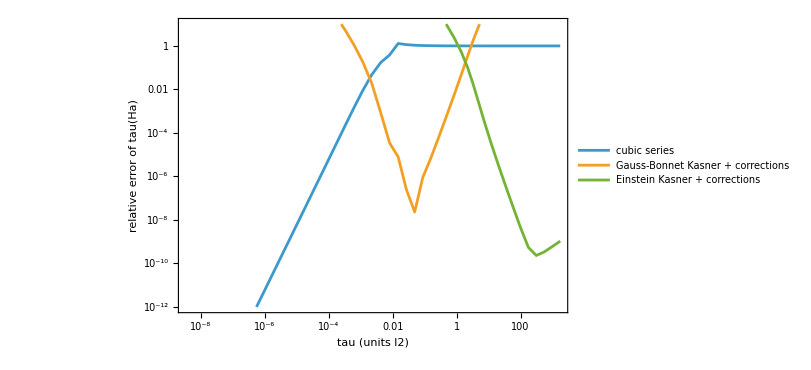

```mathematica
ListLogLogPlot[{rIacc[[All, {2, 3}]], rIacc[[All, {2, 4}]], rIacc[[All, {2, 5}]]}, Joined -> True, PlotRange -> {10^-12, 10},
 PlotLegends -> {"cubic series", "Gauss-Bonnet Kasner + corrections", "Einstein Kasner + corrections"}, Frame -> True,
 FrameLabel -> {"tau (units l2)", "relative error of tau(Ha)"}, ImageSize -> 600]
```

### 21.3 Coupled to dirac16complex: the matter-dominated cubic regime and decompactification

Now couple the gravity of section 21.2 to a gas of dirac16complex particles. In the primordial regime the mass and the self-couplings are negligible (m ≪ Ha and g_r n^(6/7) ≪ 1 with n the number density of the gas, i.e. (k_phys/M8)^6 ≪ 1 for g_r ≈ M8⁻⁶; section 23.3), so the Kohn–Sham matter of section 16 reduces to a massless collisionless gas with an isotropic comoving momentum distribution (normalized so that a = b = 1 at Ha = 1, where its energy density is κϵ = 10⁻⁶ × 3Ha.b2): with the weight cos.b2θ sin.b3θ of the seven-dimensional momentum sphere,

κϵ = C (a.b3b⁴)⁻.b9 ⟨√(cos.b2θ/a.b2 + sin.b2θ/b.b2)⟩,   κ pa = C (a.b3b⁴)⁻.b9 ⟨cos.b2θ/(3a.b2 ω)⟩,   κ pb = C (a.b3b⁴)⁻.b9 ⟨sin.b2θ/(4b.b2 ω)⟩.

Matter-dominated cubic regime. Near τ = 0 any fluid with pa = w_a ϵ (w_a < 1) wins over the vacuum terms. With b finite and Ha = p/τ the leading 44 equation is p.b3(p − 1)(648α_3 h.b2 − 12α_2) = 0, so Hb → h* = −√(α_2/(54α_3)) (not h0), and the 11 and 00 equations give

p = 1/(1 + w_a),   κ ϵ τ.b3 → (64/3) p.b3 α_2 |h*|,   α_2E^(2) : α_3E^(3) : κϵ → 9/4 : −5/4 : 1.

For the gas (and for brane radiation) w_a → 1/3 as a/b → 0: a ∝ τ^(3/4). The GAS FRACTION is κϵ divided by the sum of the sizes of all terms of the 00 equation, S_1 + S_2 + S_3 + κϵ, where the size of a curvature term is the sum of the absolute values of its monomials in Ha and Hb: S_1 = 3(Ha.b2 + 4Ha|Hb| + 2Hb.b2), S_2 = 12α_2|Hb|(4Ha.b3 + 18Ha.b2|Hb| + 12Ha Hb.b2 + |Hb|.b3), S_3 = 360α_3 Ha.b2|Hb|.b3(4Ha + 3|Hb|) (in a Kasner regime the monomials of the dominant term cancel each other, so its net value would hide it). Moving forward in time the gas fraction decreases in the cubic regime (ϵ ∝ τ⁻⁴ against τ⁻.b3) and in the Gauss–Bonnet regime (ϵ ∝ τ^(−4(p2+q2)) against τ⁻⁴), so the vacuum regimes of section 21.2 follow; in the Einstein regime it grows like τ^(2 − 3p1 − 5q1) = τ^1.160 (the auxiliary momenta are blue-shifted, pb → ϵ/4, pa → 0).

Decompactification. Einstein gravity with a fluid pa = w_a ϵ, pb = w_b ϵ has the power-law solutions a ∝ τ^P, b ∝ τ^Q with 3P(1 + w_a) + 4Q(1 + w_b) = 2: (w_a, w_b) = (0, 1/4) → (P, Q) = (0, 2/5); (1/3, 0) → (1/2, 0); (1/7, 1/7) → (1/4, 1/4). Once the gas dominates, ordinary space stops expanding and the AUXILIARY SPACE EXPANDS, b ∝ τ^(2/5): without the stabilizing potential U(b) the 7+1 universe decompactifies. Section 22.1 shows how U(b) prevents this.

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"];
rIgl = GaussianQuadratureWeights[128, 0, Pi/2, 30]; rIth = N[rIgl[[All, 1]]]; rIwt = N[rIgl[[All, 2]] Cos[rIgl[[All, 1]]]^2 Sin[rIgl[[All, 1]]]^3];
rIwt = rIwt/Total[rIwt]; rIc2 = Cos[rIth]^2; rIs2 = Sin[rIth]^2;
rIgas[la_?NumericQ, lb_?NumericQ] := Module[{ia2 = Exp[-2 la], ib2 = Exp[-2 lb], root, pref = Exp[-3 la - 4 lb]},
   root = Sqrt[rIc2 ia2 + rIs2 ib2]; pref {rIwt.root, rIwt.(rIc2 ia2/(3 root)), rIwt.(rIs2 ib2/(4 root))}];
rIC00[ha_, hb_] := rIc[[1]] /. {alf[2] -> 1, alf[3] -> rIxi, Ha -> ha, Hb -> hb};
rIlinM[ha_, hb_] := {{Coefficient[rIc[[2]], dHa], Coefficient[rIc[[2]], dHb]}, {Coefficient[rIc[[3]], dHa], Coefficient[rIc[[3]], dHb]}} /. {alf[2] -> 1, alf[3] -> rIxi, Ha -> ha, Hb -> hb};
rIlinB[ha_, hb_] := ({rIc[[2]], rIc[[3]]} /. {dHa -> 0, dHb -> 0}) /. {alf[2] -> 1, alf[3] -> rIxi, Ha -> ha, Hb -> hb};
rIlinMf = Function[{ha, hb}, Evaluate[rIlinM[ha, hb]]]; rIlinBf = Function[{ha, hb}, Evaluate[rIlinB[ha, hb]]];
rIsolve2[m_, v_] := {v[[1]] m[[2, 2]] - v[[2]] m[[1, 2]], m[[1, 1]] v[[2]] - m[[2, 1]] v[[1]]}/(m[[1, 1]] m[[2, 2]] - m[[1, 2]] m[[2, 1]]);   (* 2x2 Cramer rule *)
rIgasD[ha_?NumericQ, hb_?NumericQ, la_?NumericQ, lb_?NumericQ, cg_] := Module[{g = rIgas[la, lb]},
   rIsolve2[rIlinMf[ha, hb], -rIlinBf[ha, hb] - cg {g[[2]], g[[3]]}]];
rIgasRhs[sg_?NumericQ, yy_?VectorQ, cg_] := Module[{ha = Exp[-sg], d, dx},
   d = rIgasD[ha, yy[[1]], yy[[2]], yy[[3]], cg]; dx = -ha/d[[1]]; {d[[2]] dx, ha dx, yy[[1]] dx, dx}];
rICg = 10^-6 3; {rIhbVac1, rIx1} = rIvacAt[1];
rIhb1 = Hb /. FindRoot[rIC00[1, Hb] == rICg, {Hb, rIhbVac1}, WorkingPrecision -> 20];
rIcpl[smax_] := NDSolveValue[{rIyC'[sV] == rIgasRhs[sV, rIyC[sV], rICg], rIyC[0] == N[{rIhb1, 0, 0, rIx1}]}, rIyC, {sV, 0, smax},
    Method -> {"ExplicitRungeKutta", "DifferenceOrder" -> 8}, PrecisionGoal -> 12, AccuracyGoal -> 30, MaxSteps -> 10^6, InterpolationOrder -> All];
rIcplB = rIcpl[-Log[10^16]]; rIcplF = rIcpl[-Log[10^-14]];
rIxs = rIcplB[-Log[10^16]][[4]] - 3/4 10^-16;
rIstate[h_] := Module[{sol = If[h >= 1, rIcplB, rIcplF], hb, la, lb, x, g, d, e2, e3, sz, hm},
   {hb, la, lb, x} = sol[-Log[h]]; g = rIgas[la, lb]; d = rIgasD[h, hb, la, lb, rICg]; hm = Abs[hb];
   e2 = -12 hb (4 h^3 + 18 h^2 hb + 12 h hb^2 + hb^3); e3 = 360 rIxi h^2 hb^3 (4 h + 3 hb);
   sz = {3 (h^2 + 4 h hm + 2 hm^2), 12 hm (4 h^3 + 18 h^2 hm + 12 h hm^2 + hm^3), 360 rIxi h^2 hm^3 (4 h + 3 hm), rICg g[[1]]};   (* sizes S1, S2, S3, kappa eps *)
   <|"Hb" -> hb, "tau" -> x - rIxs, "peff" -> -h^2/d[[1]], "keps" -> rICg g[[1]], "E2" -> e2, "E3" -> e3, "S" -> sz, "frac" -> sz[[4]]/Total[sz],
     "pa/e" -> g[[2]]/g[[1]], "pb/e" -> g[[3]]/g[[1]]|>];
rIhStar = -1/Sqrt[54 rIxi];
rInear = rIstate[10^15];
check["matter-dominated cubic regime: p_eff -> 3/4, Hb -> -Sqrt[alpha2/(54 alpha3)], kappa eps tau^3 -> 9 alpha2 |h*|, alpha2 E2 : alpha3 E3 : kappa eps -> 9/4 : -5/4 : 1 (Ha = 10^15)",
  Abs[rInear["peff"] - 3/4] < 10^-3 && Abs[rInear["Hb"]/rIhStar - 1] < 10^-3 && Abs[rInear["keps"] rInear["tau"]^3/(9 Abs[rIhStar]) - 1] < 10^-2 &&
  Abs[rInear["E2"]/rInear["keps"] - 9/4] < 10^-2 && Abs[rInear["E3"]/rInear["keps"] + 5/4] < 10^-2]
rIplat = rIstate /@ {3 10^5, 30, 10^-2};
check["coupled: where the gas is a small fraction the effective exponents are those of the vacuum (1, p2, p1 within 10^-2)",
  Abs[rIplat[[1]]["peff"] - 1] < 10^-2 && Abs[rIplat[[2]]["peff"] - rIp2] < 10^-2 && Abs[rIplat[[3]]["peff"] - rIp1] < 10^-2]
rIlate = rIstate[10^-14];
check["without the stabilizing potential the gas-dominated Einstein regime decompactifies: tau Ha -> 0, tau Hb -> 2/5, pb/eps -> 1/4 (Ha = 10^-14)",
  rIlate["tau"] 10^-14 < 10^-3 && Abs[rIlate["tau"] rIlate["Hb"] - 2/5] < 2 10^-3 && Abs[rIlate["pb/e"] - 1/4] < 10^-3]
rIgrow = With[{gA = rIstate[10^-2], gB = rIstate[10^-4]}, Log[(gB["keps"]/(3 10^-8))/(gA["keps"]/(3 10^-4))]/Log[gB["tau"]/gA["tau"]]];
check["the gas fraction grows like tau^(2 - 3 p1 - 5 q1) = tau^1.160 in the Einstein regime (to 2 10^-2)", Abs[rIgrow - (2 - 3 rIp1 - 5 rIq1)] < 2 10^-2]
rIfl[wa_, wb_] := Solve[{(3 (pP^2 + 4 pP qQ + 2 qQ^2)) == cC, (3 pP^2 + 8 pP qQ - 2 pP + 10 qQ^2 - 4 qQ) == -wa cC, 3 (2 pP^2 + 3 pP qQ - pP + 2 qQ^2 - qQ) == -wb cC,
     3 pP (1 + wa) + 4 qQ (1 + wb) == 2}, {pP, qQ, cC}];
check["Einstein + fluid power laws a ~ tau^P, b ~ tau^Q: (wa, wb) = (0, 1/4) -> (0, 2/5); (1/3, 0) -> (1/2, 0); (1/7, 1/7) -> (1/4, 1/4) (tau^2 E^(1) from EKas of section 14.1)",
  Expand[(EKas[[1]] /. {pK -> pP, qK -> qQ}) - {3 (pP^2 + 4 pP qQ + 2 qQ^2), 3 pP^2 + 8 pP qQ - 2 pP + 10 qQ^2 - 4 qQ, 3 (2 pP^2 + 3 pP qQ - pP + 2 qQ^2 - qQ)}] === {0, 0, 0} &&
  rIfl[0, 1/4] == {{pP -> 0, qQ -> 2/5, cC -> 24/25}} && rIfl[1/3, 0] == {{pP -> 1/2, qQ -> 0, cC -> 3/4}} && rIfl[1/7, 1/7] == {{pP -> 1/4, qQ -> 1/4, cC -> 21/16}}]
rIlead = {Coefficient[Expand[(rIc[[1]] /. {Ha -> pw/tS, Hb -> rIIIhh, dHa -> -pw/tS^2, dHb -> 0}) tS^3], tS, 0],
   Coefficient[Expand[(rIc[[2]] /. {Ha -> pw/tS, Hb -> rIIIhh, dHa -> -pw/tS^2, dHb -> 0}) tS^3], tS, 0],
   Coefficient[Expand[(rIc[[3]] /. {Ha -> pw/tS, Hb -> rIIIhh, dHa -> -pw/tS^2, dHb -> 0}) tS^4], tS, 0]};
check["matter-dominated cubic regime (any fluid, b finite): leading 44 term p^3 (p - 1)(648 alpha3 h^2 - 12 alpha2); with h^2 = alpha2/(54 alpha3): p = 1/(1 + w_a) and kappa eps tau^3 = (64/3) p^3 alpha2 |h|",
  Expand[rIlead[[3]] - pw^3 (pw - 1) (648 alf[3] rIIIhh^2 - 12 alf[2])] === 0 &&
  (Select[pw /. Solve[(rIlead[[2]] + wA rIlead[[1]] /. rIIIhh -> -Sqrt[alf[2]/(54 alf[3])]) == 0, pw], # =!= 0 &] // Simplify) == {1/(1 + wA)} &&
  Simplify[(rIlead[[1]] /. rIIIhh -> -Sqrt[alf[2]/(54 alf[3])]) - 64/3 pw^3 alf[2] Sqrt[alf[2]/(54 alf[3])], alf[2] > 0 && alf[3] > 0] === 0]
{"near the singularity (Ha = 10^15): p_eff, Hb, kappa eps tau^3, alpha2 E2/(kappa eps), alpha3 E3/(kappa eps)" -> {rInear["peff"], rInear["Hb"], rInear["keps"] rInear["tau"]^3, rInear["E2"]/rInear["keps"], rInear["E3"]/rInear["keps"]},
 "(p_eff, gas fraction) at Ha = 3 10^5, 30, 10^-2" -> ({#["peff"], #["frac"]} & /@ rIplat), "late (Ha = 10^-14): tau Ha, tau Hb, pa/eps, pb/eps" -> {rIlate["tau"] 10^-14, rIlate["tau"] rIlate["Hb"], rIlate["pa/e"], rIlate["pb/e"]},
 "Einstein-regime growth exponent: numerical, 2 - 3 p1 - 5 q1" -> {rIgrow, N[2 - 3 rIp1 - 5 rIq1]}}
```

matter-dominated cubic regime: p_eff -> 3/4, Hb -> -Sqrt[alpha2/(54 alpha3)], kappa eps tau^3 -> 9 alpha2 |h*|, alpha2 E2 : alpha3 E3 : kappa eps -> 9/4 : -5/4 : 1 (Ha = 10^15)→True

coupled: where the gas is a small fraction the effective exponents are those of the vacuum (1, p2, p1 within 10^-2)→True

without the stabilizing potential the gas-dominated Einstein regime decompactifies: tau Ha -> 0, tau Hb -> 2/5, pb/eps -> 1/4 (Ha = 10^-14)→True

the gas fraction grows like tau^(2 - 3 p1 - 5 q1) = tau^1.160 in the Einstein regime (to 2 10^-2)→True

Einstein + fluid power laws a ~ tau^P, b ~ tau^Q: (wa, wb) = (0, 1/4) -> (0, 2/5); (1/3, 0) -> (1/2, 0); (1/7, 1/7) -> (1/4, 1/4) (tau^2 E^(1) from EKas of section 14.1)→True

matter-dominated cubic regime (any fluid, b finite): leading 44 term p^3 (p - 1)(648 alpha3 h^2 - 12 alpha2); with h^2 = alpha2/(54 alpha3): p = 1/(1 + w_a) and kappa eps tau^3 = (64/3) p^3 alpha2 |h|→True

{near the singularity (Ha = 10^15): p_eff, Hb, kappa eps tau^3, alpha2 E2/(kappa eps), alpha3 E3/(kappa eps)→{0.75,-136.083,1224.74,2.25001,-1.25001},(p_eff, gas fraction) at Ha = 3 10^5, 30, 10^-2→{{0.999318,0.00118877},{1.55967,1.84503×10^-7},{0.547086,0.0000283202}},late (Ha = 10^-14): tau Ha, tau Hb, pa/eps, pb/eps→{0.000314858,0.399995,1.87311×10^-6,0.249999},Einstein-regime growth exponent: numerical, 2 - 3 p1 - 5 q1→{1.16983,1.16019}}

### 21.4 Pair creation in the primordial regime and the brane

Section 14.3 computed the Bogoliubov coefficient |β|.b2 of a massless mode on the Einstein–Kasner background as a function F(K) of the scaling variable K. For large K, F does NOT fall exponentially, as it would for a smooth expansion history, but as a power,

F(K) ∝ K^(−2(p1 − q1)/(1 − p1)) = K^(−(3√2 + 2)/2) = K^(−3.121…),

because near x0 = 0 the phase ∫ω dτ ∝ K τ^(1−p1) while the direction of the mode Hamiltonian turns like τ^(p1−q1): the non-adiabaticity comes from the singularity itself. The comoving number of pairs created in each logarithmic interval of crossing time therefore grows toward τ = 0 (∝ τ⁻⁶ in the Kasner phase): the primordial production of dirac16complex is dominated by the earliest, Planckian times and gives a gas fraction of order one there — the gas used in section 21.3.

The Standard Model plasma on the brane can only matter in the bulk when its smeared density ρ_4/V⊥ is comparable to the curvature terms. At T = M8 and H = M8 its fraction is (π.b2 g*/30) M8⁴/(3 M_Pl.b2 M8.b2) ≈ 2 × 10⁻.b2⁸ (M8 = 10 TeV, M_Pl = 2.435 × 10.b9⁸ GeV, g* = 106.75): the brane is gravitationally negligible in the whole primordial regime.

```mathematica
rIsg1 = {{0, 1}, {1, 0}}; rIsg2 = {{0, -I}, {I, 0}};
rIbog[k_, p_, q_] := Module[{c, sol, t0 = 10^-15, t1 = 300, v0, v1, h0m, h1m},
   h0m = N[k t0^-p rIsg1 + k t0^-q rIsg2, 30]; h1m = N[k t1^-p rIsg1 + k t1^-q rIsg2, 30];
   v0 = Normalize[Eigenvectors[h0m][[Ordering[Eigenvalues[h0m]]]][[2]]]; v1 = Normalize[Eigenvectors[h1m][[Ordering[Eigenvalues[h1m]]]][[1]]];
   sol = NDSolveValue[{c'[sB] == -I Exp[sB] (k Exp[-p sB] rIsg1 + k Exp[-q sB] rIsg2).c[sB], c[Log[t0]] == N[v0]}, c[Log[t1]], {sB, Log[t0], Log[t1]},
     Method -> {"ExplicitRungeKutta", "DifferenceOrder" -> 8}, PrecisionGoal -> 11, AccuracyGoal -> 13, MaxSteps -> Infinity];
   Abs[Conjugate[N[v1]].sol]^2];
rIFk = {rIbog[1, N[rIp1], N[rIq1]], rIbog[8, N[rIp1], N[rIq1]], rIbog[16, N[rIp1], N[rIq1]]};
rItail = Log[rIFk[[3]]/rIFk[[2]]]/Log[2];
check["Einstein-Kasner pair creation: F(1) == 0.0107493 (section 14.3) and the tail F ~ K^(-(3 Sqrt[2] + 2)/2) (exponent between K = 8 and 16 to 2 10^-2)",
  Abs[rIFk[[1]] - 0.0107493] < 10^-6 && Abs[rItail + (3 Sqrt[2] + 2)/2] < 2 10^-2 && Simplify[2 (rIp1 - rIq1)/(1 - rIp1) - (3 Sqrt[2] + 2)/2] === 0]
rIbrane = (Pi^2 106.75/30) (10.^4)^4/(3 (2.435 10^18)^2 (10.^4)^2);
check["brane plasma at T = M8, H = M8: fraction (Pi^2 g*/30) M8^4/(3 M_Pl^2 M8^2) < 10^-27", rIbrane < 10^-27]
{"F(1), F(8), F(16)" -> rIFk, "tail exponent (K = 8 .. 16), -(3 Sqrt[2] + 2)/2" -> {rItail, N[-(3 Sqrt[2] + 2)/2]}, "brane fraction at T = H = M8" -> rIbrane}
```

Einstein-Kasner pair creation: F(1) == 0.0107493 (section 14.3) and the tail F ~ K^(-(3 Sqrt[2] + 2)/2) (exponent between K = 8 and 16 to 2 10^-2)→True

brane plasma at T = M8, H = M8: fraction (Pi^2 g*/30) M8^4/(3 M_Pl^2 M8^2) < 10^-27→True

{F(1), F(8), F(16)→{0.0107493,7.10407×10^-6,8.1573×10^-7},tail exponent (K = 8 .. 16), -(3 Sqrt[2] + 2)/2→{-3.12248,-3.12132},brane fraction at T = H = M8→1.97436×10^-28}

## 22. Regime II: the modern regime (a stabilized auxiliary space, four-dimensional gravity on the brane)

### 22.1 The stabilizing potential catches the auxiliary space: radion oscillations

Section 21.3 showed that the auxiliary space must be held. Add the stabilizing potential U(b) = (K_U/2) (ln(b/b0)).b2 (U_0 = 0, κK_U = 12 m_r.b2, m_r = 10⁻.b3/ℓ2) to the coupled solution of section 21.3 at Ha = 10⁻.b2 (Einstein–Kasner regime, τ ≈ 57), with b0 where the Kasner contraction would arrive at τ = 1/m_r. The equations are integrated in x0 (Ha now oscillates). When the expansion rate falls below m_r the radion β = ln(b/b0) is caught and oscillates about 0; its energy then behaves like four-dimensional matter, and the exact solution of β″ + (2/τ)β′ + m_r.b2β = 0 (the radion equation of section 20.3 in a matter-dominated universe, H_E = 2/(3τ)) is the accurate approximate solution

β ≈ A sin(m_r τ + ϑ)/(m_r (τ − τ_E)),   H_E = Ha + 2Hb ≈ 2/(3(τ − τ_E)),   corrections O(1/(m_r τ))   (amplitude A, phase ϑ).

The dirac16complex gas (frozen auxiliary momenta = Kaluza–Klein masses) is then also four-dimensional matter: its share of the energy stays constant, and the radion carries the rest (99%): this is the cosmological moduli problem of the minimal model.

```mathematica
rIIm = 1/1000;
{rIIhb0, rIIla0, rIIlb0, rIIx0} = rIcplF[-Log[1/100]]; rIItau0 = rIIx0 - rIxs;
rIIlnb0 = rIIlb0 + rIq1 Log[1/(rIIm rIItau0)];
rIIrhs[tt_?NumericQ, yy_?VectorQ] := Module[{ha, hb, la, lb, g, bet, kU, d}, {ha, hb, la, lb} = yy; g = rIgas[la, lb]; bet = lb - rIIlnb0; kU = 6 rIIm^2 bet^2;
   d = rIsolve2[rIlinMf[ha, hb], -rIlinBf[ha, hb] - {rICg g[[2]] - kU, rICg g[[3]] - kU - 3 rIIm^2 bet}]; {d[[1]], d[[2]], ha, hb}];
rIIha0 = 1/100;
rIIhbC = Hb /. FindRoot[rIC00[rIIha0, Hb] == rICg rIgas[rIIla0, rIIlb0][[1]] + 6 rIIm^2 (rIIlb0 - rIIlnb0)^2, {Hb, rIIhb0}];
rIIcap = NDSolveValue[{rIIyK'[tt] == rIIrhs[tt, rIIyK[tt]], rIIyK[rIItau0] == N[{rIIha0, rIIhbC, rIIla0, rIIlb0}]}, rIIyK, {tt, rIItau0, 3 10^5},
    Method -> {"ExplicitRungeKutta", "DifferenceOrder" -> 8, "StiffnessTest" -> False}, PrecisionGoal -> 11, AccuracyGoal -> 16, MaxSteps -> 10^7, MaxStepSize -> 50];
rIIHEavg[t1_] := {Mean[Table[rIIcap[tt][[1]] + 2 rIIcap[tt][[2]], {tt, t1, t1 + 2 Pi/rIIm, 2 Pi/rIIm/2000}]], t1 + Pi/rIIm};
rIItE = With[{h = rIIHEavg[2.9 10^5]}, h[[2]] - 2/(3 h[[1]])];          (* H_E = 2/(3 (tau - tau_E)) over the last period *)
rIIdata = Table[{tt, rIIcap[tt][[4]] - rIIlnb0}, {tt, 10^5, 3 10^5, 50}];
rIIcs = LeastSquares[Table[{Sin[rIIm d[[1]]], Cos[rIIm d[[1]]]}, {d, rIIdata}], Table[d[[2]] rIIm (d[[1]] - rIItE), {d, rIIdata}]];
rIIfit = {rIIaF -> Norm[rIIcs], rIIphF -> ArcTan[rIIcs[[1]], rIIcs[[2]]], rIItEF -> rIItE};
rIIres = Max[Abs[rIIdata[[All, 2]] - ((rIIaF Sin[rIIm # + rIIphF]/(rIIm (# - rIItEF))) & /@ rIIdata[[All, 1]] /. rIIfit)]]/Max[Abs[rIIdata[[All, 2]]]];
rIIHE[t1_] := With[{h = rIIHEavg[t1]}, h[[1]] (h[[2]] - rIItE)];
rIIfr[tt_] := With[{y = rIIcap[tt]}, rICg rIgas[y[[3]], y[[4]]][[1]]/(3 (y[[1]] + 2 y[[2]])^2)];
rIIheVals = {rIIHE[10^5], rIIHE[2 10^5]}; rIIfrVals = {rIIfr[10^5], rIIfr[3 10^5]};
check["capture: the radion oscillates like a four-dimensional massive field in a matter-dominated universe: with tau_E from <H_E> = 2/(3 (tau - tau_E)) over the last period, beta = A sin(m_r tau + vartheta)/(m_r (tau - tau_E)) to 2 10^-2, <H_E>(tau - tau_E) = 2/3 to 10^-2 at tau = 10^5 and 2 10^5, the gas share constant to 2 10^-2",
  rIIres < 2 10^-2 && AllTrue[rIIheVals, Abs[# - 2/3] < 10^-2 &] && Abs[rIIfrVals[[2]]/rIIfrVals[[1]] - 1] < 2 10^-2]
{"start tau, beta(start)" -> {rIItau0, rIIlb0 - rIIlnb0}, "fit A, vartheta, tau_E; max residual/amplitude" -> {rIIaF, rIIphF, rIItEF, rIIres} /. rIIfit,
 "<H_E>(tau - tau_E) at tau = 10^5, 2 10^5" -> rIIheVals, "gas share at tau = 10^5, 3 10^5" -> rIIfrVals, "radion share 1 - gas share" -> 1 - rIIfrVals[[2]]}
```

capture: the radion oscillates like a four-dimensional massive field in a matter-dominated universe: with tau_E from <H_E> = 2/(3 (tau - tau_E)) over the last period, beta = A sin(m_r tau + vartheta)/(m_r (tau - tau_E)) to 2 10^-2, <H_E>(tau - tau_E) = 2/3 to 10^-2 at tau = 10^5 and 2 10^5, the gas share constant to 2 10^-2→True

{start tau, beta(start)→{56.7505,0.459596},fit A, vartheta, tau_E; max residual/amplitude→{0.46933,2.13601,-1564.36,0.0127862},<H_E>(tau - tau_E) at tau = 10^5, 2 10^5→{0.666942,0.666736},gas share at tau = 10^5, 3 10^5→{0.00859579,0.00872803},radion share 1 - gas share→0.991272}

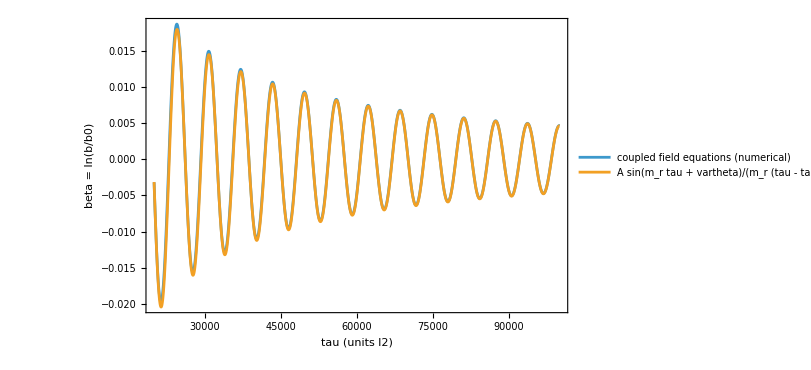

```mathematica
Plot[{rIIcap[tt][[4]] - rIIlnb0, (rIIaF Sin[rIIm tt + rIIphF]/(rIIm (tt - rIItEF))) /. rIIfit}, {tt, 2 10^4, 10^5}, PlotPoints -> 400, Frame -> True,
 FrameLabel -> {"tau (units l2)", "beta = ln(b/b0)"}, PlotLegends -> {"coupled field equations (numerical)", "A sin(m_r tau + vartheta)/(m_r (tau - tau_E))"}, ImageSize -> 600]
```

### 22.2 Radion decay, the moduli problem and the Kaluza–Klein channels

In physical units (M8 = 10 TeV, reduced M_Pl = 2.435 × 10.b9⁸ GeV, V⊥ = M_Pl.b2/M8⁶) the radion couples to the brane fields through L = (ϕ/(√3 M_Pl)) T^μ_μ (section 20.3). For a fermion of mass m_f (N_c colours) and, through the trace anomaly T^μ_μ ⊃ −(b_QCD α_s/(8π)) G^a_μν G^aμν (b_QCD = 11 − 2n_f/3, the first coefficient of the QCD beta function), for two gluons:

Γ(ϕ → f f̄) = N_c m_f.b2 m_r (1 − 4m_f.b2/m_r.b2)^(3/2)/(24π M_Pl.b2),   Γ(ϕ → gg) = b_QCD.b2 α_s.b2 m_r.b3/(96π.b3 M_Pl.b2).

For m_r = 10 GeV (b, c, τ, μ pairs and gluons, α_s = 0.18, n_f = 5) the brane channels give Γ_brane ≈ 4.6 × 10⁻.b3⁷ GeV, a lifetime of 1.4 × 10.b9.b2 s, and would reheat the brane only to T_RH = [Γ_brane M_Pl/√(π.b2 g*/90)]^(1/2) ≈ 10⁻⁹ GeV (g* = 10.75), far below the 4 MeV that nucleosynthesis needs.

Decay into the bulk. The radion also couples to every Kaluza–Klein mode of the bulk fields. A mode of dirac16complex with Kaluza–Klein momentum μ_n = 2π|n|/ℓ⊥ (n in Z⁴, ℓ⊥ = V⊥^(1/4) the size of the auxiliary torus) has, in the four-dimensional Einstein frame (h = e^(−4β) g_E), the mass M_E = e^(−2β) (m.b2 + μ_n.b2 e^(−2β))^(1/2); it therefore couples to ϕ = √12 M_Pl β with g_n = (2M_n + μ_n.b2/M_n)/(√12 M_Pl), M_n = (m.b2 + μ_n.b2)^(1/2). For m ≪ μ_n each Kaluza–Klein level (four brane Dirac spinors) gives

Γ_n = 4 g_n.b2 m_r (1 − 4M_n.b2/m_r.b2)^(3/2)/(8π) = 3 μ_n.b2 m_r (1 − 4μ_n.b2/m_r.b2)^(3/2)/(8π M_Pl.b2),

and the sum over the 1.17 × 10.b9.b3 momenta with 2μ_n < m_r, done shell by shell with the number r_4(k) = 8σ(k) − 32σ(k/4) of lattice vectors with |n|.b2 = k (σ the divisor sum, σ(k/4) = 0 unless 4 divides k), agrees with its continuum limit

Γ_bulk = Σ_n Γ_n ≈ (3 m_r/(8π M_Pl.b2)) (V⊥/(8π.b2)) (m_r/2)⁶ B(3, 5/2)/2 ≈ 6.0 × 10⁻.b2⁴ GeV   (lifetime 0.11 s):

thirteen orders of magnitude faster than the brane channels (the Kaluza–Klein gravitons add channels of the same strength; for m > m_r/2 the dirac16complex channels close). The radion decays into the BULK: its energy goes to Kaluza–Klein modes, which return it to the brane only through couplings suppressed by the volume (a Kaluza–Klein graviton of mass M decays into brane fields at a rate of order M.b3/M_Pl.b2). This is the cosmological moduli problem of the minimal model in the form it takes with large extra dimensions. The minimal model therefore needs the radion and bulk energy left at the end of regime I to be removed before nucleosynthesis (for example by a later period of inflation on the brane, not part of the model); sections 22.3–22.4 start after such a reheating, below the normalcy temperature T* ≈ (M8⁶/M_Pl)^(1/5) ≈ 13 GeV.

```mathematica
rIIMPl = 2.435 10^18; rIIM8 = 10.^4; rIIVp = rIIMPl^2/rIIM8^6; rIIhbar = 6.582119569 10^-25;
rIIgff[mphi_, mf_, nc_] := If[4 mf^2 < mphi^2, nc mf^2 mphi (1 - 4 mf^2/mphi^2)^(3/2)/(24 Pi rIIMPl^2), 0];
rIIggg[mphi_, as_, nf_] := (11 - 2 nf/3)^2 as^2 mphi^3/(96 Pi^3 rIIMPl^2);
rIIgam = rIIgff[10., 4.183, 3] + rIIgff[10., 1.273, 3] + rIIgff[10., 1.77693, 1] + rIIgff[10., 0.1056583755, 1] + rIIggg[10., 0.18, 5];
rIITRH = Sqrt[rIIgam rIIMPl/Sqrt[Pi^2 10.75/90]];
rIINKK = rIIVp (Pi^2/2) (10./2)^4/(2 Pi)^4;
check["through brane fields alone a 10 GeV radion would decay far too late: T_RH < 10^-6 GeV (nucleosynthesis needs 4 10^-3 GeV); 10^13 Kaluza-Klein channels below m_r/2",
  rIITRH < 10^-6 && 10^13 < rIINKK < 2 10^13]
rIIkmax = Floor[(10. rIIVp^(1/4)/(4 Pi))^2];                        (* |n|^2 = k <= kmax  <=>  2 mu_n < m_r *)
rIIsig = DivisorSigma[1, Range[rIIkmax]];
rIIr4 = 8 rIIsig; rIIr4[[4 ;; ;; 4]] -= 32 rIIsig[[1 ;; Floor[rIIkmax/4]]];       (* r_4(k) = 8 sigma(k) - 32 sigma(k/4) *)
rIImuK = 2 Pi Sqrt[N[Range[rIIkmax]]]/rIIVp^(1/4);
rIIgBulk = 3 10./(8 Pi rIIMPl^2) Total[rIIr4 rIImuK^2 (1 - 4 rIImuK^2/100.)^(3/2)];
rIIgBulkC = 3 10./(8 Pi rIIMPl^2) rIIVp/(8 Pi^2) 5.^6 Beta[3, 5/2]/2;
check["the number of lattice vectors with |n|^2 = k is r_4(k) = 8 sigma(k) - 32 sigma(k/4) (direct count for k <= 60)",
  With[{nn = Total[Tuples[Range[-8, 8], 4]^2, {2}]}, Table[Count[nn, kk], {kk, 60}]] == rIIr4[[1 ;; 60]]]
check["the radion decays into the bulk: the lattice sum over the Kaluza-Klein modes of dirac16complex (m << m_r/2) equals its continuum limit to 10^-6, the number of momenta to 10^-5, and Gamma_bulk/Gamma_brane > 10^12",
  Abs[rIIgBulk/rIIgBulkC - 1] < 10^-6 && Abs[Total[rIIr4]/rIINKK - 1] < 10^-5 && rIIgBulk/rIIgam > 10^12]
{"Gamma (GeV), lifetime (s), T_RH (GeV)" -> {rIIgam, rIIhbar/rIIgam, rIITRH}, "Kaluza-Klein momenta below m_r/2" -> rIINKK,
 "radion into bulk dirac16complex pairs (m << m_r/2): Gamma_bulk lattice, continuum (GeV), lifetime (s), Gamma_bulk/Gamma_brane" -> {rIIgBulk, rIIgBulkC, rIIhbar/rIIgBulk, rIIgBulk/rIIgam},
 "V_perp (GeV^-4), l_perp (m), 2 Pi/l_perp (GeV)" -> {rIIVp, rIIVp^(1/4) 1.973269804 10^-16, 2 Pi/rIIVp^(1/4)}, "normalcy temperature (M8^6/M_Pl)^(1/5) (GeV)" -> (rIIM8^6/rIIMPl)^(1/5)}
```

through brane fields alone a 10 GeV radion would decay far too late: T_RH < 10^-6 GeV (nucleosynthesis needs 4 10^-3 GeV); 10^13 Kaluza-Klein channels below m_r/2→True

the number of lattice vectors with |n|^2 = k is r_4(k) = 8 sigma(k) - 32 sigma(k/4) (direct count for k <= 60)→True

the radion decays into the bulk: the lattice sum over the Kaluza-Klein modes of dirac16complex (m << m_r/2) equals its continuum limit to 10^-6, the number of momenta to 10^-5, and Gamma_bulk/Gamma_brane > 10^12→True

{Gamma (GeV), lifetime (s), T_RH (GeV)→{4.57217×10^-37,1.43961×10^12,1.01261×10^-9},Kaluza-Klein momenta below m_r/2→1.17335×10^13,radion into bulk dirac16complex pairs (m << m_r/2): Gamma_bulk lattice, continuum (GeV), lifetime (s), Gamma_bulk/Gamma_brane→{5.99917×10^-24,5.99917×10^-24,0.109717,1.31211×10^13},V_perp (GeV^-4), l_perp (m), 2 Pi/l_perp (GeV)→{5.92923×10^12,3.07919×10^-13,0.00402652},normalcy temperature (M8^6/M_Pl)^(1/5) (GeV)→13.2648}

### 22.3 The Standard Model plasma on the brane: g*(T), g*s(T) and the time–temperature relation

With b static the brane obeys the Friedmann equations of section 20.3, 3 M_Pl.b2 Ha.b2 = ρ_4 + M_Pl.b2 Λ4 and Ha′ = −(ρ_4 + p_4)/(2M_Pl.b2). In the radiation era ρ_4 = (π.b2/30) g*(T) T⁴ and the entropy s = (2π.b2/45) g*s(T) T.b3 is conserved, s a.b3 = constant, so that

Ha = (π.b2 g*/90)^(1/2) T.b2/M_Pl,     ln a = −ln T − (1/3) ln g*s(T) + const,     t(T) = t(T1) + ∫ d(ln a)/Ha = t(T1) + ∫_T^T1 (dT′/T′) [1 + (1/3) d ln g*s/d ln T′]/Ha(T′),

evaluated on 481 points equally spaced in ln T from T1 = 10 GeV (where t(T1) = 1/(2Ha)) to 10 keV; on each step 1/Ha is taken exponential in ln T (exact when g* is constant), so a step adds Δ(ln a) (1/H_(i+1) − 1/H_i)/ln(H_i/H_(i+1)); halving the grid changes t by less than 10⁻⁵.

g* and g*s are computed here for ideal gases of all Standard Model particles with their masses (PDG values of section 17), with the series for each species i (x = m_i/T; +: bosons, −: fermions with alternating signs):

ρ_i = (g_i T⁴/(2π.b2)) Σ_{n≥1} (±1)^(n+1) [3(nx).b2 K_2(nx) + (nx).b3 K_1(nx)]/n⁴,   p_i = (g_i T⁴/(2π.b2)) Σ_{n≥1} (±1)^(n+1) (nx).b2 K_2(nx)/n⁴,

s_i = (ρ_i + p_i)/T. The QCD crossover is modelled by the switch S(T) = (1 + tanh((T − 0.160 GeV)/0.030 GeV))/2 between quarks and gluons and the lightest hadrons (π, K, η, ρ, ω, K*, η′, nucleons); this model differs from the lattice equation of state by up to about 10% near the crossover. The neutrinos decouple while e± are relativistic: T_ν = T (g_γe(T)/(11/2))^(1/3), and their density is scaled by N_eff/3 = 3.044/3. (The Python check tools/ref_coupled.py integrates the momentum integrals instead of summing the series.)

```mathematica
rIIsp = {{2, 0., -1, "always"}, {6, 80.3692, -1, "always"}, {3, 91.1880, -1, "always"}, {1, 125.20, -1, "always"}, {4, 0.51099895 10^-3, 1, "always"},
   {4, 0.1056583755, 1, "always"}, {4, 1.77693, 1, "always"}, {6, 0., 1, "nu"}, {16, 0., -1, "qgp"}, {12, 2.16 10^-3, 1, "qgp"}, {12, 4.70 10^-3, 1, "qgp"},
   {12, 93.5 10^-3, 1, "qgp"}, {12, 1.2730, 1, "qgp"}, {12, 4.183, 1, "qgp"}, {12, 172.56, 1, "qgp"}, {2, 0.13957039, -1, "hadron"}, {1, 0.1349768, -1, "hadron"},
   {2, 0.493677, -1, "hadron"}, {2, 0.497611, -1, "hadron"}, {1, 0.547862, -1, "hadron"}, {9, 0.77526, -1, "hadron"}, {3, 0.78266, -1, "hadron"},
   {12, 0.8955, -1, "hadron"}, {1, 0.95778, -1, "hadron"}, {4, 0.93827209, 1, "hadron"}, {4, 0.93956542, 1, "hadron"}};
rIInn = N[Range[400]];
rIIrs[t_, g_, m_, st_] := Module[{x = m/t, c, k2, k1},
   If[x > 60, Return[{0., 0.}]];
   c = If[st == 1, (-1.)^(rIInn + 1), 1. + 0 rIInn];
   If[x == 0, Return[With[{r = g t^4 6 Total[c/rIInn^4]/(2 Pi^2)}, {r, 4 r/(3 t)}]]];
   k2 = BesselK[2, rIInn x]; k1 = BesselK[1, rIInn x];
   With[{r = g t^4 Total[c (3 (rIInn x)^2 k2 + (rIInn x)^3 k1)/rIInn^4]/(2 Pi^2), p = g t^4 Total[c (rIInn x)^2 k2/rIInn^4]/(2 Pi^2)}, {r, (r + p)/t}]];
rIIS[t_] := (1 + Tanh[(t - 0.160)/0.030])/2;
rIIgge[t_] := (rIIrs[t, 2, 0., -1][[2]] + rIIrs[t, 4, 0.51099895 10^-3, 1][[2]]) 45/(2 Pi^2 t^3);
rIIgstars[t_?NumericQ] := Module[{tot = {0., 0.}, tn, w},
   Do[Which[sp[[4]] == "nu", tn = t Min[1, (rIIgge[t]/5.5)^(1/3)]; tot += 3.044/3 rIIrs[tn, sp[[1]], 0., 1],
      True, w = Switch[sp[[4]], "qgp", rIIS[t], "hadron", 1 - rIIS[t], _, 1]; tot += w rIIrs[t, sp[[1]], sp[[2]], sp[[3]]]], {sp, rIIsp}];
   {tot[[1]] 30/(Pi^2 t^4), tot[[2]] 45/(2 Pi^2 t^3)}];
rIIgtab = rIIgstars /@ {1000., 10., 1., 0.3, 0.1, 0.01, 0.001, 10.^-4, 10.^-6};
check["g* limits: 106.75 above the electroweak scale (to 0.1), 10.75 near 3 MeV (to 0.1), 2 + (21/4)(4/11)^(4/3)(3.044/3) = 3.3855 after e+e- annihilation (to 10^-3)",
  Abs[rIIgtab[[1, 1]] - 106.75] < 0.1 && Abs[rIIgstars[0.003][[1]] - 10.75] < 0.1 && Abs[rIIgtab[[9, 1]] - (2 + 21/4 (4/11)^(4/3) 3.044/3)] < 10^-3]
rIIlnT = Table[Log[10.] - i (Log[10.] - Log[10.^-5])/480, {i, 0, 480}];
rIIgg = rIIgstars[Exp[#]] & /@ rIIlnT;
rIIHg = MapThread[Sqrt[Pi^2 #2[[1]]/90] Exp[2 #1]/rIIMPl &, {rIIlnT, rIIgg}];
rIIlna = -rIIlnT - Log[rIIgg[[All, 2]]]/3;
rIItg = Join[{0.}, Accumulate[Differences[rIIlna] (1/Rest[rIIHg] - 1/Most[rIIHg])/Log[Most[rIIHg]/Rest[rIIHg]]]] + 1/(2 rIIHg[[1]]);   (* 1/Ha exponential in ln T on each step *)
rIIidx[t_] := Round[(Log[10.] - Log[t])/((Log[10.] - Log[10.^-5])/480)] + 1;
rIItvals = rIItg[[rIIidx[#]]] & /@ {1., 0.1, 0.01, 0.001, 10.^-4, 10.^-5};
rIItgHalf = With[{la = rIIlna[[1 ;; -1 ;; 2]], hg = rIIHg[[1 ;; -1 ;; 2]]}, Join[{0.}, Accumulate[Differences[la] (1/Rest[hg] - 1/Most[hg])/Log[Most[hg]/Rest[hg]]]] + 1/(2 hg[[1]])];
check["the time-temperature quadrature is converged: halving the grid changes t(10 keV) by less than 10^-5", Abs[Last[rIItgHalf]/Last[rIItg] - 1] < 10^-5]
check["radiation era: t(1 MeV) = 0.74 s within 5% (1/(2 Ha) with g* = 10.75)", Abs[rIItvals[[4]] rIIhbar/0.74 - 1] < 0.05]
{"g*, g*s at 1 TeV, 10 GeV, 1 GeV, 300 MeV, 100 MeV, 10 MeV, 1 MeV, 100 keV, 1 keV" -> rIIgtab, "t(T) in s at 1 GeV, 100 MeV, 10 MeV, 1 MeV, 100 keV, 10 keV" -> rIItvals rIIhbar,
 "1/(2 Ha(T)) / t(T)" -> (1/(2 rIIHg[[rIIidx[#]]]) & /@ {1., 0.1, 0.01, 0.001, 10.^-4, 10.^-5})/rIItvals}
```

g* limits: 106.75 above the electroweak scale (to 0.1), 10.75 near 3 MeV (to 0.1), 2 + (21/4)(4/11)^(4/3)(3.044/3) = 3.3855 after e+e- annihilation (to 10^-3)→True

the time-temperature quadrature is converged: halving the grid changes t(10 keV) by less than 10^-5→True

radiation era: t(1 MeV) = 0.74 s within 5% (1/(2 Ha) with g* = 10.75)→True

{g*, g*s at 1 TeV, 10 GeV, 1 GeV, 300 MeV, 100 MeV, 10 MeV, 1 MeV, 100 keV, 1 keV→{{106.794,106.778},{86.2963,86.2045},{76.4179,75.5771},{64.6458,64.2172},{18.3152,17.9496},{10.8372,10.8352},{10.6336,10.6361},{4.32702,4.81438},{3.383,3.93746}},t(T) in s at 1 GeV, 100 MeV, 10 MeV, 1 MeV, 100 keV, 10 keV→{2.7941×10^-7,0.0000612354,0.007393,0.743187,118.84,13161.7},1/(2 Ha(T)) / t(T)→{0.990757,0.923416,0.994323,0.998548,0.978928,0.999641}}

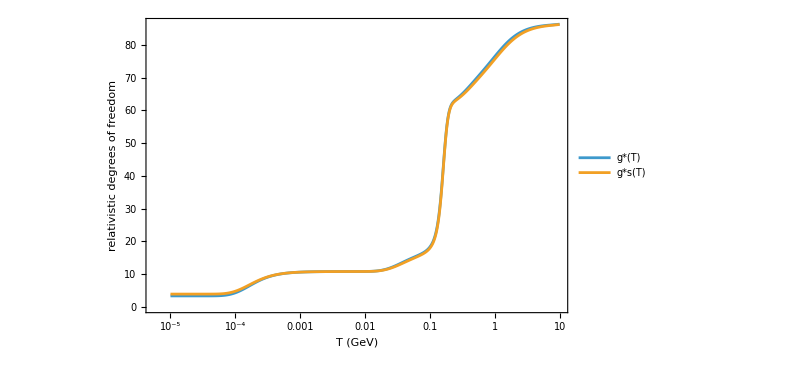

```mathematica
ListLogLinearPlot[Transpose[{Exp[rIIlnT], #}] & /@ Transpose[rIIgg], Joined -> True, PlotLegends -> {"g*(T)", "g*s(T)"}, Frame -> True,
 FrameLabel -> {"T (GeV)", "relativistic degrees of freedom"}, ImageSize -> 600]
```

### 22.4 The late universe: an accurate analytic solution, the age, and the radion today

Below about 1 MeV the brane contains photons and three neutrino species (Ω_r from T_CMB = 2.7255 K and N_eff = 3.044), matter (Ω_m = 0.315, of which the cold dark matter would be dirac16complex if it is the dark matter) and Λ4 (Ω_Λ = 1 − Ω_m − Ω_r), with H0 = 67.4 km/s/Mpc (Planck 2018). The Friedmann equation Ha = H0 (Ω_r a⁻⁴ + Ω_m a⁻.b3 + Ω_Λ)^(1/2) has two exact solutions for two components:

t_rm(a) = (2/(3H0 Ω_m.b2)) [(Ω_m a − 2Ω_r) (Ω_r + Ω_m a)^(1/2) + 2Ω_r^(3/2)]   (radiation + matter),

t_mΛ(a) = (2/(3H0 Ω_Λ^(1/2))) arcsinh((Ω_Λ/Ω_m)^(1/2) a^(3/2))   (matter + Λ),

and the composite t(a) = t_rm(a) + t_mΛ(a) − t_m(a), t_m = (2/(3H0 Ω_m^(1/2))) a^(3/2), is accurate to 2.2 × 10⁻⁴ at every time (the error is the product of the small radiation and Λ corrections). The age is 13.79 Gyr. During this regime the radion sits at β_eq = [Λ4 + κ f_W/V⊥ + (κ/2)(ϵ − 3pa) + κ pb − 12α_2 Ha.b2(Ha′ + Ha.b2)]/(3 m_r.b2) (section 20.3) — of order H0.b2/m_r.b2 ≈ 10⁻⁸⁶ without brane tension, f_W/(3 M_Pl.b2 m_r.b2) ≈ 6 × 10⁻.b2⁴ with f_W = M8⁴ (m_r = 10 GeV) — so G4 = G8/V⊥ does not change; the Gauss–Bonnet and cubic corrections are α_2 H0.b2 ≈ 2 × 10⁻⁹.b2 and α_3 H0⁴ ≈ 4 × 10⁻.b9⁹⁰ (α_2 = 1/M8.b2, α_3 = 10⁻⁶/M8⁴).

```mathematica
rIImpc = 3.0856775814913673 10^19; rIIgyr = 3.15576 10^16; rIIH0s = 67.4/rIImpc; rIIH0g = rIIH0s rIIhbar;
rIIrhoc = 3 rIIH0g^2 rIIMPl^2; rIITcmb = 2.7255 8.617333262 10^-14;
rIIOg = (Pi^2/15) rIITcmb^4/rIIrhoc; rIIOr = rIIOg (1 + 7/8 (4/11)^(4/3) 3.044); rIIOm = 0.315; rIIOL = 1 - rIIOm - rIIOr;
rIIH[a_] := rIIH0s Sqrt[rIIOr/a^4 + rIIOm/a^3 + rIIOL];
rIIage = NIntegrate[1/(a rIIH[a]), {a, 0, 1}, PrecisionGoal -> 12, MaxRecursion -> 30]/rIIgyr;
check["age of the universe from the brane Friedmann equation: 13.79 Gyr (Planck 2018: 13.787 +- 0.020)", Abs[rIIage - 13.79] < 0.02]
rIIt[a_] := NIntegrate[1/(xa rIIH[xa]), {xa, 0, a}, PrecisionGoal -> 12, MaxRecursion -> 30];
rIItrm[a_] := 2/(3 rIIH0s rIIOm^2) ((rIIOm a - 2 rIIOr) Sqrt[rIIOr + rIIOm a] + 2 rIIOr^(3/2));
rIItmL[a_] := 2/(3 rIIH0s Sqrt[rIIOL]) ArcSinh[Sqrt[rIIOL/rIIOm] a^(3/2)]; rIItm[a_] := 2/(3 rIIH0s Sqrt[rIIOm]) a^(3/2);
rIIcomp = Table[Abs[(rIItrm[a] + rIItmL[a] - rIItm[a])/rIIt[a] - 1], {a, 10^Range[-8, 0.5, 0.25]}];
check["composite analytic solution t(a) = t_rm(a) + t_mLambda(a) - t_m(a) accurate to < 3 10^-4 for 10^-8 <= a <= 10^0.5", Max[rIIcomp] < 3 10^-4]
{"Omega_r, Omega_Lambda, z_eq, age (Gyr)" -> {rIIOr, rIIOL, rIIOm/rIIOr - 1, rIIage}, "max error of the composite solution" -> Max[rIIcomp],
 "radion displacement today (m_r = 10 GeV): Lambda4 + matter, tension f_W = M8^4" -> {(3 rIIH0g^2 rIIOL + 1.5 rIIH0g^2 rIIOm)/(3 100.), (rIIM8^4/rIIMPl^2)/(3 100.)},
 "alpha2 H0^2, alpha3 H0^4" -> {rIIH0g^2/rIIM8^2, 10^-6 rIIH0g^4/rIIM8^4}}
```

age of the universe from the brane Friedmann equation: 13.79 Gyr (Planck 2018: 13.787 +- 0.020)→True

composite analytic solution t(a) = t_rm(a) + t_mLambda(a) - t_m(a) accurate to < 3 10^-4 for 10^-8 <= a <= 10^0.5→True

{Omega_r, Omega_Lambda, z_eq, age (Gyr)→{0.0000920958,0.684908,3419.35,13.7907},max error of the composite solution→0.000220157,radion displacement today (m_r = 10 GeV): Lambda4 + matter, tension f_W = M8^4→{1.7413×10^-86,5.62187×10^-24},alpha2 H0^2, alpha3 H0^4→{2.06705×10^-92,4.27268×10^-190}}

## 23. Regime III: the far future

### 23.1 The de Sitter attractor

Once matter has diluted, Λ4 dominates and ordinary space approaches de Sitter expansion with H∞ = H0 Ω_Λ^(1/2) (1.81 × 10⁻.b9⁸ s⁻.b9, Gibbons–Hawking temperature H∞/(2π) ≈ 2.2 × 10⁻.b3⁰ K). For matter + Λ the solution is exact,

a(t) = (Ω_m/Ω_Λ)^(1/3) sinh^(2/3)(3H∞t/2),   Ha(t) = H∞ coth(3H∞t/2) → H∞ + 2H∞ e^(−3H∞t),

and it agrees with the full solution (radiation included) to 10⁻⁴ already at a = 3. Pairs of dirac16complex are created with the Fermi–Dirac occupation 1/(e^(2πM/H∞) + 1) of section 14.5; 2πM/H∞ ≈ 5 × 10.b3.b3 for M = 1 eV, so none are.

```mathematica
rIIIH = rIIH0s Sqrt[rIIOL];
check["far future: Ha(t) = H_inf Coth[3 H_inf t/2] agrees with the full brane solution at a = 3 and a = 10 to 10^-4",
  AllTrue[{3, 10}, Abs[rIIIH Coth[3/2 rIIIH rIIt[#]]/rIIH[#] - 1] < 10^-4 &]]
{"H_inf (1/s, GeV), T_GH (K)" -> {rIIIH, rIIIH rIIhbar, rIIIH rIIhbar/(2 Pi)/(8.617333262 10^-14)}, "2 Pi M/H_inf for M = 1 eV, 1 GeV" -> {2 Pi 10^-9/(rIIIH rIIhbar), 2 Pi/(rIIIH rIIhbar)}}
```

far future: Ha(t) = H_inf Coth[3 H_inf t/2] agrees with the full brane solution at a = 3 and a = 10 to 10^-4→True

{H_inf (1/s, GeV), T_GH (K)→{1.8077×10^-18,1.18985×10^-42,2.19755×10^-30},2 Pi M/H_inf for M = 1 eV, 1 GeV→{5.28067×10^33,5.28067×10^42}}

### 23.2 The radion in de Sitter: Gauss–Bonnet corrections and relaxation

Linearize the full Einstein–Lovelock equations (with U = (K_U/2)β.b2, κK_U = 12m_r.b2) around Ha = H, Hb = 0, β = β_eq, eliminating δHa with the constraint. The radion obeys β″ + γ β′ + m_eff.b2 (β − β_eq) = 0 with (for β_eq → 0)

γ/(3H) = (1 − 16α_2H.b2 + 48α_2.b2H⁴ − 48α_3H⁴ + 512α_2.b3H⁶ + 192α_2α_3H⁶ − 1024α_2⁴H⁸)/(1 − 4α_2H.b2 + 32α_2.b2H⁴).b2,

m_eff.b2/m_r.b2 = 1/(1 − 4α_2H.b2 + 32α_2.b2H⁴),     3 m_r.b2 β_eq = 3H.b2 − 12α_2H⁴ (+ O(β_eq.b2)).

For α_2 = α_3 = 0: γ = 3H and m_eff = m_r. The radion is stable and relaxes to its shifted equilibrium. A numerical test in units ℓ2 = 1 (Λ = 3 × 10⁻⁴, m_r = 0.1, ξ = 10⁻⁶, start 0.05 above equilibrium) reaches the equilibrium (β_eq, H_eq) of the two algebraic equations 3H.b2 = Λ + 6m_r.b2β.b2 and 3m_r.b2β = 3H.b2 − 12H⁴ to 10⁻⁶. In the physical far future α_2H∞.b2 ≈ 10⁻⁹.b2 and β_eq ≈ H∞.b2/m_r.b2: the auxiliary space is frozen forever.

Without the stabilizing potential the far future would instead be eight-dimensional de Sitter, a = b = e^(Hx0), an exact vacuum solution when 21H.b2 − 420α_2H⁴ + 2520α_3H⁶ = Λ: the auxiliary space would inflate and G4 ∝ b⁻⁴ would fall like e^(−4Hx0), which experiments exclude (|Ġ/G| is less than a few percent of H0).

```mathematica
rIIIeqC = (feTot[1] /. {Ha -> haV, Hb -> hbV}) - 6 m2V beV^2;
rIIIsl = First[Solve[{(feTot[2] /. {Ha -> haV, Hb -> hbV}) == 6 m2V beV^2, (feTot[5] /. {Ha -> haV, Hb -> hbV}) == 6 m2V beV^2 + 3 m2V beV}, {dHa, dHb}]];
rIIIFb = dHb /. rIIIsl;
rIIIbg = {haV -> hS, hbV -> 0, beV -> bqV, lamb -> (lamb /. First[Solve[(rIIIeqC /. {haV -> hS, hbV -> 0, beV -> bqV}) == 0, lamb]])};
rIIIcd = D[rIIIeqC, #] /. rIIIbg & /@ {haV, hbV, beV}; rIIIfd = D[rIIIFb, #] /. rIIIbg & /@ {haV, hbV, beV};
rIIIgam = Simplify[-(rIIIfd[[2]] - rIIIfd[[1]] rIIIcd[[2]]/rIIIcd[[1]])]; rIIImeff = Simplify[-(rIIIfd[[3]] - rIIIfd[[1]] rIIIcd[[3]]/rIIIcd[[1]])];
check["radion in de Sitter: gamma/(3H) and m_eff^2/m_r^2 as in the text (beta_eq -> 0); gamma = 3H and m_eff^2 = m_r^2 for alpha2 = alpha3 = 0",
  Simplify[(rIIIgam /. bqV -> 0)/(3 hS) - (1 - 16 alf[2] hS^2 + 48 alf[2]^2 hS^4 - 48 alf[3] hS^4 + 512 alf[2]^3 hS^6 + 192 alf[2] alf[3] hS^6 - 1024 alf[2]^4 hS^8)/(1 - 4 alf[2] hS^2 + 32 alf[2]^2 hS^4)^2] === 0 &&
  Simplify[(rIIImeff /. bqV -> 0)/m2V - 1/(1 - 4 alf[2] hS^2 + 32 alf[2]^2 hS^4)] === 0 &&
  Simplify[rIIIgam /. {bqV -> 0, alf[2] -> 0, alf[3] -> 0}] === 3 hS && Simplify[rIIImeff /. {bqV -> 0, alf[2] -> 0, alf[3] -> 0}] === m2V]
check["radion equilibrium in de Sitter: 3 m_r^2 beta_eq == 3 H^2 - 12 alpha2 H^4 + O(beta_eq^2)",
  Simplify[(bqV /. Solve[Normal[Series[rIIIFb /. rIIIbg, {bqV, 0, 1}]] == 0, bqV][[1]]) - (3 hS^2 - 12 alf[2] hS^4)/(3 m2V)] === 0]
rIIIlam = 3 10^-4; rIIImr = 1/10;
rIIIrhs[tt_?NumericQ, yy_?VectorQ] := Module[{ha, hb, la, lb, kU, d}, {ha, hb, la, lb} = yy; kU = 6 rIIImr^2 lb^2;
   d = rIsolve2[rIlinMf[ha, hb], -rIlinBf[ha, hb] + {rIIIlam + kU, rIIIlam + kU + 3 rIIImr^2 lb}]; {d[[1]], d[[2]], ha, hb}];
rIIIeqs = FindRoot[{3 rIIIhh^2 == rIIIlam + 6 rIIImr^2 rIIIbb^2, 3 rIIImr^2 rIIIbb == 3 rIIIhh^2 - 12 rIIIhh^4}, {{rIIIbb, 1/100}, {rIIIhh, 1/100}}, WorkingPrecision -> 30];
rIIIb0 = (rIIIbb /. rIIIeqs) + 1/20;
rIIIds = NDSolveValue[{rIIIyD'[tt] == rIIIrhs[tt, rIIIyD[tt]], rIIIyD[0] == N[{Sqrt[(rIIIlam + 6 rIIImr^2 rIIIb0^2)/3], 0, 0, rIIIb0}]}, rIIIyD, {tt, 0, 3000},
    Method -> {"ExplicitRungeKutta", "DifferenceOrder" -> 8, "StiffnessTest" -> False}, PrecisionGoal -> 11, AccuracyGoal -> 14, MaxSteps -> 10^7, MaxStepSize -> 1];
check["the radion relaxes to the equilibrium of the two algebraic equations: beta(3000) to 10^-6, Ha(3000) to 10^-8 (relative)",
  Abs[rIIIds[3000][[4]]/(rIIIbb /. rIIIeqs) - 1] < 10^-6 && Abs[rIIIds[3000][[1]]/(rIIIhh /. rIIIeqs) - 1] < 10^-8]
rIIIds8 = Expand[feTot[1] /. {Ha -> h8, Hb -> h8}];
check["eight-dimensional de Sitter (no stabilizer): all three equations read 21 H^2 - 420 alpha2 H^4 + 2520 alpha3 H^6 == Lambda",
  Expand[rIIIds8 - (21 h8^2 - 420 alf[2] h8^4 + 2520 alf[3] h8^6 - lamb)] === 0 &&
  AllTrue[{feTot[2], feTot[5]}, Expand[(# /. {Ha -> h8, Hb -> h8, dHa -> 0, dHb -> 0}) - rIIIds8] === 0 &]]
{"gamma/(3H), m_eff^2/m_r^2 (beta_eq -> 0)" -> {Factor[(rIIIgam /. bqV -> 0)/(3 hS)], Factor[(rIIImeff /. bqV -> 0)/m2V]},
 "de Sitter test: beta(3000), Ha(3000), beta_eq, H_eq" -> {rIIIds[3000][[4]], rIIIds[3000][[1]], rIIIbb /. rIIIeqs, rIIIhh /. rIIIeqs}}
```

radion in de Sitter: gamma/(3H) and m_eff^2/m_r^2 as in the text (beta_eq -> 0); gamma = 3H and m_eff^2 = m_r^2 for alpha2 = alpha3 = 0→True

radion equilibrium in de Sitter: 3 m_r^2 beta_eq == 3 H^2 - 12 alpha2 H^4 + O(beta_eq^2)→True

the radion relaxes to the equilibrium of the two algebraic equations: beta(3000) to 10^-6, Ha(3000) to 10^-8 (relative)→True

eight-dimensional de Sitter (no stabilizer): all three equations read 21 H^2 - 420 alpha2 H^4 + 2520 alpha3 H^6 == Lambda→True

{gamma/(3H), m_eff^2/m_r^2 (beta_eq -> 0)→{-((-1+16 hS^2 alf[2]-48 hS^4 alf[2]^2-512 hS^6 alf[2]^3+1024 hS^8 alf[2]^4+48 hS^4 alf[3]-192 hS^6 alf[2] alf[3])/(1-4 hS^2 alf[2]+32 hS^4 alf[2]^2)^2),1/(1-4 hS^2 alf[2]+32 hS^4 alf[2]^2)},de Sitter test: beta(3000), Ha(3000), beta_eq, H_eq→{0.0102041,0.0101036,0.0102040780874305320164711030853,0.0101035866993997532026732842893}}

### 23.3 The size of every interaction in the three regimes

The first table gives, at four points of the coupled primordial solution of section 21.3, the share of each term of the 00 equation: its size (S_1, S_2, S_3 of section 21.3 for the Einstein, Gauss–Bonnet and cubic terms, κϵ for the dirac16complex gas) divided by the sum of the four sizes. The second table collects, for each term of the action of section 20.1, its weight in the field equations of each regime, computed in sections 21–23 (M8 = 10 TeV, α_2 = 1/M8.b2, α_3 = 10⁻⁶/M8⁴, m_r = 10 GeV, f_W = M8⁴; "estimate" marks an order-of-magnitude statement).

```mathematica
rIIIshare[h_] := With[{sz = rIstate[h]["S"]}, sz/Total[sz]];
rIIIbudget = {{"regime I: cubic (Ha = 3 10^5)", Sequence @@ rIIIshare[3 10^5]}, {"regime I: Gauss-Bonnet (Ha = 30)", Sequence @@ rIIIshare[30]},
   {"regime I: Einstein (Ha = 10^-2)", Sequence @@ rIIIshare[10^-2]}, {"regime I: near the singularity (Ha = 10^15)", Sequence @@ rIIIshare[10^15]}};
check["the shares of the four terms of the 00 equation: Einstein > 0.99 at Ha = 10^-2, Gauss-Bonnet > 0.9 at Ha = 30, Gauss-Bonnet and cubic about 1/2 each at Ha = 3 10^5, gas > 0.1 at Ha = 10^15",
  rIIIbudget[[3, 2]] > 0.99 && rIIIbudget[[2, 3]] > 0.9 && Abs[rIIIbudget[[1, 3]] - 1/2] < 0.01 && Abs[rIIIbudget[[1, 4]] - 1/2] < 0.01 && rIIIbudget[[4, 5]] > 0.1]
Grid[Prepend[Map[If[NumberQ[#], NumberForm[#, 4], #] &, rIIIbudget, {2}], {"", "Einstein S_1", "Gauss-Bonnet S_2", "cubic S_3", "dirac16complex gas"}], Frame -> All]
{"shares (Einstein, Gauss-Bonnet, cubic, gas) at Ha = 3 10^5, 30, 10^-2, 10^15" -> rIIIbudget[[All, 2 ;; 5]]}
```

the shares of the four terms of the 00 equation: Einstein > 0.99 at Ha = 10^-2, Gauss-Bonnet > 0.9 at Ha = 30, Gauss-Bonnet and cubic about 1/2 each at Ha = 3 10^5, gas > 0.1 at Ha = 10^15→True

| Einstein S_1 | Gauss-Bonnet S_2 | cubic S_3 | dirac16complex gas
regime I: cubic (Ha = 3 10^5) | 5.73×10^-10 | 0.5011 | 0.4977 | 0.001189
regime I: Gauss-Bonnet (Ha = 30) | 0.0002353 | 0.9988 | 0.0009644 | 1.845×10^-7
regime I: Einstein (Ha = 10^-2) | 0.9995 | 0.000516 | 6.273×10^-14 | 0.00002832
regime I: near the singularity (Ha = 10^15) | 2.296×10^-19 | 0.5 | 0.2778 | 0.2222

{shares (Einstein, Gauss-Bonnet, cubic, gas) at Ha = 3 10^5, 30, 10^-2, 10^15→{{5.73006×10^-10,0.501139,0.497672,0.00118877},{0.000235349,0.9988,0.000964404,1.84503×10^-7},{0.999456,0.000515986,6.27258×10^-14,0.0000283202},{2.29639×10^-19,0.5,0.277778,0.222222}}}

```mathematica
Grid[{{"term of the action (section 20.1)", "regime I (primordial)", "regime II (today)", "regime III (far future)"},
  {"S_0: Lambda4/(3 H^2)", "~ 10^-92 (Lambda l2^2)", N[rIIOL, 4], "-> 1"},
  {"S_1: Einstein term", "dominant for tau >> l2", "dominant (four-dimensional Friedmann equations)", "dominant"},
  {"S_2: alpha2 H^2", "dominant for 10^-3 l2 < tau < l2", N[rIIH0g^2/rIIM8^2, 3], N[(rIIIH rIIhbar)^2/rIIM8^2, 3]},
  {"S_3: alpha3 H^4", "dominant for tau < 10^-3 l2", N[10^-6 rIIH0g^4/rIIM8^4, 3], N[10^-6 (rIIIH rIIhbar)^4/rIIM8^4, 3]},
  {"S_psi: dirac16complex (gas; matter)", "gas: first table; dominant near tau = 0", "Omega_m = 0.315 (Omega_c = 0.264 if it is the dark matter)", "-> 0 like e^(-3 H t)"},
  {"S_m: m/H", "<< 1 (massless gas)", ">> 1 (cold matter)", ">> 1"},
  {"S_self: g_r n^(6/7) ~ (k_phys/M8)^6 (estimate)", "< 1 below the eight-dimensional Planck scale", "negligible", "negligible"},
  {"S_U: radion displacement beta", "catches b when H ~ m_r, then oscillates", N[(3 rIIH0g^2 rIIOL + 1.5 rIIH0g^2 rIIOm)/(3 100.), 3], N[(rIIIH rIIhbar)^2/100., 3]},
  {"S_f: brane tension kappa f_W/(3 H^2 V_perp)", N[rIIM8^2/(3 rIIMPl^2), 3], "part of Lambda4", "part of Lambda4"},
  {"S_SM: brane plasma", N[rIbrane, 3], N[rIIOr, 3], "-> 0 like e^(-4 H t)"},
  {"S_P: portals (estimate)", "negligible (on the brane)", "production of dirac16complex (freeze-in)", "negligible"},
  {"L_phiW: radion-brane coupling", "radion not yet caught", Row[{"reheating, T_RH = ", NumberForm[rIITRH, 3], " GeV (m_r = 10 GeV)"}], "-"},
  {"pair creation 2 Pi M/H (M = 1 eV)", "order 1 (Planckian times)", N[2 Pi 10^-9/rIIH0g, 3], N[2 Pi 10^-9/(rIIIH rIIhbar), 3]}}, Frame -> All]
```

term of the action (section 20.1) | regime I (primordial) | regime II (today) | regime III (far future)
S_0: Lambda4/(3 H^2) | ~ 10^-92 (Lambda l2^2) | 0.684908 | -> 1
S_1: Einstein term | dominant for tau >> l2 | dominant (four-dimensional Friedmann equations) | dominant
S_2: alpha2 H^2 | dominant for 10^-3 l2 < tau < l2 | 2.06705×10^-92 | 1.41574×10^-92
S_3: alpha3 H^4 | dominant for tau < 10^-3 l2 | 4.27268×10^-190 | 2.00431×10^-190
S_psi: dirac16complex (gas; matter) | gas: first table; dominant near tau = 0 | Omega_m = 0.315 (Omega_c = 0.264 if it is the dark matter) | -> 0 like e^(-3 H t)
S_m: m/H | << 1 (massless gas) | >> 1 (cold matter) | >> 1
S_self: g_r n^(6/7) ~ (k_phys/M8)^6 (estimate) | < 1 below the eight-dimensional Planck scale | negligible | negligible
S_U: radion displacement beta | catches b when H ~ m_r, then oscillates | 1.7413×10^-86 | 1.41574×10^-86
S_f: brane tension kappa f_W/(3 H^2 V_perp) | 5.62187×10^-30 | part of Lambda4 | part of Lambda4
S_SM: brane plasma | 1.97436×10^-28 | 0.0000920958 | -> 0 like e^(-4 H t)
S_P: portals (estimate) | negligible (on the brane) | production of dirac16complex (freeze-in) | negligible
L_phiW: radion-brane coupling | radion not yet caught | reheating, T_RH = 1.01×10^-9 GeV (m_r = 10 GeV) | -
pair creation 2 Pi M/H (M = 1 eV) | order 1 (Planckian times) | 4.37023×10^33 | 5.28067×10^33

## 24. dirac16complex as dark matter and dark energy

About section 24. Section 24 was appended on 27 October 2026. The notebook as it was before (sections 0–23, with the summary of all checks numbered 24; evaluated) is kept in the workspace as backups/7+1_2026-10-27_before_dark.nb (excluded from the repository by .gitignore).

The question. Can the field dirac16complex be the dark matter of the universe, and can it be the dark energy? This section answers on the basis of the accurate approximate solutions of sections 21–23 (the three gravity regimes), the couplings of sections 8 and 15–20, and present observational data. Every statement is marked DERIVED (an exact consequence of the field equations of the model, checked below), ESTIMATE (an order-of-magnitude statement whose assumptions are stated), or OPEN (not decided by the model). Physical parameters as in section 22: M8 = 10 TeV (κ = 8πG8 = M8⁻⁶), reduced M_Pl = 2.435 × 10.b9⁸ GeV, V⊥ = M_Pl.b2/M8⁶, m_r = 10 GeV; the mass m of dirac16complex is free. Coordinates as everywhere: x0 time (the octonion unit), x1, x2, x3 ordinary space, x4 … x7 auxiliary space; η17 = diag(+1, −1, …, −1) is simply the squares of the octonion basis, and xAct declares the spacetime with the signature list {7, 1, 0} (seven space-like and one time-like dimension).

### 24.1 What the observations require

Data used (as reported by the collaborations; the confidence levels are theirs):

Planck 2018 (Astron. Astrophys. 641 (2020) A6): Ω_c h.b2 = 0.120 ± 0.001, Ω_b h.b2 = 0.0224 ± 0.0001, H0 = 67.4 ± 0.5 km/s/Mpc, Ω_m = 0.315 ± 0.007.

DESI DR2 (DESI Collaboration, arXiv:2503.14738): the evolving dark energy w(a) = w0 + wa (1 − a) with w0 > −1, wa < 0 is preferred over a cosmological constant at 3.1σ (DESI BAO + CMB) and at 2.8σ to 4.2σ when supernovae are added; with Planck PR4 + ACT DR6 + DES-Y5 supernovae, w0 = −0.753 ± 0.056, wa = −0.84 (+0.23, −0.20), 4.2σ (Garcia-Quintero et al., arXiv:2504.18464).

LZ, 4.2 tonne-years (LZ Collaboration, arXiv:2410.17036): spin-independent WIMP–nucleon cross section below 2.2 × 10⁻⁴⁸ cm.b2 at 40 GeV (90% CL).

Bullet Cluster (Randall et al., ApJ 679 (2008) 1173): self-interaction cross section per mass σ/m < 1.25 cm.b2/g (68% CL), < 0.7 cm.b2/g with equal mass-to-light ratios.

Lyman-α forest (Iršič et al., Phys. Rev. D 109 (2024) 043511): the mass of a thermal-relic warm dark-matter particle exceeds 5.7 keV (95% CL). Dark matter produced by decays of particles in equilibrium is warmer than a thermal relic of the same mass and its bound is higher (about 7 keV where the thermal-relic bound is 3 keV: Ballesteros, Garcia and Pierre, JCAP 03 (2021) 101).

Pauli principle in dwarf spheroidal galaxies (Alvey et al., MNRAS 501 (2021) 1188): a fermion with g = 2 internal states is heavier than 0.13 keV (95% CL); the bound scales as g^(−1/4).

X-ray lines (NuSTAR, Roach et al., Phys. Rev. D 107 (2023) 023009): limits on the mixing of sterile neutrinos of 6–40 keV with the active ones, from the line of ν_s → νγ.

Large extra dimensions (Particle Data Group 2024): with M_Pl.b2 = R^n M_D^(n+2) and V = (2πR)^n, colliders exclude M_D below 5.9 to 11.2 TeV for n = 6 to 2 (ATLAS, 139 fb⁻.b9).

The dark matter must have the comoving abundance Y = n/s with

m Y = Ω_c h.b2 (ρ_c/h.b2)/s0,   ρ_c/h.b2 = 3 (100 km/s/Mpc).b2 M_Pl.b2,   s0 = (2π.b2/45) g*s0 T_CMB.b3,   g*s0 = 2 + (21/4)(4/11),

and in the convention of the Particle Data Group the 7+1 model has M_D = (2π)^(4/6) M8 (V⊥ = (2πR)⁴, M_Pl.b2 = V⊥ M8⁶ = R⁴ M_D⁶). The lightest Kaluza–Klein level of dirac16complex is four brane Dirac spinors (section 18), i.e. g = 16 internal states (two spin states, particle and antiparticle, four spinors): its Pauli bound is 0.13 keV × (2/16)^(1/4).

```mathematica
dkOch2 = 0.120; dkh = 0.674; dkOc = dkOch2/dkh^2; dkHbarC = 1.973269804*^-14;          (* hbar c in GeV cm *)
dkRhoc = 3 (100./rIImpc rIIhbar)^2 rIIMPl^2/dkHbarC^3;                                   (* rho_c/h^2 in GeV/cm^3 *)
dkGs0 = 2 + 21/4 (4/11); dks0 = 2 Pi^2/45 dkGs0 rIITcmb^3/dkHbarC^3;                    (* entropy density today, 1/cm^3 *)
dkYm = dkOch2 dkRhoc/dks0;                                                               (* m Y in GeV *)
dkMD = (2 Pi)^(2/3) rIIM8; dkPauli = 0.13 (2/16)^(1/4);                                  (* GeV; keV *)
check["required abundance: m Y = Omega_c h^2 (rho_c/h^2)/s0 = 4.37 10^-10 GeV with rho_c/h^2 = 1.053 10^-5 GeV/cm^3 and s0 = 2891 cm^-3 (to 10^-3)",
  Abs[dkRhoc/1.0534*^-5 - 1] < 10^-3 && Abs[dks0/2891.2 - 1] < 10^-3 && Abs[dkYm/4.372*^-10 - 1] < 10^-3]
check["collider bound: with M_Pl^2 = R^n M_D^(n+2) and V_perp = (2 Pi R)^4 = M_Pl^2/M8^6, M_D = (2 Pi)^(2/3) M8 = 34 TeV, above the strongest bound 11.2 TeV",
  Simplify[((2 Pi)^(2/3) m8S)^6 rRS^4 - m8S^6 (2 Pi rRS)^4] === 0 && dkMD > 11.2*^3]
{"Omega_c, rho_c/h^2 (GeV/cm^3), s0 (1/cm^3), m Y (GeV)" -> {dkOc, dkRhoc, dks0, dkYm}, "M_D (GeV)" -> dkMD,
 "Pauli bound for g = 16 internal states (keV)" -> dkPauli}
```

required abundance: m Y = Omega_c h^2 (rho_c/h^2)/s0 = 4.37 10^-10 GeV with rho_c/h^2 = 1.053 10^-5 GeV/cm^3 and s0 = 2891 cm^-3 (to 10^-3)→True

collider bound: with M_Pl^2 = R^n M_D^(n+2) and V_perp = (2 Pi R)^4 = M_Pl^2/M8^6, M_D = (2 Pi)^(2/3) M8 = 34 TeV, above the strongest bound 11.2 TeV→True

{Omega_c, rho_c/h^2 (GeV/cm^3), s0 (1/cm^3), m Y (GeV)→{0.264157,0.0000105339,2891.28,4.37201×10^-10},M_D (GeV)→34050.2,Pauli bound for g = 16 internal states (keV)→0.0772985}

### 24.2 dirac16complex as cold matter in the solutions of sections 21–23 (DERIVED)

A massive dirac16complex particle with comoving momenta k_a (ordinary space) and k_b (auxiliary space) has the comoving energy ω = (m.b2 + k_a.b2/a.b2 + k_b.b2/b.b2)^(1/2); the stress tensor of section 20.2 (W = ω) gives ϵV = ω, p_a V = k_a.b2/(3a.b2ω), p_b V = k_b.b2/(4b.b2ω), with V = a.b3b⁴. The lightest mode has k_b = 0; once k_a/a ≪ m it is pressureless matter, ϵ ∝ a⁻.b3 at fixed b. Every other Kaluza–Klein level is matter of mass (m.b2 + k_b.b2/b0.b2)^(1/2) with a static pressure p_b along the auxiliary space. Consequences in the three regimes:

Regime I: a bulk gas of dirac16complex dominates near x0 = 0 (a ∝ τ^(3/4), section 21.3) and, without the stabilizing potential, decompactifies the auxiliary space (τHb → 2/5 in the gas-dominated Einstein regime). dirac16complex as dark matter therefore REQUIRES the stabilizer of section 22.1.

Regime II: after the capture of the auxiliary space the frozen auxiliary momenta are Kaluza–Klein masses and the gas is four-dimensional matter, its share of the energy constant (section 22.1). Matter of this kind is exactly the term Ω_c a⁻.b3 of the late-universe solution of section 22.4, so dirac16complex CAN BE the Ω_c of that solution without changing it. Through the radion equation of section 20.3 (κ(ϵ/6 − p_a/2 + p_b/3) with p_a = p_b = 0) it displaces the radion by δβ = κϵ/(6 m_r.b2) = H0.b2 Ω_c/(2 m_r.b2) (κϵ = ρ_DM/M_Pl.b2 = 3H0.b2Ω_c): G4 = G8/V⊥ does not change.

Regime III: with a(t) = (Ω_m/Ω_Λ)^(1/3) sinh^(2/3)(3H∞t/2) (section 23.1), ρ_DM/ρ_Λ = Ω_c a⁻.b3/Ω_Λ = (Ω_c/Ω_m)/sinh.b2(3H∞t/2) → 4 (Ω_c/Ω_m) e^(−3H∞t): the dark matter, like all matter, dilutes away.

```mathematica
dkSt = feStress[Function[{aa, rIIIbb}, Sqrt[mDM^2 + kaP^2/aa^2 + kbP^2/rIIIbb^2]]];
check["a massive dirac16complex particle: eps V == omega, pa V == k_a^2/(3 a^2 omega), pb V == k_b^2/(4 b^2 omega), omega = Sqrt[m^2 + k_a^2/a^2 + k_b^2/b^2]",
  With[{om = Sqrt[mDM^2 + kaP^2/aS^2 + kbP^2/bS^2]}, Simplify[dkSt aS^3 bS^4 - {om, kaP^2/(3 aS^2 om), kbP^2/(4 bS^2 om)}, aS > 0 && bS > 0 && mDM > 0] === {0, 0, 0}]]
check["the lightest mode (k_b = 0) is cold matter: pa/eps == k_a^2/(3 (m^2 a^2 + k_a^2)) -> 0, pb == 0, and eps ~ a^-3 at fixed b for k_a = 0",
  Simplify[(dkSt[[2]]/dkSt[[1]] /. kbP -> 0) - kaP^2/(3 (mDM^2 aS^2 + kaP^2)), aS > 0 && mDM > 0] === 0 && (dkSt[[3]] /. kbP -> 0) === 0 &&
  Simplify[aS D[Log[dkSt[[1]] /. {kaP -> 0, kbP -> 0}], aS], aS > 0 && mDM > 0] === -3]
dkDbeta = rIIH0g^2 dkOc/(2 100.);
check["dark matter displaces the radion today by H0^2 Omega_c/(2 m_r^2) < 10^-80 (m_r = 10 GeV): the four-dimensional Newton constant is constant",
  dkDbeta < 10^-80]
check["regime III: Omega_m a^-3/Omega_Lambda == Csch[3 H t/2]^2 for a = (Omega_m/Omega_Lambda)^(1/3) Sinh[3 H t/2]^(2/3), and -> 4 Exp[-3 H t]",
  Simplify[(omS/olS)/((omS/olS)^(1/3) Sinh[3/2 hS tS]^(2/3))^3 - Csch[3/2 hS tS]^2, omS > 0 && olS > 0 && hS > 0 && tS > 0] === 0 &&
  Limit[Csch[zS]^2 Exp[2 zS], zS -> Infinity] == 4]
{"radion displacement by dark matter today" -> dkDbeta, "gas share after capture (section 22.1) at tau = 10^5, 3 10^5" -> rIIfrVals,
 "without stabilizer (section 21.3): tau Hb at Ha = 10^-14" -> rIlate["tau"] rIlate["Hb"]}
```

a massive dirac16complex particle: eps V == omega, pa V == k_a^2/(3 a^2 omega), pb V == k_b^2/(4 b^2 omega), omega = Sqrt[m^2 + k_a^2/a^2 + k_b^2/b^2]→True

the lightest mode (k_b = 0) is cold matter: pa/eps == k_a^2/(3 (m^2 a^2 + k_a^2)) -> 0, pb == 0, and eps ~ a^-3 at fixed b for k_a = 0→True

dark matter displaces the radion today by H0^2 Omega_c/(2 m_r^2) < 10^-80 (m_r = 10 GeV): the four-dimensional Newton constant is constant→True

regime III: Omega_m a^-3/Omega_Lambda == Csch[3 H t/2]^2 for a = (Omega_m/Omega_Lambda)^(1/3) Sinh[3 H t/2]^(2/3), and -> 4 Exp[-3 H t]→True

{radion displacement by dark matter today→2.73012×10^-87,gas share after capture (section 22.1) at tau = 10^5, 3 10^5→{0.00859579,0.00872803},without stabilizer (section 21.3): tau Hb at Ha = 10^-14→0.399995}

### 24.3 The lightest mode: darkness, collisionlessness and stability (ESTIMATE)

The lightest mode is constant over the auxiliary torus: ψ(x, y) = χ(x)/√V⊥ with canonically normalized four-dimensional fields χ (four brane Dirac spinors, section 18). Every coupling at the brane or in the bulk is therefore diluted by the volume. With couplings of natural size at the eight-dimensional Planck scale — Higgs portal λ_P = c_P/M8⁵, Yukawa portal y = c_y/M8.b2, vector portal G_P = c_V/M8⁶, self-couplings g_r = c_r/M8⁶ (mass dimensions −5, −2, −6, −6) — and V⊥ = M_Pl.b2/M8⁶ the four-dimensional couplings of χ are

λ_eff = λ_P/V⊥ = c_P M8/M_Pl.b2,   y_eff = y/√V⊥ = c_y M8/M_Pl,   G_eff = G_P/V⊥ = c_V/M_Pl.b2,   G_r = g_r/V⊥ = c_r/M_Pl.b2.

Direct detection (Higgs exchange; the operator λ_eff Φ†Φ χ̄χ contains λ_eff v h χ̄χ, the nucleon couples to h with f_N m_N/v, f_N ≈ 0.30): σ_SI = λ_eff.b2 f_N.b2 m_N.b2 μ.b2/(π m_h⁴), μ = m m_N/(m + m_N). Self-interaction (contact): σ = G_r.b2 m.b2/(4π). Stability: through the Yukawa portal χ mixes with the neutrinos by θ = μ_P/m, μ_P = y_eff v/√2 (the portal Dirac mass of section 18.2), and decays like a sterile neutrino:

Γ(χ → νγ) = 9 α G_F.b2 m⁵ sin.b22θ/(1024 π⁴),     Γ(χ → 3ν) = G_F.b2 m⁵ θ.b2/(96 π.b3)     (sin.b22θ ≈ 4θ.b2),

the rates of a Majorana fermion (a Dirac fermion decays half as fast; immaterial for these estimates); Γ(χ → νγ)/Γ(χ → 3ν) = 27α/(8π). The Higgs and vector portals are bilinear in χ and cannot make it decay; without the Yukawa portal χ is absolutely stable. A lifetime longer than the age of the universe is the minimum requirement; searches for the X-ray line of χ → νγ demand far longer lifetimes and only strengthen the conclusions of section 24.4.

```mathematica
check["couplings of the lightest mode: with V_perp = M_Pl^2/M8^6, lambda_P/V_perp == c_P M8/M_Pl^2, y/Sqrt[V_perp] == c_y M8/M_Pl, G_P/V_perp == c_V/M_Pl^2, g_r/V_perp == c_r/M_Pl^2",
  With[{vp = mPlS^2/m8S^6}, Simplify[{(cPS/m8S^5)/vp - cPS m8S/mPlS^2, (cyS/m8S^2)/Sqrt[vp] - cyS m8S/mPlS, (cVS/m8S^6)/vp - cVS/mPlS^2,
     (crS/m8S^6)/vp - crS/mPlS^2}, mPlS > 0 && m8S > 0] === {0, 0, 0, 0}]]
dkLam = rIIM8/rIIMPl^2; dkYeff = rIIM8/rIIMPl; dkGr = 1/rIIMPl^2; dkGeV2g = 1.78266192*^-24;     (* per unit c_P, c_y, c_r; grams per GeV *)
dkSigSI[cpx_, mx_] := With[{mu = mx 0.9383/(mx + 0.9383)}, (cpx dkLam)^2 0.30^2 0.9383^2 mu^2/(Pi mHb^4) dkHbarC^2];    (* cm^2 *)
dkSigM[crx_, mx_] := (crx dkGr)^2 mx/(4 Pi) dkHbarC^2/dkGeV2g;                                                      (* cm^2/g *)
dkCrMax[mx_] := Sqrt[4 Pi 0.7 dkGeV2g/(dkHbarC^2 mx)]/dkGr;
dkMuP[cyx_] := cyx dkYeff vEW/Sqrt[2];
dkTauG[cyx_, mx_] := rIIhbar/(9/137.035999 gFermi^2 mx^5 4 (dkMuP[cyx]/mx)^2/(1024 Pi^4));
dkTau3[cyx_, mx_] := rIIhbar/(gFermi^2 mx^5 (dkMuP[cyx]/mx)^2/(96 Pi^3));
dkAge = rIIage rIIgyr;
dkMmax = (dkTau3[1, 1.]/dkAge)^(1/3);                            (* tau(chi -> 3 nu) = tau(m = 1 GeV)/(c_y^2 m^3) *)
check["natural couplings make the lightest mode dark and collisionless: sigma_SI(c_P = 1, m = 40 GeV) < 10^-50 x (LZ limit 2.2 10^-48 cm^2), sigma/m(c_r = 1, m = 1 GeV) < 10^-70 cm^2/g (Bullet Cluster: 0.7 cm^2/g)",
  dkSigSI[1, 40.] < 10^-50 2.2*^-48 && dkSigM[1, 1.] < 10^-70]
check["stability through the Yukawa portal: for c_y = 1 the lifetime chi -> 3 nu equals the age of the universe at m = 40 MeV; it scales as 1/(c_y^2 m^3), and Gamma(nu gamma)/Gamma(3 nu) == 27 alpha/(8 Pi)",
  0.03 < dkMmax < 0.05 && Abs[dkTau3[1, dkMmax]/dkAge - 1] < 10^-12 && Abs[dkTau3[2, 0.01]/dkTau3[1, 0.01] - 1/4] < 10^-12 &&
  Abs[dkTau3[1, 0.02]/dkTau3[1, 0.01] - 1/8] < 10^-12 &&
  Abs[dkTau3[1, 0.01]/dkTauG[1, 0.01] - 27/(8 Pi 137.035999)] < 10^-12]
{"lambda_eff, y_eff, G_r per unit coupling (GeV^-1, 1, GeV^-2)" -> {dkLam, dkYeff, dkGr}, "sigma_SI (cm^2) at c_P = 1, m = 40 GeV" -> dkSigSI[1, 40.],
 "sigma/m (cm^2/g) at c_r = 1, m = 1 GeV; c_r allowed by the Bullet Cluster at m = 1 GeV" -> {dkSigM[1, 1.], dkCrMax[1.]},
 "portal mass mu_P (GeV) at c_y = 1; lifetimes chi -> nu gamma, chi -> 3 nu (s) at c_y = 1, m = 1 GeV and 10 keV" -> {dkMuP[1], dkTauG[1, 1.], dkTau3[1, 1.], dkTauG[1, 10^-5], dkTau3[1, 10^-5]},
 "largest m (GeV) with lifetime > age for c_y = 1" -> dkMmax}
```

couplings of the lightest mode: with V_perp = M_Pl^2/M8^6, lambda_P/V_perp == c_P M8/M_Pl^2, y/Sqrt[V_perp] == c_y M8/M_Pl, G_P/V_perp == c_V/M_Pl^2, g_r/V_perp == c_r/M_Pl^2→True

natural couplings make the lightest mode dark and collisionless: sigma_SI(c_P = 1, m = 40 GeV) < 10^-50 x (LZ limit 2.2 10^-48 cm^2), sigma/m(c_r = 1, m = 1 GeV) < 10^-70 cm^2/g (Bullet Cluster: 0.7 cm^2/g)→True

stability through the Yukawa portal: for c_y = 1 the lifetime chi -> 3 nu equals the age of the universe at m = 40 MeV; it scales as 1/(c_y^2 m^3), and Gamma(nu gamma)/Gamma(3 nu) == 27 alpha/(8 Pi)→True

{lambda_eff, y_eff, G_r per unit coupling (GeV^-1, 1, GeV^-2)→{1.68656×10^-33,4.10678×10^-15,1.68656×10^-37},sigma_SI (cm^2) at c_P = 1, m = 40 GeV→9.55608×10^-104,sigma/m (cm^2/g) at c_r = 1, m = 1 GeV; c_r allowed by the Bullet Cluster at m = 1 GeV→{4.94423×10^-79,1.18987×10^39},portal mass mu_P (GeV) at c_y = 1; lifetimes chi -> nu gamma, chi -> 3 nu (s) at c_y = 1, m = 1 GeV and 10 keV→{7.15004×10^-13,3.59336×10^15,2.81702×10^13,3.59336×10^30,2.81702×10^28},largest m (GeV) with lifetime > age for c_y = 1→0.0401513}

### 24.4 The abundance (ESTIMATE; the outcome is OPEN)

From the solutions of sections 21–22: overproduction. The minimal model makes far too much dirac16complex, not too little:

The primordial gas (sections 21.3 and 22.1). After capture the gas carries the fraction f = 0.0087 of the energy and the radion the rest (for the normalization of section 21.3; f scales with it). Even if the radion energy all became brane radiation at T_RH, the gas-to-radiation ratio f/(1 − f) would have to equal ρ_DM/ρ_rad = (4/3) m Y/T_RH (ρ_rad/s = 3T/4); it exceeds it by O = (f/(1 − f)) T_RH/((4/3) m Y) = 1.5 × 10⁷ (T_RH/GeV), i.e. 6 × 10⁴ even for the lowest T_RH = 4 MeV allowed by nucleosynthesis.

Radion decay (section 22.2). The radion does NOT become brane radiation: it decays 1.3 × 10.b9.b3 times faster into Kaluza–Klein pairs of dirac16complex (if 2m < m_r) than into brane fields. Without a later dilution the universe after the radion decay is made of dirac16complex, with a brane share of only Γ_brane/Γ_bulk ≈ 8 × 10⁻.b9⁴ — the opposite of the observed ratio.

Both results mean that dirac16complex as dark matter needs the dilution and reheating that the moduli problem already needs (section 22.2), at T_RH below the normalcy temperature T* = (M8⁶/M_Pl)^(1/5) = 13.3 GeV. After it the abundance is set by the portals. With instantaneous reheating, production by decays of Higgs bosons in equilibrium below T_RH carries the factor

S(x) = (2/(3π)) ∫_x^∞ t.b3 K_1(t) dt,   x = m_h/T_RH   (S(0) = 1 because ∫_0^∞ t.b3 K_1(t) dt = 3π/2;  S = 0.0078 at T_RH = T*),

and the freeze-in yield of a particle made in h decays with partial width Γ is Y = (135/(8π.b3·1.66)) (M_Pl^(unreduced)/(g*^(3/2) m_h.b2)) Γ S (Hall, Jedamzik, March-Russell and West, JHEP 03 (2010) 080; M_Pl^(unreduced) = 1.221 × 10.b9⁹ GeV, g* = 106.75; below the electroweak bosons g* = 86.25, so for T_RH < m_W this understates Y by at most (106.75/86.25)^(3/2) = 1.4). Production by other processes adds to this; the estimates below are therefore lower bounds on what each portal makes, except for the zero mode alone (an upper bound up to factors of order one, S = 1).

Yukawa portal, the zero mode. Γ(h → ν̄χ) + Γ(h → νχ̄) = y_eff.b2 m_h/(16π) per channel (N channels: three lepton flavours and the brane spinors, N ≤ 12): Y = 9.7 × 10⁻.b9⁸ c_y.b2 N S. The abundance grows like c_y.b2 m while the lifetime τ(χ → 3ν) = K/(c_y.b2 m.b3) falls; both conditions hold together only for m < m* = (Y(c_y = 1) K/(m Y t0))^(1/2) = 1.2 keV (N = 1), 4.2 keV (N = 12), even with S = 1 — below the Lyman-α bound.

Yukawa portal, the Kaluza–Klein tower. Every Kaluza–Klein level couples to the brane with the same strength as the zero mode (section 18.2), so the Higgs decays make the whole tower below m_h: the yield is multiplied by Σ_n (1 − μ_n.b2/m_h.b2).b2 = V⊥ m_h⁴/(192π.b2) = 7.7 × 10.b9⁷ (continuum limit of the lattice sum; for the lattice sum with r_4(k) see the check below), with mean mass (192/315) m_h = 76 GeV: Y_tower = 7.5 c_y.b2 N S and a mass per entropy 571 c_y.b2 N S GeV. At T_RH = T* the tower carries more energy than all the dark matter unless c_y < 9.9 × 10⁻⁶ (N = 1); and through the same mixing its states decay into neutrinos and photons long after nucleosynthesis (τ(χ_n → 3ν) = 2.8 × 10.b9⁰ s/c_y.b2 at μ_n = 10 GeV; other channels shorten it by about ten). The Yukawa portal must therefore be very weak or absent; the precise bound from nucleosynthesis and the CMB is not derived here (OPEN). With c_y < 10⁻⁵ the zero mode lives longer than the universe for m < 86 GeV, and its freeze-in yield is negligible.

Higgs portal. The zero mode gets Y = 2.0 × 10⁻⁴⁹ c_P.b2 S (Γ(h → χχ̄) = (λ_eff v).b2 m_h/(8π)). But the brane breaks the conservation of Kaluza–Klein momentum, so λ_eff v h χ̄_n χ_m couples EVERY pair of levels: Γ(h → χ_n χ̄_m) = (λ_eff v).b2 m_h (1 − (u_n + u_m).b2)^(3/2) (1 − (u_n − u_m).b2)^(1/2)/(8π), u = μ/m_h. With the density of levels dN = V⊥ μ.b3 dμ/(8π.b2) the sum over all pairs is (V⊥ m_h⁴/(8π.b2)).b2 = 3.4 × 10.b3⁸ times I_hp = ∫∫_(u1+u2<1) u1.b3 u2.b3 (1 − (u1 + u2).b2)^(3/2) (1 − (u1 − u2).b2)^(1/2) du1 du2 = 9.5 × 10⁻⁵ (with the mass weight u1 + u2 under the integral: I_hp^E). For four brane spinors the pairs carry 2.5 × 10⁻.b9.b2 c_P.b2 S GeV per entropy (mean pair mass I_hp^E/I_hp = 0.77 m_h): the observed abundance needs c_P = 13 for T_RH ≫ m_h (S → 1) and c_P = 150 at T_RH = T* — two orders of magnitude above natural size; for c_P = 1 it is 4.5 × 10⁻⁵ of the dark matter. Such dark matter would be a population of heavy Kaluza–Klein modes (tens of GeV), whose decays into lighter levels and Standard Model particles through the same portal are not computed here (OPEN).

Vector portal (and any coupling of gravitational strength per pair, G_eff = c_V/M_Pl.b2). Summed over the pairs lighter than T the production rate divided by H is of order c_V.b2 (T/T_V).b9.b9 with T_V = (M8.b9.b2/M_Pl)^(1/11) = 490 GeV (numerical factors omitted; they raise T_V): 5 × 10⁻.b9⁸ at T*. Negligible.

Hence, with couplings of natural size, the minimal model does not produce the observed abundance after the dilution its moduli problem requires: the Yukawa portal must be tiny, the vector portal is negligible, and the Higgs portal falls short by a factor 2 × 10⁴ (it would need c_P ≈ 150). The abundance must come from physics outside the minimal model (OPEN).

```mathematica
dkF = rIIfrVals[[2]]; dkOver[trh_] := (dkF/(1 - dkF)) trh/(4/3 dkYm);
dkFracBulk = rIIgBulk/(rIIgBulk + rIIgam);
check["primordial gas: overabundance O = (f/(1 - f)) T_RH/((4/3) m Y) = 1.5 10^7 T_RH/GeV (6 10^4 at T_RH = 4 MeV)",
  Abs[dkOver[1.]/1.51*^7 - 1] < 0.01 && 5*^4 < dkOver[0.004] < 7*^4]
check["the radion puts more than 1 - 10^-12 of its decays into the bulk (Kaluza-Klein pairs of dirac16complex)", 1 - dkFracBulk < 10^-12]
{"gas share after capture f, overabundance O at T_RH = 1 GeV and 4 MeV" -> {dkF, dkOver[1.], dkOver[0.004]}, "fraction of radion decays into the bulk; brane share" -> {dkFracBulk, rIIgam/rIIgBulk}}
```

primordial gas: overabundance O = (f/(1 - f)) T_RH/((4/3) m Y) = 1.5 10^7 T_RH/GeV (6 10^4 at T_RH = 4 MeV)→True

the radion puts more than 1 - 10^-12 of its decays into the bulk (Kaluza-Klein pairs of dirac16complex)→True

{gas share after capture f, overabundance O at T_RH = 1 GeV and 4 MeV→{0.00872803,1.51044×10^7,60417.7},fraction of radion decays into the bulk; brane share→{1.,7.62134×10^-14}}

```mathematica
dkTstar = (rIIM8^6/rIIMPl)^(1/5);
dkS[x_?NumericQ] := 2/(3 Pi) NIntegrate[tV^3 BesselK[1, tV], {tV, x, Infinity}, PrecisionGoal -> 12, AccuracyGoal -> 30];
dkSstar = dkS[mHb/dkTstar];
check["Boltzmann factor of production below T_RH: Int_0^Infinity t^3 K_1(t) dt == 3 Pi/2 (exact), S(0) = 1, S(m_h/T*) < 10^-2 with T* = (M8^6/M_Pl)^(1/5) = 13.3 GeV",
  Integrate[tV^3 BesselK[1, tV], {tV, 0, Infinity}] == 3 Pi/2 && Abs[dkS[0] - 1] < 10^-10 && dkSstar < 10^-2 && 13 < dkTstar < 14]
dkC = 135/(8 Pi^3 1.66) 1/106.75^(3/2) 1.22091*^19;            (* Y = dkC Gamma S/m_h^2 *)
dkYfi[cyx_, nch_] := dkC nch ((cyx dkYeff)^2 mHb/(16 Pi))/mHb^2;   (* zero mode, Yukawa portal, S = 1 *)
dkYhp[cpx_] := dkC ((cpx dkLam vEW)^2 mHb/(8 Pi))/mHb^2;           (* zero mode, Higgs portal, S = 1 *)
dkK = dkTau3[1, 1.];                                               (* tau(chi -> 3 nu) = dkK/(c_y^2 m^3), m in GeV *)
dkMstar[nch_] := Sqrt[dkYfi[1, nch] dkK/(dkYm dkAge)];
dkCyNeed[mx_, nch_] := Sqrt[dkYm/(mx dkYfi[1, nch])]; dkCyMax[mx_] := Sqrt[dkK/(mx^3 dkAge)];
check["zero mode through the Yukawa portal: the abundance (~ c_y^2 m) and the stability (lifetime ~ 1/(c_y^2 m^3) > age) are compatible only for m < m*, and m* < 5.7 keV (Lyman-alpha) for N = 1 and N = 12 channels even with S = 1",
  dkMstar[1] < 5.7*^-6 && dkMstar[12] < 5.7*^-6 && Abs[dkCyNeed[dkMstar[1], 1]/dkCyMax[dkMstar[1]] - 1] < 10^-9]
dkTowN = rIIVp mHb^4/(192 Pi^2); dkTowE = rIIVp mHb^5/(315 Pi^2);
dkLat = 1 + Total[rIIr4[[1 ;; 10^4]] (1 - Range[10^4]/10.^4)^2]; dkLatE = Total[rIIr4[[1 ;; 10^4]] Sqrt[Range[10^4]/10.^4] (1 - Range[10^4]/10.^4)^2];
check["Kaluza-Klein tower: Sum_n (1 - mu_n^2/m_h^2)^2 -> V_perp m_h^4/(192 Pi^2) and Sum_n mu_n (1 - mu_n^2/m_h^2)^2 -> V_perp m_h^5/(315 Pi^2) (d^4n = 2 Pi^2 |n|^3 d|n|: exact integrals); the lattice sums with r_4(k) for R = 100 equal Pi^2 R^4/12 and 16 Pi^2 R^4/315 to 10^-8",
  Integrate[2 Pi^2 uV^3 (1 - uV^2)^2, {uV, 0, 1}] == Pi^2/12 && Integrate[2 Pi^2 uV^4 (1 - uV^2)^2, {uV, 0, 1}] == 16 Pi^2/315 &&
  Simplify[(Pi^2/12) (mhS rLS/(2 Pi))^4 - rLS^4 mhS^4/(192 Pi^2)] === 0 && Simplify[(16 Pi^2/315) mhS (mhS rLS/(2 Pi))^4 - rLS^4 mhS^5/(315 Pi^2)] === 0 &&
  Abs[dkLat/(Pi^2 10.^8/12) - 1] < 10^-8 && Abs[dkLatE/(16 Pi^2 10.^8/315) - 1] < 10^-8]
dkCyTow = Sqrt[dkYm/(dkYfi[1, 1] dkTowE dkSstar)];
check["Kaluza-Klein tower through the Yukawa portal: 7.7 10^17 states below m_h with mean mass (192/315) m_h; at T_RH = T* it carries more energy than all the dark matter unless c_y < 2 10^-5 (N = 1)",
  Abs[dkTowN/7.688*^17 - 1] < 10^-3 && Abs[dkTowE/(dkTowN 192/315 mHb) - 1] < 10^-12 && dkCyTow < 2*^-5]
dkIhp = NIntegrate[u1V^3 u2V^3 (1 - (u1V + u2V)^2)^(3/2) Sqrt[1 - (u1V - u2V)^2], {u1V, 0, 1}, {u2V, 0, 1 - u1V}, PrecisionGoal -> 10, AccuracyGoal -> 20];
dkIhpE = NIntegrate[(u1V + u2V) u1V^3 u2V^3 (1 - (u1V + u2V)^2)^(3/2) Sqrt[1 - (u1V - u2V)^2], {u1V, 0, 1}, {u2V, 0, 1 - u1V}, PrecisionGoal -> 10, AccuracyGoal -> 20];
dkPairs = (rIIVp mHb^4/(8 Pi^2))^2;
dkRhp[cpx_, nch_, x_] := dkYhp[cpx] nch dkPairs mHb dkIhpE dkS[x];        (* mass of the Kaluza-Klein pairs per entropy, GeV *)
dkCpNeed[x_] := Sqrt[dkYm/dkRhp[1, 4, x]];
check["Higgs portal: the zero mode gets Y < 10^-40 (c_P = 1); the pairs of Kaluza-Klein levels (lambda(1, u1^2, u2^2) == (1 - (u1 + u2)^2)(1 - (u1 - u2)^2)) give the observed abundance only for c_P between 10 and 20 (T_RH >> m_h, S -> 1) or between 100 and 200 (T_RH = T*)",
  dkYhp[1] < 10^-40 && Expand[(1 - u1V^2 - u2V^2)^2 - 4 u1V^2 u2V^2 - (1 - (u1V + u2V)^2) (1 - (u1V - u2V)^2)] === 0 &&
  10 < dkCpNeed[0] < 20 && 100 < dkCpNeed[mHb/dkTstar] < 200]
dkTV = (rIIM8^12/rIIMPl)^(1/11);
check["vector portal: gravitational strength per pair; the production rate of all pairs lighter than T divided by H ~ (T/T_V)^11 with T_V = (M8^12/M_Pl)^(1/11) = 490 GeV is below 10^-17 at T*",
  480 < dkTV < 500 && (dkTstar/dkTV)^11 < 10^-17]
{"T* (GeV), S(m_h/T*)" -> {dkTstar, dkSstar}, "zero mode: Yukawa-portal Y at c_y = 1 (N = 1, S = 1), Higgs-portal Y at c_P = 1 (S = 1)" -> {dkYfi[1, 1], dkYhp[1]},
 "m* (GeV) for N = 1 and N = 12" -> {dkMstar[1], dkMstar[12]}, "c_y needed and allowed at m = 10 keV, 10 MeV" -> {dkCyNeed[10^-5, 1], dkCyMax[10^-5], dkCyNeed[0.01, 1], dkCyMax[0.01]},
 "Kaluza-Klein tower below m_h: number, mass sum (GeV), Y_tower and mass per entropy (GeV) at c_y = 1 (N = 1, S = 1); c_y bound at T*" -> {dkTowN, dkTowE, dkYfi[1, 1] dkTowN, dkYfi[1, 1] dkTowE, dkCyTow},
 "tau(chi_n -> 3 nu) (s) at mu_n = 10 GeV, c_y = 1; largest m (GeV) with tau(chi -> 3 nu) > age for c_y = 10^-5" -> {dkTau3[1, 10.], (dkK/(10^-10 dkAge))^(1/3)},
 "Higgs portal pairs: I_hp, I_hp^E, number of pairs, mass per entropy (GeV) at c_P = 1 (N = 4, S = 1); c_P needed for S = 1 and at T*" -> {dkIhp, dkIhpE, dkPairs, dkRhp[1, 4, 0], dkCpNeed[0], dkCpNeed[mHb/dkTstar]},
 "Higgs portal pairs at c_P = 1, T_RH = T*: fraction of the dark matter" -> dkRhp[1, 4, mHb/dkTstar]/dkYm,
 "vector portal: T_V (GeV), (T*/T_V)^11" -> {dkTV, (dkTstar/dkTV)^11},
 "T_RH (GeV) = 5, 8, 10, T*: S(m_h/T_RH), c_y bound of the tower (N = 1), c_P needed by the Higgs-portal pairs (N = 4)" ->
   Table[{trh, dkS[mHb/trh], Sqrt[dkYm/(dkYfi[1, 1] dkTowE dkS[mHb/trh])], dkCpNeed[mHb/trh]}, {trh, {5., 8., 10., dkTstar}}]}
```

Boltzmann factor of production below T_RH: Int_0^Infinity t^3 K_1(t) dt == 3 Pi/2 (exact), S(0) = 1, S(m_h/T*) < 10^-2 with T* = (M8^6/M_Pl)^(1/5) = 13.3 GeV→True

zero mode through the Yukawa portal: the abundance (~ c_y^2 m) and the stability (lifetime ~ 1/(c_y^2 m^3) > age) are compatible only for m < m*, and m* < 5.7 keV (Lyman-alpha) for N = 1 and N = 12 channels even with S = 1→True

Kaluza-Klein tower: Sum_n (1 - mu_n^2/m_h^2)^2 -> V_perp m_h^4/(192 Pi^2) and Sum_n mu_n (1 - mu_n^2/m_h^2)^2 -> V_perp m_h^5/(315 Pi^2) (d^4n = 2 Pi^2 |n|^3 d|n|: exact integrals); the lattice sums with r_4(k) for R = 100 equal Pi^2 R^4/12 and 16 Pi^2 R^4/315 to 10^-8→True

Kaluza-Klein tower through the Yukawa portal: 7.7 10^17 states below m_h with mean mass (192/315) m_h; at T_RH = T* it carries more energy than all the dark matter unless c_y < 2 10^-5 (N = 1)→True

Higgs portal: the zero mode gets Y < 10^-40 (c_P = 1); the pairs of Kaluza-Klein levels (lambda(1, u1^2, u2^2) == (1 - (u1 + u2)^2)(1 - (u1 - u2)^2)) give the observed abundance only for c_P between 10 and 20 (T_RH >> m_h, S -> 1) or between 100 and 200 (T_RH = T*)→True

vector portal: gravitational strength per pair; the production rate of all pairs lighter than T divided by H ~ (T/T_V)^11 with T_V = (M8^12/M_Pl)^(1/11) = 490 GeV is below 10^-17 at T*→True

{T* (GeV), S(m_h/T*)→{13.2648,0.00784613},zero mode: Yukawa-portal Y at c_y = 1 (N = 1, S = 1), Higgs-portal Y at c_P = 1 (S = 1)→{9.72626×10^-18,1.98895×10^-49},m* (GeV) for N = 1 and N = 12→{1.2×10^-6,4.15693×10^-6},c_y needed and allowed at m = 10 keV, 10 MeV→{2.12015×10^6,254419.,67045.2,8.04544},Kaluza-Klein tower below m_h: number, mass sum (GeV), Y_tower and mass per entropy (GeV) at c_y = 1 (N = 1, S = 1); c_y bound at T*→{7.68802×10^17,5.86691×10^19,7.47756,570.631,9.88178×10^-6},tau(chi_n -> 3 nu) (s) at mu_n = 10 GeV, c_y = 1; largest m (GeV) with tau(chi -> 3 nu) > age for c_y = 10^-5→{2.81702×10^10,86.5034},Higgs portal pairs: I_hp, I_hp^E, number of pairs, mass per entropy (GeV) at c_P = 1 (N = 4, S = 1); c_P needed for S = 1 and at T*→{0.0000953847,0.0000738079,3.40448×10^38,2.50289×10^-12,13.2166,149.208},Higgs portal pairs at c_P = 1, T_RH = T*: fraction of the dark matter→0.0000449176,vector portal: T_V (GeV), (T*/T_V)^11→{492.194,5.44755×10^-18},T_RH (GeV) = 5, 8, 10, T*: S(m_h/T_RH), c_y bound of the tower (N = 1), c_P needed by the Higgs-portal pairs (N = 4)→{{5.,1.2489×10^-8,0.00783249,118265.},{8.,0.0000494402,0.000124487,1879.66},{10.,0.000677581,0.0000336265,507.737},{13.2648,0.00784613,9.88178×10^-6,149.208}}}

### 24.5 dirac16complex and dark energy

Matter cannot be dark energy (DERIVED). Free particles have p_a = −∂_aW/(3a.b2b⁴) ≥ 0 because W decreases with a. The interacting Kohn–Sham matter of section 8 (units m = 1, gS = −10⁵, gV = 10⁴) has, at zero temperature, p = μρ − ϵ with μ = ϵ_F (Hugenholtz–Van Hove, section 8.7), so p = ρ.b2 d(ϵ/ρ)/dρ: the pressure is negative only where the energy per particle decreases with density — below the saturation density, where uniform matter has a higher energy than droplets at saturation in empty space (both have p = 0) and is metastable or, in the spinodal region dp/dρ < 0, unstable. Its most negative equation of state there is w = p/ϵ ≈ −0.058 (at kF ≈ 0.67): nowhere near −1.

A condensate is only a cosmological constant (DERIVED). A Lorentz-invariant condensate of dirac16complex (⟨ψbar ψ⟩ ≠ 0, which the self-couplings of section 15 allow) has T_μν ∝ g_μν, i.e. w = −1 exactly: a contribution to Λ4, not a dynamical dark energy.

Vacuum energy is only a contribution to Λ4 (DERIVED, with an ESTIMATE of its size). The zero-point energy of dirac16complex on the auxiliary torus (periodic boundary conditions) is a Casimir energy. For a field of mass m in eight dimensions with four compact directions of proper size ℓ⊥ = V⊥^(1/4) the four-dimensional vacuum energy per real bosonic degree of freedom is −(2/ℓ⊥⁴) Σ_(n ∈ Z⁴, n ≠ 0) (mℓ⊥/(2π|n|))⁴ K_4(mℓ⊥|n|) → −Γ(4) Z/(π⁴ ℓ⊥⁴) for m → 0, with the Epstein sum Z = Σ_(n ≠ 0) |n|⁻⁸ = 8(1 − 4⁻.b3) ζ(4) ζ(3) (from r_4(k) of section 22.2); a fermion contributes with the opposite sign, and dirac16complex has 16 real degrees of freedom on shell. Massless it gives +6.8 × 10.b3⁴ ρ_Λ; it equals ρ_Λ only for mℓ⊥ = 92.2 (m = 59 MeV), and the graviton (20 degrees of freedom) contributes −8.5 × 10.b3⁴ ρ_Λ. Every such term is constant while b is frozen (w = −1 up to the radion displacement, 10⁻⁸⁶), and they add to Λ + κU0 + κf_W/V⊥: the observed Λ4 needs their sum to cancel to 10⁻.b3⁵ of each — the cosmological-constant problem, not solved by dirac16complex.

The prediction w = −1. With the radion frozen the model predicts w = −1 exactly; the DESI preference for w0 > −1, wa < 0 (2.8σ to 4.2σ), if confirmed, would contradict it whatever dirac16complex is. (The radion, the only scalar of the model, cannot be the dark energy either: with m_r ≫ H0 it is frozen; a radion light enough to roll today would change G4 = G8 e^(−4β)/V⊥ by order one — ESTIMATE.)

```mathematica
dkPE[kf_?NumericQ] := With[{e = eps7[gS0, gV0, kf]}, {fermi7[gS0, gV0, kf] rho7[kf] - e, e}];   (* {p, eps}: p = mu rho - eps with mu = eps_F *)
dkPres[kf_?NumericQ] := dkPE[kf][[1]];
dkWtab = Table[With[{pe = dkPE[kf]}, {kf, pe[[1]], pe[[1]]/pe[[2]]}], {kf, 5/100, 85/100, 1/100}];
dkWmin = Min[dkWtab[[All, 3]]]; dkKmin = dkWtab[[Ordering[dkWtab[[All, 3]], 1][[1]], 1]];
check["Kohn-Sham matter of section 8: p > 0 at low density, p < 0 below saturation, p = 0 at kF0, a spinodal region (dp/dkF < 0) in between, and w = p/eps >= -0.06 everywhere",
  dkWtab[[1, 2]] > 0 && dkPres[N[kF0, 40] - 1/100] < 0 && Abs[dkPres[kF0]] < 10^-20 && AnyTrue[Differences[dkWtab[[All, 2]]], # < 0 &] && -0.06 < dkWmin < -0.04]
dkZ48 = 8 (1 - 4^-3) Zeta[4] Zeta[3];
check["Epstein sum over Z^4 without 0: Sum |n|^-8 == 8 (1 - 4^-3) zeta(4) zeta(3), compared with the shell sum Sum r_4(k)/k^4 to k = 20000 (tail < 3 10^-8)",
  Abs[N[dkZ48, 20] - Total[rIIr4[[1 ;; 20000]]/N[Range[20000]]^4]] < 3*^-8]
dkLp = rIIVp^(1/4); dkRhoL = 3 rIIH0g^2 rIIMPl^2 rIIOL;
dkC0 = Gamma[4]/Pi^4 dkZ48;                                   (* massless, per real degree of freedom, times 1/l^4 *)
dkCas[xx_?NumericQ] := 16 Total[rIIr4[[1 ;; 400]] 2 (xx/(2 Pi Sqrt[N[Range[400]]]))^4 BesselK[4, xx Sqrt[N[Range[400]]]]]/dkLp^4;
dkXL = xxV /. FindRoot[Log[dkCas[xxV]/dkRhoL] == 0, {xxV, 90}];
check["Casimir energy of dirac16complex on the auxiliary torus: massless 16 Gamma(4) Z/(Pi^4 l^4) > 10^34 rho_Lambda, the massive sum -> the massless value for m l -> 0 (to 10^-4), and equals rho_Lambda at m l = 92.2",
  16 dkC0/dkLp^4/dkRhoL > 10^34 && Abs[dkCas[10^-3]/(16 dkC0/dkLp^4) - 1] < 10^-4 && Abs[dkXL - 92.2] < 0.05]
{"w_min of Kohn-Sham matter and its kF (units m = 1); saturation kF0" -> {SetPrecision[dkWmin, MachinePrecision], N[dkKmin], N[kF0]}, "rho_Lambda (GeV^4)" -> dkRhoL,
 "Casimir energy / rho_Lambda: dirac16complex (m = 0), graviton (20 dof)" -> {16 dkC0/dkLp^4/dkRhoL, -20 dkC0/dkLp^4/dkRhoL},
 "m l_perp and m (GeV) at which the dirac16complex Casimir energy equals rho_Lambda" -> {dkXL, dkXL/dkLp},
 "kF, p, w at kF = 0.1, 0.3, 0.5, 0.6, 0.67, 0.7, 0.75 (units m = 1)" -> N[Select[dkWtab, MemberQ[{1/10, 3/10, 1/2, 3/5, 67/100, 7/10, 3/4}, #[[1]]] &]],
 "dirac16complex Casimir energy / rho_Lambda at m l_perp = 1, 10, 30, 60" -> (dkCas[#]/dkRhoL & /@ {1., 10., 30., 60.})}
```

Kohn-Sham matter of section 8: p > 0 at low density, p < 0 below saturation, p = 0 at kF0, a spinodal region (dp/dkF < 0) in between, and w = p/eps >= -0.06 everywhere→True

Epstein sum over Z^4 without 0: Sum |n|^-8 == 8 (1 - 4^-3) zeta(4) zeta(3), compared with the shell sum Sum r_4(k)/k^4 to k = 20000 (tail < 3 10^-8)→True

Casimir energy of dirac16complex on the auxiliary torus: massless 16 Gamma(4) Z/(Pi^4 l^4) > 10^34 rho_Lambda, the massive sum -> the massless value for m l -> 0 (to 10^-4), and equals rho_Lambda at m l = 92.2→True

{w_min of Kohn-Sham matter and its kF (units m = 1); saturation kF0→{-0.058016,0.67,0.756636},rho_Lambda (GeV^4)→2.51827×10^-47,Casimir energy / rho_Lambda: dirac16complex (m = 0), graviton (20 dof)→{6.76246×10^34,-8.45308×10^34},m l_perp and m (GeV) at which the dirac16complex Casimir energy equals rho_Lambda→{92.2262,0.0591024},kF, p, w at kF = 0.1, 0.3, 0.5, 0.6, 0.67, 0.7, 0.75 (units m = 1)→{{0.1,1.08151×10^-14,0.00110188},{0.3,1.87697×10^-10,0.00849359},{0.5,-4.30811×10^-10,-0.000529633},{0.6,-1.02776×10^-7,-0.0359704},{0.67,-3.45482×10^-7,-0.058016},{0.7,-4.10965×10^-7,-0.0516687},{0.75,-1.07135×10^-7,-0.00844608}},dirac16complex Casimir energy / rho_Lambda at m l_perp = 1, 10, 30, 60→{6.0569×10^34,4.19962×10^32,2.46936×10^25,2.30068×10^13}}

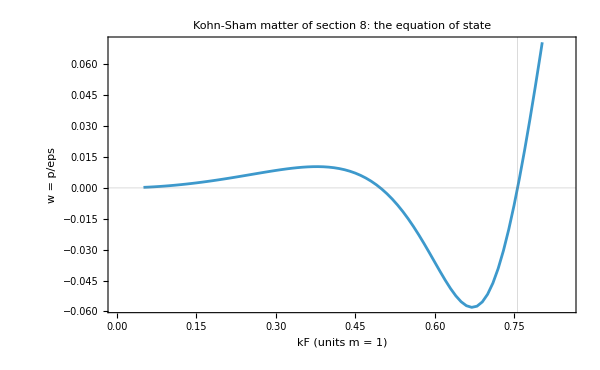

```mathematica
ListPlot[{dkWtab[[All, {1, 3}]]}, Joined -> True, Frame -> True, FrameLabel -> {"kF (units m = 1)", "w = p/eps"}, GridLines -> {{N[kF0]}, {0}},
 PlotLabel -> "Kohn-Sham matter of section 8: the equation of state", ImageSize -> 600]
```

### 24.6 Verdict

The table collects the findings. dirac16complex has every property that the solutions of sections 21–23 and the observations demand of dark matter — it is cold, dark, collisionless, and enters the late-universe solution exactly as Ω_c — provided the auxiliary space is stabilized and the Yukawa portal is very weak or absent. The minimal model does not, however, produce the observed abundance: its primordial gas and its radion make far too much (which the dilution required by the moduli problem must remove), and after that dilution its portals with couplings of natural size make far too little — the Higgs portal would need c_P ≈ 150. The origin of the abundance is therefore OPEN. As dark energy dirac16complex fails: as matter it never has w < −0.06 in a stable state, and as vacuum energy or condensate it is only one more contribution to Λ4, with w = −1 exactly.

```mathematica
Grid[{{"claim", "status", "basis"},
  {"dirac16complex behaves as cold matter (w = 0) and can be Omega_c of the late-universe solution", "DERIVED", "sections 20.2, 22.1, 22.4, 24.2"},
  {Row[{"its effect on the radion is negligible (delta beta = ", ScientificForm[dkDbeta, 2], ")"}], "DERIVED", "sections 20.3, 24.2"},
  {"as dark matter it needs the stabilizing potential (otherwise decompactification)", "DERIVED", "section 21.3"},
  {Row[{"dark: sigma_SI = ", ScientificForm[dkSigSI[1, 40.], 2], " cm^2 << LZ; collisionless: sigma/m = ", ScientificForm[dkSigM[1, 1.], 2], " cm^2/g"}], "ESTIMATE", "volume dilution, section 24.3"},
  {Row[{"stable over the age of the universe if m < ", NumberForm[1000 dkMmax, 2], " MeV c_y^(-2/3) (absolutely stable without the Yukawa portal)"}], "ESTIMATE", "section 24.3"},
  {Row[{"mass window: m > 5.7 keV (Lyman-alpha), > ", NumberForm[dkPauli, 2], " keV (Pauli, g = 16)"}], "data", "section 24.1"},
  {Row[{"primordial gas and radion decay overproduce dirac16complex (O = ", ScientificForm[dkOver[1.], 2], " T_RH/GeV; brane share ", ScientificForm[rIIgam/rIIgBulk, 2], ")"}], "DERIVED from the solutions; ESTIMATE for O", "sections 21.3, 22.1, 22.2, 24.4"},
  {Row[{"Yukawa portal: the Kaluza-Klein tower is overproduced unless c_y < ", ScientificForm[dkCyTow, 2]}], "ESTIMATE", "section 24.4"},
  {Row[{"Higgs portal: the observed abundance needs c_P = ", NumberForm[dkCpNeed[mHb/dkTstar], 3], " (T_RH = T*)"}], "ESTIMATE", "section 24.4"},
  {"observed abundance m Y = 4.37 10^-10 GeV produced by the minimal model with natural couplings", "OPEN (not produced)", "section 24.4"},
  {"dirac16complex matter as dark energy", "excluded (DERIVED: w >= -0.06; p < 0 only where uniform matter is unstable or metastable)", "sections 8.7, 24.5"},
  {Row[{"dirac16complex vacuum energy or condensate as dark energy", " (Casimir: ", ScientificForm[16 dkC0/dkLp^4/dkRhoL, 2], " rho_Lambda)"}], "not an explanation (DERIVED: a contribution to Lambda4 with w = -1)", "section 24.5"},
  {"evolving dark energy (DESI DR2: 2.8 to 4.2 sigma)", "in tension with the model (w = -1 exactly)", "section 24.5"}}, Frame -> All, Alignment -> Left]
```

claim | status | basis
dirac16complex behaves as cold matter (w = 0) and can be Omega_c of the late-universe solution | DERIVED | sections 20.2, 22.1, 22.4, 24.2
its effect on the radion is negligible (delta beta = 2.7×10^-87) | DERIVED | sections 20.3, 24.2
as dark matter it needs the stabilizing potential (otherwise decompactification) | DERIVED | section 21.3
dark: sigma_SI = 9.6×10^-104 cm^2 << LZ; collisionless: sigma/m = 4.9×10^-79 cm^2/g | ESTIMATE | volume dilution, section 24.3
stable over the age of the universe if m < 40. MeV c_y^(-2/3) (absolutely stable without the Yukawa portal) | ESTIMATE | section 24.3
mass window: m > 5.7 keV (Lyman-alpha), > 0.077 keV (Pauli, g = 16) | data | section 24.1
primordial gas and radion decay overproduce dirac16complex (O = 1.5×10^7 T_RH/GeV; brane share 7.6×10^-14) | DERIVED from the solutions; ESTIMATE for O | sections 21.3, 22.1, 22.2, 24.4
Yukawa portal: the Kaluza-Klein tower is overproduced unless c_y < 9.9×10^-6 | ESTIMATE | section 24.4
Higgs portal: the observed abundance needs c_P = 149. (T_RH = T*) | ESTIMATE | section 24.4
observed abundance m Y = 4.37 10^-10 GeV produced by the minimal model with natural couplings | OPEN (not produced) | section 24.4
dirac16complex matter as dark energy | excluded (DERIVED: w >= -0.06; p < 0 only where uniform matter is unstable or metastable) | sections 8.7, 24.5
dirac16complex vacuum energy or condensate as dark energy (Casimir: 6.8×10^34 rho_Lambda) | not an explanation (DERIVED: a contribution to Lambda4 with w = -1) | section 24.5
evolving dark energy (DESI DR2: 2.8 to 4.2 sigma) | in tension with the model (w = -1 exactly) | section 24.5

## 25. Summary of all checks (sections 1–24)

The four cells below summarize every check of the notebook after all sections have been evaluated.

```mathematica
Length[checks]
```

419

```mathematica
failedChecks = Keys[Select[checks, ! TrueQ[#] &]]
```

{}

```mathematica
allChecksPassed = AllTrue[Values[checks], TrueQ]
```

True

```mathematica
Grid[Prepend[KeyValueMap[{#1, #2} &, checks], {Style["check", Bold], Style["result", Bold]}], Frame -> All, Alignment -> Left]
```

check | result
4+4: ζ[7] == diag(-1,-1,-1,-1,1,1,1,1) | True
4+4: σ == ζ[1].ζ[2].ζ[3] | True
4+4: (ζ[A].ζ[B] + ζ[B].ζ[A])/2 == -η4488[[A+1,B+1]] ID8 (A,B = 1..7) | True
4+4: -η4488[[A+1,A+1]] ζ[A] == Transpose[ζ[A]] (A = 1..7) | True
4+4: (τ[A].τbar[B] + τ[B].τbar[A])/2 == η4488[[A+1,B+1]] ID8 | True
4+4: (τbar[A].τ[B] + τbar[B].τ[A])/2 == η4488[[A+1,B+1]] ID8 | True
4+4: τ[1].τ[2]...τ[7] == ID8 | True
4+4: σ == τ[1].τ[2].τ[3] == τ[4].τ[5].τ[6].τ[7] | True
4+4: σ commutes with τ[1..3] and anticommutes with τ[4..7]; σ.σ == ID8 | True
4+4: (T16[A].T16[B] + T16[B].T16[A])/2 == η4488[[A+1,B+1]] ID16 | True
4+4: T16[A] real (entries 0, ±1) | True
4+4: T16[8] == diag(-ID8, ID8) | True
4+4: σ16 == diag(-σ, σ) | True
4+4: PL44 + PR44 == ID16, PL44.PL44 == PL44, PR44.PR44 == PR44, PL44.PR44 == 0 | True
4+4: uBasis == evecs/Sqrt[2] from Eigensystem[σ] (the basis of 4+4.nb) | True
4+4: unit == (1,0,0,0,1,0,0,0)/Sqrt[2], σ.unit == unit, unit.unit == 1, unit.σ.unit == 1 | True
4+4 (In[294]): E44inv[h] == (u.σ.u) Transpose[Table[η4488[[B,B]] τ[B-1].u, {B,1,8}]] for h = 1..8 | True
4+4: gridx44 is identical to the split-octonion table printed by 4+4.nb | True
4+4: LS[A] are signed permutation matrices (constants 0, ±1) | True
split: eA[1] is the identity; eA[2..4]^2 == -eA[1]; eA[5..8]^2 == +eA[1] | True
split: x x̄ == N(x) eA[1] with N = η4488 (symbolic) | True
split: N(xy) == N(x) N(y) (symbolic) | True
split: alternative x(xy) == (xx)y and (yx)x == y(xx) (symbolic) | True
split: (eA[1] + eA[5])(eA[1] - eA[5]) == 0 with both factors nonzero: NOT a division algebra | True
τO[A] (A = 1..7): real, antisymmetric, τO[A].τO[A] == -ID8 | True
τO[A] anticommute: τO[A].τO[B] == -τO[B].τO[A] (A != B, A,B = 1..7) | True
mirror of 4+4: (τO[A].τObar[B] + τO[B].τObar[A])/2 == gO[[A+1,B+1]] ID8 | True
mirror of 4+4: (τObar[A].τO[B] + τObar[B].τO[A])/2 == gO[[A+1,B+1]] ID8 | True
mirror of 4+4: τO[1].τO[2]...τO[7] == ID8 | True
mirror of 4+4: τObar[A] == gO.Transpose[τO[A]].gO, as τbar[A] == σ.Transpose[τ[A]].σ | True
τO[4..7] are products of three split τ: τO[4] == τ[5].τ[6].τ[7], τO[5] == -τ[4].τ[6].τ[7], τO[6] == τ[4].τ[5].τ[7], τO[7] == -τ[4].τ[5].τ[6] | True
σ.unit == unit, hence τO[A].unit == τ[A].unit (A = 0..7) | True
EO is orthogonal: EOinv == Transpose[EO] | True
mirror of 4+4.nb In[294]: EOinv == (u.gO.u) Transpose[Table[gO[[B,B]] τO[B-1].u, {B,1,8}]] | True
EO == η4488.E44[hUSE]: the two vielbeins differ only by the signs of rows 5..8 | True
gridO equals the octonion table computed independently in Python | True
LO[A] are signed permutation matrices (all multiplication constants are 0, ±1) | True
oMul reproduces gridO on all 64 pairs of basis units | True
e[0] is a two-sided identity | True
e[i] e[i] == -e[0] (i = 1..7) | True
e[i] e[j] == -e[j] e[i] (i != j, i,j = 1..7): non-commutative | True
7 Fano lines; every pair of distinct imaginary units lies on exactly one line | True
each oriented line (a,b,c) is cyclic: e[a]e[b] == e[c], e[b]e[c] == e[a], e[c]e[a] == e[b] | True
each line spans a quaternion subalgebra: {e[0], e[a], e[b], e[c]} closed and associative | True
the picture's 7 lines are exactly fanoLines | True
left alternative: x(xy) == (xx)y (symbolic) | True
right alternative: (yx)x == y(xx) (symbolic) | True
flexible: (xy)x == x(yx) (symbolic) | True
associator is alternating: [x,y,z] == -[y,x,z] == -[x,z,y] (symbolic) | True
power associativity: x(xx) == (xx)x (symbolic) | True
Moufang: z(x(zy)) == ((zx)z)y, x(z(yz)) == ((xz)y)z, (zx)(yz) == (z(xy))z (x, y basis units, z symbolic) | True
x x̄ == x̄ x == N(x) e[0] (symbolic) | True
conjugation is an anti-automorphism: conj(xy) == conj(y) conj(x) (symbolic) | True
Re(x) == (x + x̄)/2 == x0 | True
norm is multiplicative: N(xy) == N(x) N(y) (symbolic; Degen's eight-square identity) | True
inverse x^-1 = x̄/N(x): x x^-1 == x^-1 x == e[0] (symbolic) | True
every x satisfies x x - 2 Re(x) x + N(x) e[0] == 0, so the subalgebra generated by x is ℝ or ℂ | True
exactly 168 of the 512 ordered basis triples are non-associative (= 7*6*4: distinct imaginary units not on one Fano line) | True
example: (e[1]e[2])e[4] == e[7] but e[1](e[2]e[4]) == -e[7] | True
numerical example: N(x y) == N(x) N(y) == 15*6 == 90 and x x^-1 == e[0] | True
numerical example: x y != y x and (x y) z != x (y z) | True
ℍ = span{e[0],e[1],e[2],e[3]} is a subalgebra | True
ℓ = e[4] doubles ℍ: e[4] e[k] == e[4+k] (k = 1,2,3) and e[4] e[4] == -e[0] | True
orientation inherited from 4+4.nb: e[1] e[2] == -e[3] | True
Cayley-Dickson, γ = -1: (ac - d b̄, ā d + c b) reproduces the octonion product (symbolic) | True
Cayley-Dickson, γ = +1: (ac + d b̄, ā d + c b) reproduces the SPLIT product of 4+4.nb (symbolic) | True
the formula (ac - d̄ b, ā d + c b) of [1A] is NOT alternative: x·x·y != x(xy) for x = e[0]+e[4], y = e[1] | True
... and its norm is not multiplicative (symbolic) | True
e[A]e[B] (octonion) == s_AB e[A]e[B] (split) for all A, B = 0..7 | True
over ℂ: φ(x *split y) == φ(x) *oct φ(y) (symbolic): split ⊗ ℂ ≅ 𝕆 ⊗ ℂ | True
the norms correspond: N_oct(φ(x)) == N_split(x) (symbolic) | True
Cl(8,0): (T16O[A].T16O[B] + T16O[B].T16O[A])/2 == gO[[A+1,B+1]] ID16 | True
S44 == diag(σ, σ) | True
T16O from the 4+4 matrices: T16O[A] == T16[A] (A = 0..3), T16O[k] == T16[k].S44 (k = 4..7) | True
T16O[8] == T16[8] == diag(-ID8, ID8): same chirality matrix and same PL44, PR44 as 4+4.nb | True
7+1 REAL Clifford relation: (Γ17[A].Γ17[B] + Γ17[B].Γ17[A])/2 == η17[[A+1,B+1]] ID16 == -η71[[A+1,B+1]] ID16 | True
Γ17[A] are REAL: every entry is 0 or ±1 | True
block form: Γ17[0] == {{0,ID8},{ID8,0}}, Γ17[i] == {{τO[i],0},{0,τObar[i]}} | True
built from the real 4+4 matrices: Γ17[0] == T16[0], Γ17[i] == T16[0].T16[i] (i = 1,2,3), Γ17[k] == T16[0].T16[k].S44 (k = 4..7) | True
Γ17[0] symmetric, Γ17[i] antisymmetric, so Transpose[Γ17[A]] == Γ17[0].Γ17[A].Γ17[0] (real Dirac adjoint) | True
the 256 products Γ17[A1]...Γ17[Ak] (A1 < ... < Ak) are linearly independent: Cl(1,7) ≅ ℝ(16) | True
grades: binomial(8,k) == {1,8,28,56,70,56,28,8,1}, total 256 (binomial(8,4) == 70, not 72) | True
Tr[product] == 0 for every non-empty product, so Tr[M]/16 is the scalar part of M | True
irreducible over ℝ: only multiples of ID16 commute with all Γ17[A] (Schur; real commutant of dimension 1) | True
universal property: Γ17(v).Γ17(v) == (v.η17.v) ID16 for a symbolic vector v = X | True
7+1 COMPLEX Clifford relation, 4+4.nb sign: (Γ71[A].Γ71[B] + Γ71[B].Γ71[A])/2 == η71[[A+1,B+1]] ID16 | True
Γ71[0] == I T16[0] and Γ71[k] == T16O[k] (k = 1..7): only the time component is complex | True
S = (ID16 - I Γ17[0])/Sqrt[2] is unitary and Γ71[A] == S.(I Γ17[A]).Inverse[S] | True
Schur: the intertwiners M with M.Conjugate[Γ71[A]] == Γ71[A].M form a 1-dimensional space | True
... spanned by the volume element Γ17[8] == {{0,-ID8},{ID8,0}}, and Γ17[8].Γ17[8] == -ID16 | True
indicator(Γ71) == -1: Cl(7,1) ≅ ℍ(8), NO real 16×16 realization of the η71 relation | True
indicator(Γ17) == +1: Cl(1,7) ≅ ℝ(16), real realization exists (Γ17) | True
REAL 32×32 realization of the η71 relation: (Γ71R32[A].Γ71R32[B] + Γ71R32[B].Γ71R32[A])/2 == η71[[A+1,B+1]] ID32 | True
Qi, Qj, Qk commute with every Γ71R32[A]; Qi.Qi == Qj.Qj == Qk.Qk == -ID32; Qi.Qj == Qk == -Qj.Qi | True
the commutant of {Γ71R32[A]} has dimension exactly 4 and is spanned by ID32, Qi, Qj, Qk: it is ℍ | True
Γ17[8].Γ17[8] == -ID16 and Γ17[8] anticommutes with every Γ17[A]: no real chirality in 7+1 | True
Γ71[8].Γ71[8] == -ID16 and χ71 = -I Γ71[8] == T16O[8] == T16[8] (real, diagonal) | True
7+1 chiral projectors in the Γ71 basis are exactly PL44, PR44 of 4+4.nb; χ71 anticommutes with every Γ71[A] | True
complex chiral projectors for Γ17: PL17 + PR17 == ID16, PL17.PL17 == PL17, PL17.PR17 == 0, rank 8 each | True
η17 is simply the squares of the octonion basis: e[A] e[A] == η17[[A+1, A+1]] e[0] (e[0]^2 = +1, e[i]^2 = -1) and Re(e[A] e[B]) == η17[[A+1, B+1]] (A, B = 0..7) | True
Re(x x) == X.η17.X: the octonion square produces the 7+1 interval (symbolic) | True
octonion basis: Γ17e[0] == {{0,ID8},{ID8,0}} and Γ17e[i] == {{LO[i],0},{0,-LO[i]}} | True
alternativity in action: xImag(xImag ψ) == -|xImag|^2 ψ for the imaginary part xImag of x (symbolic) | True
T16O(x)^2 == N(x) ID16 (octonion norm) and T16(x)^2 == (X.η4488.X) ID16 (4+4.nb) | True
28 real generators Σ17[A,B] (A < B), linearly independent | True
[Σ17[A,B], Γ17[K]] == η17[[B+1,K+1]] Γ17[A] - η17[[A+1,K+1]] Γ17[B] | True
so(1,7): [Σ_AB, Σ_KL] == η_BK Σ_AL - η_AK Σ_BL - η_BL Σ_AK + η_AL Σ_BK | True
the complex structure J = Γ17[8] commutes with all Σ17[A,B] (Spin(1,7) acts complex-linearly on ℝ^16 = ℂ^8) | True
S(β) and R(θ) are the exponentials: dS/dβ == Σ17[0,1].S, S(0) == ID16, dR/dθ == Σ17[4,5].R, R(0) == ID16, and S.Sinv == R.Rinv == ID16 | True
S(β).Γ17[K].S(β)^-1 == ∑_B Λboost[[B+1,K+1]] Γ17[B]; Λboost is the boost along x1 | True
R(θ).Γ17[K].R(θ)^-1 == ∑_B Λrot[[B+1,K+1]] Γ17[B]; Λrot is the rotation in the x4-x5 plane | True
both Λ preserve the 7+1 metric: Transpose[Λ].η17.Λ == η17 | True
(Γ17^A ∂_A)^2 Ψ == (∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 16 arbitrary functions of x0..x7 | True
p is on the mass shell (p.η17.p == m^2) and pslash.pslash == m^2 ID16 | True
(pslash - m) w == 0 has 8 linearly independent REAL solutions w | True
Ψ = w Exp[-I p.x] solves (I Γ17^A ∂_A - m) Ψ == 0 | True
the matrices anticommuting with every Γ17[A] are exactly the multiples of Γ17[8], and (c Γ17[8])^2 == -c^2 ID16: no real J with J.J == +ID16 | True
null momentum k = (1,1,0,0,0,0,0,0): k.η17.k == 0, kslash.kslash == 0, and kslash.w == 0 has 8 REAL solutions | True
Ψ = w Cos[k.x] is a REAL solution of the real massless Dirac equation Γ17^A ∂_A Ψ == 0 | True
(Γ71R32^A ∂_A)^2 Ψ == -(∂0^2 - ∂1^2 - ... - ∂7^2) Ψ for 32 arbitrary functions of x0..x7 | True
p.η71.p == -m^2 and pslash32.pslash32 == -m^2 ID32 | True
Ψ = w Cos[p.x] + (pslash32.w/m) Sin[p.x], with 32 arbitrary REAL constants w, solves the REAL massive equation (Γ71R32^A ∂_A - m) Ψ == 0 | True
... and Ψ obeys the Klein-Gordon equation (∂0^2 - ∂1^2 - ... - ∂7^2 + m^2) Ψ == 0 | True
split analogue: Re(x x) of split octonions == X.η53.X, and Γ53 realizes Cl(5,3) with REAL 16×16 matrices | True
Γ08[A] = T16O[8].T16O[A] realizes Cl(0,8) with REAL 16×16 matrices | True
gens[p] satisfy the Clifford relation of signature (p, 8-p) for p = 0..8 | True
classification: ℝ(16) for (8,0),(5,3),(4,4),(1,7),(0,8); ℍ(8) for (7,1),(6,2),(3,5),(2,6) | True
every ℝ(16) case has explicit REAL 16×16 generators in this notebook (T16O, Γ53, T16, Γ17, Γ08) | True
ℂ(16) cannot occur: its real dimension 2*16^2 = 512 differs from 2^8 = 256 | True
Dirac matrices: Γ17up[0] == Γ17[0], Γ17up[i] == -Γ17[i]; all REAL, every entry 0 or ±1 | True
Dirac adjoint: ConjugateTranspose[Γ17up[A]] == Γ17[0].Γ17up[A].Γ17[0] for A = 0..7 | True
βD == {{0,ID8},{ID8,0}} and αD[i] == {{0,τO[i]},{-τO[i],0}}: real and symmetric | True
αD[i].αD[j] + αD[j].αD[i] == 2 δij ID16, αD[i].βD + βD.αD[i] == 0, βD.βD == ID16 | True
ω17 = Γ17[8] == {{0,-ID8},{ID8,0}} is real, ω17.ω17 == -ID16, and ω17 anticommutes with every Γ17[A] | True
(I Γ17up[A] ∂_A + m)(I Γ17up[A] ∂_A - m) dirac16complex == -(∂0^2 - ∂1^2 - ... - ∂7^2 + m^2) dirac16complex (16 arbitrary functions) | True
Γ17[0].(I Γ17up[A] ∂_A - m) ψ == I ∂0 ψ - h ψ with h = -I αD[i] ∂_i + βD m (16 arbitrary functions) | True
h(p) == {{0, M}, {Transpose[M], 0}} with the REAL 8×8 matrix M = m ID8 + p_i τO[i] | True
M.Transpose[M] == Transpose[M].M == E^2 ID8 and h(p).h(p) == E^2 ID16, E^2 = m^2 + p^2 | True
h(p).u_s == E u_s and h(-p).v_s == -E v_s for s = 1..8 | True
(pslash - m).u_s == 0 and (pslash + m).v_s == 0, pslash = E Γ17[0] + p_i Γ17[i] | True
u_s.u_r == v_s.v_r == 2E δsr, and u_s(p).v_r(-p) == 0 | True
plane waves: u_s Exp[-I(E x0 - p.x)] and v_s Exp[+I(E x0 - p.x)] solve (I Γ17up[A] ∂_A - m) ψ == 0 | True
example p = (2,2,4,0,0,0,0), m = 1: E = 5 and the eight u_s are real (entries in Sqrt[5] ℚ) and solve h(p).u_s == 5 u_s | True
spin sums: ∑_s u_s ubar_s == pslash + m and ∑_s v_s vbar_s == pslash - m | True
completeness: ∑_s u_s(p) u_s(p)^T + ∑_s v_s(-p) v_s(-p)^T == 2E ID16 | True
U = (u_1..u_8, v_1(-p)..v_8(-p))/Sqrt[2E] is orthogonal and Transpose[U].h(p).U == diag(E ID8, -E ID8) | True
Grassmann: θ1 θ2 == -θ2 θ1, θ1 θ1 == 0, associativity, and ∂/∂θ2 (θ1 θ2 θ3) == -θ1 θ3 | True
the three plane waves U1, U2, U3 solve the Dirac equation with m = 1 | True
Grassmann field: ψ_a ψ_b + ψ_b ψ_a == 0 for all a, b (in particular ψ_a^2 == 0) | True
current conservation ∂_A (ψbar Γ17up[A] ψ) == 0 for the Grassmann-valued solution ψ = θ1 U1 + θ2 U2 + θ3 U3 | True
canonical anticommutator from the mode algebra: {ψ_a(x0,x), ψ_b(x0,y)^†} == δab (1/V) ∑_p Exp[I p.(x - y)] (five momenta, symbolic x, y) | True
ψ -> ψc = ω17.ψ^*: (I Γ17up[A] ∂_A - m)(ω17.ψ^*) == ω17.((I Γ17up[A] ∂_A - m) ψ)^* for arbitrary ψ = ψre + I ψim | True
(pslash + m).ω17.u_s == 0 and ω17.u_s == ∑_r v_r (-Transpose[M]/E)_rs; ω17.ω17 == -ID16 (no Majorana spinors) | True
boost at β = 2 log 2: S == 5/4 ID16 + 3/4 Γ17[0].Γ17[1], p' = Λ.p == (55/8, -41/8, 2, 4, 0, 0, 0, 0) is on shell, (pslash' - m).S.u_s(p) == 0 | True
χ17 = I ω17: Hermitian, χ17.χ17 == ID16, anticommutes with every Γ17[A], commutes with every Σ17[A,B] | True
PL17, PR17 are complex (not real); Γ17[A].PL17 == PR17.Γ17[A]; ConjugateTranspose[PL17].Γ17[0] == Γ17[0].PR17 | True
EL, ER: χ17.EL == -EL, χ17.ER == ER, EL^†.EL == ER^†.ER == ID8, EL^†.ER == 0, EL.EL^† == PL17, ER.ER^† == PR17, W unitary | True
ϕL == (ψup + I ψdown)/Sqrt[2], ϕR == (I ψup + ψdown)/Sqrt[2], PL17.ψ == EL.ϕL, PR17.ψ == ER.ϕR, ψ == EL.ϕL + ER.ϕR | True
σW[i] = I τO[i]: Hermitian, σW[i].σW[j] + σW[j].σW[i] == 2 δij ID8 | True
chiral (Weyl) form: W^†.h(p).W == {{-σW.p, m ID8}, {m ID8, σW.p}} (symbolic p) | True
EL^†.Γ17[0].(I Γ17up[A] ∂_A - m) ψ == (I ∂0 + τO[i] ∂_i) ϕL - m ϕR (16 arbitrary functions) | True
ER^†.Γ17[0].(I Γ17up[A] ∂_A - m) ψ == (I ∂0 - τO[i] ∂_i) ϕR - m ϕL (16 arbitrary functions) | True
Klein-Gordon for each 8-component field: (I ∂0 - τO[i] ∂_i)(I ∂0 + τO[j] ∂_j) f == -(∂0^2 - ∂1^2 - ... - ∂7^2) f (8 arbitrary functions) | True
plane-wave example p = (2,2,4,0,0,0,0), m = 1, E = 5: (E + σW.p) ϕL == m ϕR and (E - σW.p) ϕR == m ϕL for all eight u_s | True
the densities ρS, ρP, j^A, j5^A are real: Γ17[0].op is Hermitian for op = ID16, I χ17, Γ17up[A], Γ17up[A].χ17 | True
18 vertex pairs; lower vertex == η17[[A+1,A+1]] upper vertex in the V and A channels | True
nonlinear field equation: left derivative ∂L_int/∂ψbar_a == -[gS (ψbar ψ) ψ + gP (ψbar Iχ17 ψ) Iχ17 ψ + gV (ψbar Γ17[A] ψ) Γ17up[A] ψ + gA (ψbar Γ17[A]χ17 ψ) Γ17up[A]χ17 ψ]_a (32 Grassmann generators) | True
h_KS(p) is Hermitian for real S, P, V_A, A_A (symbolic momentum and potentials) | True
plane wave: Γ17[0].(pslash(ϵ,p) - m - S - I χ17 P - Γ17up[A](V_A + χ17 A_A)) == ϵ ID16 - h_KS(p) | True
Hartree potentials: ∂E_H/∂ϕ_a^* == (v_H.ϕ)_a, v_H = h_KS - h with S = gS ρS, P = gP ρP, V_A = gV j_A, A_A = gA j5_A (32 variables) | True
Wick's theorem in the 560-dimensional Fock space: <Φ| :(ψbar o1 ψ)(ψbar o2 ψ): |Φ> == tr(o1 R) tr(o2 R) - tr(o1 R o2 R) for all 18 vertex pairs | True
exchange self-energy: d/dt E_x(R + t dR) at t = 0 == tr(Σ_x.dR) and E_x == tr(Σ_x.R)/2 (random complex R, dR; symbolic couplings) | True
the 256 products Γ_K are orthogonal matrices with tr(Inverse[Γ_K].Γ_L) == 16 δKL | True
Fierz completeness: ∑_K (Γ_K)_ab (Inverse[Γ_K])_cd == 16 δad δcb (as the 256×256 matrix identity Transpose[F].F == 16 ID) | True
Fierz rearrangement of every exchange term: tr(o1 R o2 R) == (1/16) ∑_K tr(Inverse[Γ_K].R) tr(o1.Γ_K.o2.R) for all 18 vertex pairs (random complex R) | True
uniform matter: tr R == ρS, tr(Γ17up[0].R) == ρ, and the densities ρP, j^i, j5^A vanish | True
the occupied plane waves give this R: (1/2) ∑_s [u_s(p) ubar_s(p) + u_s(-p) ubar_s(-p)]/(2E) == (E Γ17[0] + m ID16)/(2E) | True
uniform exchange energy: E_x(R) == -gS/32 (ρS^2 + ρ^2) + gP/32 (ρS^2 - ρ^2) - gV/32 (8ρS^2 - 6ρ^2) + gA/32 (8ρS^2 + 6ρ^2) | True
uniform exchange self-energy: Σ_x == S_x ID16 + V_x Γ17[0] with S_x == ∂E_x/∂ρS and V_x == ∂E_x/∂ρ | True
uniform Hartree-Fock == Hartree with the Fierz-transformed couplings: gS/2 ρS^2 + gV/2 ρ^2 + E_x == G_S/2 ρS^2 + G_V/2 ρ^2 (gP, gA arbitrary) | True
c7 == 8 |S^6|/(2 Pi)^7 == 1/(15 Pi^4), |S^6| == 2 Pi^(7/2)/Gamma[7/2] == 16 Pi^3/15, and ρ == c7 kF^7/7 == kF^7/(105 Pi^4) | True
closed forms: d/dkF of the integrals gives the integrands, both vanish at kF = 0, and dϵ_kin/dm* == ρS | True
Hartree gap equation m* == m + gS ρS(m*) solved to 45 digits; m* is a stationary point of ϵ(m*) at fixed kF | True
total energy == sum of KS eigenvalues - E_H (double counting) == ϵ_kin - (m* - m) ρS + E_H | True
Hugenholtz-Van Hove at saturation: E/A == ϵ_F == dϵ/dρ; E/A - m < 0 and E/A at 0.95 kF0 and 1.05 kF0 is higher | True
Hugenholtz-Van Hove away from saturation: μ == dϵ/dρ == ϵ_F at kF = 1 | True
Hartree-Fock at kF = 3/4 (gP = gA = 0): G_S == -98750, G_V == 20000; m* - m == gS ρS + S_x, V_0 == gV ρ + V_x; μ == ϵ_F | True
chiral densities: ρS == κ + κ^*, ρP == I(κ - κ^*), j^A == jL^A + jR^A, j5^A == jR^A - jL^A (symbolic chiral orbitals) | True
the chiral blocks behind these densities: EL^†.βD.ER == ID8, EL^†.βD.EL == 0, EL^†.αD[i].EL == -σW[i], ER^†.αD[i].ER == σW[i], EL^†.αD[i].ER == 0 | True
E_H (16-component form, chiral orbitals) == gS/2 (κ + κ^*)^2 - gP/2 (κ - κ^*)^2 + (gV + gA)/2 (jL.jL + jR.jR) + (gV - gA) jL.jR | True
chiral KS Hamiltonian: W^†.h_KS(p).W == {{V^L_0 - σW.(p + V^L), M}, {M^*, V^R_0 + σW.(p + V^R)}}, M = m + S + I P, V^L = V - A, V^R = V + A | True
Hartree (Wirtinger): M - m == ∂e_H/∂κ == gS ρS + I gP ρP, V^L_A == ∂e_H/∂jL^A; V^L_A == V_A - A_A and V^R_A == V_A + A_A with V_A = gV j_A, A_A = gA j5_A | True
chiral KS potentials are derivatives: ∂E_H/∂ϕL^* == (V^L_0 - σW[i] V^L_i) ϕL + (M - m) ϕR and ∂E_H/∂ϕR^* == (V^R_0 + σW[i] V^R_i) ϕR + (M - m)^* ϕL | True
e^(Iθχ17) == cosθ ID16 - sinθ ω17 is REAL and orthogonal; U.EL == e^(-Iθ) EL, U.ER == e^(Iθ) ER | True
U^†.βD.U == βD.(cos 2θ ID16 + I sin 2θ χ17); vector and axial densities invariant | True
E_H(e^(Iθχ17) ψ) - E_H(ψ) == (gS - gP)/2 [(e^(4Iθ) - 1) κ^2 + (e^(-4Iθ) - 1) κ^*2]: U(1)_A symmetric iff gP == gS | True
uniform matter in chiral form: κ == ρS/2, jL^0 == jR^0 == ρ/2, jL^i == jR^i == 0 | True
(h_χ - V_0)^2 == (p^2 + m*^2) ID16: eigenvalues V_0 ± Sqrt[p^2 + m*^2], eight times each | True
|S^6|/(2 Pi)^7 == 1/(120 Pi^4); J(0) == Λ^6/(720 Pi^4); g_c == -1/(8 J(0)) == -90 Pi^4/Λ^6; J(M) -> J(0) and K(M) -> K(0) as M -> 0 | True
m = 0, g = 6/5 g_c: the gap equation 1 + 8 g J(|M|) == 0 has the root |M| (32 digits); M == 2 g κ^* with κ == -4 M J; E is stationary there and lower than E(0) | True
degenerate chiral vacua for m = 0: E(|M| e^(I φ)) == E(|M|) for φ = 1, 2, 4 (the phase is the Goldstone direction) | True
explicit breaking m = 1/100: the real M == m - 8 g J(M) M solves the gap equation, E is stationary there, and every complex phase raises E | True
the sea at one momentum: h_χ^2 == E^2 ID16; Π_- is a projector of rank 8; κ_p == tr(Π_- RL block) == -4 M^*/E; tr(Π_-.h0) == -8E + 8 Re[(M - m) M^*]/E | True
cosmological metric: sectional curvatures K_0i = -(Ha'+Ha^2), K_0k = -(Hb'+Hb^2), K_ij = -Ha^2, K_kl = -Hb^2, K_ik = -Ha Hb | True
cosmological metric: R^cd_ab is non-zero only for {c,d} = {a,b} | True
Einstein tensor: G^0_0 = 3Ha^2 + 12 Ha Hb + 6 Hb^2, G^1_1 = 2Ha' + 3Ha^2 + 4Hb' + 10Hb^2 + 8HaHb, G^4_4 = 3Ha' + 6Ha^2 + 3Hb' + 6Hb^2 + 9HaHb | True
scalar curvature R = -2 (3Ha' + 6Ha^2 + 4Hb' + 10Hb^2 + 12 Ha Hb) | True
inhomogeneous metric, exactly at (x0, x4) = (1/2, 1/3): R_rsmn = -R_srmn = -R_rsnm = R_mnrs and R^r_[smn] = 0 (first Bianchi identity) | True
inhomogeneous metric: contracted Bianchi identity nabla_mu G^mu_nu == 0, exactly at (x0, x4) = (1/2, 1/3) | True
cosmological metric: contracted Bianchi identity nabla_mu G^mu_nu = 0 (arbitrary a, b) | True
generalized Kronecker delta: contraction identity delta^{m1..mp r}_{n1..np r} = (8-p) delta^{m1..mp}_{n1..np} (p = 1..4, 60 random index sets each) | True
generalized Kronecker delta with 9 upper indices vanishes in 8 dimensions (100 random index sets) | True
xAct declaration as in the reference notebook: SignatureOfMetric[g71] == {7, 1, 0} (seven space-like dimensions, one time-like dimension, none degenerate) and SignDetOfMetric[g71] == -1 | True
eta17 is simply the squares of the octonion basis: eta17[[A+1, B+1]] == Re(e_A e_B), e_0^2 == +1 (time x0), e_i^2 == -1 (space x_i, i = 1..7) | True
the quadratic form of the octonions has the signs of the squares of the octonion basis: Re(x x) == x0^2 - x1^2 - ... - x7^2 == x.eta17.x for x = x^A e_A (symbolic) | True
xAct: Lovelock1 == R_a^b - (1/2) delta_a^b R, the Einstein tensor (abstract indices) | True
xAct: trace of Lovelock2 == -2 L_2 with L_2 = R^2 - 4 R_cd R^cd + R_cdfi R^cdfi (abstract indices) | True
xAct, cosmological metric: Lovelock1 == EinsteinCD == the Einstein tensor of the curvature engine of section 11.1 | True
pair-set algorithm == brute-force generalized-delta contraction for E^(1) (cosmological metric) | True
pair-set algorithm == xAct (section 12.4) for E^(1), E^(2), E^(3) of the cosmological metric (two independent computations) | True
E^(1) == Einstein tensor G and L_1 == R (cosmological metric) | True
trace identity E^(k)mu_mu == -((8-2k)/2) L_k for k = 0..4 | True
E^(4) == 0 identically in 8 dimensions, while the Euler density L_4 != 0 | True
every E^(k) is diagonal, E^(k)1_1 = E^(k)2_2 = E^(k)3_3 and E^(k)4_4 = ... = E^(k)7_7 | True
E^(2) == Lanczos tensor and L_2 == R^2 - 4 Ric.Ric + Riem.Riem (cosmological metric) | True
E^(2)0_0 = -12 Hb (4Ha^3 + 18Ha^2 Hb + 12 Ha Hb^2 + Hb^3) and E^(3)0_0 = 360 Ha^2 Hb^3 (4Ha + 3Hb) | True
divergence-free: d0 E^0_0 + 3Ha (E^0_0 - E^1_1) + 4Hb (E^0_0 - E^4_4) == 0 for k = 1, 2, 3 (arbitrary a, b) | True
variation of nL a^3 b^4 L_k: EL_nL = -2 a^3 b^4 E^(k)0_0, EL_a = -6 a^2 b^4 E^(k)1_1, EL_b = -8 a^3 b^3 E^(k)4_4 (k = 1..4) | True
inhomogeneous metric: nabla_mu E^(k)mu_nu == 0 EXACTLY at (x0, x4) = (1/2, 1/3) for k = 1, 2, 3 | True
inhomogeneous metric: E^(1) == G at the point, and E^(k)_mu nu symmetric (k = 1, 2, 3) | True
inhomogeneous metric: E^(2) == Lanczos tensor at the point (exact) | True
pp-wave: E^(1)_mu nu == +(1/2)(d2^2 + d3^2) fPP l_mu l_nu | True
pp-wave: E^(2) == E^(3) == 0 for every profile fPP | True
pp-wave: xAct (section 12.4) == pair-set algorithm for E^(1), E^(2), E^(3) (a metric that is not diagonal; arbitrary profile fPP) | True
exponential expansion a = e^{H x0}, b = e^{qH H x0}: xAct Lovelock_k == the closed forms of section 12.6 with Ha = H, Hb = qH H, Ha' = Hb' = 0 (k = 1, 2, 3) | True
exponential expansion: three distinct vacuum equations, related by 3 Ha (eq00 - eq11) + 4 Hb (eq00 - eq44) == 0 | True
exponential vacuum solutions: (w2, w3) solve all 64 components for every qH (generic qH) and every Lambda | True
eternal inflation (a = e^{H x0}) with deflation (b = e^{-H x0}): w2 == Lambda/4 - w1/2, w3 == w1/24 - Lambda/36; for Lambda = 0: w2/w1 == -1/2, w3/w1 == 1/24 | True
cosmological metric: eta17 e e == g and {Gamma_mu, Gamma_nu} == 2 g_mu nu ID16 (generalized frame matrices, real) | True
cosmological metric: canonical spin connection antisymmetric, omega_mu AB == -omega_mu BA | True
cosmological metric: vielbein postulate d_mu e^A_nu - {l mu nu} e^A_l + omega_mu^A_B e^B_nu == 0 | True
cosmological metric: TOTAL covariant derivative of the frame matrices vanishes, d_mu Gamma_nu - {l mu nu} Gamma_l + [Omega_mu, Gamma_nu] == 0 | True
cosmological metric: constant frame matrices are covariantly constant, omega_mu^A_B Gamma17up[B] + [Omega_mu, Gamma17up[A]] == 0 | True
cosmological metric: Omega_mu real and Gamma17[0].Transpose[Omega_mu].Gamma17[0] == -Omega_mu (so D_mu psibar = d_mu psibar - psibar Omega_mu) | True
cosmological metric: spin curvature F_mu nu == (1/4) R_AB mu nu Gamma17up[A].Gamma17up[B] | True
cosmological metric: Bianchi identity d_l F_mn + [Omega_l, F_mn] + cyclic == 0 | True
cosmological metric: (1/2) Gamma^mu Gamma^nu F_mu nu == -(R/4) ID16 | True
cosmological metric: Omega_0 == 0, Omega_i == (a'/2) Gamma17[i].Gamma17[0], Omega_k == (b'/2) Gamma17[k].Gamma17[0] | True
cosmological metric: Gamma^mu Omega_mu == (3a'/(2a) + 2b'/b) Gamma17[0] | True
current identity: d_mu(sqrt|g| psibar Gamma^mu psi) == sqrt|g| [(D_mu psibar) Gamma^mu psi + psibar Gamma^mu D_mu psi] (psi, psibar arbitrary) | True
Lichnerowicz formula: (Gamma^mu D_mu)^2 psi == (g^mu nu nabla_mu D_nu - R/4) psi | True
rescaling psi = (a^3 b^4)^(-1/2) chi removes the spin connection: Gamma^mu D_mu psi == (a^3 b^4)^(-1/2) Gamma^mu d_mu chi | True
mode equation: Gamma17[0].(i Gamma^mu D_mu - m) psi == (a^3 b^4)^(-1/2) e^{i(p.x+q.y)} (i dc/dx0 - h(x0) c) for psi = (a^3 b^4)^(-1/2) e^{i(p.x+q.y)} c(x0) | True
pp-wave: eta17 e e == g and {Gamma_mu, Gamma_nu} == 2 g_mu nu ID16 (generalized frame matrices, real) | True
pp-wave: canonical spin connection antisymmetric, omega_mu AB == -omega_mu BA | True
pp-wave: vielbein postulate d_mu e^A_nu - {l mu nu} e^A_l + omega_mu^A_B e^B_nu == 0 | True
pp-wave: TOTAL covariant derivative of the frame matrices vanishes, d_mu Gamma_nu - {l mu nu} Gamma_l + [Omega_mu, Gamma_nu] == 0 | True
pp-wave: constant frame matrices are covariantly constant, omega_mu^A_B Gamma17up[B] + [Omega_mu, Gamma17up[A]] == 0 | True
pp-wave: Omega_mu real and Gamma17[0].Transpose[Omega_mu].Gamma17[0] == -Omega_mu (so D_mu psibar = d_mu psibar - psibar Omega_mu) | True
pp-wave: spin curvature F_mu nu == (1/4) R_AB mu nu Gamma17up[A].Gamma17up[B] | True
pp-wave: Bianchi identity d_l F_mn + [Omega_l, F_mn] + cyclic == 0 | True
pp-wave: (1/2) Gamma^mu Gamma^nu F_mu nu == -(R/4) ID16 | True
inhomogeneous metric (exact at (x0, x4) = (1/2, 1/3)): eta17 e e == g and {Gamma_mu, Gamma_nu} == 2 g_mu nu ID16 (generalized frame matrices, real) | True
inhomogeneous metric (exact at (x0, x4) = (1/2, 1/3)): canonical spin connection antisymmetric, omega_mu AB == -omega_mu BA | True
inhomogeneous metric (exact at (x0, x4) = (1/2, 1/3)): vielbein postulate d_mu e^A_nu - {l mu nu} e^A_l + omega_mu^A_B e^B_nu == 0 | True
inhomogeneous metric (exact at (x0, x4) = (1/2, 1/3)): TOTAL covariant derivative of the frame matrices vanishes, d_mu Gamma_nu - {l mu nu} Gamma_l + [Omega_mu, Gamma_nu] == 0 | True
inhomogeneous metric (exact at (x0, x4) = (1/2, 1/3)): constant frame matrices are covariantly constant, omega_mu^A_B Gamma17up[B] + [Omega_mu, Gamma17up[A]] == 0 | True
inhomogeneous metric (exact at (x0, x4) = (1/2, 1/3)): Omega_mu real and Gamma17[0].Transpose[Omega_mu].Gamma17[0] == -Omega_mu (so D_mu psibar = d_mu psibar - psibar Omega_mu) | True
inhomogeneous metric (exact at (x0, x4) = (1/2, 1/3)): spin curvature F_mu nu == (1/4) R_AB mu nu Gamma17up[A].Gamma17up[B] | True
inhomogeneous metric (exact at (x0, x4) = (1/2, 1/3)): Bianchi identity d_l F_mn + [Omega_l, F_mn] + cyclic == 0 | True
inhomogeneous metric (exact at (x0, x4) = (1/2, 1/3)): (1/2) Gamma^mu Gamma^nu F_mu nu == -(R/4) ID16 | True
conformal weight 7/2: Gamma^mu D_mu (C^(-7/2) f) == C^(-9/2) Gamma17up[A] d_A f for g = C(x0)^2 eta17 | True
Cartan's first structure equation de^A + omega^A_B ^ e^B == 0 (no torsion): cosmological, pp-wave and inhomogeneous frames | True
structure coefficients: omega_C,AB == -(1/2)(C_ACB + C_BAC - C_CBA) with C^A_BC = e_B^mu e_C^nu (d_mu e^A_nu - d_nu e^A_mu): cosmological and inhomogeneous frames | True
static radial metric: eta17 e e == g and {Gamma_mu, Gamma_nu} == 2 g_mu nu ID16 (generalized frame matrices, real) | True
static radial metric: canonical spin connection antisymmetric, omega_mu AB == -omega_mu BA | True
static radial metric: vielbein postulate d_mu e^A_nu - {l mu nu} e^A_l + omega_mu^A_B e^B_nu == 0 | True
static radial metric: TOTAL covariant derivative of the frame matrices vanishes, d_mu Gamma_nu - {l mu nu} Gamma_l + [Omega_mu, Gamma_nu] == 0 | True
static radial metric: constant frame matrices are covariantly constant, omega_mu^A_B Gamma17up[B] + [Omega_mu, Gamma17up[A]] == 0 | True
static radial metric: Omega_mu real and Gamma17[0].Transpose[Omega_mu].Gamma17[0] == -Omega_mu (so D_mu psibar = d_mu psibar - psibar Omega_mu) | True
static radial metric: spin curvature F_mu nu == (1/4) R_AB mu nu Gamma17up[A].Gamma17up[B] | True
static radial metric: Bianchi identity d_l F_mn + [Omega_l, F_mn] + cyclic == 0 | True
static radial metric: (1/2) Gamma^mu Gamma^nu F_mu nu == -(R/4) ID16 | True
static radial metric: Cartan's first structure equation and omega_C,AB == -(1/2)(C_ACB + C_BAC - C_CBA) | True
static radial metric: Omega_0 == (f'/(4 Sqrt[f] Sqrt[h])) Gamma17[1].Gamma17[0], Omega_1 == 0, Omega_k == (1/(2 Sqrt[h])) Gamma17[1].Gamma17[k] (k = 2..7) | True
static radial metric: Gamma^mu Omega_mu == (1/Sqrt[h]) (f'/(4 f) + 3/r) Gamma17up[1] | True
static radial metric: psi = f^(-1/4) r^(-3) chi removes the spin connection, Gamma^mu D_mu psi == f^(-1/4) r^(-3) Gamma^mu d_mu chi | True
U(1) gauge covariance: Gamma^mu (D_mu - i q A'_mu)(e^{i q alpha} psi) == e^{i q alpha} Gamma^mu (D_mu - i q A_mu) psi with A'_mu = A_mu + d_mu alpha | True
current identity with the gauge field: d_mu(sqrt|g| psibar Gamma^mu psi) == sqrt|g| [(D_mu psibar) Gamma^mu psi + psibar Gamma^mu D_mu psi], D including -i q A_mu | True
Kasner metric: the Einstein tensor computed directly from the metric equals the closed form (x0^2 G^mu_mu, mu = 0, 1, 4) | True
Einstein Kasner: (p, q) = ((1+2Sqrt[2])/7, (2-3Sqrt[2])/14) and ((1-2Sqrt[2])/7, (2+3Sqrt[2])/14) solve E^(1) == 0 | True
Gauss-Bonnet Kasner: 3 real roots of the cubic; (p, (3-3p)/4) solve E^(2) == 0 | True
cubic Lovelock Kasner: (p, q) = (-15/7, 20/7) solves E^(3) == 0; E^(3) == 0 identically for q = 0 and for p = 0 | True
2x2 reduction: A, B, betaD square to ID16 and anticommute; Zc = A.B.betaD: Zc.Zc == -ID16, Transpose[Zc] == -Zc, Zc commutes with A, B, betaD | True
Kasner pair creation: |alpha|^2 + |beta|^2 == 1 (to 10^-8) for (|p|, |q|) = (1,1), (2,1), (1,3) | True
Kasner scaling: (|p|, |q|) = (1.4302.., 2.5) has K = 1 and the same |beta|^2 as (1, 1) (to 10^-6) | True
16x16 evolution == 4 copies of the 2x2 evolution with +m sigma3 and 4 with -m sigma3 (Kasner, m = 0.3, |p| = 1, |q| = 1.5, x0 from 0.05 to 40): average |beta|^2 agrees to 10^-8; unitarity; the two classes differ | True
isotropic expansion, massless: no pair creation (|beta|^2 < 10^-20) | True
static auxiliary space (Hb = 0): E^(1) = (3Ha^2, 2Ha' + 3Ha^2, 3Ha' + 6Ha^2), E^(2) = (0, 0, -12 Ha^2 (Ha' + Ha^2)), E^(3) = 0 | True
8D de Sitter: E^(1) = 21 H^2, E^(2) = -420 H^4, E^(3) = 2520 H^6 (all diagonal entries) | True
de Sitter over a static auxiliary space: E^(1) = (3, 3, 6) H^2, E^(2) = (0, 0, -12) H^4, E^(3) = 0 | True
de Sitter pair creation: |beta|^2 == 1/(Exp[2 Pi M/H] + 1) to 10^-7, M/H = 0.25, 0.5, 1 | True
integrator benchmark (Landau-Zener): |beta|^2 == Exp[-Pi kappa^2] to 10^-6 | True
256 multi-indices in 9 ranks with 1, 8, 28, 56, 70, 56, 28, 8, 1 members | True
every bilinear psibar Theta^K psi is real: Gamma17[0].Theta^K Hermitian for all 256 K | True
Theta_K.Theta^K == ID16 and Tr[Theta_K.Theta^J] == 16 delta_KJ | True
Hodge duality: Theta^K.omega17 == (phase) Theta^(complement of K), |phase| = 1 | True
the couplings of section 8 are four of the nine: I_0 == (psibar psi)^2, I_1 == (psibar Gamma^A psi)(psibar Gamma_A psi), I_8 == -(psibar i chi17 psi)^2, I_7 == -(axial invariant) | True
local Lorentz invariance: I_r(S psi, psibar S^-1) == I_r(psi, psibar) for r = 0..8 (random finite Lorentz transformation), and S^-1 == Gamma17[0].S^dagger.Gamma17[0] | True
Fierz matrix: closed form == (1/256) Sum_{K in r} Tr[Theta_K.Theta_J.Theta^K.Theta^J] for the first and last J of every rank s | True
F.F == IdentityMatrix[9]; eigenvalues: five +1 and four -1 | True
Fierz identity for commuting spinors (random): Sum_{K in r} (a Theta_K b)(c Theta^K d) == Sum_s F_rs Sum_{J in s} (a Theta_J d)(c Theta^J b), r = 0..8 | True
Hartree-Fock energy E_H + E_x == Sum_s (G_s/2) D_s with G = (1 - Transpose[F]) g (random density matrix and couplings) | True
uniform density matrix (rhoS ID16 + rho Gamma17[0])/16: D_0 == rhoS^2, D_1 == rho^2, D_2 .. D_8 == 0 | True
section 8 recovered: with g = (gS, gV, 0, 0, 0, 0, 0, -gA, -gP) the exchange energy of uniform matter is that of section 8.7 | True
the Hartree-Fock couplings of section 8.7: gS = -100000, gV = 10000 give G_0 = -98750, G_1 = 20000 | True
nonlinear field equation: dL_self/d psibar_a == -Sum_r g_r Sum_K (psibar Theta_K psi) (Theta^K psi)_a | True
chi17 commutes with every generator (Gamma17up[A].Gamma17up[B] - Gamma17up[B].Gamma17up[A])/4, hence with every Omega_mu | True
curved chiral equations: E_L^dag.Gamma17[0].(i Gamma^mu D_mu - m) psi == (i d0 + i(3Ha/2 + 2Hb) + tauO.d) phi_L - m phi_R, and the same for E_R with -tauO.d | True
flat limit a = b = 1, kF = kFsat: m* == 0.3480973401... and E/A - m == -0.0283214279... (section 8.7), to 10^-11 | True
flat limit: pa == pb == rho eps_F - eps (Gibbs-Duhem), which is 0 at the saturation density | True
energy-momentum conservation of the Kohn-Sham matter: eps' + 3Ha(eps + pa) + 4Hb(eps + pb) == 0 (a = 1 + 0.3x + 0.05x^2, b = 1/(1 + 0.2x), x0 = 0.7; relative 10^-8) | True
primordial: rho x0 == kFsat^7/(105 Pi^4) at every x0, and m* decreases monotonically to below 0.05 at x0 = 10^-4 | True
modern (b = 1): eps a^3 tends to a constant and pa/eps -> 0 (pressureless in ordinary space) | True
far future (de Sitter, H = 0.1): rho == rho0 e^{-3 H x0} and 1 - m* decays like rho | True
the 11 and 44 Einstein-Lovelock equations are linear in (Ha', Hb'); the 00 equation contains neither (constraint) | True
self-consistent evolution: the constraint Sum alpha_k E^(k)0_0 - Lambda == kappa eps is preserved to 10^-7 (relative) for Einstein and for Einstein-Lovelock (alpha2 = 20, alpha3 = 500) | True
brane frame metric diag(+1, -1, -1, -1) == eta17 restricted to x0..x3: the squares of the octonion basis e[0], e[1], e[2], e[3] of the quaternion subalgebra (Re(e[A] e[B]), A, B = 0..3), which is closed under the octonion product | True
anomaly cancellation per generation (with nu_R): SU(3)^2U(1), SU(2)^2U(1), U(1)^3, grav^2U(1), SU(3)^3 all vanish; doublets per generation even | True
electric charges Q = T3 + Y: (u, d) = (2/3, -1/3), (nu, e) = (0, -1), u_R 2/3, d_R -1/3, e_R -1, nu_R 0 | True
g* = 28 + (7/8) 90 = 106.75 for the Standard Model fields (without nu_R) | True
gauge-boson mass matrix: eigenvalues g^2 v^2/4 (twice), (g^2 + g'^2) v^2/4 and 0 (photon) | True
tree level: m_W == g v/2, m_Z == Sqrt[g^2 + g'^2] v/2, rho == m_W^2/(m_Z^2 cos^2 theta_W) == 1, m_H^2 == 2 lambda v^2 | True
CKM: unitary; Jarlskog invariant J = 3.12 x 10^-5 (PDG 2024: 3.12 +0.13 -0.12 x 10^-5); A, rhobar, etabar within the PDG uncertainties | True
Yukawa matrices: singular values x v/Sqrt[2] are the quark masses and |U_uL^dag.U_dL| == |V_CKM| | True
PMNS unitary; Dirac neutrino Yukawa Sqrt[2] U.diag(m)/v reproduces the masses (singular values) | True
age of the universe from the brane Friedmann equation: 13.79 Gyr (Planck 2018: 13.787 +- 0.020 Gyr) | True
ADD relation: kappa8 rho4/V_perp == 8 Pi G4 rho4 with G4 = G8/V_perp (kappa8 = 8 Pi G8) | True
brane representation: R_A R_B + R_B R_A == 2 eta17_AB ID16 for R = (gamma_mu (x) 1_4, gamma5 (x) rho_k) | True
intertwiner: Gamma17[A].U == U.R_A for A = 0..7, and U is unitary | True
chi17 == U.(gamma5 (x) rho4567).U^dag; rho4567 Hermitian with eigenvalues {-1, -1, 1, 1} | True
bilinears at the brane: psibar psi' == Sum_a psibar_a psi'_a and psibar Gamma^mu psi' == Sum_a psibar_a gamma^mu psi'_a (mu = 0..3) | True
KK operator: X.X == -|q|^2/b0^2 ID16 and X anticommutes with gamma_mu (x) 1_4 | True
KK masses: Det[gamma.p (x) 1 + X - m] vanishes on p0^2 - |p|^2 == m^2 + |q|^2/b0^2 (40-digit arithmetic) and not off shell | True
portal mixing: 1 - N.N^dag == mu.mu^dag/m^2 to second order (non-unitary light mixing) | True
vacuum: P(a->b) doubly stochastic; equals delta - 4 Sum Re X sin^2 Delta + 2 Sum Im X sin 2Delta; CPT P(a->b) == P(bbar->abar) | True
V_CC(rho Y_e = 1 g/cm^3) == 7.63 x 10^-14 eV; matter evolution doubly stochastic; a flavour-universal potential has no effect | True
two-flavour MSW: sin^2 theta_m from diagonalization == formula, and sin^2 2theta_m == 1 at 2 E V == dm^2 cos 2theta | True
Sun: numerical P_ee == adiabatic MSW formula to 2 x 10^-3 at 0.3, 1, 5 and 10 MeV; P_ee(0.3 MeV) within 0.03 of the vacuum average; P_ee falls with energy | True
cosmic neutrino background: T_nu == 1.945 K and n == 112 cm^-3 per flavour | True
dirac16complex portal: non-unitary oscillations, Sum_b P(a->b) < 1 (zero-distance effect); decoupled limit == three-flavour vacuum result | True
cubic Lovelock density in invariant form: L_3 == R^3 - 12 R Ric.Ric + 16 Ric^3 + 24 R^ac R^bd R_abcd + 3 R Riem.Riem - 24 R^ab R_a^cde R_bcde + 4 R^ab_cd R^cd_ef R^ef_ab - 8 R_a^c_b^d R_c^e_d^f R_e^a_f^b (exact, four random integer algebraic curvature tensors) | True
Gauss-Bonnet density in invariant form: L_2 == R^2 - 4 Ric.Ric + Riem.Riem (the same tensors, exact) | True
stabilizing potential: W = a^3 b^4 U(b) gives eps = U, pa = -U, pb = -U - (b/4) U'(b) | True
brane tension smeared over the torus (V_perp = b^4 Lc^4): eps = f_W/V_perp, pa = -f_W/V_perp, pb = 0 | True
brane fluid rho_4 = N a^(-3(1+w)), smeared: eps = rho_4/V_perp, pa = w eps, pb = 0 | True
massless dirac16complex particle (comoving momentum (k_a, k_b)): eps V = omega, pa V = k_a^2/(3 a^2 omega), pb V = k_b^2/(4 b^2 omega) | True
every such source is conserved: eps' + 3Ha(eps + pa) + 4Hb(eps + pb) == 0 for arbitrary W(a, b), a(x0), b(x0) | True
minisuperspace: EL_n == (a^3 b^4/kappa)(S00 - kappa eps), EL_a == (3 a^2 b^4/kappa)(S11 + kappa pa), EL_b == (4 a^3 b^3/kappa)(S44 + kappa pb) with S = Sum alpha_k E^(k) (identities of section 12.6) | True
radion equation of Einstein gravity: Hb' + 3 Ha Hb + 4 Hb^2 == kappa (eps/6 - pa/2 + pb/3) + Lambda/3 (constraint used) | True
radion mass: U = U0 + (K_U/2) beta^2, b U' = K_U beta gives the restoring term -(kappa K_U/12) beta, m_r^2 = kappa K_U/12 | True
static auxiliary space: (kappa/4) b U' == Lambda + kappa U + 2 kappa f_W/V_perp + (kappa/2)(eps - 3pa) + kappa pb - 12 alpha2 Ha^2 (Ha' + Ha^2) | True
static auxiliary space: Ha' == -(kappa/2)(eps + pa) and E^(3) does not contribute (Hb = 0) | True
brane Friedmann equation: 3 Ha^2 == (kappa/V_perp) rho_4 + Lambda4 with Lambda4 = Lambda + kappa U0 + kappa f_W/V_perp, i.e. 8 Pi G4 = kappa/V_perp | True
Einstein-frame form of the constraint: 3 (Ha + 2 Hb)^2 == 6 Hb^2 + (E^(1)0_0 of section 12.6), i.e. 3 M_Pl^2 H_E^2 == phi'^2/2 + rho with phi = Sqrt[12] M_Pl beta | True
vacuum constraint in u = Hb/Ha, X = Ha^2 (alpha2 = 1, alpha3 = xi): P_E + X P_G + xi X^2 P_C == 0 with P_E = 3(2u^2 + 4u + 1), P_G = -12u(u^3 + 12u^2 + 18u + 4), P_C = 360 u^3 (3u + 4) | True
Kasner constants: P_E(u1) == 0, p1 == (1 + 2 Sqrt[2])/7, q1 == (2 - 3 Sqrt[2])/14; u2 in (-1/3, 0) with P_G(u2) == 0, 3 p2 + 4 q2 == 3 | True
the explicit curve solves the vacuum constraint: residual < 10^-25 (relative) at u = u1 + 10^-6, -0.28, u2, -0.1, -10^-4 (xi = 10^-6, 40 digits) | True
the effective exponent along the curve: p_eff -> p1 (u -> u1), about p2 at u = u2 (within 10^-2), -> 1 (u -> 0) | True
cubic regime: Ha = 1/tau + A0 + A1 tau, Hb = h0 + h1 tau + h2 tau^2 solves the 00, 11, 44 equations through order tau^-1 (11: checked, not used) | True
cubic regime coefficients: h1 == alpha2/(16 alpha3) - 1/(32 alpha2), A0 == Sqrt[30](58 alpha2^2 - 45 alpha3)/(1920 alpha2^(3/2) alpha3^(1/2)), A1 and h2 as in the text | True
Einstein regime: u = u1 + d1 Ha^2, d1 == alpha2 (16 - 11 Sqrt[2])/4; p_eff = p1 + e1 Ha^2, e1 == alpha2 (1 + 9 Sqrt[2])/7 | True
Gauss-Bonnet regime: p_eff = p2 + f1/Ha^2 + f2 xi Ha^2 with f1 = -0.69887346..., f2 = -0.7853407... (differences give the same values at Ha = 10^4 and 10^-6 xi Ha^2 to 10^-5) | True
cubic-series data at tau = 10^-8 satisfy the vacuum constraint to < 10^-12 (relative to 48 Ha^3 |Hb|) | True
the ODE solution agrees with the exact quadrature: tau at Ha(u2) to 10^-10, and tau - p1/Ha + e1 Ha at Ha = 3 10^-3 equals s1 to 10^-6 | True
regime approximations: cubic error < 10^-5 for Ha >= 10^4, Gauss-Bonnet < 10^-3 for 3 <= Ha <= 300, Einstein < 10^-3 for Ha <= 0.1 | True
matter-dominated cubic regime: p_eff -> 3/4, Hb -> -Sqrt[alpha2/(54 alpha3)], kappa eps tau^3 -> 9 alpha2 |h*|, alpha2 E2 : alpha3 E3 : kappa eps -> 9/4 : -5/4 : 1 (Ha = 10^15) | True
coupled: where the gas is a small fraction the effective exponents are those of the vacuum (1, p2, p1 within 10^-2) | True
without the stabilizing potential the gas-dominated Einstein regime decompactifies: tau Ha -> 0, tau Hb -> 2/5, pb/eps -> 1/4 (Ha = 10^-14) | True
the gas fraction grows like tau^(2 - 3 p1 - 5 q1) = tau^1.160 in the Einstein regime (to 2 10^-2) | True
Einstein + fluid power laws a ~ tau^P, b ~ tau^Q: (wa, wb) = (0, 1/4) -> (0, 2/5); (1/3, 0) -> (1/2, 0); (1/7, 1/7) -> (1/4, 1/4) (tau^2 E^(1) from EKas of section 14.1) | True
matter-dominated cubic regime (any fluid, b finite): leading 44 term p^3 (p - 1)(648 alpha3 h^2 - 12 alpha2); with h^2 = alpha2/(54 alpha3): p = 1/(1 + w_a) and kappa eps tau^3 = (64/3) p^3 alpha2 |h| | True
Einstein-Kasner pair creation: F(1) == 0.0107493 (section 14.3) and the tail F ~ K^(-(3 Sqrt[2] + 2)/2) (exponent between K = 8 and 16 to 2 10^-2) | True
brane plasma at T = M8, H = M8: fraction (Pi^2 g*/30) M8^4/(3 M_Pl^2 M8^2) < 10^-27 | True
capture: the radion oscillates like a four-dimensional massive field in a matter-dominated universe: with tau_E from <H_E> = 2/(3 (tau - tau_E)) over the last period, beta = A sin(m_r tau + vartheta)/(m_r (tau - tau_E)) to 2 10^-2, <H_E>(tau - tau_E) = 2/3 to 10^-2 at tau = 10^5 and 2 10^5, the gas share constant to 2 10^-2 | True
through brane fields alone a 10 GeV radion would decay far too late: T_RH < 10^-6 GeV (nucleosynthesis needs 4 10^-3 GeV); 10^13 Kaluza-Klein channels below m_r/2 | True
the number of lattice vectors with |n|^2 = k is r_4(k) = 8 sigma(k) - 32 sigma(k/4) (direct count for k <= 60) | True
the radion decays into the bulk: the lattice sum over the Kaluza-Klein modes of dirac16complex (m << m_r/2) equals its continuum limit to 10^-6, the number of momenta to 10^-5, and Gamma_bulk/Gamma_brane > 10^12 | True
g* limits: 106.75 above the electroweak scale (to 0.1), 10.75 near 3 MeV (to 0.1), 2 + (21/4)(4/11)^(4/3)(3.044/3) = 3.3855 after e+e- annihilation (to 10^-3) | True
the time-temperature quadrature is converged: halving the grid changes t(10 keV) by less than 10^-5 | True
radiation era: t(1 MeV) = 0.74 s within 5% (1/(2 Ha) with g* = 10.75) | True
age of the universe from the brane Friedmann equation: 13.79 Gyr (Planck 2018: 13.787 +- 0.020) | True
composite analytic solution t(a) = t_rm(a) + t_mLambda(a) - t_m(a) accurate to < 3 10^-4 for 10^-8 <= a <= 10^0.5 | True
far future: Ha(t) = H_inf Coth[3 H_inf t/2] agrees with the full brane solution at a = 3 and a = 10 to 10^-4 | True
radion in de Sitter: gamma/(3H) and m_eff^2/m_r^2 as in the text (beta_eq -> 0); gamma = 3H and m_eff^2 = m_r^2 for alpha2 = alpha3 = 0 | True
radion equilibrium in de Sitter: 3 m_r^2 beta_eq == 3 H^2 - 12 alpha2 H^4 + O(beta_eq^2) | True
the radion relaxes to the equilibrium of the two algebraic equations: beta(3000) to 10^-6, Ha(3000) to 10^-8 (relative) | True
eight-dimensional de Sitter (no stabilizer): all three equations read 21 H^2 - 420 alpha2 H^4 + 2520 alpha3 H^6 == Lambda | True
the shares of the four terms of the 00 equation: Einstein > 0.99 at Ha = 10^-2, Gauss-Bonnet > 0.9 at Ha = 30, Gauss-Bonnet and cubic about 1/2 each at Ha = 3 10^5, gas > 0.1 at Ha = 10^15 | True
required abundance: m Y = Omega_c h^2 (rho_c/h^2)/s0 = 4.37 10^-10 GeV with rho_c/h^2 = 1.053 10^-5 GeV/cm^3 and s0 = 2891 cm^-3 (to 10^-3) | True
collider bound: with M_Pl^2 = R^n M_D^(n+2) and V_perp = (2 Pi R)^4 = M_Pl^2/M8^6, M_D = (2 Pi)^(2/3) M8 = 34 TeV, above the strongest bound 11.2 TeV | True
a massive dirac16complex particle: eps V == omega, pa V == k_a^2/(3 a^2 omega), pb V == k_b^2/(4 b^2 omega), omega = Sqrt[m^2 + k_a^2/a^2 + k_b^2/b^2] | True
the lightest mode (k_b = 0) is cold matter: pa/eps == k_a^2/(3 (m^2 a^2 + k_a^2)) -> 0, pb == 0, and eps ~ a^-3 at fixed b for k_a = 0 | True
dark matter displaces the radion today by H0^2 Omega_c/(2 m_r^2) < 10^-80 (m_r = 10 GeV): the four-dimensional Newton constant is constant | True
regime III: Omega_m a^-3/Omega_Lambda == Csch[3 H t/2]^2 for a = (Omega_m/Omega_Lambda)^(1/3) Sinh[3 H t/2]^(2/3), and -> 4 Exp[-3 H t] | True
couplings of the lightest mode: with V_perp = M_Pl^2/M8^6, lambda_P/V_perp == c_P M8/M_Pl^2, y/Sqrt[V_perp] == c_y M8/M_Pl, G_P/V_perp == c_V/M_Pl^2, g_r/V_perp == c_r/M_Pl^2 | True
natural couplings make the lightest mode dark and collisionless: sigma_SI(c_P = 1, m = 40 GeV) < 10^-50 x (LZ limit 2.2 10^-48 cm^2), sigma/m(c_r = 1, m = 1 GeV) < 10^-70 cm^2/g (Bullet Cluster: 0.7 cm^2/g) | True
stability through the Yukawa portal: for c_y = 1 the lifetime chi -> 3 nu equals the age of the universe at m = 40 MeV; it scales as 1/(c_y^2 m^3), and Gamma(nu gamma)/Gamma(3 nu) == 27 alpha/(8 Pi) | True
primordial gas: overabundance O = (f/(1 - f)) T_RH/((4/3) m Y) = 1.5 10^7 T_RH/GeV (6 10^4 at T_RH = 4 MeV) | True
the radion puts more than 1 - 10^-12 of its decays into the bulk (Kaluza-Klein pairs of dirac16complex) | True
Boltzmann factor of production below T_RH: Int_0^Infinity t^3 K_1(t) dt == 3 Pi/2 (exact), S(0) = 1, S(m_h/T*) < 10^-2 with T* = (M8^6/M_Pl)^(1/5) = 13.3 GeV | True
zero mode through the Yukawa portal: the abundance (~ c_y^2 m) and the stability (lifetime ~ 1/(c_y^2 m^3) > age) are compatible only for m < m*, and m* < 5.7 keV (Lyman-alpha) for N = 1 and N = 12 channels even with S = 1 | True
Kaluza-Klein tower: Sum_n (1 - mu_n^2/m_h^2)^2 -> V_perp m_h^4/(192 Pi^2) and Sum_n mu_n (1 - mu_n^2/m_h^2)^2 -> V_perp m_h^5/(315 Pi^2) (d^4n = 2 Pi^2 |n|^3 d|n|: exact integrals); the lattice sums with r_4(k) for R = 100 equal Pi^2 R^4/12 and 16 Pi^2 R^4/315 to 10^-8 | True
Kaluza-Klein tower through the Yukawa portal: 7.7 10^17 states below m_h with mean mass (192/315) m_h; at T_RH = T* it carries more energy than all the dark matter unless c_y < 2 10^-5 (N = 1) | True
Higgs portal: the zero mode gets Y < 10^-40 (c_P = 1); the pairs of Kaluza-Klein levels (lambda(1, u1^2, u2^2) == (1 - (u1 + u2)^2)(1 - (u1 - u2)^2)) give the observed abundance only for c_P between 10 and 20 (T_RH >> m_h, S -> 1) or between 100 and 200 (T_RH = T*) | True
vector portal: gravitational strength per pair; the production rate of all pairs lighter than T divided by H ~ (T/T_V)^11 with T_V = (M8^12/M_Pl)^(1/11) = 490 GeV is below 10^-17 at T* | True
Kohn-Sham matter of section 8: p > 0 at low density, p < 0 below saturation, p = 0 at kF0, a spinodal region (dp/dkF < 0) in between, and w = p/eps >= -0.06 everywhere | True
Epstein sum over Z^4 without 0: Sum |n|^-8 == 8 (1 - 4^-3) zeta(4) zeta(3), compared with the shell sum Sum r_4(k)/k^4 to k = 20000 (tail < 3 10^-8) | True
Casimir energy of dirac16complex on the auxiliary torus: massless 16 Gamma(4) Z/(Pi^4 l^4) > 10^34 rho_Lambda, the massive sum -> the massless value for m l -> 0 (to 10^-4), and equals rho_Lambda at m l = 92.2 | True